Mats-Erik Pistol

Solid State Physics and NanoLund, 
Lund University, Lund, Sweden

In this version we use the new SDeterminantD which removes /.{_Integer ⅇ^(-ⅈ k) → 1} and instead multiplies by ⅇ^(+ⅈ k). The previous version had a rare bug when there was no ⅇ^(-ⅈ k) in the terms. I found no safe way to fix it apart from this way. In case of problems return to Isospectral.11.nb

## This section contains the code to construct isospectral sets.

The commands in the following cell are as follows: 
ConnectedGraphs[n] loads all connected graphs with n vertices. n should be at most 7. If n is larger than 7, not all graphs are loaded since they are lacking in Wolframs database. 
ConnectedGraphsAll[n] loads all connected graphs with 2 to n vertices. n should be at most 7 to get all graphs. 
I think ConnectedGraphs[2;;n] loads all loads all connected graphs with at most n vertices, excluding the single vertex graph. 
PendantEdgeAdd[h, n] gives all the graphs obtained from h, where exactly n pendant edges have been added. The default value of n is one.
PendantEdgeAddAll[h,n] gives all the graphs obtained from h, where between 0 and n pendant edges have been added, 0 and n inclusive.
IsospectralPairs[h] returns all tentative isospectral pairs from the list h.
IsospectralPairsFromData[h, tab] returns all tentative isospectral pairs from the list h, but using a precomputed list of roots: tab, probably read from disk.
IsoCharacteristicPolynomialPairs[h] returns all pairs having the same Characteristic polynomial from the list h.
IsospectralPartners[g, h]  returns all isospectral partners of g from the list h.
EulerCharacteristicGraph[h] returns the Euler characteristic for the graph h.
DeterminantD[h] gives the secular determinant, D(k), for the graph h. DeterminantD[mo] is defined in GraphRoots and is used to check multiplicities.
Allconnected⟦i⟧ gives graph i from all connected graphs having at most 7 vertices.
GraphAddContract[u, v, a, b]  Here we attach u to v and identify vertices a and b, where a belongs to u and b belongs to v. 
GraphAddContract2[u, v1, v2, u1a, u2a, v1a, v2a]   Here we attach v1 and v2 to u and identify vertices u1a with v1a and u2a with v2a. Does not work well.
GraphAddContract3[u, v1, v2, v3, u1a, u2a, u3a, v1a, v2a, v3a]   Here we attach v1, v2 and v3 to u and identify vertices u1a with v1a, u2a with v2a and u3a with v3a.
GraphAddContract4[u, v1, v2, v3, v4, u1a, u2a, u3a, u4a, v1a, v2a, v3a, v4a]  Here we attach v1, v2, v3 and v4 to u and identify vertices u1a with v1a, u2a with v2a, u3a with v3a and u4a with v4a.

```mathematica
ConnectedGraphs[n_]:=Module[{graphs},graphs=GraphData/@GraphData[n];
   Cases[graphs,x_/; Length@WeaklyConnectedComponents[x]==1]]

ConnectedGraphsAll[n_]:=Module[{graphs},graphs=GraphData/@GraphData[2;;n];
   Cases[graphs,x_/; Length@WeaklyConnectedComponents[x]==1]]

PEA[h_]:=
Module[{tmp},tmp=Table[EdgeAdd[h,i<->VertexCount[h]+1],{i,1,VertexCount[h]}]//Flatten;
tmp=DeleteDuplicates[tmp,IsomorphicGraphQ[#1,#2]&];
Return[tmp]]

PendantEdgeAdd[h_,n_:1]:=Module[{tmp},tmp=Nest[Flatten@(PEA/@#1)&,{h},n];
tmp=DeleteDuplicates[tmp,IsomorphicGraphQ[#1,#2]&];
Return[tmp]];

PendantEdgeAdd::usage=
"PendantEdgeAdd[h, n] gives all the graphs obtained from h, where exactly n pendant edges have been added. The default value of n is one.";

PendantEdgeAddAll[h_,n_]:=Module[{tmp},tmp=Flatten@Table[Nest[Flatten@(PEA/@#1)&,{h},i],{i,1,n}];
tmp=DeleteDuplicates[tmp,IsomorphicGraphQ[#1,#2]&];
Return[tmp∪{h}]];

PendantEdgeAdd::usage=
"PendantEdgeAddAll[h,n] gives all the graphs obtained from h, where between 0 and n pendant edges have been added.";

IsospectralPairs[h_List]:=Module[{tab,aaa,int,grapp,grappduplicatefree},
tab=Table[NGraphRoots[h⟦i⟧,5]/π,{i,1,Length[h]}]; (* Here we generate a table of the numerical eigenvalues *)

aaa=Values@PositionIndex[tab];  (* PositionIndex gives an association between the unique values in tab and their position. Note unique. *)
int=Select[aaa,Length[#]>1&]; (* Here we select those values that are not unique. *)   

grapp=Table[h⟦int⟦i⟧⟧,{i,1,Length[int]}];
grappduplicatefree=DeleteDuplicates[#,IsomorphicGraphQ[#1,#2]&]&/@grapp;

isopairs=Select[grappduplicatefree, Length[#]>1&];
Return[isopairs]];

CharacteristicPolynomialGraph[h_Graph]:=FactorTerms@Det[DiagonalMatrix[Plus@@AdjacencyMatrix[h]]x-AdjacencyMatrix[h]]/._Integer*(x_)->x;

IsoCharacteristicPolynomialPairs[h_List]:=Module[{tab,aaa,int,grapp,grappduplicatefree},
tab=Table[CharacteristicPolynomialGraph[h⟦i⟧],{i,1,Length[h]}]; (* Here we generate a table of the Characteristic Polynomials *)

aaa=Values@PositionIndex[tab];  (* PositionIndex gives an association between the unique values in tab and their position. Note unique. *)
int=Select[aaa,Length[#]>1&]; (* Here we select those values that are not unique. *)   

grapp=Table[h⟦int⟦i⟧⟧,{i,1,Length[int]}];
grappduplicatefree=DeleteDuplicates[#,IsomorphicGraphQ[#1,#2]&]&/@grapp;

isopairs=Select[grappduplicatefree, Length[#]>1&];
Return[isopairs]];

IsoDeterminantDPairs[h_List]:=Module[{tab,aaa,int,grapp,grappduplicatefree},
tab=Table[(DeterminantD@h⟦i⟧//Simplify),{i,1,Length[h]}]; (* This is wrong, a bug. *)

aaa=Values@PositionIndex[tab];  (* PositionIndex gives an association between the unique values in tab and their position. Note unique. *)
int=Select[aaa,Length[#]>1&]; (* Here we select those values that are not unique. *)   

grapp=Table[h⟦int⟦i⟧⟧,{i,1,Length[int]}];
grappduplicatefree=DeleteDuplicates[#,IsomorphicGraphQ[#1,#2]&]&/@grapp;

isopairs=Select[grappduplicatefree, Length[#]>1&];
Return[isopairs]];

IsoEulerCharacteristicPairs[h_List]:=Module[{tab,aaa,int,grapp,grappduplicatefree},
tab=Table[(EulerCharacteristicGraph@h⟦i⟧//Simplify),{i,1,Length[h]}]; (* This is wrong, a bug. *)

aaa=Values@PositionIndex[tab];  (* PositionIndex gives an association between the unique values in tab and their position. Note unique. *)
int=Select[aaa,Length[#]>1&]; (* Here we select those values that are not unique. *)   

grapp=Table[h⟦int⟦i⟧⟧,{i,1,Length[int]}];
grappduplicatefree=DeleteDuplicates[#,IsomorphicGraphQ[#1,#2]&]&/@grapp;

isopairs=Select[grappduplicatefree, Length[#]>1&];
Return[isopairs]];

IsospectralPartners[g_,h_List]:=Module[{tab,target,int,grapp,grappduplicatefree},
tab=Table[NGraphRoots[h⟦i⟧,5]/π,{i,1,Length[h]}]; (* Here we generate a table of the numerical eigenvalues *)
target=NGraphRoots[g,5]/π;
int=Position[tab,target];  
grapp=Table[h⟦int⟦i⟧⟧,{i,1,Length[int]}];
grappduplicatefree=DeleteDuplicates[#,IsomorphicGraphQ[#1,#2]&]&/@grapp;
Return[grappduplicatefree]];

IsospectralPairsFromData[h_List,tab_]:=
Module[{aaa},aaa=Values@PositionIndex[tab];  (* PositionIndex gives an association between the unique values in tab and their position. Note unique. *)
int=Select[aaa,Length[#]>1&]; (* Here we select those values that are not unique. *)   

grapp=Table[h⟦int⟦i⟧⟧,{i,1,Length[int]}];
grappduplicatefree=DeleteDuplicates[#,IsomorphicGraphQ[#1,#2]&]&/@grapp;

isopairs=Select[grappduplicatefree, Length[#]>1&];
Return[isopairs];];

EulerCharacteristicGraph[h_Graph]:=VertexCount@h-EdgeCount@h;

GraphAddContract[u_,v_,a_,b_]:=VertexContract[#,{a,b}]&@Graph[EdgeList[u]∪EdgeList[v]∪{a<->b}]; (* Here we attach u to v and identify vertices a and b *)
GraphAddContract::usage=
"GraphAddContract[u,v,a,b] attaches u to v identifying vertices a of u to b of v.";

GraphAddContract2[u_,v1_,v2_,u1a_,u2a_,v1a_,v2a_]:=VertexContract[#,{{u1a,v1a},{u2a,v2a}}]&@Graph[EdgeList[u]∪EdgeList[v1]∪EdgeList[v2]∪{u1a<->v1a,u2a<->v2a}];
(* Here we attach v1 and v2 to u and identify vertices u1a with v1a and u2a with v2a *)
GraphAddContract2::usage=
"GraphAddContract2[u,v1,v2,u1a,u2a,v1a,v2a] attaches u to v1 and v2 identifying vertices u1a of u to v1a of v1 and u2a with v2a.";

GraphAddContract3[u_,v1_,v2_,v3_,u1a_,u2a_,u3a_,v1a_,v2a_,v3a_]:=VertexContract[#,{{u1a,v1a},{u2a,v2a},{u3a,v3a}}]&@Graph[EdgeList[u]∪EdgeList[v1]∪EdgeList[v2]∪EdgeList[v3]∪{u1a<->v1a,u2a<->v2a,u3a<->v3a}];
(* Here we attach v1, v2 and v3 to u and identify vertices u1a with v1a, u2a with v2a and u3a with v3a *)
GraphAddContract3::usage=
"GraphAddContract2[u,v1,v2,v3,u1a,u2a,u3a,v1a,v2a,v3a] attaches u to v1 and v2 identifying vertices u1a of u to v1a of v1 and u2a with v2a and u3a with v3a.";

GraphAddContract4[u_,v1_,v2_,v3_,v4_,u1a_,u2a_,u3a_,u4a_,v1a_,v2a_,v3a_,v4a_]:=VertexContract[#,{{u1a,v1a},{u2a,v2a},{u3a,v3a},{u4a,v4a}}]&@Graph[EdgeList[u]∪EdgeList[v1]∪EdgeList[v2]∪EdgeList[v3]∪EdgeList[v4]∪{u1a<->v1a,u2a<->v2a,u3a<->v3a,u4a<->v4a}];
(* Here we attach v1, v2, v3 and v4 to u and identify vertices u1a with v1a, u2a with v2a, u3a with v3a and u4a with v4a *)
GraphAddContract4::usage=
"GraphAddContract2[u,v1,v2,u1a,u2a,u3a,u4a,v1a,v2a,v3a,v4a] attaches u to v1 and v2 identifying vertices u1a of u to v1a of v1 and u2a with v2a and u3a with v3a and u4a with v4a.";

PointedGraphAddContract[u_,v_, a_]:=GraphAddContract[u[[1]],v[[1]],a,v[[2]]]; 
PointedGraphAddContract::usage=
"PointedGraphAddContract[u,v,a] attaches the pointed graph v to the not pointed graph u at vertex a (belonging to u).";

PointedGraphAddContract4[u_,v1_,v2_,v3_,v4_,u1a_,u2a_,u3a_,u4a_]:=GraphAddContract4[u,v1[[1]],v2[[1]],v3[[1]],v4[[1]],u1a,u2a,u3a,u4a,v1[[2]],v2[[2]],v3[[2]],v4[[2]]]; 
PointedGraphAddContract::usage=
"PointedGraphAddContract4[u,v1,v2,v3,v4,u1a,u2a,u3a,u4a] attaches the pointed graphs v1 ... v4 to the not pointed graph u at vertices u1a ... u4a (belonging to u).";



 Allconnected=ConnectedGraphsAll[7]; (* Here we get some graphs from Wolframs database. *)
h=.;
atable=Table[i->Subscript[a, i],{i,55}];
btable=Table[i->Subscript[b, i],{i,55}];
ctable=Table[i->Subscript[c, i],{i,55}];
dtable=Table[i->Subscript[d, i],{i,55}];(* Useful tables *)
etable=Table[i->Subscript[e, i],{i,55}];
ftable=Table[i->Subscript[f, i],{i,55}];
gtable=Table[i->Subscript[g, i],{i,55}]; 
htable=Table[i->Subscript[h, i],{i,55}]; 
ktable=Table[i->Subscript[k, i],{i,55}]; 
ltable=Table[i->Subscript[l, i],{i,55}]; 
mtable=Table[i->Subscript[m, i],{i,55}];
ntable=Table[i->Subscript[n, i],{i,55}]; 


utable=Table[i->Subscript[u, i],{i,55}];
vtable=Table[i->Subscript[v, i],{i,55}];
wtable=Table[i->Subscript[w, i],{i,55}];
```

## The following section constructs the isospectral pairs in the paper.

First we do it for all connected graphs with at most seven vertices.

```mathematica
isospectralpairsconnected=IsospectralPairs[Allconnected]; (* Here we find suspect isospectral pairs. They have to be checked for multiplicity of their roots. *)
```

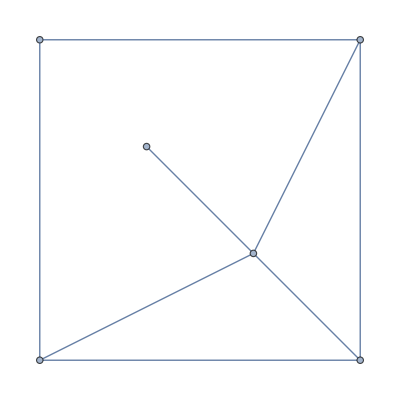
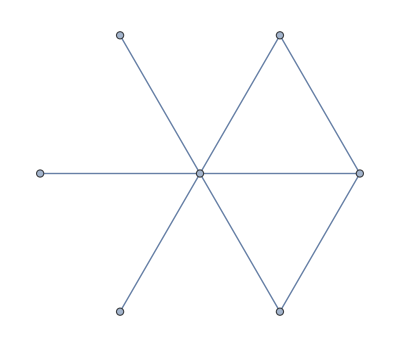
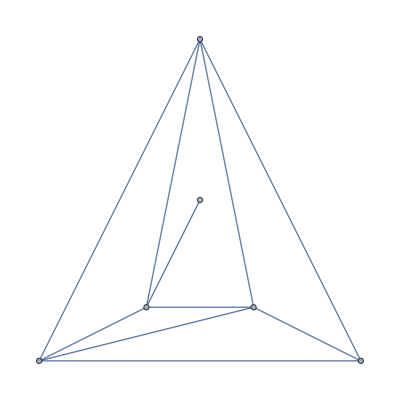
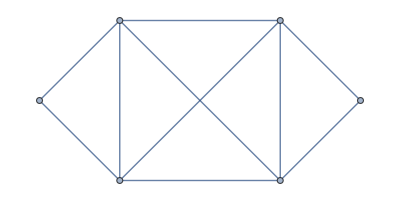
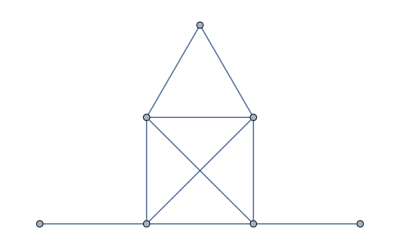
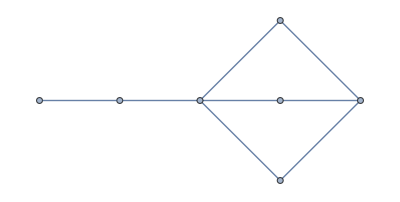
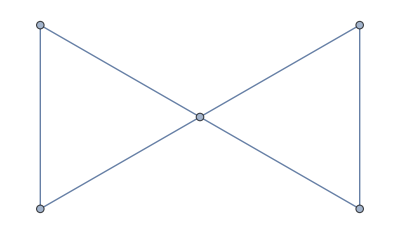
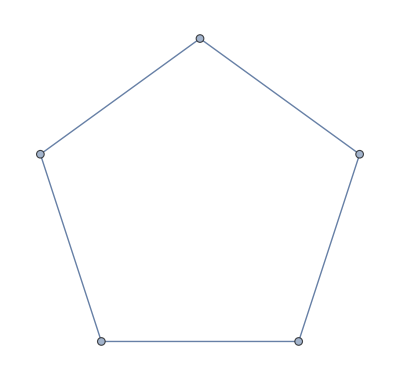
Small[{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}]

```mathematica
isospectralpairsconnected//Small (* These are the suspects. Many can immediately be eliminated after checking Euler characteristics or for reasons such as being clearly isomorphic. *)
```

```mathematica
DeterminantD/@{-Graphics-,-Graphics-,-Graphics-}//FullSimplify (* We here check for multiplicity. Each pair or set is checked individually. *)
```

{-576 ⅈ Sin[k/3]^3,6144 Sin[k/6]^2 Sin[k/3]^2,384 ⅈ Cos[k/6]^5 Sin[k/6]}

```mathematica
Finalisospectralpairsconnected={{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}; (* These are the final isospectral pairs with at most seven vertices after checking multiplicities. *)
```

```mathematica
Map[Graph[EdgeList@#,GraphLayout->"SpringElectricalEmbedding",ImageSize->70]&]/@Finalisospectralpairsconnected
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

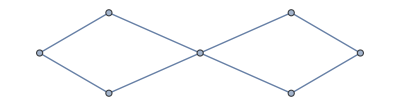
```mathematica
GraphPlot[EdgeList@-Graphics-,EdgeStyle->Thick]
```

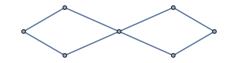

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}
```

{-192 ⅇ^(-ⅈ k) (-1+ⅇ^((ⅈ k)/2))^3 (1+ⅇ^((ⅈ k)/2)),-64 ⅇ^(-ⅈ k) (-1+ⅇ^((ⅈ k)/2))^3 (1+ⅇ^((ⅈ k)/2))}

Then for trees with at most ten vertices

```mathematica
trees=PendantEdgeAddAll[-Graphics-,8];
```

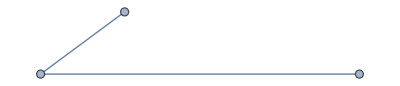
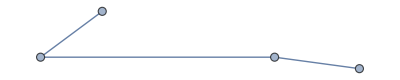
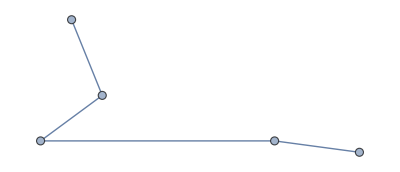
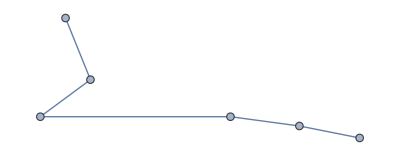
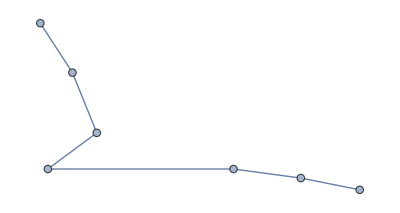
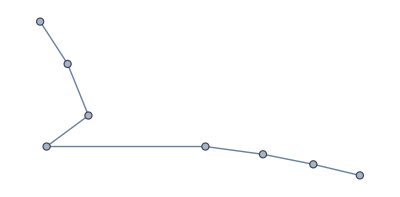
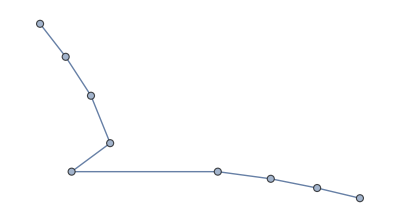
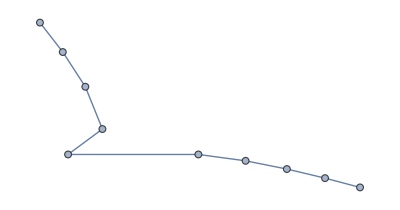
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
suspecttrees=IsospectralPairs[trees]
```

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify//Factor  (* We here check for multiplicity. Each pair is checked individually. *)
```

{-48 ⅇ^(-ⅈ k) (-1+ⅇ^((ⅈ k)/9)) (1+ⅇ^((ⅈ k)/9)) (1+ⅇ^((2 ⅈ k)/9))^2 (1-ⅇ^((ⅈ k)/9)+ⅇ^((2 ⅈ k)/9)) (1+ⅇ^((ⅈ k)/9)+ⅇ^((2 ⅈ k)/9)) (1+ⅇ^((4 ⅈ k)/9)) (3-4 ⅇ^((2 ⅈ k)/9)+3 ⅇ^((4 ⅈ k)/9)),48 ⅇ^(-ⅈ k) (-1+ⅇ^((ⅈ k)/9)) (1+ⅇ^((ⅈ k)/9)) (1+ⅇ^((2 ⅈ k)/9))^2 (1-ⅇ^((ⅈ k)/9)+ⅇ^((2 ⅈ k)/9)) (1+ⅇ^((ⅈ k)/9)+ⅇ^((2 ⅈ k)/9)) (1+ⅇ^((4 ⅈ k)/9)) (3-4 ⅇ^((2 ⅈ k)/9)+3 ⅇ^((4 ⅈ k)/9))}

```mathematica
Finalisospectraltrees={{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}};
(* The final checked trees with at most ten vertices *)
Map[GraphPlot[EdgeList@#,GraphLayout->"SpringEmbedding",ImageSize->70]&]/@Finalisospectraltrees
```

```mathematica
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}} (* Different embedding. *)
```

Here we do it for trees with twelve vertices.

```mathematica
treesten=PendantEdgeAddAll[-Graphics-,10]; (* Lets do it with up to 12 vertices. This takes a few hours on a laptop. *)
```

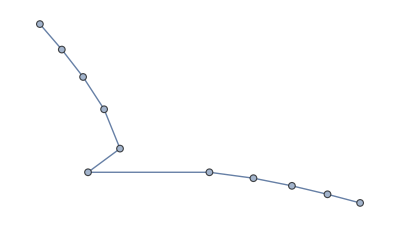
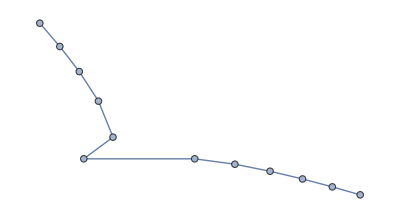
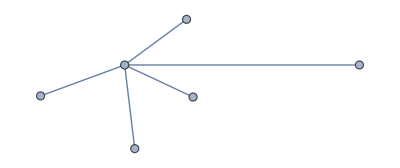
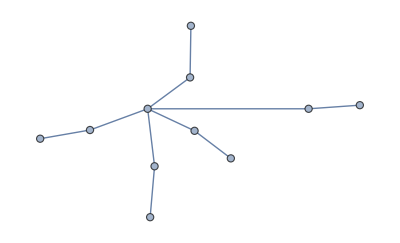
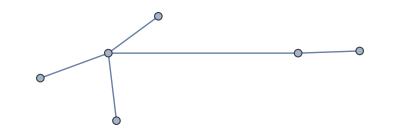
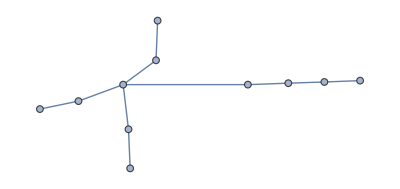
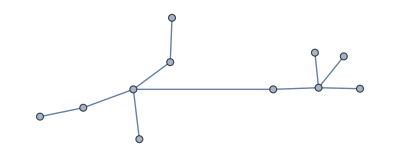
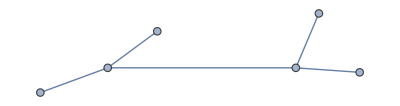
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
IsospectralPairs[treesten]  (* The suspects. *)
```

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify  (* Testing multiplicities *)
```

{-64 ⅇ^(-ⅈ k) (-9-6 ⅇ^((2 ⅈ k)/11)-5 ⅇ^((6 ⅈ k)/11)+2 ⅇ^((10 ⅈ k)/11)-2 ⅇ^((12 ⅈ k)/11)+5 ⅇ^((16 ⅈ k)/11)+6 ⅇ^((20 ⅈ k)/11)+9 ⅇ^(2 ⅈ k)),64 ⅇ^(-ⅈ k) (-9-6 ⅇ^((2 ⅈ k)/11)-5 ⅇ^((6 ⅈ k)/11)+2 ⅇ^((10 ⅈ k)/11)-2 ⅇ^((12 ⅈ k)/11)+5 ⅇ^((16 ⅈ k)/11)+6 ⅇ^((20 ⅈ k)/11)+9 ⅇ^(2 ⅈ k))}

```mathematica
Finalisospectraltreesten={{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}} (* The checked trees with up to twelve vertices *)
```

Here we do it for a decorated square.

```mathematica
treesfromsquare=PendantEdgeAddAll[-Graphics-,6]; (* Here we create a square decorated with edges and trees. *)
```

Below are the checked isospectral sets from a decorated square. There is one triplet and the rest are pairs. Note that the members of the pairs must be scaled to have the same length in order to be isospectral.

```mathematica
checkedsquarepairs=
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}
```

Here we do it for a decorated hexagon .

```mathematica
treesfromhexagon=PendantEdgeAddAll[-Graphics-,6];
```

Below are the checked decorated hexagon isospectral sets. I found one triplet and the rest are pairs.

```mathematica
checkedhexagonpairs={{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}.{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}
```

Below are checked isospectral pairs from this decorated graph - -Graphics-which was decorated with at most six edges.

```mathematica
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}
```

Below are checked isospectral pairs from this decorated graph - -Graphics-which was decorated with at most five edges.

```mathematica
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}
```

## The following cells check the isospectrality of one pair and one triplet from the paper which we do “by hand” in order to check the programs predictions.

The following cell gives the vertex and edge scattering matrix for graph b): -Graphics-which is the isospectral partner of the loop graph when L1=L3=1/4 and L2=2/4 according to Pistol, arXiv.
It also computes ∑(k) following Berkolaiko which shows that graph b) has the same eigenfrequencies as graph a).

```mathematica
L1=L3=2;
L2=4;
Sv=({{0, -1/2, 1/2, 1/2, 0, 1/2}, {1, 0, 0, 0, 0, 0}, {0, 1/2, 1/2, -1/2, 0, 1/2}, {0, 1/2, -1/2, 1/2, 0, 1/2}, {0, 1/2, 1/2, 1/2, 0, -1/2}, {0, 0, 0, 0, 1, 0}});
Se[k_]:=({{ⅇ^(ⅈ k L1), 0, 0, 0, 0, 0}, {0, ⅇ^(ⅈ k L1), 0, 0, 0, 0}, {0, 0, ⅇ^(ⅈ k L2), 0, 0, 0}, {0, 0, 0, ⅇ^(ⅈ k L2), 0, 0}, {0, 0, 0, 0, ⅇ^(ⅈ k L3), 0}, {0, 0, 0, 0, 0, ⅇ^(ⅈ k L3)}});
Id=({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}});
Sigma[k_]:=Det[Id-Sv.Se[k]]//FullSimplify
Sigma[k] (* The secular determinant *)

(* Here we do it again but with an extra valence two vertex on the left side of the loop to check *)
Sv=({{0, -1/2, 1/2, 0, 0, 1/2, 0, 1/2}, {1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 1/2, -1/2, 0, 0, 1/2, 0, 1/2}, {0, 1/2, 1/2, 0, 0, -1/2, 0, 1/2}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 1/2, 1/2, 0, 0, 1/2, 0, -1/2}, {0, 0, 0, 1, 0, 0, 0, 0}});

Se[k_]:=({{ⅇ^(ⅈ k L1), 0, 0, 0, 0, 0, 0, 0}, {0, ⅇ^(ⅈ k L1), 0, 0, 0, 0, 0, 0}, {0, 0, ⅇ^(ⅈ k L1), 0, 0, 0, 0, 0}, {0, 0, 0, ⅇ^(ⅈ k L1), 0, 0, 0, 0}, {0, 0, 0, 0, ⅇ^(ⅈ k L1), 0, 0, 0}, {0, 0, 0, 0, 0, ⅇ^(ⅈ k L1), 0, 0}, {0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k L1), 0}, {0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k L1)}});
Id=({{1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1}});
Sigma[k_]:=Det[Id-Sv.Se[k]]//FullSimplify;
Sigma[k]

L1=4;L2=4;
Det[({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})-({{0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}}).({{ⅇ^(ⅈ k L1), 0, 0, 0}, {0, ⅇ^(ⅈ k L1), 0, 0}, {0, 0, ⅇ^(ⅈ k L2), 0}, {0, 0, 0, ⅇ^(ⅈ k L2)}})]//Simplify (* The loop with two vertices. The secular determinant *)
DeterminantD[-Graphics-]//Simplify (* The same secular determinant apart from a factor which never gives a root *)
(* Solve[Sigma[k]==0,k]   The eigenfrequencies according to the handcalculated Sv and Se *)
GraphRoots[-Graphics-] (* The same eigenfrequencies according to my program. *)
Sv=({{0, -1/2, 0, 1/2, 1/2, 0, 1/2, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1/2, 0, -1/2, 1/2, 0, 1/2, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -1/2, 0, 1/2, 1/2, 0, 1/2, 0}, {0, 1/2, 0, 1/2, -1/2, 0, 1/2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1/2, 0, -1/2, 1/2, 0, 1/2, 0}, {0, 1/2, 0, 1/2, 1/2, 0, -1/2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 1/2, 0, 1/2, -1/2, 0, 1/2, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 1/2, 0, 1/2, 1/2, 0, -1/2, 0}});(*-Graphics-*)
Se[k_]:=({{ⅇ^(ⅈ k 2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, ⅇ^(ⅈ k 2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, ⅇ^(ⅈ k 2), 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, ⅇ^(ⅈ k 2), 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, ⅇ^(ⅈ k 1), 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, ⅇ^(ⅈ k 1), 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k 1), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k 1), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k 1), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k 1), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k 1), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k 1)}});
Id=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
Sigma[k_]:=Det[Id-Sv.Se[k]]//Simplify;
Sigma[k]
```

(-1+ⅇ^(8 ⅈ k))^2

(-1+ⅇ^(8 ⅈ k))^2

(-1+ⅇ^(8 ⅈ k))^2

-8 ⅇ^(-ⅈ k) (-1+ⅇ^(ⅈ k))^2

{{k→ConditionalExpression[6 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[2 π (-1+3 C[1]), C[1]∈ℤ]},{k→ConditionalExpression[2 (π+3 π C[1]), C[1]∈ℤ]}}

(-1+ⅇ^(8 ⅈ k))^2

The following cell shows that the graphs -Graphics-have the same secular determinant.

```mathematica
nn=nnm;
Subscript[L, 1]=nn;Subscript[L, 2]=1;Subscript[L, 3]=1;
sum=(Subscript[L, 1]+2 Subscript[L, 2]+2 Subscript[L, 3]);


Sv=({{0, -1/3, 2/3, 0, 2/3, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -1/2, 0, 1/2, 1/2, 0, 1/2, 0}, {0, 2/3, -1/3, 0, 2/3, 0, 0, 0, 0, 0}, {0, 0, 0, 1/2, 0, -1/2, 1/2, 0, 1/2, 0}, {0, 2/3, 2/3, 0, -1/3, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 1/2, 0, 1/2, -1/2, 0, 1/2, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 1/2, 0, 1/2, 1/2, 0, -1/2, 0}});  (* This is for -Graphics-*)
Se[k_]:=({{ⅇ^(ⅈ k Subscript[L, 1]), 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, ⅇ^(ⅈ k Subscript[L, 1]), 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, ⅇ^(ⅈ k Subscript[L, 2]), 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, ⅇ^(ⅈ k Subscript[L, 2]), 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 2]), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 2]), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 3]), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 3]), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 3]), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 3])}})
Id=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
Det[Id-Sv.Se[k]]//Simplify

Subscript[L, 1]=nn;Subscript[L, 2]=4;

Sv=({{0, -1/3, 2/3, 2/3}, {1, 0, 0, 0}, {0, 2/3, 2/3, -1/3}, {0, 2/3, -1/3, 2/3}});   (* This for-Graphics- *)
Se[k_]:=({{ⅇ^(ⅈ k Subscript[L, 1]), 0, 0, 0}, {0, ⅇ^(ⅈ k Subscript[L, 1]), 0, 0}, {0, 0, ⅇ^(ⅈ k Subscript[L, 2]), 0}, {0, 0, 0, ⅇ^(ⅈ k Subscript[L, 2])}});
Id=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
Det[Id-Sv.Se[k]]//Simplify
```

1/3 (-1+ⅇ^(4 ⅈ k)) (-3+ⅇ^(4 ⅈ k)-ⅇ^(2 ⅈ k nnm)+3 ⅇ^(2 ⅈ k (2+nnm)))

1/3 (-1+ⅇ^(4 ⅈ k)) (-3+ⅇ^(4 ⅈ k)-ⅇ^(2 ⅈ k nnm)+3 ⅇ^(2 ⅈ k (2+nnm)))

The following cell finds the secular determinant of -Graphics-by hand which agrees with the results of the program (apart from this factor which never contributes a root).

```mathematica
k=.
L1=4;
L2=2;
L3=2;
L4:=L1-L3;
Sv=({{2/3, -1/3, 2/3, 0, 0, 0, 0, 0}, {-1/3, 2/3, 2/3, 0, 0, 0, 0, 0}, {0, 0, 0, -1/3, 2/3, 0, 2/3, 0}, {2/3, 2/3, -1/3, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 2/3, -1/3, 0, 2/3, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 2/3, 2/3, 0, -1/3, 0}}); (* This is the bondscattering matrix I get *)

Se[k_]:=({{ⅇ^(ⅈ k L1), 0, 0, 0, 0, 0, 0, 0}, {0, ⅇ^(ⅈ k L1), 0, 0, 0, 0, 0, 0}, {0, 0, ⅇ^(ⅈ k L2), 0, 0, 0, 0, 0}, {0, 0, 0, ⅇ^(ⅈ k L2), 0, 0, 0, 0}, {0, 0, 0, 0, ⅇ^(ⅈ k L3), 0, 0, 0}, {0, 0, 0, 0, 0, ⅇ^(ⅈ k L3), 0, 0}, {0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k L4), 0}, {0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k L4)}});
Id=({{1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1}});
Se[k];
Det[Id-Sv.Se[k]]//Simplify                                        (* What the handcalculation gets*)
Sigma[k_]:=Det[Id-Sv.Se[k]]//FullSimplify;
Sigma[k];
DeterminantD[#,10]&@-Graphics-//Simplify (* What my program gets*)
```

1/9 (-1+ⅇ^(4 ⅈ k))^2 (9+11 ⅇ^(4 ⅈ k)+11 ⅇ^(8 ⅈ k)+9 ⅇ^(12 ⅈ k))

64 ⅇ^(-10 ⅈ k) (-1+ⅇ^(4 ⅈ k))^2 (9+11 ⅇ^(4 ⅈ k)+11 ⅇ^(8 ⅈ k)+9 ⅇ^(12 ⅈ k))

Here we test the two isospectral partners of the loop

```mathematica
conn=-Graphics-;
DeterminantD/@{-Graphics-,-Graphics-,-Graphics-}//Simplify
h4=VertexReplace[-Graphics-,Table[i->Subscript[a, i],{i,25}]];
h5=VertexReplace[-Graphics-,Table[i->Subscript[b, i],{i,25}]];
h6=VertexReplace[-Graphics-,Table[i->Subscript[c, i],{i,25}]];
{GraphPlot[h4,VertexLabels->"Name"],
GraphPlot[h5,VertexLabels->"Name"],
GraphPlot[h6,VertexLabels->"Name"]}

hx=GraphAddContract[h4,Allconnected⟦7⟧,Subscript[a, 3],2];
hy=GraphAddContract[h5,Allconnected⟦7⟧,Subscript[b, 3],2];
hx=Graph[hx,EdgeWeight->{1<->6->1}];
hy=Graph[hy,EdgeWeight->{1<->6->1}];
hz=GraphAddContract[h6,Allconnected⟦7⟧,Subscript[c, 1],1];
hw=GraphAddContract[h6,Allconnected⟦7⟧,Subscript[c, 3],1];
(DeterminantD[hx]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
(DeterminantD[hy]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
(DeterminantD[hz]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
(DeterminantD[hw]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
{GraphPlot[hx,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],GraphPlot[hy,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
```

{256 ⅇ^(-ⅈ k) (-1+ⅇ^(ⅈ k))^2,128 ⅇ^(-ⅈ k) (-1+ⅇ^(ⅈ k))^2,16384 ⅇ^(-ⅈ k) (-1+ⅇ^(ⅈ k))^2}

{-Graphics-,-Graphics-,-Graphics-}

(-1+ⅇ^((ⅈ k)/16))^5 (1+ⅇ^((ⅈ k)/16)+ⅇ^((ⅈ k)/8)+ⅇ^((3 ⅈ k)/16))^3 (20+40 ⅇ^((ⅈ k)/16)+55 ⅇ^((ⅈ k)/8)+50 ⅇ^((3 ⅈ k)/16)+71 ⅇ^((ⅈ k)/4)+88 ⅇ^((5 ⅈ k)/16)+95 ⅇ^((3 ⅈ k)/8)+82 ⅇ^((7 ⅈ k)/16)+91 ⅇ^((ⅈ k)/2)+96 ⅇ^((9 ⅈ k)/16)+91 ⅇ^((5 ⅈ k)/8)+82 ⅇ^((11 ⅈ k)/16)+95 ⅇ^((3 ⅈ k)/4)+88 ⅇ^((13 ⅈ k)/16)+71 ⅇ^((7 ⅈ k)/8)+50 ⅇ^((15 ⅈ k)/16)+55 ⅇ^(ⅈ k)+40 ⅇ^((17 ⅈ k)/16)+20 ⅇ^((9 ⅈ k)/8))

(-1+ⅇ^((ⅈ k)/16))^5 (1+ⅇ^((ⅈ k)/16)+ⅇ^((ⅈ k)/8)+ⅇ^((3 ⅈ k)/16))^3 (20+40 ⅇ^((ⅈ k)/16)+55 ⅇ^((ⅈ k)/8)+50 ⅇ^((3 ⅈ k)/16)+71 ⅇ^((ⅈ k)/4)+88 ⅇ^((5 ⅈ k)/16)+95 ⅇ^((3 ⅈ k)/8)+82 ⅇ^((7 ⅈ k)/16)+91 ⅇ^((ⅈ k)/2)+96 ⅇ^((9 ⅈ k)/16)+91 ⅇ^((5 ⅈ k)/8)+82 ⅇ^((11 ⅈ k)/16)+95 ⅇ^((3 ⅈ k)/4)+88 ⅇ^((13 ⅈ k)/16)+71 ⅇ^((7 ⅈ k)/8)+50 ⅇ^((15 ⅈ k)/16)+55 ⅇ^(ⅈ k)+40 ⅇ^((17 ⅈ k)/16)+20 ⅇ^((9 ⅈ k)/8))

(-1+ⅇ^((ⅈ k)/24))^5 (1+ⅇ^((ⅈ k)/24)+ⅇ^((ⅈ k)/12)+ⅇ^((ⅈ k)/8))^3 (1+ⅇ^((ⅈ k)/6))^2 (30+60 ⅇ^((ⅈ k)/24)+77 ⅇ^((ⅈ k)/12)+66 ⅇ^((ⅈ k)/8)+49 ⅇ^((ⅈ k)/6)+36 ⅇ^((5 ⅈ k)/24)+26 ⅇ^((ⅈ k)/4)+32 ⅇ^((7 ⅈ k)/24)+94 ⅇ^((ⅈ k)/3)+140 ⅇ^((3 ⅈ k)/8)+141 ⅇ^((5 ⅈ k)/12)+98 ⅇ^((11 ⅈ k)/24)+75 ⅇ^((ⅈ k)/2)+72 ⅇ^((13 ⅈ k)/24)+75 ⅇ^((7 ⅈ k)/12)+98 ⅇ^((5 ⅈ k)/8)+141 ⅇ^((2 ⅈ k)/3)+140 ⅇ^((17 ⅈ k)/24)+94 ⅇ^((3 ⅈ k)/4)+32 ⅇ^((19 ⅈ k)/24)+26 ⅇ^((5 ⅈ k)/6)+36 ⅇ^((7 ⅈ k)/8)+49 ⅇ^((11 ⅈ k)/12)+66 ⅇ^((23 ⅈ k)/24)+77 ⅇ^(ⅈ k)+60 ⅇ^((25 ⅈ k)/24)+30 ⅇ^((13 ⅈ k)/12))

(-1+ⅇ^((ⅈ k)/24))^5 (1+ⅇ^((ⅈ k)/24)+ⅇ^((ⅈ k)/12)+ⅇ^((ⅈ k)/8))^3 (1+ⅇ^((ⅈ k)/3))^2 (30+60 ⅇ^((ⅈ k)/24)+77 ⅇ^((ⅈ k)/12)+66 ⅇ^((ⅈ k)/8)+99 ⅇ^((ⅈ k)/6)+136 ⅇ^((5 ⅈ k)/24)+147 ⅇ^((ⅈ k)/4)+130 ⅇ^((7 ⅈ k)/24)+139 ⅇ^((ⅈ k)/3)+152 ⅇ^((3 ⅈ k)/8)+139 ⅇ^((5 ⅈ k)/12)+130 ⅇ^((11 ⅈ k)/24)+147 ⅇ^((ⅈ k)/2)+136 ⅇ^((13 ⅈ k)/24)+99 ⅇ^((7 ⅈ k)/12)+66 ⅇ^((5 ⅈ k)/8)+77 ⅇ^((2 ⅈ k)/3)+60 ⅇ^((17 ⅈ k)/24)+30 ⅇ^((3 ⅈ k)/4))

## Experiments with the star graph.

Here we test the isospectrality of the decorated star. We first do it for a star with equal length of the leaves.

```mathematica
star=.;loop1=.;loop2=.;v1=.;v2=.;u=.;v=.;
v=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];
star=VertexReplace[-Graphics-,Table[i->Subscript[a, i],{i,25}]];

loop1=VertexReplace[-Graphics-,Table[i->Subscript[b1, i],{i,25}]];loop2=VertexReplace[-Graphics-,Table[i->Subscript[b2, i],{i,25}]];
loop3=VertexReplace[-Graphics-,Table[i->Subscript[b3, i],{i,25}]];


v1=VertexReplace[v,Table[i->Subscript[d1, i],{i,25}]];
v2=VertexReplace[v,Table[i->Subscript[d2, i],{i,25}]];
v3=VertexReplace[v,Table[i->Subscript[d3, i],{i,25}]];


{decoratedstar1=VertexReplace[#,atable]&@IndexGraph@GraphAddContract3[star,loop1,loop2,loop3,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b1, 1],Subscript[b2, 1],Subscript[b3, 1]],
decoratedstar2=VertexReplace[#,btable]&@IndexGraph@GraphAddContract3[star,loop1,loop2,v1,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b1, 1],Subscript[b2, 1],Subscript[d1, 2]],
decoratedstar3=VertexReplace[#,ctable]&@IndexGraph@GraphAddContract3[star,loop1,v2,v1,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b1, 1],Subscript[d2, 2],Subscript[d1, 2]],
decoratedstar4=VertexReplace[#,dtable]&@IndexGraph@GraphAddContract3[star,v3,v2,v1,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[d3, 2],Subscript[d2, 2],Subscript[d1, 2]]}


(DeterminantD[decoratedstar1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
(DeterminantD[decoratedstar2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
(DeterminantD[decoratedstar3]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
(DeterminantD[decoratedstar4]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

(-1+ⅇ^(2 ⅈ))^4 (1+ⅇ^(2 ⅈ))^5 (1+ⅇ^(4 ⅈ))^3 (3-4 ⅇ^(2 ⅈ)+4 ⅇ^(4 ⅈ)-4 ⅇ^(6 ⅈ)+3 ⅇ^(8 ⅈ))^2 (3+4 ⅇ^(2 ⅈ)+4 ⅇ^(4 ⅈ)+4 ⅇ^(6 ⅈ)+3 ⅇ^(8 ⅈ))

(-1+ⅇ^(2 ⅈ))^4 (1+ⅇ^(2 ⅈ))^5 (1+ⅇ^(4 ⅈ))^3 (3-4 ⅇ^(2 ⅈ)+4 ⅇ^(4 ⅈ)-4 ⅇ^(6 ⅈ)+3 ⅇ^(8 ⅈ))^2 (3+4 ⅇ^(2 ⅈ)+4 ⅇ^(4 ⅈ)+4 ⅇ^(6 ⅈ)+3 ⅇ^(8 ⅈ))

(-1+ⅇ^(2 ⅈ))^4 (1+ⅇ^(2 ⅈ))^5 (1+ⅇ^(4 ⅈ))^3 (3-4 ⅇ^(2 ⅈ)+4 ⅇ^(4 ⅈ)-4 ⅇ^(6 ⅈ)+3 ⅇ^(8 ⅈ))^2 (3+4 ⅇ^(2 ⅈ)+4 ⅇ^(4 ⅈ)+4 ⅇ^(6 ⅈ)+3 ⅇ^(8 ⅈ))

«1 more identical outputs»

We then do it for a star with symbolic edgelengths.

```mathematica
c1=.;c2=.;
longstar=Graph[{1<->12,12<->2,1<->13,13<->3,1<->14,14<->4}];
longstar=VertexReplace[-Graphics-,Table[i->Subscript[a, i],{i,25}]];

{decoratedlongstar1=VertexReplace[#,atable]&@IndexGraph@GraphAddContract3[longstar,loop1,loop2,loop3,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b1, 1],Subscript[b2, 1],Subscript[b3, 1]],
decoratedlongstar2=VertexReplace[#,btable]&@IndexGraph@GraphAddContract3[longstar,loop1,loop2,v1,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b1, 1],Subscript[b2, 1],Subscript[d1, 2]],
decoratedlongstar3=VertexReplace[#,ctable]&@IndexGraph@GraphAddContract3[longstar,loop1,v2,v1,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b1, 1],Subscript[d2, 2],Subscript[d1, 2]],
decoratedlongstar4=VertexReplace[#,dtable]&@IndexGraph@GraphAddContract3[longstar,v3,v2,v1,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[d3, 2],Subscript[d2, 2],Subscript[d1, 2]]};

decoratedlongstar1=VertexReplace[#,atable]&@IndexGraph@Graph[decoratedlongstar1,EdgeWeight->{Subscript[a, 1]<->Subscript[a, 2]->c1,Subscript[a, 1]<->Subscript[a, 3]->c2}];
decoratedlongstar2=VertexReplace[#,btable]&@IndexGraph@Graph[decoratedlongstar2,EdgeWeight->{Subscript[b, 1]<->Subscript[b, 2]->c1,Subscript[b, 1]<->Subscript[b, 3]->c2}];
decoratedlongstar3=VertexReplace[#,ctable]&@IndexGraph@Graph[decoratedlongstar3,EdgeWeight->{Subscript[c, 1]<->Subscript[c, 2]->c1,Subscript[c, 1]<->Subscript[c, 3]->c2}];
decoratedlongstar4=VertexReplace[#,dtable]&@IndexGraph@Graph[decoratedlongstar4,EdgeWeight->{Subscript[d, 1]<->Subscript[d, 2]->c1,Subscript[d, 1]<->Subscript[d, 3]->c2}];

{GraphPlot[decoratedlongstar1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[decoratedlongstar2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[decoratedlongstar3,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[decoratedlongstar4,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]}

x1=(DeterminantD[decoratedlongstar1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
x2=(DeterminantD[decoratedlongstar2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
x3=(DeterminantD[decoratedlongstar3]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
x4=(DeterminantD[decoratedlongstar4]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
{x1==x2,x1==x3,x1==x4}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

(-1+ⅇ^((216 ⅈ)/(28+c1+c2)))^3 (-81+9 ⅇ^((108 ⅈ)/(28+c1+c2))+81 ⅇ^((216 ⅈ)/(28+c1+c2))-33 ⅇ^((324 ⅈ)/(28+c1+c2))-27 ⅇ^((432 ⅈ)/(28+c1+c2))+19 ⅇ^((540 ⅈ)/(28+c1+c2))+3 ⅇ^((648 ⅈ)/(28+c1+c2))-3 ⅇ^((756 ⅈ)/(28+c1+c2))+9 ⅇ^((54 ⅈ (1+c1))/(28+c1+c2))+3 ⅇ^((54 ⅈ (3+c1))/(28+c1+c2))-33 ⅇ^((54 ⅈ (5+c1))/(28+c1+c2))-19 ⅇ^((54 ⅈ (7+c1))/(28+c1+c2))+19 ⅇ^((54 ⅈ (9+c1))/(28+c1+c2))+33 ⅇ^((54 ⅈ (11+c1))/(28+c1+c2))-3 ⅇ^((54 ⅈ (13+c1))/(28+c1+c2))-9 ⅇ^((54 ⅈ (15+c1))/(28+c1+c2))+9 ⅇ^((54 ⅈ (1+c2))/(28+c1+c2))+3 ⅇ^((54 ⅈ (3+c2))/(28+c1+c2))-33 ⅇ^((54 ⅈ (5+c2))/(28+c1+c2))-19 ⅇ^((54 ⅈ (7+c2))/(28+c1+c2))+19 ⅇ^((54 ⅈ (9+c2))/(28+c1+c2))+33 ⅇ^((54 ⅈ (11+c2))/(28+c1+c2))-3 ⅇ^((54 ⅈ (13+c2))/(28+c1+c2))-9 ⅇ^((54 ⅈ (15+c2))/(28+c1+c2))+3 ⅇ^((54 ⅈ (2+c1+c2))/(28+c1+c2))-3 ⅇ^((54 ⅈ (4+c1+c2))/(28+c1+c2))-19 ⅇ^((54 ⅈ (6+c1+c2))/(28+c1+c2))+27 ⅇ^((54 ⅈ (8+c1+c2))/(28+c1+c2))+33 ⅇ^((54 ⅈ (10+c1+c2))/(28+c1+c2))-81 ⅇ^((54 ⅈ (12+c1+c2))/(28+c1+c2))-9 ⅇ^((54 ⅈ (14+c1+c2))/(28+c1+c2))+81 ⅇ^((54 ⅈ (16+c1+c2))/(28+c1+c2)))

(-1+ⅇ^((216 ⅈ)/(28+c1+c2)))^3 (-81+9 ⅇ^((108 ⅈ)/(28+c1+c2))+81 ⅇ^((216 ⅈ)/(28+c1+c2))-33 ⅇ^((324 ⅈ)/(28+c1+c2))-27 ⅇ^((432 ⅈ)/(28+c1+c2))+19 ⅇ^((540 ⅈ)/(28+c1+c2))+3 ⅇ^((648 ⅈ)/(28+c1+c2))-3 ⅇ^((756 ⅈ)/(28+c1+c2))+9 ⅇ^((54 ⅈ (1+c1))/(28+c1+c2))+3 ⅇ^((54 ⅈ (3+c1))/(28+c1+c2))-33 ⅇ^((54 ⅈ (5+c1))/(28+c1+c2))-19 ⅇ^((54 ⅈ (7+c1))/(28+c1+c2))+19 ⅇ^((54 ⅈ (9+c1))/(28+c1+c2))+33 ⅇ^((54 ⅈ (11+c1))/(28+c1+c2))-3 ⅇ^((54 ⅈ (13+c1))/(28+c1+c2))-9 ⅇ^((54 ⅈ (15+c1))/(28+c1+c2))+9 ⅇ^((54 ⅈ (1+c2))/(28+c1+c2))+3 ⅇ^((54 ⅈ (3+c2))/(28+c1+c2))-33 ⅇ^((54 ⅈ (5+c2))/(28+c1+c2))-19 ⅇ^((54 ⅈ (7+c2))/(28+c1+c2))+19 ⅇ^((54 ⅈ (9+c2))/(28+c1+c2))+33 ⅇ^((54 ⅈ (11+c2))/(28+c1+c2))-3 ⅇ^((54 ⅈ (13+c2))/(28+c1+c2))-9 ⅇ^((54 ⅈ (15+c2))/(28+c1+c2))+3 ⅇ^((54 ⅈ (2+c1+c2))/(28+c1+c2))-3 ⅇ^((54 ⅈ (4+c1+c2))/(28+c1+c2))-19 ⅇ^((54 ⅈ (6+c1+c2))/(28+c1+c2))+27 ⅇ^((54 ⅈ (8+c1+c2))/(28+c1+c2))+33 ⅇ^((54 ⅈ (10+c1+c2))/(28+c1+c2))-81 ⅇ^((54 ⅈ (12+c1+c2))/(28+c1+c2))-9 ⅇ^((54 ⅈ (14+c1+c2))/(28+c1+c2))+81 ⅇ^((54 ⅈ (16+c1+c2))/(28+c1+c2)))

(-1+ⅇ^((216 ⅈ)/(28+c1+c2)))^3 (-81+9 ⅇ^((108 ⅈ)/(28+c1+c2))+81 ⅇ^((216 ⅈ)/(28+c1+c2))-33 ⅇ^((324 ⅈ)/(28+c1+c2))-27 ⅇ^((432 ⅈ)/(28+c1+c2))+19 ⅇ^((540 ⅈ)/(28+c1+c2))+3 ⅇ^((648 ⅈ)/(28+c1+c2))-3 ⅇ^((756 ⅈ)/(28+c1+c2))+9 ⅇ^((54 ⅈ (1+c1))/(28+c1+c2))+3 ⅇ^((54 ⅈ (3+c1))/(28+c1+c2))-33 ⅇ^((54 ⅈ (5+c1))/(28+c1+c2))-19 ⅇ^((54 ⅈ (7+c1))/(28+c1+c2))+19 ⅇ^((54 ⅈ (9+c1))/(28+c1+c2))+33 ⅇ^((54 ⅈ (11+c1))/(28+c1+c2))-3 ⅇ^((54 ⅈ (13+c1))/(28+c1+c2))-9 ⅇ^((54 ⅈ (15+c1))/(28+c1+c2))+9 ⅇ^((54 ⅈ (1+c2))/(28+c1+c2))+3 ⅇ^((54 ⅈ (3+c2))/(28+c1+c2))-33 ⅇ^((54 ⅈ (5+c2))/(28+c1+c2))-19 ⅇ^((54 ⅈ (7+c2))/(28+c1+c2))+19 ⅇ^((54 ⅈ (9+c2))/(28+c1+c2))+33 ⅇ^((54 ⅈ (11+c2))/(28+c1+c2))-3 ⅇ^((54 ⅈ (13+c2))/(28+c1+c2))-9 ⅇ^((54 ⅈ (15+c2))/(28+c1+c2))+3 ⅇ^((54 ⅈ (2+c1+c2))/(28+c1+c2))-3 ⅇ^((54 ⅈ (4+c1+c2))/(28+c1+c2))-19 ⅇ^((54 ⅈ (6+c1+c2))/(28+c1+c2))+27 ⅇ^((54 ⅈ (8+c1+c2))/(28+c1+c2))+33 ⅇ^((54 ⅈ (10+c1+c2))/(28+c1+c2))-81 ⅇ^((54 ⅈ (12+c1+c2))/(28+c1+c2))-9 ⅇ^((54 ⅈ (14+c1+c2))/(28+c1+c2))+81 ⅇ^((54 ⅈ (16+c1+c2))/(28+c1+c2)))

«1 more identical outputs»

{True,True,True}

And finally lets attach graphs at possible hot vertices. If c1 or c2 are not 1 there are no hot vertices.

```mathematica
c1=3;c2=2;
decoratedlongstar2attached1=Graph[#,EdgeWeight->{Subscript[b, 1]<->Subscript[b, 2]->c1,Subscript[b, 2]<->Subscript[b, 1]->c1,Subscript[b, 1]<->Subscript[b, 3]->c2,Subscript[b, 3]<->Subscript[b, 1]->c2}]&@GraphAddContract[decoratedlongstar2,Allconnected[[9]],Subscript[b, 26],1];
decoratedlongstar3attached1=Graph[#,EdgeWeight->{Subscript[c, 1]<->Subscript[c, 2]->c1,Subscript[c, 2]<->Subscript[c, 1]->c1,Subscript[c, 1]<->Subscript[c, 3]->c2,Subscript[c, 3]<->Subscript[c, 1]->c2}]&@GraphAddContract[decoratedlongstar3,Allconnected[[9]],Subscript[c, 27],1];
decoratedlongstar4attached1=Graph[#,EdgeWeight->{Subscript[d, 1]<->Subscript[d, 2]->c1,Subscript[d, 2]<->Subscript[d, 1]->c1,Subscript[d, 1]<->Subscript[d, 3]->c2,Subscript[d, 3]<->Subscript[d, 1]->c2}]&@GraphAddContract[decoratedlongstar4,Allconnected[[9]],Subscript[d, 28],1];

GraphPlot[decoratedlongstar2attached1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"];
GraphPlot[decoratedlongstar3attached1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"];
GraphPlot[decoratedlongstar4attached1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"];

{GraphPlot[decoratedlongstar2attached1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],x1=(DeterminantD[decoratedlongstar2attached1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}}
{GraphPlot[decoratedlongstar3attached1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],x2=(DeterminantD[decoratedlongstar3attached1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}}
{GraphPlot[decoratedlongstar4attached1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],x3=(DeterminantD[decoratedlongstar4attached1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}}
{x1==x2,x1==x3}
GraphPlot[decoratedlongstar2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"];  (* 26, 27, 28 are hot vertices, 2, 3, 4 are also hot vertices from the second set. *)   
None;
```

{-Graphics-,(-1+ⅇ^((27 ⅈ)/40))^6 (1+ⅇ^((27 ⅈ)/40)+ⅇ^((27 ⅈ)/20)+ⅇ^((81 ⅈ)/40))^4 (1+ⅇ^((27 ⅈ)/10))^3 (675+1350 ⅇ^((27 ⅈ)/40)+2187 ⅇ^((27 ⅈ)/20)+2268 ⅇ^((81 ⅈ)/40)+2625 ⅇ^((27 ⅈ)/10)+2550 ⅇ^((27 ⅈ)/8)+2355 ⅇ^((81 ⅈ)/20)+2136 ⅇ^((189 ⅈ)/40)+1788 ⅇ^((27 ⅈ)/5)+1572 ⅇ^((243 ⅈ)/40)+944 ⅇ^((27 ⅈ)/4)+736 ⅇ^((297 ⅈ)/40)+799 ⅇ^((81 ⅈ)/10)+902 ⅇ^((351 ⅈ)/40)+1077 ⅇ^((189 ⅈ)/20)+724 ⅇ^((81 ⅈ)/8)+817 ⅇ^((54 ⅈ)/5)+666 ⅇ^((459 ⅈ)/40)+865 ⅇ^((243 ⅈ)/20)+1104 ⅇ^((513 ⅈ)/40)+1674 ⅇ^((27 ⅈ)/2)+2372 ⅇ^((567 ⅈ)/40)+2990 ⅇ^((297 ⅈ)/20)+3784 ⅇ^((621 ⅈ)/40)+4628 ⅇ^((81 ⅈ)/5)+4984 ⅇ^((135 ⅈ)/8)+4628 ⅇ^((351 ⅈ)/20)+3784 ⅇ^((729 ⅈ)/40)+2990 ⅇ^((189 ⅈ)/10)+2372 ⅇ^((783 ⅈ)/40)+1674 ⅇ^((81 ⅈ)/4)+1104 ⅇ^((837 ⅈ)/40)+865 ⅇ^((108 ⅈ)/5)+666 ⅇ^((891 ⅈ)/40)+817 ⅇ^((459 ⅈ)/20)+724 ⅇ^((189 ⅈ)/8)+1077 ⅇ^((243 ⅈ)/10)+902 ⅇ^((999 ⅈ)/40)+799 ⅇ^((513 ⅈ)/20)+736 ⅇ^((1053 ⅈ)/40)+944 ⅇ^(27 ⅈ)+1572 ⅇ^((1107 ⅈ)/40)+1788 ⅇ^((567 ⅈ)/20)+2136 ⅇ^((1161 ⅈ)/40)+2355 ⅇ^((297 ⅈ)/10)+2550 ⅇ^((243 ⅈ)/8)+2625 ⅇ^((621 ⅈ)/20)+2268 ⅇ^((1269 ⅈ)/40)+2187 ⅇ^((162 ⅈ)/5)+1350 ⅇ^((1323 ⅈ)/40)+675 ⅇ^((135 ⅈ)/4))}

{-Graphics-,(-1+ⅇ^((27 ⅈ)/40))^6 (1+ⅇ^((27 ⅈ)/40)+ⅇ^((27 ⅈ)/20)+ⅇ^((81 ⅈ)/40))^4 (1+ⅇ^((27 ⅈ)/10))^3 (675+1350 ⅇ^((27 ⅈ)/40)+2187 ⅇ^((27 ⅈ)/20)+2268 ⅇ^((81 ⅈ)/40)+2625 ⅇ^((27 ⅈ)/10)+2550 ⅇ^((27 ⅈ)/8)+2295 ⅇ^((81 ⅈ)/20)+2016 ⅇ^((189 ⅈ)/40)+1632 ⅇ^((27 ⅈ)/5)+1476 ⅇ^((243 ⅈ)/40)+864 ⅇ^((27 ⅈ)/4)+672 ⅇ^((297 ⅈ)/40)+807 ⅇ^((81 ⅈ)/10)+1014 ⅇ^((351 ⅈ)/40)+1113 ⅇ^((189 ⅈ)/20)+588 ⅇ^((81 ⅈ)/8)+637 ⅇ^((54 ⅈ)/5)+602 ⅇ^((459 ⅈ)/40)+837 ⅇ^((243 ⅈ)/20)+1080 ⅇ^((513 ⅈ)/40)+1846 ⅇ^((27 ⅈ)/2)+2708 ⅇ^((567 ⅈ)/40)+3250 ⅇ^((297 ⅈ)/20)+3808 ⅇ^((621 ⅈ)/40)+4656 ⅇ^((81 ⅈ)/5)+5048 ⅇ^((135 ⅈ)/8)+4656 ⅇ^((351 ⅈ)/20)+3808 ⅇ^((729 ⅈ)/40)+3250 ⅇ^((189 ⅈ)/10)+2708 ⅇ^((783 ⅈ)/40)+1846 ⅇ^((81 ⅈ)/4)+1080 ⅇ^((837 ⅈ)/40)+837 ⅇ^((108 ⅈ)/5)+602 ⅇ^((891 ⅈ)/40)+637 ⅇ^((459 ⅈ)/20)+588 ⅇ^((189 ⅈ)/8)+1113 ⅇ^((243 ⅈ)/10)+1014 ⅇ^((999 ⅈ)/40)+807 ⅇ^((513 ⅈ)/20)+672 ⅇ^((1053 ⅈ)/40)+864 ⅇ^(27 ⅈ)+1476 ⅇ^((1107 ⅈ)/40)+1632 ⅇ^((567 ⅈ)/20)+2016 ⅇ^((1161 ⅈ)/40)+2295 ⅇ^((297 ⅈ)/10)+2550 ⅇ^((243 ⅈ)/8)+2625 ⅇ^((621 ⅈ)/20)+2268 ⅇ^((1269 ⅈ)/40)+2187 ⅇ^((162 ⅈ)/5)+1350 ⅇ^((1323 ⅈ)/40)+675 ⅇ^((135 ⅈ)/4))}

{-Graphics-,(-1+ⅇ^((27 ⅈ)/40))^6 (1+ⅇ^((27 ⅈ)/40)+ⅇ^((27 ⅈ)/20)+ⅇ^((81 ⅈ)/40))^4 (1+ⅇ^((27 ⅈ)/10))^3 (675+1350 ⅇ^((27 ⅈ)/40)+2187 ⅇ^((27 ⅈ)/20)+2268 ⅇ^((81 ⅈ)/40)+2565 ⅇ^((27 ⅈ)/10)+2430 ⅇ^((27 ⅈ)/8)+2139 ⅇ^((81 ⅈ)/20)+1920 ⅇ^((189 ⅈ)/40)+1572 ⅇ^((27 ⅈ)/5)+1452 ⅇ^((243 ⅈ)/40)+924 ⅇ^((27 ⅈ)/4)+816 ⅇ^((297 ⅈ)/40)+843 ⅇ^((81 ⅈ)/10)+846 ⅇ^((351 ⅈ)/40)+861 ⅇ^((189 ⅈ)/20)+444 ⅇ^((81 ⅈ)/8)+517 ⅇ^((54 ⅈ)/5)+506 ⅇ^((459 ⅈ)/40)+957 ⅇ^((243 ⅈ)/20)+1416 ⅇ^((513 ⅈ)/40)+2158 ⅇ^((27 ⅈ)/2)+2804 ⅇ^((567 ⅈ)/40)+3370 ⅇ^((297 ⅈ)/20)+3952 ⅇ^((621 ⅈ)/40)+4656 ⅇ^((81 ⅈ)/5)+4904 ⅇ^((135 ⅈ)/8)+4656 ⅇ^((351 ⅈ)/20)+3952 ⅇ^((729 ⅈ)/40)+3370 ⅇ^((189 ⅈ)/10)+2804 ⅇ^((783 ⅈ)/40)+2158 ⅇ^((81 ⅈ)/4)+1416 ⅇ^((837 ⅈ)/40)+957 ⅇ^((108 ⅈ)/5)+506 ⅇ^((891 ⅈ)/40)+517 ⅇ^((459 ⅈ)/20)+444 ⅇ^((189 ⅈ)/8)+861 ⅇ^((243 ⅈ)/10)+846 ⅇ^((999 ⅈ)/40)+843 ⅇ^((513 ⅈ)/20)+816 ⅇ^((1053 ⅈ)/40)+924 ⅇ^(27 ⅈ)+1452 ⅇ^((1107 ⅈ)/40)+1572 ⅇ^((567 ⅈ)/20)+1920 ⅇ^((1161 ⅈ)/40)+2139 ⅇ^((297 ⅈ)/10)+2430 ⅇ^((243 ⅈ)/8)+2565 ⅇ^((621 ⅈ)/20)+2268 ⅇ^((1269 ⅈ)/40)+2187 ⅇ^((162 ⅈ)/5)+1350 ⅇ^((1323 ⅈ)/40)+675 ⅇ^((135 ⅈ)/4))}

{False,False}

Here we test the isospectral pairs -Graphics- and-Graphics-for hot vertices.

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];
v=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];  (* u = -Graphics- and the isospectral partner is v = -Graphics-. *)

s=Graph[{1<->2,2<->3,3<->4,4<->5,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}];
t=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->3,5<->7,7<->8,8<->9,9<->10}]; (* s = -Graphics- and t = -Graphics- are the other two isospectral partners. *)

u=VertexReplace[u,Table[i->Subscript[a, i],{i,55}]];  (* This is a loop. Hot vertices are all of them, Subscript[a, 1]-Subscript[a, 8] *)
v=VertexReplace[v,Table[i->Subscript[b, i],{i,55}]]; (* Hot vertex is Subscript[b, 2] -Graphics-*)
s=VertexReplace[s,Table[i->Subscript[c, i],{i,55}]]; (* Hot vertices are Subscript[c, 3] and Subscript[c, 7] -Graphics- *)
t=VertexReplace[t,Table[i->Subscript[d, i],{i,55}]]; (* Hot vertex is Subscript[d, 3] -Graphics- *)
w1=Allconnected⟦151⟧;
GraphPlot[w1,VertexLabels->"Name"];
w1=VertexReplace[w1,Table[i->Subscript[e, i],{i,25}]];

h1=GraphAddContract[u,w1,Subscript[a, 1],Subscript[e, 5]];
h2=GraphAddContract[v,w1,Subscript[b, 2],Subscript[e, 5]];

h3=GraphAddContract[s,w1,Subscript[c, 7],Subscript[e, 2]];
h4=GraphAddContract[t,w1,Subscript[d, 3],Subscript[e, 2]];
h5=GraphAddContract[s,w1,Subscript[c, 3],Subscript[e, 2]];
h6=GraphAddContract[t,w1,Subscript[d, 5],Subscript[e, 2]];(* Subscript[d, 5] does not work *)

g=GraphAddContract[u,v,Subscript[a, 1],Subscript[e, 2]];
GraphPlot[s,EdgeLabels->"EdgeWeight",VertexLabels->"Name"];
GraphPlot[t,EdgeLabels->"EdgeWeight",VertexLabels->"Name"];
DeterminantD[s]//Simplify;
DeterminantD[t]//Simplify;
(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
Print["next set"]
xx1=(DeterminantD[h3]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
xx2=(DeterminantD[h4]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
xx3=(DeterminantD[h5]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
xx4=(DeterminantD[h6]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
(DeterminantD[h6]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
{xx1==xx2,xx1==xx3}
```

(-1+ⅇ^((ⅈ k)/16))^4 (1+ⅇ^((ⅈ k)/16))^2 (1+ⅇ^((ⅈ k)/8))^3 (15+30 ⅇ^((ⅈ k)/16)+33 ⅇ^((ⅈ k)/8)+24 ⅇ^((3 ⅈ k)/16)+39 ⅇ^((ⅈ k)/4)+62 ⅇ^((5 ⅈ k)/16)+74 ⅇ^((3 ⅈ k)/8)+62 ⅇ^((7 ⅈ k)/16)+62 ⅇ^((ⅈ k)/2)+70 ⅇ^((9 ⅈ k)/16)+82 ⅇ^((5 ⅈ k)/8)+70 ⅇ^((11 ⅈ k)/16)+62 ⅇ^((3 ⅈ k)/4)+62 ⅇ^((13 ⅈ k)/16)+74 ⅇ^((7 ⅈ k)/8)+62 ⅇ^((15 ⅈ k)/16)+39 ⅇ^(ⅈ k)+24 ⅇ^((17 ⅈ k)/16)+33 ⅇ^((9 ⅈ k)/8)+30 ⅇ^((19 ⅈ k)/16)+15 ⅇ^((5 ⅈ k)/4))

(-1+ⅇ^((ⅈ k)/16))^4 (1+ⅇ^((ⅈ k)/16))^2 (1+ⅇ^((ⅈ k)/8))^3 (15+30 ⅇ^((ⅈ k)/16)+33 ⅇ^((ⅈ k)/8)+24 ⅇ^((3 ⅈ k)/16)+39 ⅇ^((ⅈ k)/4)+62 ⅇ^((5 ⅈ k)/16)+74 ⅇ^((3 ⅈ k)/8)+62 ⅇ^((7 ⅈ k)/16)+62 ⅇ^((ⅈ k)/2)+70 ⅇ^((9 ⅈ k)/16)+82 ⅇ^((5 ⅈ k)/8)+70 ⅇ^((11 ⅈ k)/16)+62 ⅇ^((3 ⅈ k)/4)+62 ⅇ^((13 ⅈ k)/16)+74 ⅇ^((7 ⅈ k)/8)+62 ⅇ^((15 ⅈ k)/16)+39 ⅇ^(ⅈ k)+24 ⅇ^((17 ⅈ k)/16)+33 ⅇ^((9 ⅈ k)/8)+30 ⅇ^((19 ⅈ k)/16)+15 ⅇ^((5 ⅈ k)/4))

next set

(-1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/18))^2 (1+ⅇ^((ⅈ k)/9))^3 (270+540 ⅇ^((ⅈ k)/18)+495 ⅇ^((ⅈ k)/9)+198 ⅇ^((ⅈ k)/6)+420 ⅇ^((2 ⅈ k)/9)+1026 ⅇ^((5 ⅈ k)/18)+1263 ⅇ^((ⅈ k)/3)+672 ⅇ^((7 ⅈ k)/18)+466 ⅇ^((4 ⅈ k)/9)+1028 ⅇ^((ⅈ k)/2)+1506 ⅇ^((5 ⅈ k)/9)+1016 ⅇ^((11 ⅈ k)/18)+632 ⅇ^((2 ⅈ k)/3)+1016 ⅇ^((13 ⅈ k)/18)+1506 ⅇ^((7 ⅈ k)/9)+1028 ⅇ^((5 ⅈ k)/6)+466 ⅇ^((8 ⅈ k)/9)+672 ⅇ^((17 ⅈ k)/18)+1263 ⅇ^(ⅈ k)+1026 ⅇ^((19 ⅈ k)/18)+420 ⅇ^((10 ⅈ k)/9)+198 ⅇ^((7 ⅈ k)/6)+495 ⅇ^((11 ⅈ k)/9)+540 ⅇ^((23 ⅈ k)/18)+270 ⅇ^((4 ⅈ k)/3))

(-1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/18))^2 (1+ⅇ^((ⅈ k)/9))^3 (270+540 ⅇ^((ⅈ k)/18)+495 ⅇ^((ⅈ k)/9)+198 ⅇ^((ⅈ k)/6)+420 ⅇ^((2 ⅈ k)/9)+1026 ⅇ^((5 ⅈ k)/18)+1263 ⅇ^((ⅈ k)/3)+672 ⅇ^((7 ⅈ k)/18)+466 ⅇ^((4 ⅈ k)/9)+1028 ⅇ^((ⅈ k)/2)+1506 ⅇ^((5 ⅈ k)/9)+1016 ⅇ^((11 ⅈ k)/18)+632 ⅇ^((2 ⅈ k)/3)+1016 ⅇ^((13 ⅈ k)/18)+1506 ⅇ^((7 ⅈ k)/9)+1028 ⅇ^((5 ⅈ k)/6)+466 ⅇ^((8 ⅈ k)/9)+672 ⅇ^((17 ⅈ k)/18)+1263 ⅇ^(ⅈ k)+1026 ⅇ^((19 ⅈ k)/18)+420 ⅇ^((10 ⅈ k)/9)+198 ⅇ^((7 ⅈ k)/6)+495 ⅇ^((11 ⅈ k)/9)+540 ⅇ^((23 ⅈ k)/18)+270 ⅇ^((4 ⅈ k)/3))

(-1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/18))^2 (1+ⅇ^((ⅈ k)/9))^3 (270+540 ⅇ^((ⅈ k)/18)+495 ⅇ^((ⅈ k)/9)+198 ⅇ^((ⅈ k)/6)+420 ⅇ^((2 ⅈ k)/9)+1026 ⅇ^((5 ⅈ k)/18)+1263 ⅇ^((ⅈ k)/3)+672 ⅇ^((7 ⅈ k)/18)+466 ⅇ^((4 ⅈ k)/9)+1028 ⅇ^((ⅈ k)/2)+1506 ⅇ^((5 ⅈ k)/9)+1016 ⅇ^((11 ⅈ k)/18)+632 ⅇ^((2 ⅈ k)/3)+1016 ⅇ^((13 ⅈ k)/18)+1506 ⅇ^((7 ⅈ k)/9)+1028 ⅇ^((5 ⅈ k)/6)+466 ⅇ^((8 ⅈ k)/9)+672 ⅇ^((17 ⅈ k)/18)+1263 ⅇ^(ⅈ k)+1026 ⅇ^((19 ⅈ k)/18)+420 ⅇ^((10 ⅈ k)/9)+198 ⅇ^((7 ⅈ k)/6)+495 ⅇ^((11 ⅈ k)/9)+540 ⅇ^((23 ⅈ k)/18)+270 ⅇ^((4 ⅈ k)/3))

{True,True}

Here we take a graph, G, and attach -Graphics-with their hot vertices at different vertices of G in different permutations and check that the resulting graphs are isospectral.

```mathematica
G=VertexReplace[#,ctable]&@Allconnected[[39]];
u1=VertexReplace[#,atable]&@CirculantGraph[8,1];
u2=VertexReplace[#,ftable]&@CirculantGraph[8,1];
v1=VertexReplace[#,btable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];  (* u = -Graphics- and the isospectral partner is v = -Graphics-. *)
v2=VertexReplace[#,dtable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];v3=VertexReplace[#,etable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];GraphPlot[v,VertexLabels->"Name"];  (* Hot vertex is Subscript[b, 2] -Graphics- *)
Gdecorated1=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]]
Gdecorated2=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 2],Subscript[c, 1],Subscript[c, 3],Subscript[c, 4],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]]
Gdecorated3=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 3],Subscript[c, 2],Subscript[c, 1],Subscript[c, 4],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]]
Gdecorated4=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 4],Subscript[c, 2],Subscript[c, 3],Subscript[c, 1],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]]  
Gdecorated5=GraphAddContract4[G,u1,u2,v2,v3,Subscript[c, 4],Subscript[c, 2],Subscript[c, 3],Subscript[c, 1],Subscript[a, 1],Subscript[f, 2],Subscript[d, 2],Subscript[e, 2]]  
Gdecorated6=GraphAddContract4[G,u1,v1,u2,v3,Subscript[c, 4],Subscript[c, 2],Subscript[c, 3],Subscript[c, 1],Subscript[a, 1],Subscript[b, 2],Subscript[f, 2],Subscript[e, 2]]  

GraphPlot[G,VertexLabels->"Name"]
GraphPlot[Gdecorated1,VertexLabels->"Name"]

x1=(DeterminantD@Gdecorated1//Simplify)/.{_Integer -> 1}
x2=(DeterminantD@Gdecorated2//Simplify)/.{_Integer -> 1}
x3=(DeterminantD@Gdecorated3//Simplify)/.{_Integer -> 1}
x4=(DeterminantD@Gdecorated4//Simplify)/.{_Integer -> 1}
x5=(DeterminantD@Gdecorated5//Simplify)/.{_Integer -> 1}
x6=(DeterminantD@Gdecorated6//Simplify)/.{_Integer -> 1}
```

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

(1+ⅇ^((6 ⅈ)/5)) (1+ⅇ^((6 ⅈ)/5)+ⅇ^((12 ⅈ)/5)+ⅇ^((18 ⅈ)/5)) (1+ⅇ^((24 ⅈ)/5)) (1+ⅇ^((6 ⅈ)/5)+ⅇ^((12 ⅈ)/5)+ⅇ^((18 ⅈ)/5)+ⅇ^((24 ⅈ)/5)+ⅇ^(6 ⅈ)+ⅇ^((36 ⅈ)/5)+ⅇ^((42 ⅈ)/5)+ⅇ^((48 ⅈ)/5)+ⅇ^((54 ⅈ)/5)+ⅇ^(12 ⅈ)+ⅇ^((66 ⅈ)/5)+ⅇ^((72 ⅈ)/5)+ⅇ^((78 ⅈ)/5)+ⅇ^((84 ⅈ)/5)+ⅇ^(18 ⅈ)+ⅇ^((96 ⅈ)/5)+ⅇ^((102 ⅈ)/5)+ⅇ^((108 ⅈ)/5)+ⅇ^((114 ⅈ)/5)+ⅇ^(24 ⅈ)+ⅇ^((126 ⅈ)/5)+ⅇ^((132 ⅈ)/5)+ⅇ^((138 ⅈ)/5)+ⅇ^((144 ⅈ)/5)+ⅇ^(30 ⅈ)+ⅇ^((156 ⅈ)/5)+ⅇ^((162 ⅈ)/5)+ⅇ^((168 ⅈ)/5)+ⅇ^((174 ⅈ)/5)+ⅇ^(36 ⅈ)+ⅇ^((186 ⅈ)/5)+ⅇ^((192 ⅈ)/5)+ⅇ^((198 ⅈ)/5)+ⅇ^((204 ⅈ)/5)+ⅇ^(42 ⅈ)+ⅇ^((216 ⅈ)/5)+ⅇ^((222 ⅈ)/5)+ⅇ^((228 ⅈ)/5)) ⅇ^(-48 ⅈ)

(1+ⅇ^((6 ⅈ)/5)) (1+ⅇ^((6 ⅈ)/5)+ⅇ^((12 ⅈ)/5)+ⅇ^((18 ⅈ)/5)) (1+ⅇ^((24 ⅈ)/5)) (1+ⅇ^((6 ⅈ)/5)+ⅇ^((12 ⅈ)/5)+ⅇ^((18 ⅈ)/5)+ⅇ^((24 ⅈ)/5)+ⅇ^(6 ⅈ)+ⅇ^((36 ⅈ)/5)+ⅇ^((42 ⅈ)/5)+ⅇ^((48 ⅈ)/5)+ⅇ^((54 ⅈ)/5)+ⅇ^(12 ⅈ)+ⅇ^((66 ⅈ)/5)+ⅇ^((72 ⅈ)/5)+ⅇ^((78 ⅈ)/5)+ⅇ^((84 ⅈ)/5)+ⅇ^(18 ⅈ)+ⅇ^((96 ⅈ)/5)+ⅇ^((102 ⅈ)/5)+ⅇ^((108 ⅈ)/5)+ⅇ^((114 ⅈ)/5)+ⅇ^(24 ⅈ)+ⅇ^((126 ⅈ)/5)+ⅇ^((132 ⅈ)/5)+ⅇ^((138 ⅈ)/5)+ⅇ^((144 ⅈ)/5)+ⅇ^(30 ⅈ)+ⅇ^((156 ⅈ)/5)+ⅇ^((162 ⅈ)/5)+ⅇ^((168 ⅈ)/5)+ⅇ^((174 ⅈ)/5)+ⅇ^(36 ⅈ)+ⅇ^((186 ⅈ)/5)+ⅇ^((192 ⅈ)/5)+ⅇ^((198 ⅈ)/5)+ⅇ^((204 ⅈ)/5)+ⅇ^(42 ⅈ)+ⅇ^((216 ⅈ)/5)+ⅇ^((222 ⅈ)/5)+ⅇ^((228 ⅈ)/5)) ⅇ^(-48 ⅈ)

(1+ⅇ^((6 ⅈ)/5)) (1+ⅇ^((6 ⅈ)/5)+ⅇ^((12 ⅈ)/5)+ⅇ^((18 ⅈ)/5)) (1+ⅇ^((24 ⅈ)/5)) (1+ⅇ^((6 ⅈ)/5)+ⅇ^((12 ⅈ)/5)+ⅇ^((18 ⅈ)/5)+ⅇ^((24 ⅈ)/5)+ⅇ^(6 ⅈ)+ⅇ^((36 ⅈ)/5)+ⅇ^((42 ⅈ)/5)+ⅇ^((48 ⅈ)/5)+ⅇ^((54 ⅈ)/5)+ⅇ^(12 ⅈ)+ⅇ^((66 ⅈ)/5)+ⅇ^((72 ⅈ)/5)+ⅇ^((78 ⅈ)/5)+ⅇ^((84 ⅈ)/5)+ⅇ^(18 ⅈ)+ⅇ^((96 ⅈ)/5)+ⅇ^((102 ⅈ)/5)+ⅇ^((108 ⅈ)/5)+ⅇ^((114 ⅈ)/5)+ⅇ^(24 ⅈ)+ⅇ^((126 ⅈ)/5)+ⅇ^((132 ⅈ)/5)+ⅇ^((138 ⅈ)/5)+ⅇ^((144 ⅈ)/5)+ⅇ^(30 ⅈ)+ⅇ^((156 ⅈ)/5)+ⅇ^((162 ⅈ)/5)+ⅇ^((168 ⅈ)/5)+ⅇ^((174 ⅈ)/5)+ⅇ^(36 ⅈ)+ⅇ^((186 ⅈ)/5)+ⅇ^((192 ⅈ)/5)+ⅇ^((198 ⅈ)/5)+ⅇ^((204 ⅈ)/5)+ⅇ^(42 ⅈ)+ⅇ^((216 ⅈ)/5)+ⅇ^((222 ⅈ)/5)+ⅇ^((228 ⅈ)/5)) ⅇ^(-48 ⅈ)

«3 more identical outputs»

Let’s attach -Graphics-to many different graphs G.

```mathematica
Do[rnd=RandomInteger[{1,995}];
G=VertexReplace[#,ctable]&@Allconnected[[rnd]];
u1=VertexReplace[#,atable]&@CirculantGraph[8,1];
u2=VertexReplace[#,ftable]&@CirculantGraph[8,1];
v1=VertexReplace[#,btable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];  (* u = -Graphics- and the isospectral partner is v = -Graphics-. *)
v2=VertexReplace[#,dtable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];v3=VertexReplace[#,etable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];GraphPlot[v,VertexLabels->"Name"];  (* Hot vertex is Subscript[b, 2] -Graphics- *)
Gdecorated1=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]];
Gdecorated2=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 2],Subscript[c, 1],Subscript[c, 3],Subscript[c, 4],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]];
Gdecorated3=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 3],Subscript[c, 2],Subscript[c, 1],Subscript[c, 4],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]];
Gdecorated4=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 4],Subscript[c, 2],Subscript[c, 3],Subscript[c, 1],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]] ;
Gdecorated5=GraphAddContract4[G,u1,u2,v2,v3,Subscript[c, 4],Subscript[c, 2],Subscript[c, 3],Subscript[c, 1],Subscript[a, 1],Subscript[f, 2],Subscript[d, 2],Subscript[e, 2]] ;
Gdecorated6=GraphAddContract4[G,u1,v1,u2,v3,Subscript[c, 4],Subscript[c, 2],Subscript[c, 3],Subscript[c, 1],Subscript[a, 1],Subscript[b, 2],Subscript[f, 2],Subscript[e, 2]] ; 

GraphPlot[G,VertexLabels->"Name"];
GraphPlot[Gdecorated1,VertexLabels->"Name"];

x1=(DeterminantD@Gdecorated1//Simplify)/.{_Integer -> 1};
x2=(DeterminantD@Gdecorated2//Simplify)/.{_Integer -> 1};
x3=(DeterminantD@Gdecorated3//Simplify)/.{_Integer -> 1};
x4=(DeterminantD@Gdecorated4//Simplify)/.{_Integer -> 1};
x5=(DeterminantD@Gdecorated5//Simplify)/.{_Integer -> 1};
x6=(DeterminantD@Gdecorated6//Simplify)/.{_Integer -> 1};
WriteString["stdout",{x1==x2,x1==x3,x1==x4,x1==x5,x1==x6}," "],
{i,1,25}]
```

{True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True}

## Let’s check if , and can generate isospectral graphs. They seem to form a generating set, being not isospectral, but still able to decorate symmetric graphs and generate hot vertices. The pair also is able to decorate general compact graphs generating isospectral graphs.

We first generate a set of graphs having a lot of symmetry, and the relevant graphs to attach.

```mathematica
(*CompleteGraph[5], WheelGraph[5],PetersenGraph[6,2],HararyGraph[5,10]*)
SymGraphs={-Graphics-,-Graphics-,-Graphics-,-Graphics-};
G=VertexReplace[#,gtable]&@-Graphics-;
u=VertexReplace[#,atable]&@CirculantGraph[8,1];
v=VertexReplace[#,btable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];  
w=VertexReplace[#,ctable]&@PathGraph[Range[9]] ; (* u = -Graphics- (with attachment vertex Subscript[a, 1]), v = -Graphics- (with attachment vertex Subscript[b, 3]) and w = -Graphics- (with attachment vertex Subscript[c, 5]). *)

GraphPlot[w,VertexLabels->"Name"];
w
```

-Graphics-

Let’s decorate a “random” graph with  , , and -Graphics-  in two ways and check if the resulting graphs are isospectral.

```mathematica
Gd=Allconnected[[985]];  (* Choose any graph ut to the maximum index of 995 *)

u1=VertexReplace[#,atable]&@CirculantGraph[8,1]; (*-Graphics-*)
u2=VertexReplace[#,btable]&@CirculantGraph[8,1];
v1=VertexReplace[#,ctable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}] ; (*-Graphics-*)
v2=VertexReplace[#,dtable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}] ;
w1=VertexReplace[#,etable]&@PathGraph[Range[9]]; (*-Graphics-*)
w2=VertexReplace[#,ftable]&@PathGraph[Range[9]];

h1=GraphAddContract2[Gd,w2,u1,1,2, Subscript[f, 5],Subscript[a, 3]];
h2=GraphAddContract2[Gd,w2,u1,2,1, Subscript[f, 5],Subscript[a, 3]];
{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"]}
{HighlightGraph[h1,{_Integer<->_Integer}], HighlightGraph[h2,{_Integer<->_Integer}]}
x1=(DeterminantD@h1)/.{_Integer ⅇ^(-ⅈ k) -> 1}
x2=(DeterminantD@h2)/.{_Integer ⅇ^(-ⅈ k) -> 1}   (* We need to do this to get rid of the sign problem. *)
x1==x2
IsomorphicGraphQ[h1,h2];
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

ⅇ^(-(57 ⅈ k)/35) (1966080000 ⅇ^((22 ⅈ k)/35)-16126771200 ⅇ^((24 ⅈ k)/35)-3620864000 ⅇ^((5 ⅈ k)/7)+50693734400 ⅇ^((26 ⅈ k)/35)+30854348800 ⅇ^((27 ⅈ k)/35)-58032128000 ⅇ^((4 ⅈ k)/5)-103992524800 ⅇ^((29 ⅈ k)/35)-62953881600 ⅇ^((6 ⅈ k)/7)+150234726400 ⅇ^((31 ⅈ k)/35)+269592166400 ⅇ^((32 ⅈ k)/35)+13008896000 ⅇ^((33 ⅈ k)/35)-269428326400 ⅇ^((34 ⅈ k)/35)-343015424000 ⅇ^(ⅈ k)-63609241600 ⅇ^((36 ⅈ k)/35)+373109555200 ⅇ^((37 ⅈ k)/35)+310253977600 ⅇ^((38 ⅈ k)/35)+66925363200 ⅇ^((39 ⅈ k)/35)-89800704000 ⅇ^((8 ⅈ k)/7)-259096576000 ⅇ^((41 ⅈ k)/35)-190464000000 ⅇ^((6 ⅈ k)/5)-246074572800 ⅇ^((43 ⅈ k)/35)-81782374400 ⅇ^((44 ⅈ k)/35)+533646540800 ⅇ^((9 ⅈ k)/7)+629342208000 ⅇ^((46 ⅈ k)/35)+159986483200 ⅇ^((47 ⅈ k)/35)-614789939200 ⅇ^((48 ⅈ k)/35)-903892172800 ⅇ^((7 ⅈ k)/5)-75769446400 ⅇ^((10 ⅈ k)/7)+653236633600 ⅇ^((51 ⅈ k)/35)+629997568000 ⅇ^((52 ⅈ k)/35)+56544460800 ⅇ^((53 ⅈ k)/35)-452034560000 ⅇ^((54 ⅈ k)/35)-282145587200 ⅇ^((11 ⅈ k)/7)-33842790400 ⅇ^((8 ⅈ k)/5)+33842790400 ⅇ^((58 ⅈ k)/35)+282145587200 ⅇ^((59 ⅈ k)/35)+452034560000 ⅇ^((12 ⅈ k)/7)-56544460800 ⅇ^((61 ⅈ k)/35)-629997568000 ⅇ^((62 ⅈ k)/35)-653236633600 ⅇ^((9 ⅈ k)/5)+75769446400 ⅇ^((64 ⅈ k)/35)+903892172800 ⅇ^((13 ⅈ k)/7)+614789939200 ⅇ^((66 ⅈ k)/35)-159986483200 ⅇ^((67 ⅈ k)/35)-629342208000 ⅇ^((68 ⅈ k)/35)-533646540800 ⅇ^((69 ⅈ k)/35)+81782374400 ⅇ^(2 ⅈ k)+246074572800 ⅇ^((71 ⅈ k)/35)+190464000000 ⅇ^((72 ⅈ k)/35)+259096576000 ⅇ^((73 ⅈ k)/35)+89800704000 ⅇ^((74 ⅈ k)/35)-66925363200 ⅇ^((15 ⅈ k)/7)-310253977600 ⅇ^((76 ⅈ k)/35)-373109555200 ⅇ^((11 ⅈ k)/5)+63609241600 ⅇ^((78 ⅈ k)/35)+343015424000 ⅇ^((79 ⅈ k)/35)+269428326400 ⅇ^((16 ⅈ k)/7)-13008896000 ⅇ^((81 ⅈ k)/35)-269592166400 ⅇ^((82 ⅈ k)/35)-150234726400 ⅇ^((83 ⅈ k)/35)+62953881600 ⅇ^((12 ⅈ k)/5)+103992524800 ⅇ^((17 ⅈ k)/7)+58032128000 ⅇ^((86 ⅈ k)/35)-30854348800 ⅇ^((87 ⅈ k)/35)-50693734400 ⅇ^((88 ⅈ k)/35)+3620864000 ⅇ^((89 ⅈ k)/35)+16126771200 ⅇ^((18 ⅈ k)/7)-1966080000 ⅇ^((92 ⅈ k)/35))

ⅇ^(-(57 ⅈ k)/35) (1966080000 ⅇ^((22 ⅈ k)/35)-16126771200 ⅇ^((24 ⅈ k)/35)-3620864000 ⅇ^((5 ⅈ k)/7)+50693734400 ⅇ^((26 ⅈ k)/35)+30854348800 ⅇ^((27 ⅈ k)/35)-58032128000 ⅇ^((4 ⅈ k)/5)-103992524800 ⅇ^((29 ⅈ k)/35)-62953881600 ⅇ^((6 ⅈ k)/7)+150234726400 ⅇ^((31 ⅈ k)/35)+269592166400 ⅇ^((32 ⅈ k)/35)+13008896000 ⅇ^((33 ⅈ k)/35)-269428326400 ⅇ^((34 ⅈ k)/35)-343015424000 ⅇ^(ⅈ k)-63609241600 ⅇ^((36 ⅈ k)/35)+373109555200 ⅇ^((37 ⅈ k)/35)+310253977600 ⅇ^((38 ⅈ k)/35)+66925363200 ⅇ^((39 ⅈ k)/35)-89800704000 ⅇ^((8 ⅈ k)/7)-259096576000 ⅇ^((41 ⅈ k)/35)-190464000000 ⅇ^((6 ⅈ k)/5)-246074572800 ⅇ^((43 ⅈ k)/35)-81782374400 ⅇ^((44 ⅈ k)/35)+533646540800 ⅇ^((9 ⅈ k)/7)+629342208000 ⅇ^((46 ⅈ k)/35)+159986483200 ⅇ^((47 ⅈ k)/35)-614789939200 ⅇ^((48 ⅈ k)/35)-903892172800 ⅇ^((7 ⅈ k)/5)-75769446400 ⅇ^((10 ⅈ k)/7)+653236633600 ⅇ^((51 ⅈ k)/35)+629997568000 ⅇ^((52 ⅈ k)/35)+56544460800 ⅇ^((53 ⅈ k)/35)-452034560000 ⅇ^((54 ⅈ k)/35)-282145587200 ⅇ^((11 ⅈ k)/7)-33842790400 ⅇ^((8 ⅈ k)/5)+33842790400 ⅇ^((58 ⅈ k)/35)+282145587200 ⅇ^((59 ⅈ k)/35)+452034560000 ⅇ^((12 ⅈ k)/7)-56544460800 ⅇ^((61 ⅈ k)/35)-629997568000 ⅇ^((62 ⅈ k)/35)-653236633600 ⅇ^((9 ⅈ k)/5)+75769446400 ⅇ^((64 ⅈ k)/35)+903892172800 ⅇ^((13 ⅈ k)/7)+614789939200 ⅇ^((66 ⅈ k)/35)-159986483200 ⅇ^((67 ⅈ k)/35)-629342208000 ⅇ^((68 ⅈ k)/35)-533646540800 ⅇ^((69 ⅈ k)/35)+81782374400 ⅇ^(2 ⅈ k)+246074572800 ⅇ^((71 ⅈ k)/35)+190464000000 ⅇ^((72 ⅈ k)/35)+259096576000 ⅇ^((73 ⅈ k)/35)+89800704000 ⅇ^((74 ⅈ k)/35)-66925363200 ⅇ^((15 ⅈ k)/7)-310253977600 ⅇ^((76 ⅈ k)/35)-373109555200 ⅇ^((11 ⅈ k)/5)+63609241600 ⅇ^((78 ⅈ k)/35)+343015424000 ⅇ^((79 ⅈ k)/35)+269428326400 ⅇ^((16 ⅈ k)/7)-13008896000 ⅇ^((81 ⅈ k)/35)-269592166400 ⅇ^((82 ⅈ k)/35)-150234726400 ⅇ^((83 ⅈ k)/35)+62953881600 ⅇ^((12 ⅈ k)/5)+103992524800 ⅇ^((17 ⅈ k)/7)+58032128000 ⅇ^((86 ⅈ k)/35)-30854348800 ⅇ^((87 ⅈ k)/35)-50693734400 ⅇ^((88 ⅈ k)/35)+3620864000 ⅇ^((89 ⅈ k)/35)+16126771200 ⅇ^((18 ⅈ k)/7)-1966080000 ⅇ^((92 ⅈ k)/35))

True

Let’s attach to 50 graphs just to be safe. I find them to always be isospectral.

```mathematica
u=VertexReplace[#,atable]&@CirculantGraph[8,1];
v=VertexReplace[#,btable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];  (*-Graphics-*)

Do[tmp=Allconnected[[j+100]];
h1=GraphAddContract2[tmp,u,v,1,2, Subscript[a, 1],Subscript[b, 2]];
h2=GraphAddContract2[tmp,u,v,2,1, Subscript[a, 1],Subscript[b, 2]];
{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"]};
x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
WriteString["stdout",x1==x2," "];
(*Print[x1==x2]*),{j,1,50}]
```

True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True

Let’s introduce a symbolic edgelength such that the graphs are not equilateral. I still find them to always be isospectral.

```mathematica
c1=.
u=VertexReplace[#,atable]&@CirculantGraph[8,1];
v=VertexReplace[#,btable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];  (*-Graphics-*)

Gd=Allconnected[[111]];
h1=GraphAddContract2[Gd,u,v,1,2, Subscript[a, 1],Subscript[b, 2]];
h2=GraphAddContract2[Gd,u,v,2,1, Subscript[a, 1],Subscript[b, 2]];
{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"]};

h1=Graph[h1,EdgeWeight->{2<->7->c1}]; (* These vertices have to be set correctly *)
h2=Graph[h2,EdgeWeight->{2<->7->c1}];

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]}
x1=(DeterminantD@h1//Simplify)/.{_Integer -> 1}
x2=(DeterminantD@h2//Simplify)/.{_Integer -> 1}   (* We need to do this to get rid of the sign problem. *)
x1==x2
IsomorphicGraphQ[h1,h2];
```

{-Graphics-,-Graphics-}

ⅇ^(-ⅈ k) (1+ⅇ^(ⅈ (1+c1) k)+ⅇ^(2 ⅈ (1+c1) k)+ⅇ^(3 ⅈ (1+c1) k)) (1+ⅇ^(ⅈ (1+c1) k)+ⅇ^(4 ⅈ (1+c1) k)+ⅇ^(5 ⅈ (1+c1) k)) (1+ⅇ^(ⅈ k)+ⅇ^(ⅈ (1+c1) k)+ⅇ^(2 ⅈ (1+c1) k)+ⅇ^(3 ⅈ (1+c1) k)+ⅇ^(4 ⅈ (1+c1) k)+ⅇ^(5 ⅈ (1+c1) k)+ⅇ^(6 ⅈ (1+c1) k)+ⅇ^(7 ⅈ (1+c1) k)+ⅇ^(8 ⅈ (1+c1) k)+ⅇ^(9 ⅈ (1+c1) k)+ⅇ^(10 ⅈ (1+c1) k)+ⅇ^(11 ⅈ (1+c1) k)+ⅇ^(12 ⅈ (1+c1) k)+ⅇ^(13 ⅈ (1+c1) k)+ⅇ^(14 ⅈ (1+c1) k)+ⅇ^(15 ⅈ (1+c1) k)+ⅇ^(16 ⅈ (1+c1) k)+ⅇ^(17 ⅈ (1+c1) k)+ⅇ^(18 ⅈ (1+c1) k)+ⅇ^(19 ⅈ (1+c1) k)+ⅇ^(20 ⅈ (1+c1) k)+ⅇ^(21 ⅈ (1+c1) k)+ⅇ^(22 ⅈ (1+c1) k)+ⅇ^(23 ⅈ (1+c1) k)+ⅇ^(24 ⅈ (1+c1) k)+ⅇ^(25 ⅈ (1+c1) k)+ⅇ^(26 ⅈ (1+c1) k)+ⅇ^(27 ⅈ (1+c1) k)+ⅇ^(2 ⅈ c1 (1+c1) k)+36 ⅇ^(ⅈ (1+c1)^2 k)+13 ⅇ^(2 ⅈ (1+c1)^2 k)+ⅇ^(ⅈ (1+c1) (k+c1 k)))

ⅇ^(-ⅈ k) (1+ⅇ^(ⅈ (1+c1) k)+ⅇ^(2 ⅈ (1+c1) k)+ⅇ^(3 ⅈ (1+c1) k)) (1+ⅇ^(ⅈ (1+c1) k)+ⅇ^(4 ⅈ (1+c1) k)+ⅇ^(5 ⅈ (1+c1) k)) (1+ⅇ^(ⅈ k)+ⅇ^(ⅈ (1+c1) k)+ⅇ^(2 ⅈ (1+c1) k)+ⅇ^(3 ⅈ (1+c1) k)+ⅇ^(4 ⅈ (1+c1) k)+ⅇ^(5 ⅈ (1+c1) k)+ⅇ^(6 ⅈ (1+c1) k)+ⅇ^(7 ⅈ (1+c1) k)+ⅇ^(8 ⅈ (1+c1) k)+ⅇ^(9 ⅈ (1+c1) k)+ⅇ^(10 ⅈ (1+c1) k)+ⅇ^(11 ⅈ (1+c1) k)+ⅇ^(12 ⅈ (1+c1) k)+ⅇ^(13 ⅈ (1+c1) k)+ⅇ^(14 ⅈ (1+c1) k)+ⅇ^(15 ⅈ (1+c1) k)+ⅇ^(16 ⅈ (1+c1) k)+ⅇ^(17 ⅈ (1+c1) k)+ⅇ^(18 ⅈ (1+c1) k)+ⅇ^(19 ⅈ (1+c1) k)+ⅇ^(20 ⅈ (1+c1) k)+ⅇ^(21 ⅈ (1+c1) k)+ⅇ^(22 ⅈ (1+c1) k)+ⅇ^(23 ⅈ (1+c1) k)+ⅇ^(24 ⅈ (1+c1) k)+ⅇ^(25 ⅈ (1+c1) k)+ⅇ^(26 ⅈ (1+c1) k)+ⅇ^(27 ⅈ (1+c1) k)+ⅇ^(2 ⅈ c1 (1+c1) k)+36 ⅇ^(ⅈ (1+c1)^2 k)+13 ⅇ^(2 ⅈ (1+c1)^2 k)+ⅇ^(ⅈ (1+c1) (k+c1 k)))

True

Let’s decorate a “random” graph, Gd, with   , -Graphics- and  in different permutations at four vertices of Gd, and check if the resulting graphs are isospectral. I find that they are isospectral.

```mathematica
h=.

Gd=Allconnected[[1]];
(* Gd=TreeGraph[{1,2,3,4},{1<->2,1<->3,1<->4}];  This graph causes problems and some graphs are not isospectral if 
w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 1]};
w3={VertexReplace[#,gtable]&@PathGraph[Range[9]],Subscript[g, 5]};
w4={VertexReplace[#,htable]&@PathGraph[Range[9]],Subscript[h, 1]};. Using all permutations attaching to 1,2,3,4. The problem seems to be a use of Subscript[h, 1] or so instead of Subscript[h, 5] Check.
StarGraphs cause problems when the central vertex changes valence. Maybe avoiding the vertices Subscript[h, 1] and Subscript[h, 9] is key. *)

u1={VertexReplace[#,atable]&@CirculantGraph[8,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[8,1],Subscript[b, 1]};
v1={VertexReplace[#,ctable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[c, 2]}; (* -Graphics-. The second argument is the attachment vertex. *)
v2={VertexReplace[#,dtable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[d, 2]};
w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 5]};
w3={VertexReplace[#,gtable]&@PathGraph[Range[9]],Subscript[g, 5]};
w4={VertexReplace[#,htable]&@PathGraph[Range[9]],Subscript[h, 5]};

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,4, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];
perm=Permutations[{u1,v2,v1,w2}];
h1=Contract[Gd,perm[[1]]];
h2=Contract[Gd,perm[[2]]];
h3=Contract[Gd,perm[[3]]];
h4=Contract[Gd,perm[[4]]];
h5=Contract[Gd,perm[[5]]];
hi[i_]:=Contract[Gd,perm[[i]]];
x[i_]:=(DeterminantD@hi[i]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"],GraphPlot[h3,VertexLabels->"Name"],GraphPlot[h4,VertexLabels->"Name"],GraphPlot[h5,VertexLabels->"Name"]};
Table[HighlightGraph[hi[i],{_Integer<->_Integer}],{i,1,24}]

x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}; (* We need to do this to get rid of the sign problem. *)
x3=(DeterminantD@h3//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x4=(DeterminantD@h4//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x5=(DeterminantD@h5//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

(*{x1==x2,x1==x3,x1==x4,x1==x5};*)
x1=x[1];
Table[x1==x[j],{j,1,24}]
IsomorphicGraphQ[h1,h2];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

Let’s decorate a “random” graph, Gd, with   , -Graphics- and  in different permutations at four vertices of Gd, and check if the resulting graphs are isospectral. Do this for many, say 50, graphs.

```mathematica
h=.

u1={VertexReplace[#,atable]&@CirculantGraph[8,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[8,1],Subscript[b, 1]};
v1={VertexReplace[#,ctable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[c, 2]}; (* -Graphics-. The second argument is the attachment vertex. *)
v2={VertexReplace[#,dtable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[d, 2]};
w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 5]};
w3={VertexReplace[#,gtable]&@PathGraph[Range[9]],Subscript[g, 5]};
w4={VertexReplace[#,htable]&@PathGraph[Range[9]],Subscript[h, 5]};

graphs=Array[0&,100]; (* Here we store the different graphs produced. *)

Do[Gd=Allconnected[[j+300]];

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,5, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];
perm=Permutations[{u1,u2,v1,w2}];
h1=Contract[Gd,perm[[1]]];
h2=Contract[Gd,perm[[2]]];
h3=Contract[Gd,perm[[3]]];
h4=Contract[Gd,perm[[4]]];
h5=Contract[Gd,perm[[5]]];
hi[i_]:=Contract[Gd,perm[[i]]];
x[i_]:=(DeterminantD@hi[i]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"],GraphPlot[h3,VertexLabels->"Name"],
GraphPlot[h4,VertexLabels->"Name"],GraphPlot[h5,VertexLabels->"Name"]};
graph=Table[HighlightGraph[hi[i],{_Integer<->_Integer}],{i,1,24}];
(*Print[graph];*)
x1=x[1];
tab=Table[x1==x[j],{j,1,24}];
graphs[[j]]=graph;
Print[tab],{j,1,50}]  (* Increase the max-interation as wanted. 50 will not crash your computer. *)
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

«47 more identical outputs»

```mathematica
graphs[[1]] (* Here you can inspect graphs. Red graph is the graph to which graphs are attached. *)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Here we check that the statements in Fig. 11 in the paper are correct.

```mathematica
penta=Graph[{1<->2,1<->3,1<->4,1<->5,4<->5,2<->3,3<->4,5<->6,6<->2}];
{GraphPlot[penta,VertexLabels->"Name"]}
u1={VertexReplace[#,atable]&@CirculantGraph[8,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[8,1],Subscript[b, 1]};
v1={VertexReplace[#,ctable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[c, 2]};  
(* -Graphics-. The second argument is the attachment vertex. *) 
w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 5]};

Contract2[Gd_,{g2_,g3_}]:=GraphAddContract2[Gd,g2[[1]],g3[[1]],2,4, g2[[2]],g3[[2]]];
Contract3[Gd_,{g2_,g3_,g4_}]:=GraphAddContract3[Gd,g2[[1]],g3[[1]],g4[[1]],2,2,6, g2[[2]],g3[[2]],g4[[2]]];

Contract4[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],2,4,5,6, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];


h1=Contract2[penta,{u1,w1}];
h2=Contract2[penta,{w1,u1}];
h3=Contract4[penta,{u1,w1,w2,u2}];
h4=Contract4[penta,{w1,u1,u2,w2}];
h5=Contract4[penta,{u1,w1,w2,u2}];
h6=Contract4[penta,{v1,w1,w2,u2}];
h7=Contract3[penta,{u1,w1,v1}];
h8=Contract3[penta,{v1,w1,u1}];
h9=Contract3[penta,{u1,v1,w1}];
h7=VertexContract[#,{{6,Subscript[c, 2]}}]&@h7; (* The following 9 lines are an ugly hack since Contract3 with the same vertex on Gd does not work as intended *)
h7=VertexContract[#,{{2,Subscript[e, 5]}}]&@h7;
h7=VertexContract[#,{{2,Subscript[a, 1]}}]&@h7;
h8=VertexContract[#,{{6,Subscript[a, 1]}}]&@h8;
h8=VertexContract[#,{{2,Subscript[e, 5]}}]&@h8;
h8=VertexContract[#,{{2,Subscript[c, 2]}}]&@h8;
h9=VertexContract[#,{{6,Subscript[e, 5]}}]&@h9;
h9=VertexContract[#,{{2,Subscript[a, 1]}}]&@h9;
h9=VertexContract[#,{{2,Subscript[c, 2]}}]&@h9; (* End of ugly hack. *)
GraphPlot[#,VertexLabels->"Name"]&/@{h1,h2,h3,h4,h5,h6,h7,h8,h9}
HighlightGraph[#,{_Integer<->_Integer}]&/@{h1,h2,h3,h4,h5,h6,h7,h8,h9}


x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

x3=(DeterminantD@h3//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x4=(DeterminantD@h4//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

x5=(DeterminantD@h5//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x6=(DeterminantD@h6//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

x7=(DeterminantD@h7//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x8=(DeterminantD@h8//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x9=(DeterminantD@h9//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{x1==x2,x3==x4,x5==x6,x7==x8,x7==x9}
```

{-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{True,True,True,True,True}

Here we check that the statements in Fig. 11 in the paper are correct for decorating a general graph, in particular for attaching two members of the generating set to one vertex and one member to another vertex. Do it many times.

```mathematica
penta=Graph[{1<->2,1<->3,1<->4,1<->5,4<->5,2<->3,3<->4,5<->6,6<->2}];
Do[penta=Allconnected[[139+j]]; (* Here you can put whatever graph you like by changing the index *)
{GraphPlot[penta,VertexLabels->"Name"]};
u1={VertexReplace[#,atable]&@CirculantGraph[8,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[8,1],Subscript[b, 1]};
v1={VertexReplace[#,ctable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[c, 2]};  
(* -Graphics-. The second argument is the attachment vertex. *) 
w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 5]};

Contract2[Gd_,{g2_,g3_}]:=GraphAddContract2[Gd,g2[[1]],g3[[1]],2,4, g2[[2]],g3[[2]]];
Contract3[Gd_,{g2_,g3_,g4_}]:=GraphAddContract3[Gd,g2[[1]],g3[[1]],g4[[1]],2,2,6, g2[[2]],g3[[2]],g4[[2]]];

Contract4[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],2,4,5,6, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];


h1=Contract2[penta,{u1,w1}];
h2=Contract2[penta,{w1,u1}];
h3=Contract4[penta,{u1,w1,w2,u2}];
h4=Contract4[penta,{w1,u1,u2,w2}];
h5=Contract4[penta,{u1,w1,w2,u2}];
h6=Contract4[penta,{v1,w1,w2,u2}];
h7=Contract3[penta,{u1,w1,v1}];
h8=Contract3[penta,{v1,w1,u1}];
h9=Contract3[penta,{u1,v1,w1}];
h7=VertexContract[#,{{6,Subscript[c, 2]}}]&@h7; (* The following 9 lines are an ugly hack since Contract3 with the same vertex on Gd does not work as intended *)
h7=VertexContract[#,{{2,Subscript[e, 5]}}]&@h7;
h7=VertexContract[#,{{2,Subscript[a, 1]}}]&@h7;
h8=VertexContract[#,{{6,Subscript[a, 1]}}]&@h8;
h8=VertexContract[#,{{2,Subscript[e, 5]}}]&@h8;
h8=VertexContract[#,{{2,Subscript[c, 2]}}]&@h8;
h9=VertexContract[#,{{6,Subscript[e, 5]}}]&@h9;
h9=VertexContract[#,{{2,Subscript[a, 1]}}]&@h9;
h9=VertexContract[#,{{2,Subscript[c, 2]}}]&@h9; (* End of ugly hack. *)
GraphPlot[#,VertexLabels->"Name"]&/@{h1,h2,h3,h4,h5,h6,h7,h8,h9};
HighlightGraph[#,{_Integer<->_Integer}]&/@{h1,h2,h3,h4,h5,h6,h7,h8,h9};


x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

x3=(DeterminantD@h3//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x4=(DeterminantD@h4//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

x5=(DeterminantD@h5//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x6=(DeterminantD@h6//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

x7=(DeterminantD@h7//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x8=(DeterminantD@h8//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x9=(DeterminantD@h9//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

Print[{x1==x2,x3==x4,x5==x6,x7==x8,x7==x9}],{j,21,22}]
```

{True,True,True,True,True}

{True,True,True,True,True}

Let’s decorate a star graph, Gd, with  -Graphics- and different graphs of length six in two different permutations at the center of the star and at a leaf to try to find more members of P. I find  to be a prime suspect.

```mathematica
h=.
Do[
Gd=StarGraph[5];
Gd=graphs8[[93]];
GraphPlot[Gd,VertexLabels->"Name"];
graphs6=ConnectedGraphs[6];
graphs8=ConnectedGraphs[8];

w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
v1={VertexReplace[#,ftable]&@graphs8[[ind]],Subscript[f, 1]};
v2={VertexReplace[#,ftable]&@graphs8[[ind]],Subscript[f, 2]};
v3={VertexReplace[#,ftable]&@graphs8[[ind]],Subscript[f, 3]};
v4={VertexReplace[#,ftable]&@graphs8[[ind]],Subscript[f, 4]};
v5={VertexReplace[#,ftable]&@graphs8[[ind]],Subscript[f, 5]};
v6={VertexReplace[#,ftable]&@graphs8[[ind]],Subscript[f, 6]};
v7={VertexReplace[#,ftable]&@graphs8[[ind]],Subscript[f, 7]};


Contract2[Gd_,{g2_,g3_}]:=GraphAddContract2[Gd,g2[[1]],g3[[1]],1,2,g2[[2]],g3[[2]]];
h1=Contract2[Gd,{w1,v1}];h1t=Contract2[Gd,{v1,w1}];
h2=Contract2[Gd,{w1,v2}];h2t=Contract2[Gd,{v2,w1}];
h3=Contract2[Gd,{w1,v3}];h3t=Contract2[Gd,{v3,w1}];
h4=Contract2[Gd,{w1,v4}];h4t=Contract2[Gd,{v4,w1}];
h5=Contract2[Gd,{w1,v5}];h5t=Contract2[Gd,{v5,w1}];
h6=Contract2[Gd,{w1,v6}];h6t=Contract2[Gd,{v6,w1}];
h7=Contract2[Gd,{w1,v7}];h7t=Contract2[Gd,{v7,w1}];

x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x1t=(DeterminantD@h1t//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}; (* We need to do this to get rid of the sign problem. *)
x2t=(DeterminantD@h2t//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x3=(DeterminantD@h3//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x3t=(DeterminantD@h3t//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x4=(DeterminantD@h4//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x4t=(DeterminantD@h4t//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x5=(DeterminantD@h5//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x5t=(DeterminantD@h5t//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x6=(DeterminantD@h6//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x6t=(DeterminantD@h6t//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x7=(DeterminantD@h7//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x7t=(DeterminantD@h7t//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

Print[{x1===x1t,x2===x2t,x3===x3t,x4===x4t,x5===x5t,x6===x6t,x7===x7t,ind}],{ind,3,3}]
```

{True,False,False,False,False,False,False,3}

Let’s decorate a “random” graph, Gd, with   , -Graphics- ,  and in different permutations at four vertices of Gd, and check if the resulting graphs are isospectral. I find that they are isospectral.

```mathematica
h=.

Gd=Allconnected[[101]];
(* Gd=TreeGraph[{1,2,3,4},{1<->2,1<->3,1<->4}];  This graph causes problems and some graphs are not isospectral if 
w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 1]};
w3={VertexReplace[#,gtable]&@PathGraph[Range[9]],Subscript[g, 5]};
w4={VertexReplace[#,htable]&@PathGraph[Range[9]],Subscript[h, 1]};. Using all permutations attaching to 1,2,3,4. The problem seems to be a use of Subscript[h, 1] or so instead of Subscript[h, 5] Check.
StarGraphs cause problems when the central vertex changes valence. Maybe avoiding the vertices Subscript[h, 1] and Subscript[h, 9] is key. *)

u1={VertexReplace[#,atable]&@CirculantGraph[8,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[8,1],Subscript[b, 1]};
v1={VertexReplace[#,ctable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[c, 2]}; (* -Graphics-. The second argument is the attachment vertex. *)
v2={VertexReplace[#,dtable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[d, 2]};

vx1={VertexReplace[#,utable]&@Graph[{1<->6,1<->7,2<->6,2<->8,3<->7,3<->8,4<->8,5<->8}],Subscript[u, 1]}; (* -Graphics-. The second argument is the attachment vertex. *)
vx2={VertexReplace[#,vtable]&@Graph[{1<->6,1<->7,2<->6,2<->8,3<->7,3<->8,4<->8,5<->8}],Subscript[v, 1]};



w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 5]};
w3={VertexReplace[#,gtable]&@PathGraph[Range[9]],Subscript[g, 5]};
w4={VertexReplace[#,htable]&@PathGraph[Range[9]],Subscript[h, 5]};

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,4, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];
perm=Permutations[{u1,vx2,v1,w2}];
h1=Contract[Gd,perm[[1]]];
h2=Contract[Gd,perm[[2]]];
h3=Contract[Gd,perm[[3]]];
h4=Contract[Gd,perm[[4]]];
h5=Contract[Gd,perm[[5]]];
hi[i_]:=Contract[Gd,perm[[i]]];
x[i_]:=(DeterminantD@hi[i]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"],GraphPlot[h3,VertexLabels->"Name"],GraphPlot[h4,VertexLabels->"Name"],GraphPlot[h5,VertexLabels->"Name"]};
Table[HighlightGraph[hi[i],{_Integer<->_Integer}],{i,1,24}]

x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}; (* We need to do this to get rid of the sign problem. *)
x3=(DeterminantD@h3//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x4=(DeterminantD@h4//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x5=(DeterminantD@h5//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

(*{x1==x2,x1==x3,x1==x4,x1==x5};*)
x1=x[1];
Table[x1==x[j],{j,1,24}]
IsomorphicGraphQ[h1,h2];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

Let’s decorate a “random” graph, Gd, with   , -Graphics- ,  and  in different permutations at four vertices of Gd, and check if the resulting graphs are isospectral. Do this for many, say 50, graphs.

```mathematica
h=.

u1={VertexReplace[#,atable]&@CirculantGraph[8,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[8,1],Subscript[b, 1]};
v1={VertexReplace[#,ctable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[c, 2]}; (* -Graphics-. The second argument is the attachment vertex. *)
v2={VertexReplace[#,dtable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[d, 2]};

vx1={VertexReplace[#,utable]&@Graph[{1<->6,1<->7,2<->6,2<->8,3<->7,3<->8,4<->8,5<->8}],Subscript[u, 1]}; (* -Graphics-. The second argument is the attachment vertex. *)
vx2={VertexReplace[#,vtable]&@Graph[{1<->6,1<->7,2<->6,2<->8,3<->7,3<->8,4<->8,5<->8}],Subscript[v, 1]};

w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 5]};
w3={VertexReplace[#,gtable]&@PathGraph[Range[9]],Subscript[g, 5]};
w4={VertexReplace[#,htable]&@PathGraph[Range[9]],Subscript[h, 5]};

graphs=Array[0&,100]; (* Here we store the different graphs produced. *)

Do[Gd=Allconnected[[j+300]];

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,5, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];
perm=Permutations[{u1,v2,vx1,w2}];
h1=Contract[Gd,perm[[1]]];
h2=Contract[Gd,perm[[2]]];
h3=Contract[Gd,perm[[3]]];
h4=Contract[Gd,perm[[4]]];
h5=Contract[Gd,perm[[5]]];
hi[i_]:=Contract[Gd,perm[[i]]];
x[i_]:=(DeterminantD@hi[i]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"],GraphPlot[h3,VertexLabels->"Name"],
GraphPlot[h4,VertexLabels->"Name"],GraphPlot[h5,VertexLabels->"Name"]};
graph=Table[HighlightGraph[hi[i],{_Integer<->_Integer}],{i,1,24}];
(*Print[graph];*)
x1=x[1];
tab=Table[x1==x[j],{j,1,24}];
graphs[[j]]=graph;
Print[tab],{j,11,50}]  (* Increase the max-interation as wanted. 50 will not crash your computer. *)
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

«37 more identical outputs»

```mathematica
graphs[[30]] (* Here you can inspect graphs. Red graph is the graph to which graphs are attached. *)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

Let’s decorate a “random” graph, Gd, with   , -Graphics- , together with the graphs in Fig. 10, -Graphics-, in different permutations at four vertices of Gd, and check if the resulting graphs are isospectral. Do this for many, say 50, graphs. I find them to be always isospectral.

```mathematica
h=.

u1={VertexReplace[#,atable]&@CirculantGraph[12,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[12,1],Subscript[b, 1]};

circ=CirculantGraph[13,1];
v1=EdgeDelete[#,2<->3]&@VertexContract[#,{1,4}]&@circ;
v2=EdgeDelete[#,3<->4]&@VertexContract[#,{1,6}]&@circ;
v3=EdgeDelete[#,4<->5]&@VertexContract[#,{1,8}]&@circ;
v4=EdgeDelete[#,5<->6]&@VertexContract[#,{1,10}]&@circ;
v1={VertexReplace[#,ctable]&@v1,Subscript[c, 9]};
v2={VertexReplace[#,dtable]&@v2,Subscript[d, 10]};
v3={VertexReplace[#,etable]&@v3,Subscript[e, 11]};
v4={VertexReplace[#,ftable]&@v4,Subscript[f, 12]};

w1={VertexReplace[#,gtable]&@PathGraph[Range[13]],Subscript[g, 7]};
w2={VertexReplace[#,htable]&@PathGraph[Range[13]],Subscript[h, 7]};
t1={VertexReplace[#,ktable]&@CirculantGraph[13,1],Subscript[k, 7]}; (* This graph is used for testing only. It should not give isospectral sets too often. *)

graphs=Array[0&,100]; (* Here we store the different graphs produced. *)

Do[Gd=Allconnected[[j+300]];

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,5, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];

decorators=RandomSample[{u1,u2,v1,v2,v3,v4,w1,w2,t1},4]; (* Delete t1 unless you are testing. *)
perm=Permutations[decorators];
h1=Contract[Gd,perm[[1]]];
h2=Contract[Gd,perm[[2]]];
h3=Contract[Gd,perm[[3]]];
h4=Contract[Gd,perm[[4]]];
h5=Contract[Gd,perm[[5]]];
hi[i_]:=Contract[Gd,perm[[i]]];
x[i_]:=(DeterminantD@hi[i]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"],GraphPlot[h3,VertexLabels->"Name"],
GraphPlot[h4,VertexLabels->"Name"],GraphPlot[h5,VertexLabels->"Name"]};
graph=Table[HighlightGraph[hi[i],{_Integer<->_Integer}],{i,1,24}];
(*Print[graph];*)
x1=x[1];
tab=Table[x1===x[j],{j,1,24}];
graphs[[j]]=graph;
Print[tab],{j,1,50}]  (* Increase the max-interation as wanted. 50 will not crash your computer. *)
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,False,False,False,False,True,True,False,False,False,False,True,False,False,False,False,False,False,False,True,False,True,False,False}

{True,False,False,False,False,True,True,False,False,False,False,True,False,False,False,False,False,False,False,True,False,True,False,False}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

$Aborted

Let’s decorate a “random” graph, Gd, with   , -Graphics- , together with the graphs in Fig. 10, -Graphics-, in different permutations at two vertices of a graph. We here introduce a length parameter c1. Do this for many, say 50, graphs. I always find isospectrality.

```mathematica
h=.

u1={VertexReplace[#,atable]&@CirculantGraph[6,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[6,1],Subscript[b, 1]};

v1=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,4<->6}];
v2=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,4<->6}];

v1={VertexReplace[#,ctable]&@v1,Subscript[c, 2]};
v2={VertexReplace[#,dtable]&@v2,Subscript[d, 2]};

w1={VertexReplace[#,gtable]&@PathGraph[Range[7]],Subscript[g, 4]};

t1={VertexReplace[#,ktable]&@CirculantGraph[13,1],Subscript[k, 7]}; (* This graph is used for testing only. It should not give isospectral sets too often. *)

graphs=Array[0&,100]; (* Here we store the different graphs produced. *)

Do[Gd=Allconnected[[j]];

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,5, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];
Contract2[Gd_,{g2_,g3_}]:=GraphAddContract2[Gd,g2[[1]],g3[[1]],1,2,g2[[2]],g3[[2]]];
h1=Contract2[Gd,{w1,v1}];h1t=Contract2[Gd,{v1,w1}];
h2=Contract2[Gd,{v2,v1}];h2t=Contract2[Gd,{v1,v2}];
h3=Contract2[Gd,{u1,v1}];h3t=Contract2[Gd,{v1,u1}];

h1=Graph[h1,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[g, 1]<->Subscript[g, 2]->c1,Subscript[g, 2]<->Subscript[g, 1]->c1,Subscript[g, 6]<->Subscript[g, 7]->c1,Subscript[g, 7]<->Subscript[g, 6]->c1}];
h1t=Graph[h1t,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[g, 1]<->Subscript[g, 2]->c1,Subscript[g, 2]<->Subscript[g, 1]->c1,Subscript[g, 6]<->Subscript[g, 7]->c1,Subscript[g, 7]<->Subscript[g, 6]->c1}];
h2=Graph[h2,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[d, 1]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 1]->c1,Subscript[d, 3]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 3]->c1}];
h2t=Graph[h2t,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[d, 1]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 1]->c1,Subscript[d, 3]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 3]->c1}];
h3=Graph[h3,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[a, 3]<->Subscript[a, 2]->c1,Subscript[a, 2]<->Subscript[a, 3]->c1,Subscript[a, 3]<->Subscript[a, 4]->c1,Subscript[a, 4]<->Subscript[a, 3]->c1}];
h3t=Graph[h3t,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[a, 3]<->Subscript[a, 2]->c1,Subscript[a, 2]<->Subscript[a, 3]->c1,Subscript[a, 3]<->Subscript[a, 4]->c1,Subscript[a, 4]<->Subscript[a, 3]->c1}];


x1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x1t=(DeterminantD[h1t]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

x2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2t=(DeterminantD[h2t]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

x3=(DeterminantD[h3]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x3t=(DeterminantD[h3t]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

Print[{(x1//Expand)===(x1t//Expand),(x1//Expand)===(-x1t//Expand),x2===x2t,(x2//Expand)===(-x2t//Expand),x3===x3t,(x3//Expand)===(-x3t//Expand), j}],{j,1,1}]  (* Increase the max-interation as wanted. 50 will not crash your computer. *)
```

{True,False,True,False,True,False,1}

```mathematica
Allconnected[[2]]//Small
{GraphPlot[h1,EdgeLabels->"EdgeWeight"],GraphPlot[h1t,EdgeLabels->"EdgeWeight"],GraphPlot[h2,EdgeLabels->"EdgeWeight"],GraphPlot[h2t,EdgeLabels->"EdgeWeight"],GraphPlot[h3,EdgeLabels->"EdgeWeight"],GraphPlot[h3t,EdgeLabels->"EdgeWeight"]}
{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h1t,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"],GraphPlot[h2t,VertexLabels->"Name"],GraphPlot[h3,VertexLabels->"Name"],GraphPlot[h3t,VertexLabels->"Name"]}
```

Small[-Graphics-]

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Let’s decorate a “random” graph, Gd, with   , -Graphics- , together with the graphs in Fig. 10, -Graphics-, in different permutations at three vertices of a graph. where we attach four graphs.  We here introduce a length parameter c1. Do this for many, say 50, graphs. I always find isospectrality.

```mathematica
w1
```

{-Graphics-,g_4}

```mathematica
h=.

u1={VertexReplace[#,atable]&@CirculantGraph[6,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[6,1],Subscript[b, 1]};

v1=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,4<->6}]; (*-Graphics-*)
v2=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,4<->6}];

v1={VertexReplace[#,ctable]&@v1,Subscript[c, 2]};
v2={VertexReplace[#,dtable]&@v2,Subscript[d, 2]};

w1={VertexReplace[#,gtable]&@PathGraph[Range[7]],Subscript[g, 4]};

t1={VertexReplace[#,ktable]&@CirculantGraph[13,1],Subscript[k, 7]}; (* This graph is used for testing only. It should not give isospectral sets too often. *)

graphs=Array[0&,100]; (* Here we store the different graphs produced. *)

Do[Gd=Allconnected[[j]];
tp=.;
tp[Gd_,{g2_,g3_,g4_}]:=GraphAddContract3[Gd,g2[[1]],g3[[1]],g4[[1]],1,2,3,g2[[2]],g3[[2]],g4[[2]]];

Contractagain[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract[tp[Gd,{g2,g3,g4}],g5[[1]],1,g5[[2]]];

decorators=RandomSample[{u1,u2,v1,v2,w1},4]; (* Delete t1 unless you are testing. *)
perm=Permutations[decorators];

h1=Contractagain[Gd,perm[[1]]];
h1t=Contractagain[Gd,perm[[2]]];
h2=Contractagain[Gd,perm[[3]]];
h2t=Contractagain[Gd,perm[[4]]];
h3=Contractagain[Gd,perm[[5]]];
h3t=Contractagain[Gd,perm[[6]]];

h1=Graph[h1,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[d, 1]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 1]->c1,Subscript[d, 3]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 3]->c1,Subscript[b, 5]<->Subscript[b, 6]->c1,Subscript[b, 6]<->Subscript[b, 5]->c1,Subscript[b, 4]<->Subscript[b, 5]->c1,Subscript[b, 5]<->Subscript[b, 4]->c1,Subscript[g, 1]<->Subscript[g, 2]->c1,Subscript[g, 2]<->Subscript[g, 1]->c1,Subscript[g, 6]<->Subscript[g, 7]->c1,Subscript[g, 7]<->Subscript[g, 6]->c1,Subscript[a, 3]<->Subscript[a, 2]->c1,Subscript[a, 2]<->Subscript[a, 3]->c1,Subscript[a, 3]<->Subscript[a, 4]->c1,Subscript[a, 4]<->Subscript[a, 3]->c1}];
h1t=Graph[h1t,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[d, 1]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 1]->c1,Subscript[d, 3]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 3]->c1,Subscript[b, 5]<->Subscript[b, 6]->c1,Subscript[b, 6]<->Subscript[b, 5]->c1,Subscript[b, 4]<->Subscript[b, 5]->c1,Subscript[b, 5]<->Subscript[b, 4]->c1,Subscript[g, 1]<->Subscript[g, 2]->c1,Subscript[g, 2]<->Subscript[g, 1]->c1,Subscript[g, 6]<->Subscript[g, 7]->c1,Subscript[g, 7]<->Subscript[g, 6]->c1,Subscript[a, 3]<->Subscript[a, 2]->c1,Subscript[a, 2]<->Subscript[a, 3]->c1,Subscript[a, 3]<->Subscript[a, 4]->c1,Subscript[a, 4]<->Subscript[a, 3]->c1}];
h2=Graph[h2,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[d, 1]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 1]->c1,Subscript[d, 3]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 3]->c1,Subscript[b, 5]<->Subscript[b, 6]->c1,Subscript[b, 6]<->Subscript[b, 5]->c1,Subscript[b, 4]<->Subscript[b, 5]->c1,Subscript[b, 5]<->Subscript[b, 4]->c1,Subscript[g, 1]<->Subscript[g, 2]->c1,Subscript[g, 2]<->Subscript[g, 1]->c1,Subscript[g, 6]<->Subscript[g, 7]->c1,Subscript[g, 7]<->Subscript[g, 6]->c1,Subscript[a, 3]<->Subscript[a, 2]->c1,Subscript[a, 2]<->Subscript[a, 3]->c1,Subscript[a, 3]<->Subscript[a, 4]->c1,Subscript[a, 4]<->Subscript[a, 3]->c1}];
h2t=Graph[h2t,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[d, 1]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 1]->c1,Subscript[d, 3]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 3]->c1,Subscript[b, 5]<->Subscript[b, 6]->c1,Subscript[b, 6]<->Subscript[b, 5]->c1,Subscript[b, 4]<->Subscript[b, 5]->c1,Subscript[b, 5]<->Subscript[b, 4]->c1,Subscript[g, 1]<->Subscript[g, 2]->c1,Subscript[g, 2]<->Subscript[g, 1]->c1,Subscript[g, 6]<->Subscript[g, 7]->c1,Subscript[g, 7]<->Subscript[g, 6]->c1,Subscript[a, 3]<->Subscript[a, 2]->c1,Subscript[a, 2]<->Subscript[a, 3]->c1,Subscript[a, 3]<->Subscript[a, 4]->c1,Subscript[a, 4]<->Subscript[a, 3]->c1}];
h3=Graph[h3,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[d, 1]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 1]->c1,Subscript[d, 3]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 3]->c1,Subscript[b, 5]<->Subscript[b, 6]->c1,Subscript[b, 6]<->Subscript[b, 5]->c1,Subscript[b, 4]<->Subscript[b, 5]->c1,Subscript[b, 5]<->Subscript[b, 4]->c1,Subscript[g, 1]<->Subscript[g, 2]->c1,Subscript[g, 2]<->Subscript[g, 1]->c1,Subscript[g, 6]<->Subscript[g, 7]->c1,Subscript[g, 7]<->Subscript[g, 6]->c1,Subscript[a, 3]<->Subscript[a, 2]->c1,Subscript[a, 2]<->Subscript[a, 3]->c1,Subscript[a, 3]<->Subscript[a, 4]->c1,Subscript[a, 4]<->Subscript[a, 3]->c1}];
h3t=Graph[h3t,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[d, 1]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 1]->c1,Subscript[d, 3]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 3]->c1,Subscript[b, 5]<->Subscript[b, 6]->c1,Subscript[b, 6]<->Subscript[b, 5]->c1,Subscript[b, 4]<->Subscript[b, 5]->c1,Subscript[b, 5]<->Subscript[b, 4]->c1,Subscript[g, 1]<->Subscript[g, 2]->c1,Subscript[g, 2]<->Subscript[g, 1]->c1,Subscript[g, 6]<->Subscript[g, 7]->c1,Subscript[g, 7]<->Subscript[g, 6]->c1,Subscript[a, 3]<->Subscript[a, 2]->c1,Subscript[a, 2]<->Subscript[a, 3]->c1,Subscript[a, 3]<->Subscript[a, 4]->c1,Subscript[a, 4]<->Subscript[a, 3]->c1}];


x1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x1t=(DeterminantD[h1t]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

x2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2t=(DeterminantD[h2t]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

x3=(DeterminantD[h3]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x3t=(DeterminantD[h3t]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

Print[{(x1//Expand)===(x1t//Expand),(x1//Expand)===(-x1t//Expand),x2===x2t,(x2//Expand)===(-x2t//Expand),x3===x3t,(x3//Expand)===(-x3t//Expand), j}],{j,10,50}]  (* Increase the max-interation as wanted. 50 will not crash your computer. *)
```

{True,False,False,True,False,True,10}

{True,False,True,False,True,False,11}

{True,False,True,False,True,False,12}

{True,False,True,False,True,False,13}

{True,False,True,False,True,False,14}

{True,False,True,False,True,False,15}

{True,False,True,False,True,False,16}

{True,False,True,False,True,False,17}

{True,False,True,False,True,False,18}

{True,False,True,False,True,False,19}

{True,False,True,False,True,False,20}

{False,True,True,False,True,False,21}

{True,False,True,False,True,False,22}

{True,False,True,False,True,False,23}

{True,False,True,False,True,False,24}

{True,False,False,True,False,True,25}

{False,True,True,False,True,False,26}

{True,False,True,False,True,False,27}

{True,False,False,True,False,True,28}

{False,True,True,False,True,False,29}

{True,False,True,False,True,False,30}

{True,False,True,False,True,False,31}

{True,False,True,False,True,False,32}

{False,True,False,True,True,False,33}

{False,True,False,True,True,False,34}

{False,True,True,False,True,False,35}

{False,True,True,False,True,False,36}

{False,True,True,False,False,True,37}

{True,False,True,False,True,False,38}

{False,True,True,False,False,True,39}

{True,False,True,False,True,False,40}

{True,False,True,False,True,False,41}

{True,False,True,False,True,False,42}

{True,False,True,False,True,False,43}

{True,False,True,False,False,True,44}

{True,False,True,False,True,False,45}

{True,False,True,False,True,False,46}

{False,True,True,False,False,True,47}

{True,False,True,False,True,False,48}

{True,False,True,False,False,True,49}

{True,False,True,False,True,False,50}

Let’s decorate a “random” graph with  ,  and various graphs in two ways and check if the resulting graphs are isospectral. I don’t find any new examples.

```mathematica
Gd=Allconnected[[15]];  (* Choose any graph ut to the maximum index of 995 *)

u1=VertexReplace[#,atable]&@CirculantGraph[10,1]; (*-Graphics-*)
u2=VertexReplace[#,btable]&@CirculantGraph[10,1];
v1=VertexReplace[#,ctable]&@Graph[{1<->2,2<->3,3<->4,4<->1,3<->5,3<->6,5<->7,5<->8,6<->9,6<->10}] ; (*-Graphics-*)
v2=VertexReplace[#,dtable]&@Graph[{1<->2,1<->3,1<->4,2<->3,2<->4,3<->4,4<->5,4<->6}] ;
w1=VertexReplace[#,etable]&@PathGraph[Range[9]]; (*-Graphics-*)
w2=VertexReplace[#,ftable]&@PathGraph[Range[9]];

h1=GraphAddContract2[Gd,u2,v1,1,2, Subscript[b, 5],Subscript[c, 1]];
h2=GraphAddContract2[Gd,u2,v1,2,1, Subscript[b, 5],Subscript[c, 1]];
{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"]}
{HighlightGraph[h1,{_Integer<->_Integer}], HighlightGraph[h2,{_Integer<->_Integer}]}
x1=(DeterminantD@h1)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2)/.{_Integer ⅇ^(-ⅈ k) -> 1};   (* We need to do this to get rid of the sign problem. *)
x1===x2
IsomorphicGraphQ[h1,h2];
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

False

Let’s decorate a “random” graph, Gd, with   , -Graphics- , together with the graphs in Fig. 10, -Graphics-, in different permutations at four vertices of Gd, as well as with   , -Graphics-and check if the resulting graphs are isospectral. This seems to not work but testing is needed for bugs.

```mathematica
h=.

u1={VertexReplace[#,atable]&@CirculantGraph[12,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[12,1],Subscript[b, 1]};

circ=CirculantGraph[13,1];
v1=EdgeDelete[#,2<->3]&@VertexContract[#,{1,4}]&@circ;
v2=EdgeDelete[#,3<->4]&@VertexContract[#,{1,6}]&@circ;
v3=EdgeDelete[#,4<->5]&@VertexContract[#,{1,8}]&@circ;
v4=EdgeDelete[#,5<->6]&@VertexContract[#,{1,10}]&@circ;
v1={VertexReplace[#,ctable]&@v1,Subscript[c, 9]};
v2={VertexReplace[#,dtable]&@v2,Subscript[d, 10]};
v3={VertexReplace[#,etable]&@v3,Subscript[e, 11]};
v4={VertexReplace[#,ftable]&@v4,Subscript[f, 12]};

w1={VertexReplace[#,gtable]&@PathGraph[Range[13]],Subscript[g, 7]};
w2={VertexReplace[#,htable]&@PathGraph[Range[13]],Subscript[h, 7]};
t1={VertexReplace[#,ktable]&@CirculantGraph[13,1],Subscript[k, 7]}; (* This graph is used for testing only. It should not give isospectral sets too often. *)

graphs=Array[0&,100]; (* Here we store the different graphs produced. *)

Do[Gd=Allconnected[[j+300]];

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,5, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];
Contract2[Gd_,{g2_,g3_}]:=GraphAddContract2[Gd,g2[[1]],g3[[1]],3,5, g2[[2]],g3[[2]]];

decorators=RandomSample[{u1,u2,v1,v2,v3,v4,w1,w2},4]; (* Delete t1 unless you are testing. *)
perm=Permutations[decorators];

u1s={VertexReplace[#,atable]&@CirculantGraph[10,1],Subscript[a, 1]};
w1s={VertexReplace[#,gtable]&@PathGraph[Range[13]],Subscript[g, 7]};

h1=Contract[Gd,perm[[1]]];
h2=Contract[Gd,perm[[2]]];
h3=Contract[Gd,perm[[3]]];
h4=Contract[Gd,perm[[4]]];
h5=Contract[Gd,perm[[5]]];
hi[i_]:=Contract[Gd,perm[[i]]];
x[i_]:=(DeterminantD@hi[i]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"],GraphPlot[h3,VertexLabels->"Name"],
GraphPlot[h4,VertexLabels->"Name"],GraphPlot[h5,VertexLabels->"Name"]};
graph=Table[HighlightGraph[hi[i],{_Integer<->_Integer}],{i,1,24}];
(*Print[graph];*)
x1=x[1];
tab=Table[x1===x[j],{j,1,2}];
graphs[[j]]=graph;
Print[tab],{j,1,1}]  (* Increase the max-interation as wanted. 50 will not crash your computer. *)
```

{True,True}

Let’s decorate a “random” graph, Gd, with -Graphics-in different permutations at four vertices of Gd, and check if the resulting graphs are isospectral.
I find them to be isospectral.

```mathematica
h=.;

Gd=Allconnected[[119]];

s=Graph[{1<->2,2<->3,3<->4,4<->5,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}];
t=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->3,5<->7,7<->8,8<->9,9<->10}]; (* s = -Graphics- and t = -Graphics- are the other two isospectral partners. *)

u1={VertexReplace[#,atable]&@s,Subscript[a, 3]};
u2={VertexReplace[#,btable]&@s,Subscript[b, 7]};
v1={VertexReplace[#,ctable]&@t,Subscript[c, 3]}; 
v2={VertexReplace[#,dtable]&@t,Subscript[d, 3]};

vx1={VertexReplace[#,utable]&@Graph[{1<->6,1<->7,2<->6,2<->8,3<->7,3<->8,4<->8,5<->8}],Subscript[u, 1]}; (* -Graphics-. The second argument is the attachment vertex. *)
vx2={VertexReplace[#,vtable]&@Graph[{1<->6,1<->7,2<->6,2<->8,3<->7,3<->8,4<->8,5<->8}],Subscript[v, 1]};



w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 5]};
w3={VertexReplace[#,gtable]&@PathGraph[Range[9]],Subscript[g, 5]};
w4={VertexReplace[#,htable]&@PathGraph[Range[9]],Subscript[h, 5]};

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,4, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];
perm=Permutations[{u1,u2,v1,v2}];
h1=Contract[Gd,perm[[1]]];
h2=Contract[Gd,perm[[2]]];
h3=Contract[Gd,perm[[3]]];
h4=Contract[Gd,perm[[4]]];
h5=Contract[Gd,perm[[5]]];
hi[i_]:=Contract[Gd,perm[[i]]];
x[i_]:=(DeterminantD@hi[i]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"],GraphPlot[h3,VertexLabels->"Name"],GraphPlot[h4,VertexLabels->"Name"],GraphPlot[h5,VertexLabels->"Name"]};
Table[HighlightGraph[hi[i],{_Integer<->_Integer}],{i,1,2}]

x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}; (* We need to do this to get rid of the sign problem. *)
x3=(DeterminantD@h3//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x4=(DeterminantD@h4//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x5=(DeterminantD@h5//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

(*{x1==x2,x1==x3,x1==x4,x1==x5};*)
x1=x[1];
Table[x1===x[j],{j,1,2}]
IsomorphicGraphQ[h1,h2];
```

{-Graphics-,-Graphics-}

{True,True}

```mathematica
GraphPlot[v1[[1]],VertexLabels->"Name"]
```

-Graphics-

Let’s decorate a “random” graph, Gd, with -Graphics-in different permutations at four vertices of Gd, and check if the resulting graphs are isospectral.
Do it 50 times or more. I find them to be isospectral.

```mathematica
Do[h=.;

Gd=Allconnected[[119]];

s=Graph[{1<->2,2<->3,3<->4,4<->5,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}];
t=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->3,5<->7,7<->8,8<->9,9<->10}]; (* s = -Graphics- and t = -Graphics- are the other two isospectral partners. *)

u1={VertexReplace[#,atable]&@s,Subscript[a, 3]};
u2={VertexReplace[#,btable]&@s,Subscript[b, 7]};
v1={VertexReplace[#,ctable]&@t,Subscript[c, 3]}; 
v2={VertexReplace[#,dtable]&@t,Subscript[d, 3]};

vx1={VertexReplace[#,utable]&@Graph[{1<->6,1<->7,2<->6,2<->8,3<->7,3<->8,4<->8,5<->8}],Subscript[u, 1]}; (* -Graphics-. The second argument is the attachment vertex. *)
vx2={VertexReplace[#,vtable]&@Graph[{1<->6,1<->7,2<->6,2<->8,3<->7,3<->8,4<->8,5<->8}],Subscript[v, 1]};



w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 5]};
w3={VertexReplace[#,gtable]&@PathGraph[Range[9]],Subscript[g, 5]};
w4={VertexReplace[#,htable]&@PathGraph[Range[9]],Subscript[h, 5]};

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,4, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];
perm=Permutations[{u1,u2,v1,v2}];
h1=Contract[Gd,perm[[1]]];
h2=Contract[Gd,perm[[2]]];
h3=Contract[Gd,perm[[3]]];
h4=Contract[Gd,perm[[4]]];
h5=Contract[Gd,perm[[5]]];
hi[i_]:=Contract[Gd,perm[[i]]];
x[i_]:=(DeterminantD@hi[i]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"],GraphPlot[h3,VertexLabels->"Name"],GraphPlot[h4,VertexLabels->"Name"],GraphPlot[h5,VertexLabels->"Name"]};
Table[HighlightGraph[hi[i],{_Integer<->_Integer}],{i,1,24}]

x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}; (* We need to do this to get rid of the sign problem. *)
x3=(DeterminantD@h3//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x4=(DeterminantD@h4//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x5=(DeterminantD@h5//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

(*{x1==x2,x1==x3,x1==x4,x1==x5};*)
x1=x[1];
Print[Table[x1===x[j],{j,1,24}]];
IsomorphicGraphQ[h1,h2];,{j,1,50}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

«47 more identical outputs»

```mathematica
GraphPlot[v1[[1]],VertexLabels->"Name"]
```

-Graphics-

Let’s check if   are isospectral. I find them to be isospectral, independently of c_1.

```mathematica
s=Graph[{1<->2,2<->3,3<->4,4<->5,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}];
t=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->3,5<->7,7<->8,8<->9,9<->10}]; (* s = -Graphics- and t = -Graphics- . *)

u1=VertexReplace[#,atable]&@s;
u2={VertexReplace[#,btable]&@s,Subscript[b, 7]};
v1=VertexReplace[#,ctable]&@t; 
v2={VertexReplace[#,dtable]&@t,Subscript[d, 3]};


u1=Graph[u1,EdgeWeight->{Subscript[c, 2]<->Subscript[c, 1]->c1,Subscript[c, 1]<->Subscript[c, 2]->c1,Subscript[d, 2]<->Subscript[d, 1]->c1,Subscript[d, 1]<->Subscript[d, 2]->c1,Subscript[b, 4]<->Subscript[b, 5]->c1,Subscript[b, 5]<->Subscript[b, 4]->c1,Subscript[a, 4]<->Subscript[a, 5]->c1,Subscript[a, 5]<->Subscript[a, 4]->c1}];
v1=Graph[v1,EdgeWeight->{Subscript[c, 2]<->Subscript[c, 1]->c1,Subscript[c, 1]<->Subscript[c, 2]->c1,Subscript[d, 2]<->Subscript[d, 1]->c1,Subscript[d, 1]<->Subscript[d, 2]->c1,Subscript[b, 4]<->Subscript[b, 5]->c1,Subscript[b, 5]<->Subscript[b, 4]->c1,Subscript[a, 4]<->Subscript[a, 5]->c1,Subscript[a, 5]<->Subscript[a, 4]->c1}];

x1=(DeterminantD@u1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
x2=(DeterminantD@v1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
```

(-1+ⅇ^((4 ⅈ k)/(9+c1))) (-9+ⅇ^((4 ⅈ k)/(9+c1))-3 ⅇ^((8 ⅈ k)/(9+c1))+3 ⅇ^((12 ⅈ k)/(9+c1))-3 ⅇ^((2 ⅈ (1+c1) k)/(9+c1))+3 ⅇ^((2 ⅈ (3+c1) k)/(9+c1))-ⅇ^((2 ⅈ (5+c1) k)/(9+c1))+9 ⅇ^((2 ⅈ (7+c1) k)/(9+c1)))

(-1+ⅇ^((4 ⅈ k)/(9+c1))) (-9+ⅇ^((4 ⅈ k)/(9+c1))-3 ⅇ^((8 ⅈ k)/(9+c1))+3 ⅇ^((12 ⅈ k)/(9+c1))-3 ⅇ^((2 ⅈ (1+c1) k)/(9+c1))+3 ⅇ^((2 ⅈ (3+c1) k)/(9+c1))-ⅇ^((2 ⅈ (5+c1) k)/(9+c1))+9 ⅇ^((2 ⅈ (7+c1) k)/(9+c1)))

Let’s decorate     with a general graph, Gd, at different vertices, and check if the resulting graphs are isospectral. Let’s try at least for fifty Gd.
I find them to be isospectral attaching Gd to x_1and to x_3. x_2does not work.

```mathematica
Do[h=.;

Gd=StarGraph[6];
Gd=Allconnected[[100+j]];

s=Graph[{1<->2,2<->3,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}];
t=Graph[{1<->2,2<->3,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}]; (* s = t = -Graphics- attachment vertices are 9 and 3 and possibly 7 *)

u1={VertexReplace[#,atable]&@s,Subscript[a, 3]};
u2={VertexReplace[#,btable]&@s,Subscript[b, 9]};
v1={VertexReplace[#,ctable]&@t,Subscript[c, 7]}; 


Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,4, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];
Contract[Gd_,{g2_}]:=GraphAddContract[Gd,g2[[1]],2, g2[[2]]];

perm=Permutations[{u1,u2,v1,v2}];
h1=Contract[Gd,{u1}];
h2=Contract[Gd,{u2}];
h3=Contract[Gd,{v1}];

x[i_]:=(DeterminantD@hi[i]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}; (* We need to do this to get rid of the sign problem. *)
x3=(DeterminantD@h3//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

Print[x1===x2]
,{j,1,50}]
```

True

True

True

«47 more identical outputs»

```mathematica
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],GraphPlot[h3,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]}
x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
x3=(DeterminantD@h3//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
```

{-Graphics-,-Graphics-,-Graphics-}

(-1+ⅇ^((2 ⅈ k)/15))^4 (1+ⅇ^((2 ⅈ k)/15))^3 (36+39 ⅇ^((2 ⅈ k)/15)+48 ⅇ^((4 ⅈ k)/15)+29 ⅇ^((2 ⅈ k)/5)+56 ⅇ^((8 ⅈ k)/15)+29 ⅇ^((2 ⅈ k)/3)+48 ⅇ^((4 ⅈ k)/5)+39 ⅇ^((14 ⅈ k)/15)+36 ⅇ^((16 ⅈ k)/15))

(-1+ⅇ^((2 ⅈ k)/15))^4 (1+ⅇ^((2 ⅈ k)/15))^3 (36+39 ⅇ^((2 ⅈ k)/15)+48 ⅇ^((4 ⅈ k)/15)+29 ⅇ^((2 ⅈ k)/5)+56 ⅇ^((8 ⅈ k)/15)+29 ⅇ^((2 ⅈ k)/3)+48 ⅇ^((4 ⅈ k)/5)+39 ⅇ^((14 ⅈ k)/15)+36 ⅇ^((16 ⅈ k)/15))

(-1+ⅇ^((2 ⅈ k)/15))^4 (1+ⅇ^((2 ⅈ k)/15))^3 (15+15 ⅇ^((2 ⅈ k)/15)+24 ⅇ^((4 ⅈ k)/15)+19 ⅇ^((2 ⅈ k)/5)+34 ⅇ^((8 ⅈ k)/15)+19 ⅇ^((2 ⅈ k)/3)+24 ⅇ^((4 ⅈ k)/5)+15 ⅇ^((14 ⅈ k)/15)+15 ⅇ^((16 ⅈ k)/15))

```mathematica
x1-x3//Simplify
```

(1+ⅇ^((ⅈ k)/(23+2 c1)))^4 (-1+ⅇ^((ⅈ k)/(46+4 c1)))^8 (1+ⅇ^((ⅈ k)/(46+4 c1)))^7 (31149 ⅇ^((ⅈ k)/2)+37254 ⅇ^(ⅈ k)-8748 ⅇ^((2 ⅈ k)/(23+2 c1))-9720 ⅇ^((3 ⅈ k)/(23+2 c1))+14337 ⅇ^((4 ⅈ k)/(23+2 c1))+6399 ⅇ^((5 ⅈ k)/(23+2 c1))-6048 ⅇ^((6 ⅈ k)/(23+2 c1))+4080 ⅇ^((7 ⅈ k)/(23+2 c1))+30 ⅇ^((8 ⅈ k)/(23+2 c1))-6810 ⅇ^((9 ⅈ k)/(23+2 c1))+3104 ⅇ^((10 ⅈ k)/(23+2 c1))+17848 ⅇ^((11 ⅈ k)/(23+2 c1))-10741 ⅇ^((12 ⅈ k)/(23+2 c1))-7839 ⅇ^((13 ⅈ k)/(23+2 c1))+15268 ⅇ^((14 ⅈ k)/(23+2 c1))-1504 ⅇ^((15 ⅈ k)/(23+2 c1))-8940 ⅇ^((16 ⅈ k)/(23+2 c1))+1364 ⅇ^((17 ⅈ k)/(23+2 c1))+6516 ⅇ^((18 ⅈ k)/(23+2 c1))-7944 ⅇ^((19 ⅈ k)/(23+2 c1))-2105 ⅇ^((20 ⅈ k)/(23+2 c1))+5713 ⅇ^((21 ⅈ k)/(23+2 c1))-5880 ⅇ^((22 ⅈ k)/(23+2 c1))-2832 ⅇ^((23 ⅈ k)/(23+2 c1))+4206 ⅇ^((24 ⅈ k)/(23+2 c1))+1254 ⅇ^((25 ⅈ k)/(23+2 c1))-3240 ⅇ^((26 ⅈ k)/(23+2 c1))+72 ⅇ^((27 ⅈ k)/(23+2 c1))+3213 ⅇ^((28 ⅈ k)/(23+2 c1))-81 ⅇ^((29 ⅈ k)/(23+2 c1))-972 ⅇ^((30 ⅈ k)/(23+2 c1))+8748 ⅇ^((ⅈ (1+c1) k)/(23+2 c1))+13122 ⅇ^((2 ⅈ (1+c1) k)/(23+2 c1))+6318 ⅇ^((3 ⅈ (1+c1) k)/(23+2 c1))+972 ⅇ^((4 ⅈ (1+c1) k)/(23+2 c1))+9720 ⅇ^((ⅈ (2+c1) k)/(23+2 c1))-29727 ⅇ^((2 ⅈ (2+c1) k)/(23+2 c1))-16569 ⅇ^((3 ⅈ (2+c1) k)/(23+2 c1))+2448 ⅇ^((4 ⅈ (2+c1) k)/(23+2 c1))-27459 ⅇ^((ⅈ (3+c1) k)/(23+2 c1))+30609 ⅇ^((2 ⅈ (3+c1) k)/(23+2 c1))-24258 ⅇ^((3 ⅈ (3+c1) k)/(23+2 c1))+7920 ⅇ^((4 ⅈ (3+c1) k)/(23+2 c1))-23895 ⅇ^((ⅈ (4+c1) k)/(23+2 c1))-31272 ⅇ^((2 ⅈ (4+c1) k)/(23+2 c1))-6981 ⅇ^((3 ⅈ (4+c1) k)/(23+2 c1))+1564 ⅇ^((4 ⅈ (4+c1) k)/(23+2 c1))+29457 ⅇ^((ⅈ (5+c1) k)/(23+2 c1))+41648 ⅇ^((2 ⅈ (5+c1) k)/(23+2 c1))-14929 ⅇ^((3 ⅈ (5+c1) k)/(23+2 c1))-7732 ⅇ^((4 ⅈ (5+c1) k)/(23+2 c1))+14775 ⅇ^((ⅈ (6+c1) k)/(23+2 c1))-17141 ⅇ^((2 ⅈ (6+c1) k)/(23+2 c1))+33588 ⅇ^((3 ⅈ (6+c1) k)/(23+2 c1))-13848 ⅇ^((4 ⅈ (6+c1) k)/(23+2 c1))-18300 ⅇ^((ⅈ (7+c1) k)/(23+2 c1))-33157 ⅇ^((2 ⅈ (7+c1) k)/(23+2 c1))+58047 ⅇ^((3 ⅈ (7+c1) k)/(23+2 c1))-72 ⅇ^((4 ⅈ (7+c1) k)/(23+2 c1))+10650 ⅇ^((ⅈ (8+c1) k)/(23+2 c1))+57550 ⅇ^((2 ⅈ (8+c1) k)/(23+2 c1))+17078 ⅇ^((3 ⅈ (8+c1) k)/(23+2 c1))+8748 ⅇ^((4 ⅈ (8+c1) k)/(23+2 c1))+15550 ⅇ^((ⅈ (9+c1) k)/(23+2 c1))-61542 ⅇ^((2 ⅈ (9+c1) k)/(23+2 c1))+6216 ⅇ^((3 ⅈ (9+c1) k)/(23+2 c1))-21522 ⅇ^((ⅈ (10+c1) k)/(23+2 c1))+62711 ⅇ^((2 ⅈ (10+c1) k)/(23+2 c1))-8649 ⅇ^((3 ⅈ (10+c1) k)/(23+2 c1))-9097 ⅇ^((ⅈ (11+c1) k)/(23+2 c1))-40825 ⅇ^((2 ⅈ (11+c1) k)/(23+2 c1))-8748 ⅇ^((3 ⅈ (11+c1) k)/(23+2 c1))+39239 ⅇ^((ⅈ (12+c1) k)/(23+2 c1))-2116 ⅇ^((2 ⅈ (12+c1) k)/(23+2 c1))-25385 ⅇ^((ⅈ (13+c1) k)/(23+2 c1))+17556 ⅇ^((2 ⅈ (13+c1) k)/(23+2 c1))-33399 ⅇ^((ⅈ (14+c1) k)/(23+2 c1))-26883 ⅇ^((2 ⅈ (14+c1) k)/(23+2 c1))+53194 ⅇ^((ⅈ (15+c1) k)/(23+2 c1))+32589 ⅇ^((2 ⅈ (15+c1) k)/(23+2 c1))+9964 ⅇ^((ⅈ (16+c1) k)/(23+2 c1))-13122 ⅇ^((2 ⅈ (16+c1) k)/(23+2 c1))-42720 ⅇ^((ⅈ (17+c1) k)/(23+2 c1))-6500 ⅇ^((ⅈ (18+c1) k)/(23+2 c1))+36427 ⅇ^((ⅈ (19+c1) k)/(23+2 c1))-20057 ⅇ^((ⅈ (20+c1) k)/(23+2 c1))-19313 ⅇ^((ⅈ (21+c1) k)/(23+2 c1))+28313 ⅇ^((ⅈ (22+c1) k)/(23+2 c1))-13696 ⅇ^((ⅈ (23+c1) k)/(23+2 c1))-13606 ⅇ^((ⅈ (24+c1) k)/(23+2 c1))+16086 ⅇ^((ⅈ (25+c1) k)/(23+2 c1))+8478 ⅇ^((ⅈ (26+c1) k)/(23+2 c1))-14751 ⅇ^((ⅈ (27+c1) k)/(23+2 c1))-2295 ⅇ^((ⅈ (28+c1) k)/(23+2 c1))+17577 ⅇ^((ⅈ (29+c1) k)/(23+2 c1))+135 ⅇ^((ⅈ (30+c1) k)/(23+2 c1))-6318 ⅇ^((ⅈ (31+c1) k)/(23+2 c1))+17496 ⅇ^((ⅈ (3+2 c1) k)/(23+2 c1))-2187 ⅇ^((2 ⅈ (3+2 c1) k)/(23+2 c1))-28548 ⅇ^((ⅈ (5+2 c1) k)/(23+2 c1))-5778 ⅇ^((2 ⅈ (5+2 c1) k)/(23+2 c1))+11082 ⅇ^((ⅈ (7+2 c1) k)/(23+2 c1))-6417 ⅇ^((2 ⅈ (7+2 c1) k)/(23+2 c1))+1616 ⅇ^((ⅈ (9+2 c1) k)/(23+2 c1))+2132 ⅇ^((2 ⅈ (9+2 c1) k)/(23+2 c1))-25340 ⅇ^((ⅈ (11+2 c1) k)/(23+2 c1))+20419 ⅇ^((2 ⅈ (11+2 c1) k)/(23+2 c1))+45196 ⅇ^((ⅈ (13+2 c1) k)/(23+2 c1))+4062 ⅇ^((2 ⅈ (13+2 c1) k)/(23+2 c1))-45426 ⅇ^((ⅈ (15+2 c1) k)/(23+2 c1))-12231 ⅇ^((2 ⅈ (15+2 c1) k)/(23+2 c1))+35968 ⅇ^((ⅈ (17+2 c1) k)/(23+2 c1))-11824 ⅇ^((ⅈ (19+2 c1) k)/(23+2 c1))-23084 ⅇ^((ⅈ (21+2 c1) k)/(23+2 c1))-21968 ⅇ^((ⅈ (25+2 c1) k)/(23+2 c1))+14868 ⅇ^((ⅈ (27+2 c1) k)/(23+2 c1))-9180 ⅇ^((ⅈ (29+2 c1) k)/(23+2 c1))+1890 ⅇ^((ⅈ (31+2 c1) k)/(23+2 c1))+9693 ⅇ^((ⅈ (4+3 c1) k)/(23+2 c1))-13311 ⅇ^((ⅈ (5+3 c1) k)/(23+2 c1))+14805 ⅇ^((ⅈ (7+3 c1) k)/(23+2 c1))+5550 ⅇ^((ⅈ (8+3 c1) k)/(23+2 c1))-7626 ⅇ^((ⅈ (10+3 c1) k)/(23+2 c1))+33036 ⅇ^((ⅈ (11+3 c1) k)/(23+2 c1))-19017 ⅇ^((ⅈ (13+3 c1) k)/(23+2 c1))+32985 ⅇ^((ⅈ (14+3 c1) k)/(23+2 c1))-29664 ⅇ^((ⅈ (16+3 c1) k)/(23+2 c1))+25656 ⅇ^((ⅈ (17+3 c1) k)/(23+2 c1))-39650 ⅇ^((ⅈ (19+3 c1) k)/(23+2 c1))-11357 ⅇ^((ⅈ (20+3 c1) k)/(23+2 c1))-18423 ⅇ^((ⅈ (22+3 c1) k)/(23+2 c1))-31149 ⅇ^((ⅈ (23+3 c1) k)/(23+2 c1))+7830 ⅇ^((ⅈ (25+3 c1) k)/(23+2 c1))-15306 ⅇ^((ⅈ (26+3 c1) k)/(23+2 c1))+13413 ⅇ^((ⅈ (28+3 c1) k)/(23+2 c1))-26199 ⅇ^((ⅈ (29+3 c1) k)/(23+2 c1))+25353 ⅇ^((ⅈ (31+3 c1) k)/(23+2 c1))+2268 ⅇ^((ⅈ (32+3 c1) k)/(23+2 c1))+1647 ⅇ^((ⅈ (5+4 c1) k)/(23+2 c1))-3492 ⅇ^((ⅈ (7+4 c1) k)/(23+2 c1))+1566 ⅇ^((ⅈ (9+4 c1) k)/(23+2 c1))-3312 ⅇ^((ⅈ (11+4 c1) k)/(23+2 c1))+1113 ⅇ^((ⅈ (13+4 c1) k)/(23+2 c1))+8140 ⅇ^((ⅈ (15+4 c1) k)/(23+2 c1))-7420 ⅇ^((ⅈ (17+4 c1) k)/(23+2 c1))+8960 ⅇ^((ⅈ (19+4 c1) k)/(23+2 c1))-6479 ⅇ^((ⅈ (21+4 c1) k)/(23+2 c1))-3660 ⅇ^((ⅈ (23+4 c1) k)/(23+2 c1))+2814 ⅇ^((ⅈ (25+4 c1) k)/(23+2 c1))-4368 ⅇ^((ⅈ (27+4 c1) k)/(23+2 c1))+6759 ⅇ^((ⅈ (29+4 c1) k)/(23+2 c1))-2268 ⅇ^((ⅈ (31+4 c1) k)/(23+2 c1))-8748 ⅇ^((5 ⅈ k)/(46+4 c1))+2268 ⅇ^((7 ⅈ k)/(46+4 c1))+12231 ⅇ^((9 ⅈ k)/(46+4 c1))-6759 ⅇ^((11 ⅈ k)/(46+4 c1))+72 ⅇ^((13 ⅈ k)/(46+4 c1))+4368 ⅇ^((15 ⅈ k)/(46+4 c1))-4062 ⅇ^((17 ⅈ k)/(46+4 c1))-2814 ⅇ^((19 ⅈ k)/(46+4 c1))+13848 ⅇ^((21 ⅈ k)/(46+4 c1))+3660 ⅇ^((23 ⅈ k)/(46+4 c1))-20419 ⅇ^((25 ⅈ k)/(46+4 c1))+6479 ⅇ^((27 ⅈ k)/(46+4 c1))+7732 ⅇ^((29 ⅈ k)/(46+4 c1))-8960 ⅇ^((31 ⅈ k)/(46+4 c1))-2132 ⅇ^((33 ⅈ k)/(46+4 c1))+7420 ⅇ^((35 ⅈ k)/(46+4 c1))-1564 ⅇ^((37 ⅈ k)/(46+4 c1))-8140 ⅇ^((39 ⅈ k)/(46+4 c1))+6417 ⅇ^((41 ⅈ k)/(46+4 c1))-1113 ⅇ^((43 ⅈ k)/(46+4 c1))-7920 ⅇ^((45 ⅈ k)/(46+4 c1))+3312 ⅇ^((47 ⅈ k)/(46+4 c1))+5778 ⅇ^((49 ⅈ k)/(46+4 c1))-1566 ⅇ^((51 ⅈ k)/(46+4 c1))-2448 ⅇ^((53 ⅈ k)/(46+4 c1))+3492 ⅇ^((55 ⅈ k)/(46+4 c1))+2187 ⅇ^((57 ⅈ k)/(46+4 c1))-1647 ⅇ^((59 ⅈ k)/(46+4 c1))-972 ⅇ^((61 ⅈ k)/(46+4 c1))+8748 ⅇ^((ⅈ (3+2 c1) k)/(46+4 c1))-135 ⅇ^((3 ⅈ (3+2 c1) k)/(46+4 c1))-2268 ⅇ^((ⅈ (5+2 c1) k)/(46+4 c1))+14751 ⅇ^((3 ⅈ (5+2 c1) k)/(46+4 c1))-25353 ⅇ^((ⅈ (7+2 c1) k)/(46+4 c1))+13606 ⅇ^((3 ⅈ (7+2 c1) k)/(46+4 c1))+8649 ⅇ^((ⅈ (9+2 c1) k)/(46+4 c1))+19313 ⅇ^((3 ⅈ (9+2 c1) k)/(46+4 c1))+26199 ⅇ^((ⅈ (11+2 c1) k)/(46+4 c1))+6500 ⅇ^((3 ⅈ (11+2 c1) k)/(46+4 c1))-13413 ⅇ^((ⅈ (13+2 c1) k)/(46+4 c1))-53194 ⅇ^((3 ⅈ (13+2 c1) k)/(46+4 c1))-6216 ⅇ^((ⅈ (15+2 c1) k)/(46+4 c1))-39239 ⅇ^((3 ⅈ (15+2 c1) k)/(46+4 c1))+15306 ⅇ^((ⅈ (17+2 c1) k)/(46+4 c1))-15550 ⅇ^((3 ⅈ (17+2 c1) k)/(46+4 c1))-7830 ⅇ^((ⅈ (19+2 c1) k)/(46+4 c1))-14775 ⅇ^((3 ⅈ (19+2 c1) k)/(46+4 c1))-17078 ⅇ^((ⅈ (21+2 c1) k)/(46+4 c1))+27459 ⅇ^((3 ⅈ (21+2 c1) k)/(46+4 c1))+18423 ⅇ^((ⅈ (25+2 c1) k)/(46+4 c1))-58047 ⅇ^((ⅈ (27+2 c1) k)/(46+4 c1))+11357 ⅇ^((ⅈ (29+2 c1) k)/(46+4 c1))+39650 ⅇ^((ⅈ (31+2 c1) k)/(46+4 c1))-33588 ⅇ^((ⅈ (33+2 c1) k)/(46+4 c1))-25656 ⅇ^((ⅈ (35+2 c1) k)/(46+4 c1))+29664 ⅇ^((ⅈ (37+2 c1) k)/(46+4 c1))+14929 ⅇ^((ⅈ (39+2 c1) k)/(46+4 c1))-32985 ⅇ^((ⅈ (41+2 c1) k)/(46+4 c1))+19017 ⅇ^((ⅈ (43+2 c1) k)/(46+4 c1))+6981 ⅇ^((ⅈ (45+2 c1) k)/(46+4 c1))-33036 ⅇ^((ⅈ (47+2 c1) k)/(46+4 c1))+7626 ⅇ^((ⅈ (49+2 c1) k)/(46+4 c1))+24258 ⅇ^((ⅈ (51+2 c1) k)/(46+4 c1))-5550 ⅇ^((ⅈ (53+2 c1) k)/(46+4 c1))-14805 ⅇ^((ⅈ (55+2 c1) k)/(46+4 c1))+16569 ⅇ^((ⅈ (57+2 c1) k)/(46+4 c1))+13311 ⅇ^((ⅈ (59+2 c1) k)/(46+4 c1))-9693 ⅇ^((ⅈ (61+2 c1) k)/(46+4 c1))-6318 ⅇ^((ⅈ (63+2 c1) k)/(46+4 c1))+13122 ⅇ^((ⅈ (5+4 c1) k)/(46+4 c1))-1890 ⅇ^((ⅈ (7+4 c1) k)/(46+4 c1))-32589 ⅇ^((ⅈ (9+4 c1) k)/(46+4 c1))+9180 ⅇ^((ⅈ (11+4 c1) k)/(46+4 c1))+26883 ⅇ^((ⅈ (13+4 c1) k)/(46+4 c1))-14868 ⅇ^((ⅈ (15+4 c1) k)/(46+4 c1))-17556 ⅇ^((ⅈ (17+4 c1) k)/(46+4 c1))+21968 ⅇ^((ⅈ (19+4 c1) k)/(46+4 c1))+2116 ⅇ^((ⅈ (21+4 c1) k)/(46+4 c1))-37254 ⅇ^((ⅈ (23+4 c1) k)/(46+4 c1))+40825 ⅇ^((ⅈ (25+4 c1) k)/(46+4 c1))+23084 ⅇ^((ⅈ (27+4 c1) k)/(46+4 c1))-62711 ⅇ^((ⅈ (29+4 c1) k)/(46+4 c1))+11824 ⅇ^((ⅈ (31+4 c1) k)/(46+4 c1))+61542 ⅇ^((ⅈ (33+4 c1) k)/(46+4 c1))-35968 ⅇ^((ⅈ (35+4 c1) k)/(46+4 c1))-57550 ⅇ^((ⅈ (37+4 c1) k)/(46+4 c1))+45426 ⅇ^((ⅈ (39+4 c1) k)/(46+4 c1))+33157 ⅇ^((ⅈ (41+4 c1) k)/(46+4 c1))-45196 ⅇ^((ⅈ (43+4 c1) k)/(46+4 c1))+17141 ⅇ^((ⅈ (45+4 c1) k)/(46+4 c1))+25340 ⅇ^((ⅈ (47+4 c1) k)/(46+4 c1))-41648 ⅇ^((ⅈ (49+4 c1) k)/(46+4 c1))-1616 ⅇ^((ⅈ (51+4 c1) k)/(46+4 c1))+31272 ⅇ^((ⅈ (53+4 c1) k)/(46+4 c1))-11082 ⅇ^((ⅈ (55+4 c1) k)/(46+4 c1))-30609 ⅇ^((ⅈ (57+4 c1) k)/(46+4 c1))+28548 ⅇ^((ⅈ (59+4 c1) k)/(46+4 c1))+29727 ⅇ^((ⅈ (61+4 c1) k)/(46+4 c1))-17496 ⅇ^((ⅈ (63+4 c1) k)/(46+4 c1))-13122 ⅇ^((ⅈ (65+4 c1) k)/(46+4 c1))+6318 ⅇ^((ⅈ (7+6 c1) k)/(46+4 c1))-17577 ⅇ^((ⅈ (11+6 c1) k)/(46+4 c1))+2295 ⅇ^((ⅈ (13+6 c1) k)/(46+4 c1))-8478 ⅇ^((ⅈ (17+6 c1) k)/(46+4 c1))-16086 ⅇ^((ⅈ (19+6 c1) k)/(46+4 c1))+13696 ⅇ^((ⅈ (23+6 c1) k)/(46+4 c1))-28313 ⅇ^((ⅈ (25+6 c1) k)/(46+4 c1))+20057 ⅇ^((ⅈ (29+6 c1) k)/(46+4 c1))-36427 ⅇ^((ⅈ (31+6 c1) k)/(46+4 c1))+42720 ⅇ^((ⅈ (35+6 c1) k)/(46+4 c1))-9964 ⅇ^((ⅈ (37+6 c1) k)/(46+4 c1))+33399 ⅇ^((ⅈ (41+6 c1) k)/(46+4 c1))+25385 ⅇ^((ⅈ (43+6 c1) k)/(46+4 c1))+9097 ⅇ^((ⅈ (47+6 c1) k)/(46+4 c1))+21522 ⅇ^((ⅈ (49+6 c1) k)/(46+4 c1))-10650 ⅇ^((ⅈ (53+6 c1) k)/(46+4 c1))+18300 ⅇ^((ⅈ (55+6 c1) k)/(46+4 c1))-29457 ⅇ^((ⅈ (59+6 c1) k)/(46+4 c1))+23895 ⅇ^((ⅈ (61+6 c1) k)/(46+4 c1))-9720 ⅇ^((ⅈ (65+6 c1) k)/(46+4 c1))-8748 ⅇ^((ⅈ (67+6 c1) k)/(46+4 c1))+972 ⅇ^((ⅈ (9+8 c1) k)/(46+4 c1))+81 ⅇ^((ⅈ (11+8 c1) k)/(46+4 c1))-3213 ⅇ^((ⅈ (13+8 c1) k)/(46+4 c1))-72 ⅇ^((ⅈ (15+8 c1) k)/(46+4 c1))+3240 ⅇ^((ⅈ (17+8 c1) k)/(46+4 c1))-1254 ⅇ^((ⅈ (19+8 c1) k)/(46+4 c1))-4206 ⅇ^((ⅈ (21+8 c1) k)/(46+4 c1))+2832 ⅇ^((ⅈ (23+8 c1) k)/(46+4 c1))+5880 ⅇ^((ⅈ (25+8 c1) k)/(46+4 c1))-5713 ⅇ^((ⅈ (27+8 c1) k)/(46+4 c1))+2105 ⅇ^((ⅈ (29+8 c1) k)/(46+4 c1))+7944 ⅇ^((ⅈ (31+8 c1) k)/(46+4 c1))-6516 ⅇ^((ⅈ (33+8 c1) k)/(46+4 c1))-1364 ⅇ^((ⅈ (35+8 c1) k)/(46+4 c1))+8940 ⅇ^((ⅈ (37+8 c1) k)/(46+4 c1))+1504 ⅇ^((ⅈ (39+8 c1) k)/(46+4 c1))-15268 ⅇ^((ⅈ (41+8 c1) k)/(46+4 c1))+7839 ⅇ^((ⅈ (43+8 c1) k)/(46+4 c1))+10741 ⅇ^((ⅈ (45+8 c1) k)/(46+4 c1))-17848 ⅇ^((ⅈ (47+8 c1) k)/(46+4 c1))-3104 ⅇ^((ⅈ (49+8 c1) k)/(46+4 c1))+6810 ⅇ^((ⅈ (51+8 c1) k)/(46+4 c1))-30 ⅇ^((ⅈ (53+8 c1) k)/(46+4 c1))-4080 ⅇ^((ⅈ (55+8 c1) k)/(46+4 c1))+6048 ⅇ^((ⅈ (57+8 c1) k)/(46+4 c1))-6399 ⅇ^((ⅈ (59+8 c1) k)/(46+4 c1))-14337 ⅇ^((ⅈ (61+8 c1) k)/(46+4 c1))+9720 ⅇ^((ⅈ (63+8 c1) k)/(46+4 c1))+8748 ⅇ^((ⅈ (65+8 c1) k)/(46+4 c1)))

```mathematica
GraphPlot[h1,VertexLabels->"Name"]
```

-Graphics-

Let’s decorate a “random” graph, Gd, with seven random samples of members of Q = {  }  at four vertices of Gd, and check if the resulting graphs are isospectral. 
Do this for 100 graphs Gd. I find them to always be isospectral for each Gd.

```mathematica
Do[h=.;

Gd=Allconnected[[119+j]];

s=Graph[{1<->2,2<->3,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}];
t=Graph[{1<->2,2<->3,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}]; (* s = t = -Graphics- attachment vertices are 9 and 3 and possibly 7 *)

u1={VertexReplace[#,atable]&@s,Subscript[a, 3]};
u2={VertexReplace[#,btable]&@s,Subscript[b, 9]};
v1={VertexReplace[#,ctable]&@t,Subscript[c, 3]}; 
v2={VertexReplace[#,dtable]&@t,Subscript[d, 9]};
u3={VertexReplace[#,etable]&@s,Subscript[e, 3]};
v3={VertexReplace[#,ftable]&@t,Subscript[f, 9]};

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,4, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];

h1=Contract[Gd,RandomSample[{u1,u2,v1,v2,u3,v3},4]];
h2=Contract[Gd,RandomSample[{u1,u2,v1,v2,u3,v3},4]];
h3=Contract[Gd,RandomSample[{u1,u2,v1,v2,u3,v3},4]];
h4=Contract[Gd,RandomSample[{u1,u2,v1,v2,u3,v3},4]];
h5=Contract[Gd,RandomSample[{u1,u2,v1,v2,u3,v3},4]];
h6=Contract[Gd,RandomSample[{u1,u2,v1,v2,u3,v3},4]];
h7=Contract[Gd,RandomSample[{u1,u2,v1,v2,u3,v3},4]];

grafs={HighlightGraph[h1,{_Integer<->_Integer}],HighlightGraph[h2,{_Integer<->_Integer}],HighlightGraph[h3,{_Integer<->_Integer}],
HighlightGraph[h4,{_Integer<->_Integer}],HighlightGraph[h5,{_Integer<->_Integer}],HighlightGraph[h6,{_Integer<->_Integer}],HighlightGraph[h7,{_Integer<->_Integer}]};

x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}; (* We need to do this to get rid of the sign problem. *)
x3=(DeterminantD@h3//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x4=(DeterminantD@h4//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x5=(DeterminantD@h5//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x6=(DeterminantD@h6//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x7=(DeterminantD@h7//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

(*{x1==x2,x1==x3,x1==x4,x1==x5};*)
x1=x[1];
Print[{x1===x1,x1===x2,x1===x3,x1===x4,x1===x5,x1===x6,x1===x7}];
,{j,1,100}]
```

{True,True,True,True,True,True,True}

{True,True,True,True,True,True,True}

{True,True,True,True,True,True,True}

«97 more identical outputs»

```mathematica
grafs
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"],GraphPlot[h3,VertexLabels->"Name"],GraphPlot[h4,VertexLabels->"Name"],GraphPlot[h5,VertexLabels->"Name"]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Let’s decorate a “random” graph, Gd, with two random samples of members of Q = {  }  at two vertices of Gd, and with two random samples of -Graphics-at two other vertices and check if the resulting graphs are isospectral. 
Do this for 100 graphs Gd. I find them to be isospectral.

```mathematica
Do[h=.;

Gd=Allconnected[[119+j]];

s=Graph[{1<->2,2<->3,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}]; (* s = -Graphics- attachment vertices are 9 and 3 and possibly 7 *)


t=Graph[{1<->2,2<->3,3<->4,4<->5,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}]; (* t = -Graphics- (attachment vertices are 3, 7)*)
u=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->3,5<->7,7<->8,8<->9,9<->10}]; (* u = -Graphics- attachment vertice is 3 *)

s1={VertexReplace[#,atable]&@s,Subscript[a, 3]};
s2={VertexReplace[#,btable]&@s,Subscript[b, 9]};
s3={VertexReplace[#,ctable]&@s,Subscript[c, 3]}; 
s4={VertexReplace[#,dtable]&@s,Subscript[d, 9]};
s5={VertexReplace[#,etable]&@s,Subscript[e, 3]};
s6={VertexReplace[#,ftable]&@s,Subscript[f, 9]};

t1={VertexReplace[#,gtable]&@t,Subscript[g, 3]};
t2={VertexReplace[#,htable]&@t,Subscript[h, 7]};

u1={VertexReplace[#,ktable]&@t,Subscript[k, 3]};
u2={VertexReplace[#,vtable]&@t,Subscript[v, 3]};

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,4, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];

(* h1=Contract[Gd,RandomSample[{s1,s2,s3,s4,s5,s6},4]]; *)

h1=Contract[Gd,RandomSample[{s1,s2,s3,s4,s5,s6},2]∪RandomSample[{t1,t2,u1,u2},2]];
h2=Contract[Gd,RandomSample[{s1,s2,s3,s4,s5,s6},2]∪RandomSample[{t1,t2,u1,u2},2]];
h3=Contract[Gd,RandomSample[{s1,s2,s3,s4,s5,s6},2]∪RandomSample[{t1,t2,u1,u2},2]];
h4=Contract[Gd,RandomSample[{s1,s2,s3,s4,s5,s6},2]∪RandomSample[{t1,t2,u1,u2},2]];
h5=Contract[Gd,RandomSample[{s1,s2,s3,s4,s5,s6},2]∪RandomSample[{t1,t2,u1,u2},2]];
h6=Contract[Gd,RandomSample[{s1,s2,s3,s4,s5,s6},2]∪RandomSample[{t1,t2,u1,u2},2]];
h7=Contract[Gd,RandomSample[{s1,s2,s3,s4,s5,s6},2]∪RandomSample[{t1,t2,u1,u2},2]];

grafs={HighlightGraph[h1,{_Integer<->_Integer}],HighlightGraph[h2,{_Integer<->_Integer}],HighlightGraph[h3,{_Integer<->_Integer}],
HighlightGraph[h4,{_Integer<->_Integer}],HighlightGraph[h5,{_Integer<->_Integer}],HighlightGraph[h6,{_Integer<->_Integer}],HighlightGraph[h7,{_Integer<->_Integer}]};

x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}; (* We need to do this to get rid of the sign problem. *)
x3=(DeterminantD@h3//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x4=(DeterminantD@h4//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x5=(DeterminantD@h5//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x6=(DeterminantD@h6//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x7=(DeterminantD@h7//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

(*{x1==x2,x1==x3,x1==x4,x1==x5};*)
xp=x2;
Print[{xp===x1,xp===x2,xp===x3,xp===x4,xp===x5,xp===x6,xp===x7}];
,{j,1,50}]
```

{True,True,True,True,True,True,True}

{True,True,True,True,True,True,True}

{True,True,True,True,True,True,True}

«47 more identical outputs»

```mathematica
grafs
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Let’s decorate a “random” graph, Gd, with   , -Graphics- , together with the graphs in Fig. 10, -Graphics-, in different permutations at two vertices of Gd, and with two graphs chosen randomly from Q = {  } at two other vertices and check if the resulting graphs are isospectral. Do this for many, say 50, graphs. I find them to be isospectral

```mathematica
h=.
Clear[u]
s=Graph[{1<->2,2<->3,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}]; (* s = -Graphics- attachment vertices are 9 and 3 and possibly 7 *)


t=Graph[{1<->2,2<->3,3<->4,4<->5,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}]; (* t = -Graphics- (attachment vertices are 3, 7)*)
u=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->3,5<->7,7<->8,8<->9,9<->10}]; (* u = -Graphics- attachment vertice is 3 *)

s1={VertexReplace[#,wtable]&@s,Subscript[w, 3]};
s2={VertexReplace[#,vtable]&@s,Subscript[v, 3]};
s3={VertexReplace[#,mtable]&@s,Subscript[m, 9]};
s4={VertexReplace[#,ntable]&@s,Subscript[n, 9]};


u1={VertexReplace[#,atable]&@CirculantGraph[12,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[12,1],Subscript[b, 1]};

circ=CirculantGraph[13,1];
v1=EdgeDelete[#,2<->3]&@VertexContract[#,{1,4}]&@circ;
v2=EdgeDelete[#,3<->4]&@VertexContract[#,{1,6}]&@circ;
v3=EdgeDelete[#,4<->5]&@VertexContract[#,{1,8}]&@circ;
v4=EdgeDelete[#,5<->6]&@VertexContract[#,{1,10}]&@circ;
v1={VertexReplace[#,ctable]&@v1,Subscript[c, 9]};
v2={VertexReplace[#,dtable]&@v2,Subscript[d, 10]};
v3={VertexReplace[#,etable]&@v3,Subscript[e, 11]};
v4={VertexReplace[#,ftable]&@v4,Subscript[f, 12]};

w1={VertexReplace[#,gtable]&@PathGraph[Range[13]],Subscript[g, 7]};
w2={VertexReplace[#,htable]&@PathGraph[Range[13]],Subscript[h, 7]};
t1={VertexReplace[#,ktable]&@CirculantGraph[13,1],Subscript[k, 7]}; (* This graph is used for testing only. It should not give isospectral sets too often. *)

graphs=Array[0&,100]; (* Here we store the different graphs produced. *)

Do[Gd=Allconnected[[j+300]];

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,5, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];

decorators=RandomSample[{u1,u2,v1,v2,v3,v4,w1,w2},2]; (* Delete t1 unless you are testing. *)
perm=Permutations[decorators];
rs1=RandomSample[{s1,s2,s3,s4},2];
rs2=RandomSample[{s1,s2,s3,s4},2];
h1=Contract[Gd,perm[[1]]~Join~rs1];
h2=Contract[Gd,perm[[2]]~Join~rs2];
graph={HighlightGraph[h1,{_Integer<->_Integer}],HighlightGraph[h2,{_Integer<->_Integer}]};
graphs[[j]]=graph;
x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

Print[x1==x2],{j,1,50}]  (* Increase the max-interation as wanted. 50 will not crash your computer. *)
```

True

True

True

«47 more identical outputs»

Here we test  and for hot vertices. Seems to work for arbitrary c.

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[12,1];
v=PathGraph[Table[i<->i+1,{i,13,24}]];  

s=graf=GraphAddContract[circ, path, 1, 15] ;(* s = -Graphics- with hot vertices 19 and 3. *)
GraphPlot[graf,VertexLabels->"Name"];
t=GraphAddContract[circ, path, 1, 16] ;(* s = -Graphics- with hot vertices 19 and 3. *)
GraphPlot[t,VertexLabels->"Name"]


s1=VertexReplace[t,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 3] *)
s2=VertexReplace[t,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[a, 19]*)


w1=Allconnected⟦159⟧;
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[s2,VertexLabels->"Name"]
w1=VertexReplace[w1,Table[i->Subscript[e, i],{i,25}]];

h1=GraphAddContract[s1,w1,Subscript[a, 19],Subscript[e, 5]];
h2=GraphAddContract[s2,w1,Subscript[b, 4],Subscript[e, 5]];
GraphPlot[h1,VertexLabels->"Name"]
GraphPlot[h2,VertexLabels->"Name"]
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}

{xx1==xx2}
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

-36+8 ⅇ^((2 ⅈ k)/33)+24 ⅇ^((ⅈ k)/11)+44 ⅇ^((4 ⅈ k)/33)+16 ⅇ^((5 ⅈ k)/33)-6 ⅇ^((2 ⅈ k)/11)-24 ⅇ^((7 ⅈ k)/33)+3 ⅇ^((8 ⅈ k)/33)-32 ⅇ^((3 ⅈ k)/11)-15 ⅇ^((10 ⅈ k)/33)-24 ⅇ^((ⅈ k)/3)+9 ⅇ^((4 ⅈ k)/11)+16 ⅇ^((13 ⅈ k)/33)+23 ⅇ^((14 ⅈ k)/33)+24 ⅇ^((5 ⅈ k)/11)-19 ⅇ^((16 ⅈ k)/33)-9 ⅇ^((6 ⅈ k)/11)-18 ⅇ^((20 ⅈ k)/33)+2 ⅇ^((2 ⅈ k)/3)+7 ⅇ^((8 ⅈ k)/11)+5 ⅇ^((26 ⅈ k)/33)+11 ⅇ^((28 ⅈ k)/33)-5 ⅇ^((10 ⅈ k)/11)+2 ⅇ^((32 ⅈ k)/33)-2 ⅇ^((34 ⅈ k)/33)+5 ⅇ^((12 ⅈ k)/11)-11 ⅇ^((38 ⅈ k)/33)-5 ⅇ^((40 ⅈ k)/33)-7 ⅇ^((14 ⅈ k)/11)-2 ⅇ^((4 ⅈ k)/3)+18 ⅇ^((46 ⅈ k)/33)+9 ⅇ^((16 ⅈ k)/11)+19 ⅇ^((50 ⅈ k)/33)-24 ⅇ^((17 ⅈ k)/11)-23 ⅇ^((52 ⅈ k)/33)-16 ⅇ^((53 ⅈ k)/33)-9 ⅇ^((18 ⅈ k)/11)+24 ⅇ^((5 ⅈ k)/3)+15 ⅇ^((56 ⅈ k)/33)+32 ⅇ^((19 ⅈ k)/11)-3 ⅇ^((58 ⅈ k)/33)+24 ⅇ^((59 ⅈ k)/33)+6 ⅇ^((20 ⅈ k)/11)-16 ⅇ^((61 ⅈ k)/33)-44 ⅇ^((62 ⅈ k)/33)-24 ⅇ^((21 ⅈ k)/11)-8 ⅇ^((64 ⅈ k)/33)+36 ⅇ^(2 ⅈ k)

-36+8 ⅇ^((2 ⅈ k)/33)+24 ⅇ^((ⅈ k)/11)+44 ⅇ^((4 ⅈ k)/33)+16 ⅇ^((5 ⅈ k)/33)-6 ⅇ^((2 ⅈ k)/11)-24 ⅇ^((7 ⅈ k)/33)+3 ⅇ^((8 ⅈ k)/33)-32 ⅇ^((3 ⅈ k)/11)-15 ⅇ^((10 ⅈ k)/33)-24 ⅇ^((ⅈ k)/3)+9 ⅇ^((4 ⅈ k)/11)+16 ⅇ^((13 ⅈ k)/33)+23 ⅇ^((14 ⅈ k)/33)+24 ⅇ^((5 ⅈ k)/11)-19 ⅇ^((16 ⅈ k)/33)-9 ⅇ^((6 ⅈ k)/11)-18 ⅇ^((20 ⅈ k)/33)+2 ⅇ^((2 ⅈ k)/3)+7 ⅇ^((8 ⅈ k)/11)+5 ⅇ^((26 ⅈ k)/33)+11 ⅇ^((28 ⅈ k)/33)-5 ⅇ^((10 ⅈ k)/11)+2 ⅇ^((32 ⅈ k)/33)-2 ⅇ^((34 ⅈ k)/33)+5 ⅇ^((12 ⅈ k)/11)-11 ⅇ^((38 ⅈ k)/33)-5 ⅇ^((40 ⅈ k)/33)-7 ⅇ^((14 ⅈ k)/11)-2 ⅇ^((4 ⅈ k)/3)+18 ⅇ^((46 ⅈ k)/33)+9 ⅇ^((16 ⅈ k)/11)+19 ⅇ^((50 ⅈ k)/33)-24 ⅇ^((17 ⅈ k)/11)-23 ⅇ^((52 ⅈ k)/33)-16 ⅇ^((53 ⅈ k)/33)-9 ⅇ^((18 ⅈ k)/11)+24 ⅇ^((5 ⅈ k)/3)+15 ⅇ^((56 ⅈ k)/33)+32 ⅇ^((19 ⅈ k)/11)-3 ⅇ^((58 ⅈ k)/33)+24 ⅇ^((59 ⅈ k)/33)+6 ⅇ^((20 ⅈ k)/11)-16 ⅇ^((61 ⅈ k)/33)-44 ⅇ^((62 ⅈ k)/33)-24 ⅇ^((21 ⅈ k)/11)-8 ⅇ^((64 ⅈ k)/33)+36 ⅇ^(2 ⅈ k)

{True}

Here we test -Graphics-for hot vertices. Works for arbitrary c, between zero and three. Actually it seems to work for any c, including negative c, whatever it means.

```mathematica
u=.;v=.;s=.;t=.;c1=.;
c2=.;
c3=.;

v1=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,4<->6,5<->7}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 5] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 5]*)
GraphPlot[s1,VertexLabels->"Name"]

w1=Allconnected⟦23⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];
w1=VertexReplace[w1,Table[i->Subscript[e, i],{i,26}]];

h1=GraphAddContract[s1,w1,Subscript[a, 1],Subscript[e, 5]];
h2=GraphAddContract[s2,w1,Subscript[b, 5],Subscript[e, 5]];

h1=Graph[h1,EdgeWeight->{Subscript[a, 4]<->Subscript[a, 5]->c1,Subscript[a, 5]<->Subscript[a, 4]->c1,Subscript[a, 1]<->Subscript[a, 4]->c1,Subscript[a, 4]<->Subscript[a, 1]->c1,Subscript[a, 4]<->Subscript[a, 6]->c2,Subscript[a, 6]<->Subscript[a, 4]->c2,Subscript[a, 1]<->Subscript[a, 2]->c3,Subscript[a, 2]<->Subscript[a, 1]->c3,Subscript[a, 5]<->Subscript[a, 7]->3,Subscript[a, 7]<->Subscript[a, 5]->3}];
h2=Graph[h2,EdgeWeight->{Subscript[b, 4]<->Subscript[b, 5]->c1,Subscript[b, 5]<->Subscript[b, 4]->c1,Subscript[b, 1]<->Subscript[b, 4]->c1,Subscript[b, 4]<->Subscript[b, 1]->c1,Subscript[b, 4]<->Subscript[b, 6]->c2,Subscript[b, 6]<->Subscript[b, 4]->c2,Subscript[b, 1]<->Subscript[b, 2]->c3,Subscript[b, 2]<->Subscript[b, 1]->c3,Subscript[b, 5]<->Subscript[b, 7]->3,Subscript[b, 7]<->Subscript[b, 5]->3}];

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
c1=3-c;
c2=c;
c3=1+c;
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]}
xx1;
xx2;
((xx1//Expand)+(xx2//Expand))//Simplify
((xx1//Expand)-(xx2//Expand))//Simplify
```

-Graphics-

{-Graphics-,-Graphics-}

2 (30-28 ⅇ^((4 ⅈ k)/19)-32 ⅇ^((5 ⅈ k)/19)-18 ⅇ^((6 ⅈ k)/19)-2 ⅇ^((8 ⅈ k)/19)+32 ⅇ^((9 ⅈ k)/19)+20 ⅇ^((10 ⅈ k)/19)+4 ⅇ^((12 ⅈ k)/19)-2 ⅇ^((14 ⅈ k)/19)+8 ⅇ^((16 ⅈ k)/19)-12 ⅇ^((18 ⅈ k)/19)-12 ⅇ^((20 ⅈ k)/19)+8 ⅇ^((22 ⅈ k)/19)-2 ⅇ^((24 ⅈ k)/19)+4 ⅇ^((26 ⅈ k)/19)+20 ⅇ^((28 ⅈ k)/19)+32 ⅇ^((29 ⅈ k)/19)-2 ⅇ^((30 ⅈ k)/19)-18 ⅇ^((32 ⅈ k)/19)-32 ⅇ^((33 ⅈ k)/19)-28 ⅇ^((34 ⅈ k)/19)+30 ⅇ^(2 ⅈ k)+15 ⅇ^(-2/19 ⅈ (-19+c) k)-14 ⅇ^(-2/19 ⅈ (-17+c) k)-24 ⅇ^(-2/19 ⅈ (-16+c) k)-ⅇ^(-2/19 ⅈ (-15+c) k)+24 ⅇ^(-2/19 ⅈ (-14+c) k)+2 ⅇ^(-2/19 ⅈ (-13+c) k)+4 ⅇ^(-2/19 ⅈ (-11+c) k)+8 ⅇ^(-2/19 ⅈ (-10+c) k)-6 ⅇ^(-2/19 ⅈ (-9+c) k)-24 ⅇ^(-2/19 ⅈ (-8+c) k)-ⅇ^(-2/19 ⅈ (-7+c) k)+16 ⅇ^(-2/19 ⅈ (-6+c) k)+10 ⅇ^(-2/19 ⅈ (-5+c) k)-9 ⅇ^(-2/19 ⅈ (-3+c) k)+15 ⅇ^((2 ⅈ c k)/19)-14 ⅇ^(2/19 ⅈ (2+c) k)-24 ⅇ^(2/19 ⅈ (3+c) k)-ⅇ^(2/19 ⅈ (4+c) k)+24 ⅇ^(2/19 ⅈ (5+c) k)+2 ⅇ^(2/19 ⅈ (6+c) k)+4 ⅇ^(2/19 ⅈ (8+c) k)+8 ⅇ^(2/19 ⅈ (9+c) k)-6 ⅇ^(2/19 ⅈ (10+c) k)-24 ⅇ^(2/19 ⅈ (11+c) k)-ⅇ^(2/19 ⅈ (12+c) k)+16 ⅇ^(2/19 ⅈ (13+c) k)+10 ⅇ^(2/19 ⅈ (14+c) k)-9 ⅇ^(2/19 ⅈ (16+c) k)-16 ⅇ^(-1/19 ⅈ (-33+2 c) k)+16 ⅇ^(-1/19 ⅈ (-29+2 c) k)+16 ⅇ^(-1/19 ⅈ (-27+2 c) k)-16 ⅇ^(-1/19 ⅈ (-23+2 c) k)+16 ⅇ^(-1/19 ⅈ (-21+2 c) k)-16 ⅇ^(-1/19 ⅈ (-17+2 c) k)-16 ⅇ^(-1/19 ⅈ (-15+2 c) k)+16 ⅇ^(-1/19 ⅈ (-11+2 c) k)-16 ⅇ^(1/19 ⅈ (5+2 c) k)+16 ⅇ^(1/19 ⅈ (9+2 c) k)+16 ⅇ^(1/19 ⅈ (11+2 c) k)-16 ⅇ^(1/19 ⅈ (15+2 c) k)+16 ⅇ^(1/19 ⅈ (17+2 c) k)-16 ⅇ^(1/19 ⅈ (21+2 c) k)-16 ⅇ^(1/19 ⅈ (23+2 c) k)+16 ⅇ^(1/19 ⅈ (27+2 c) k))

0

Here we test-Graphics-     for hot vertices. The vertices a_9,a_3 are hot in 50 cases.

```mathematica
u=.;v=.;s=.;t=.;c1=.;
c2=.;
c3=.;

v1=Graph[{1<->2,2<->3,3<->4,4<->5,2<->6,6<->7,7<->8,8<->4,7<->9,9<->10,10<->11,10<->12}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 9], Subscript[a, 3] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 9], Subscript[b, 3] *)
GraphPlot[s1,VertexLabels->"Name"]
 graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 9],5];
h2=GraphAddContract[s2,w1,Subscript[b, 3],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)+(xx2//Expand))//Simplify];
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,50}]
```

-Graphics-

2 (-1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19))^3 (1+ⅇ^((2 ⅈ k)/19))^4 (1215+2430 ⅇ^((ⅈ k)/19)+2565 ⅇ^((2 ⅈ k)/19)+1836 ⅇ^((3 ⅈ k)/19)+2853 ⅇ^((4 ⅈ k)/19)+4158 ⅇ^((5 ⅈ k)/19)+4767 ⅇ^((6 ⅈ k)/19)+4224 ⅇ^((7 ⅈ k)/19)+4002 ⅇ^((8 ⅈ k)/19)+3908 ⅇ^((9 ⅈ k)/19)+4566 ⅇ^((10 ⅈ k)/19)+4776 ⅇ^((11 ⅈ k)/19)+4566 ⅇ^((12 ⅈ k)/19)+3908 ⅇ^((13 ⅈ k)/19)+4002 ⅇ^((14 ⅈ k)/19)+4224 ⅇ^((15 ⅈ k)/19)+4767 ⅇ^((16 ⅈ k)/19)+4158 ⅇ^((17 ⅈ k)/19)+2853 ⅇ^((18 ⅈ k)/19)+1836 ⅇ^(ⅈ k)+2565 ⅇ^((20 ⅈ k)/19)+2430 ⅇ^((21 ⅈ k)/19)+1215 ⅇ^((22 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/18))^3 (1+ⅇ^((ⅈ k)/9))^5 (270+810 ⅇ^((ⅈ k)/18)+945 ⅇ^((ⅈ k)/9)+567 ⅇ^((ⅈ k)/6)+699 ⅇ^((2 ⅈ k)/9)+1485 ⅇ^((5 ⅈ k)/18)+1726 ⅇ^((ⅈ k)/3)+1242 ⅇ^((7 ⅈ k)/18)+1176 ⅇ^((4 ⅈ k)/9)+1688 ⅇ^((ⅈ k)/2)+1794 ⅇ^((5 ⅈ k)/9)+1422 ⅇ^((11 ⅈ k)/18)+1422 ⅇ^((2 ⅈ k)/3)+1794 ⅇ^((13 ⅈ k)/18)+1688 ⅇ^((7 ⅈ k)/9)+1176 ⅇ^((5 ⅈ k)/6)+1242 ⅇ^((8 ⅈ k)/9)+1726 ⅇ^((17 ⅈ k)/18)+1485 ⅇ^(ⅈ k)+699 ⅇ^((19 ⅈ k)/18)+567 ⅇ^((10 ⅈ k)/9)+945 ⅇ^((7 ⅈ k)/6)+810 ⅇ^((11 ⅈ k)/9)+270 ⅇ^((23 ⅈ k)/18))

0

2 (-1+ⅇ^((ⅈ k)/18))^3 (1+ⅇ^((ⅈ k)/9))^5 (270+810 ⅇ^((ⅈ k)/18)+873 ⅇ^((ⅈ k)/9)+351 ⅇ^((ⅈ k)/6)+651 ⅇ^((2 ⅈ k)/9)+1917 ⅇ^((5 ⅈ k)/18)+1974 ⅇ^((ⅈ k)/3)+642 ⅇ^((7 ⅈ k)/18)+752 ⅇ^((4 ⅈ k)/9)+2464 ⅇ^((ⅈ k)/2)+2458 ⅇ^((5 ⅈ k)/9)+662 ⅇ^((11 ⅈ k)/18)+662 ⅇ^((2 ⅈ k)/3)+2458 ⅇ^((13 ⅈ k)/18)+2464 ⅇ^((7 ⅈ k)/9)+752 ⅇ^((5 ⅈ k)/6)+642 ⅇ^((8 ⅈ k)/9)+1974 ⅇ^((17 ⅈ k)/18)+1917 ⅇ^(ⅈ k)+651 ⅇ^((19 ⅈ k)/18)+351 ⅇ^((10 ⅈ k)/9)+873 ⅇ^((7 ⅈ k)/6)+810 ⅇ^((11 ⅈ k)/9)+270 ⅇ^((23 ⅈ k)/18))

0

2 (-1+ⅇ^((ⅈ k)/9))^3 (1+ⅇ^((ⅈ k)/9))^5 (135-18 ⅇ^((ⅈ k)/9)+327 ⅇ^((2 ⅈ k)/9)-64 ⅇ^((ⅈ k)/3)+434 ⅇ^((4 ⅈ k)/9)-92 ⅇ^((5 ⅈ k)/9)+434 ⅇ^((2 ⅈ k)/3)-64 ⅇ^((7 ⅈ k)/9)+327 ⅇ^((8 ⅈ k)/9)-18 ⅇ^(ⅈ k)+135 ⅇ^((10 ⅈ k)/9))

0

2 (-1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((ⅈ k)/19))^2 (1+ⅇ^((2 ⅈ k)/19))^5 (162+324 ⅇ^((ⅈ k)/19)+279 ⅇ^((2 ⅈ k)/19)+126 ⅇ^((3 ⅈ k)/19)+411 ⅇ^((4 ⅈ k)/19)+732 ⅇ^((5 ⅈ k)/19)+542 ⅇ^((6 ⅈ k)/19)+208 ⅇ^((7 ⅈ k)/19)+544 ⅇ^((8 ⅈ k)/19)+896 ⅇ^((9 ⅈ k)/19)+558 ⅇ^((10 ⅈ k)/19)+164 ⅇ^((11 ⅈ k)/19)+558 ⅇ^((12 ⅈ k)/19)+896 ⅇ^((13 ⅈ k)/19)+544 ⅇ^((14 ⅈ k)/19)+208 ⅇ^((15 ⅈ k)/19)+542 ⅇ^((16 ⅈ k)/19)+732 ⅇ^((17 ⅈ k)/19)+411 ⅇ^((18 ⅈ k)/19)+126 ⅇ^(ⅈ k)+279 ⅇ^((20 ⅈ k)/19)+324 ⅇ^((21 ⅈ k)/19)+162 ⅇ^((22 ⅈ k)/19))

0

2 (-1+ⅇ^((2 ⅈ k)/19))^4 (1+ⅇ^((2 ⅈ k)/19))^5 (90+39 ⅇ^((2 ⅈ k)/19)+166 ⅇ^((4 ⅈ k)/19)+88 ⅇ^((6 ⅈ k)/19)+176 ⅇ^((8 ⅈ k)/19)+98 ⅇ^((10 ⅈ k)/19)+176 ⅇ^((12 ⅈ k)/19)+88 ⅇ^((14 ⅈ k)/19)+166 ⅇ^((16 ⅈ k)/19)+39 ⅇ^((18 ⅈ k)/19)+90 ⅇ^((20 ⅈ k)/19))

0

2 (1+ⅇ^((ⅈ k)/20))^3 (-1+ⅇ^((ⅈ k)/20)-ⅇ^((ⅈ k)/10)+ⅇ^((3 ⅈ k)/20))^5 (405+810 ⅇ^((ⅈ k)/20)+846 ⅇ^((ⅈ k)/10)+558 ⅇ^((3 ⅈ k)/20)+978 ⅇ^((ⅈ k)/5)+1506 ⅇ^((ⅈ k)/4)+1553 ⅇ^((3 ⅈ k)/10)+1168 ⅇ^((7 ⅈ k)/20)+1338 ⅇ^((2 ⅈ k)/5)+1556 ⅇ^((9 ⅈ k)/20)+1472 ⅇ^((ⅈ k)/2)+1220 ⅇ^((11 ⅈ k)/20)+1472 ⅇ^((3 ⅈ k)/5)+1556 ⅇ^((13 ⅈ k)/20)+1338 ⅇ^((7 ⅈ k)/10)+1168 ⅇ^((3 ⅈ k)/4)+1553 ⅇ^((4 ⅈ k)/5)+1506 ⅇ^((17 ⅈ k)/20)+978 ⅇ^((9 ⅈ k)/10)+558 ⅇ^((19 ⅈ k)/20)+846 ⅇ^(ⅈ k)+810 ⅇ^((21 ⅈ k)/20)+405 ⅇ^((11 ⅈ k)/10))

0

2 (-1+ⅇ^((ⅈ k)/18)-ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^3 (162+486 ⅇ^((ⅈ k)/18)+747 ⅇ^((ⅈ k)/9)+783 ⅇ^((ⅈ k)/6)+822 ⅇ^((2 ⅈ k)/9)+1008 ⅇ^((5 ⅈ k)/18)+1084 ⅇ^((ⅈ k)/3)+1002 ⅇ^((7 ⅈ k)/18)+1015 ⅇ^((4 ⅈ k)/9)+1203 ⅇ^((ⅈ k)/2)+1276 ⅇ^((5 ⅈ k)/9)+1240 ⅇ^((11 ⅈ k)/18)+1376 ⅇ^((2 ⅈ k)/3)+1620 ⅇ^((13 ⅈ k)/18)+1620 ⅇ^((7 ⅈ k)/9)+1376 ⅇ^((5 ⅈ k)/6)+1240 ⅇ^((8 ⅈ k)/9)+1276 ⅇ^((17 ⅈ k)/18)+1203 ⅇ^(ⅈ k)+1015 ⅇ^((19 ⅈ k)/18)+1002 ⅇ^((10 ⅈ k)/9)+1084 ⅇ^((7 ⅈ k)/6)+1008 ⅇ^((11 ⅈ k)/9)+822 ⅇ^((23 ⅈ k)/18)+783 ⅇ^((4 ⅈ k)/3)+747 ⅇ^((25 ⅈ k)/18)+486 ⅇ^((13 ⅈ k)/9)+162 ⅇ^((3 ⅈ k)/2))

0

2 (-1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((ⅈ k)/19))^2 (1+ⅇ^((2 ⅈ k)/19))^3 (270+540 ⅇ^((ⅈ k)/19)+891 ⅇ^((2 ⅈ k)/19)+918 ⅇ^((3 ⅈ k)/19)+1320 ⅇ^((4 ⅈ k)/19)+1542 ⅇ^((5 ⅈ k)/19)+1876 ⅇ^((6 ⅈ k)/19)+1838 ⅇ^((7 ⅈ k)/19)+2131 ⅇ^((8 ⅈ k)/19)+2228 ⅇ^((9 ⅈ k)/19)+2372 ⅇ^((10 ⅈ k)/19)+2268 ⅇ^((11 ⅈ k)/19)+2468 ⅇ^((12 ⅈ k)/19)+2452 ⅇ^((13 ⅈ k)/19)+2468 ⅇ^((14 ⅈ k)/19)+2268 ⅇ^((15 ⅈ k)/19)+2372 ⅇ^((16 ⅈ k)/19)+2228 ⅇ^((17 ⅈ k)/19)+2131 ⅇ^((18 ⅈ k)/19)+1838 ⅇ^(ⅈ k)+1876 ⅇ^((20 ⅈ k)/19)+1542 ⅇ^((21 ⅈ k)/19)+1320 ⅇ^((22 ⅈ k)/19)+918 ⅇ^((23 ⅈ k)/19)+891 ⅇ^((24 ⅈ k)/19)+540 ⅇ^((25 ⅈ k)/19)+270 ⅇ^((26 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/18))^3 (1+ⅇ^((ⅈ k)/9))^4 (405+1215 ⅇ^((ⅈ k)/18)+1593 ⅇ^((ⅈ k)/9)+999 ⅇ^((ⅈ k)/6)+792 ⅇ^((2 ⅈ k)/9)+2304 ⅇ^((5 ⅈ k)/18)+3711 ⅇ^((ⅈ k)/3)+2721 ⅇ^((7 ⅈ k)/18)+1069 ⅇ^((4 ⅈ k)/9)+2175 ⅇ^((ⅈ k)/2)+4646 ⅇ^((5 ⅈ k)/9)+4250 ⅇ^((11 ⅈ k)/18)+1768 ⅇ^((2 ⅈ k)/3)+1768 ⅇ^((13 ⅈ k)/18)+4250 ⅇ^((7 ⅈ k)/9)+4646 ⅇ^((5 ⅈ k)/6)+2175 ⅇ^((8 ⅈ k)/9)+1069 ⅇ^((17 ⅈ k)/18)+2721 ⅇ^(ⅈ k)+3711 ⅇ^((19 ⅈ k)/18)+2304 ⅇ^((10 ⅈ k)/9)+792 ⅇ^((7 ⅈ k)/6)+999 ⅇ^((11 ⅈ k)/9)+1593 ⅇ^((23 ⅈ k)/18)+1215 ⅇ^((4 ⅈ k)/3)+405 ⅇ^((25 ⅈ k)/18))

0

2 (-1+ⅇ^((ⅈ k)/18)-ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^3 (405+1215 ⅇ^((ⅈ k)/18)+1755 ⅇ^((ⅈ k)/9)+1809 ⅇ^((ⅈ k)/6)+2358 ⅇ^((2 ⅈ k)/9)+3690 ⅇ^((5 ⅈ k)/18)+4602 ⅇ^((ⅈ k)/3)+4518 ⅇ^((7 ⅈ k)/18)+4663 ⅇ^((4 ⅈ k)/9)+5645 ⅇ^((ⅈ k)/2)+6233 ⅇ^((5 ⅈ k)/9)+5923 ⅇ^((11 ⅈ k)/18)+5924 ⅇ^((2 ⅈ k)/3)+6556 ⅇ^((13 ⅈ k)/18)+6556 ⅇ^((7 ⅈ k)/9)+5924 ⅇ^((5 ⅈ k)/6)+5923 ⅇ^((8 ⅈ k)/9)+6233 ⅇ^((17 ⅈ k)/18)+5645 ⅇ^(ⅈ k)+4663 ⅇ^((19 ⅈ k)/18)+4518 ⅇ^((10 ⅈ k)/9)+4602 ⅇ^((7 ⅈ k)/6)+3690 ⅇ^((11 ⅈ k)/9)+2358 ⅇ^((23 ⅈ k)/18)+1809 ⅇ^((4 ⅈ k)/3)+1755 ⅇ^((25 ⅈ k)/18)+1215 ⅇ^((13 ⅈ k)/9)+405 ⅇ^((3 ⅈ k)/2))

0

2 (-1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((2 ⅈ k)/19))^3 (1+2 ⅇ^((ⅈ k)/19)+2 ⅇ^((2 ⅈ k)/19)+ⅇ^((3 ⅈ k)/19))^2 (270+63 ⅇ^((2 ⅈ k)/19)+162 ⅇ^((3 ⅈ k)/19)+435 ⅇ^((4 ⅈ k)/19)+72 ⅇ^((5 ⅈ k)/19)+138 ⅇ^((6 ⅈ k)/19)+336 ⅇ^((7 ⅈ k)/19)+392 ⅇ^((8 ⅈ k)/19)+88 ⅇ^((9 ⅈ k)/19)+302 ⅇ^((10 ⅈ k)/19)+348 ⅇ^((11 ⅈ k)/19)+302 ⅇ^((12 ⅈ k)/19)+88 ⅇ^((13 ⅈ k)/19)+392 ⅇ^((14 ⅈ k)/19)+336 ⅇ^((15 ⅈ k)/19)+138 ⅇ^((16 ⅈ k)/19)+72 ⅇ^((17 ⅈ k)/19)+435 ⅇ^((18 ⅈ k)/19)+162 ⅇ^(ⅈ k)+63 ⅇ^((20 ⅈ k)/19)+270 ⅇ^((22 ⅈ k)/19))

0

2 (1+ⅇ^((ⅈ k)/19))^2 (-1+ⅇ^((ⅈ k)/19)-ⅇ^((2 ⅈ k)/19)+ⅇ^((3 ⅈ k)/19))^4 (270+540 ⅇ^((ⅈ k)/19)+441 ⅇ^((2 ⅈ k)/19)+126 ⅇ^((3 ⅈ k)/19)+570 ⅇ^((4 ⅈ k)/19)+1302 ⅇ^((5 ⅈ k)/19)+1257 ⅇ^((6 ⅈ k)/19)+420 ⅇ^((7 ⅈ k)/19)+466 ⅇ^((8 ⅈ k)/19)+1408 ⅇ^((9 ⅈ k)/19)+1822 ⅇ^((10 ⅈ k)/19)+940 ⅇ^((11 ⅈ k)/19)+332 ⅇ^((12 ⅈ k)/19)+940 ⅇ^((13 ⅈ k)/19)+1822 ⅇ^((14 ⅈ k)/19)+1408 ⅇ^((15 ⅈ k)/19)+466 ⅇ^((16 ⅈ k)/19)+420 ⅇ^((17 ⅈ k)/19)+1257 ⅇ^((18 ⅈ k)/19)+1302 ⅇ^(ⅈ k)+570 ⅇ^((20 ⅈ k)/19)+126 ⅇ^((21 ⅈ k)/19)+441 ⅇ^((22 ⅈ k)/19)+540 ⅇ^((23 ⅈ k)/19)+270 ⅇ^((24 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/20))^5 (1+ⅇ^((ⅈ k)/20))^3 (1+ⅇ^((ⅈ k)/10))^4 (675+1350 ⅇ^((ⅈ k)/20)+1737 ⅇ^((ⅈ k)/10)+1152 ⅇ^((3 ⅈ k)/20)+1848 ⅇ^((ⅈ k)/5)+3048 ⅇ^((ⅈ k)/4)+3705 ⅇ^((3 ⅈ k)/10)+2430 ⅇ^((7 ⅈ k)/20)+2301 ⅇ^((2 ⅈ k)/5)+3580 ⅇ^((9 ⅈ k)/20)+4606 ⅇ^((ⅈ k)/2)+3160 ⅇ^((11 ⅈ k)/20)+2256 ⅇ^((3 ⅈ k)/5)+3160 ⅇ^((13 ⅈ k)/20)+4606 ⅇ^((7 ⅈ k)/10)+3580 ⅇ^((3 ⅈ k)/4)+2301 ⅇ^((4 ⅈ k)/5)+2430 ⅇ^((17 ⅈ k)/20)+3705 ⅇ^((9 ⅈ k)/10)+3048 ⅇ^((19 ⅈ k)/20)+1848 ⅇ^(ⅈ k)+1152 ⅇ^((21 ⅈ k)/20)+1737 ⅇ^((11 ⅈ k)/10)+1350 ⅇ^((23 ⅈ k)/20)+675 ⅇ^((6 ⅈ k)/5))

0

2 (1+ⅇ^((ⅈ k)/19))^2 (-1+ⅇ^((ⅈ k)/19)-ⅇ^((2 ⅈ k)/19)+ⅇ^((3 ⅈ k)/19))^4 (243+486 ⅇ^((ⅈ k)/19)+540 ⅇ^((2 ⅈ k)/19)+378 ⅇ^((3 ⅈ k)/19)+594 ⅇ^((4 ⅈ k)/19)+954 ⅇ^((5 ⅈ k)/19)+1092 ⅇ^((6 ⅈ k)/19)+774 ⅇ^((7 ⅈ k)/19)+749 ⅇ^((8 ⅈ k)/19)+1108 ⅇ^((9 ⅈ k)/19)+1376 ⅇ^((10 ⅈ k)/19)+1036 ⅇ^((11 ⅈ k)/19)+796 ⅇ^((12 ⅈ k)/19)+1036 ⅇ^((13 ⅈ k)/19)+1376 ⅇ^((14 ⅈ k)/19)+1108 ⅇ^((15 ⅈ k)/19)+749 ⅇ^((16 ⅈ k)/19)+774 ⅇ^((17 ⅈ k)/19)+1092 ⅇ^((18 ⅈ k)/19)+954 ⅇ^(ⅈ k)+594 ⅇ^((20 ⅈ k)/19)+378 ⅇ^((21 ⅈ k)/19)+540 ⅇ^((22 ⅈ k)/19)+486 ⅇ^((23 ⅈ k)/19)+243 ⅇ^((24 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/20))^5 (1+ⅇ^((ⅈ k)/20))^3 (1+ⅇ^((ⅈ k)/10))^4 (6075+12150 ⅇ^((ⅈ k)/20)+17388 ⅇ^((ⅈ k)/10)+15714 ⅇ^((3 ⅈ k)/20)+22050 ⅇ^((ⅈ k)/5)+28386 ⅇ^((ⅈ k)/4)+35052 ⅇ^((3 ⅈ k)/10)+30966 ⅇ^((7 ⅈ k)/20)+32325 ⅇ^((2 ⅈ k)/5)+35732 ⅇ^((9 ⅈ k)/20)+40744 ⅇ^((ⅈ k)/2)+34748 ⅇ^((11 ⅈ k)/20)+32700 ⅇ^((3 ⅈ k)/5)+34748 ⅇ^((13 ⅈ k)/20)+40744 ⅇ^((7 ⅈ k)/10)+35732 ⅇ^((3 ⅈ k)/4)+32325 ⅇ^((4 ⅈ k)/5)+30966 ⅇ^((17 ⅈ k)/20)+35052 ⅇ^((9 ⅈ k)/10)+28386 ⅇ^((19 ⅈ k)/20)+22050 ⅇ^(ⅈ k)+15714 ⅇ^((21 ⅈ k)/20)+17388 ⅇ^((11 ⅈ k)/10)+12150 ⅇ^((23 ⅈ k)/20)+6075 ⅇ^((6 ⅈ k)/5))

0

2 (-1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((ⅈ k)/19))^2 (1+ⅇ^((2 ⅈ k)/19))^3 (810+1620 ⅇ^((ⅈ k)/19)+2511 ⅇ^((2 ⅈ k)/19)+2862 ⅇ^((3 ⅈ k)/19)+4491 ⅇ^((4 ⅈ k)/19)+5652 ⅇ^((5 ⅈ k)/19)+6699 ⅇ^((6 ⅈ k)/19)+6702 ⅇ^((7 ⅈ k)/19)+7835 ⅇ^((8 ⅈ k)/19)+8364 ⅇ^((9 ⅈ k)/19)+8812 ⅇ^((10 ⅈ k)/19)+8356 ⅇ^((11 ⅈ k)/19)+8778 ⅇ^((12 ⅈ k)/19)+8664 ⅇ^((13 ⅈ k)/19)+8778 ⅇ^((14 ⅈ k)/19)+8356 ⅇ^((15 ⅈ k)/19)+8812 ⅇ^((16 ⅈ k)/19)+8364 ⅇ^((17 ⅈ k)/19)+7835 ⅇ^((18 ⅈ k)/19)+6702 ⅇ^(ⅈ k)+6699 ⅇ^((20 ⅈ k)/19)+5652 ⅇ^((21 ⅈ k)/19)+4491 ⅇ^((22 ⅈ k)/19)+2862 ⅇ^((23 ⅈ k)/19)+2511 ⅇ^((24 ⅈ k)/19)+1620 ⅇ^((25 ⅈ k)/19)+810 ⅇ^((26 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((ⅈ k)/19))^2 (1+ⅇ^((2 ⅈ k)/19))^3 (324+648 ⅇ^((ⅈ k)/19)+1026 ⅇ^((2 ⅈ k)/19)+1188 ⅇ^((3 ⅈ k)/19)+1647 ⅇ^((4 ⅈ k)/19)+1890 ⅇ^((5 ⅈ k)/19)+2163 ⅇ^((6 ⅈ k)/19)+2316 ⅇ^((7 ⅈ k)/19)+2662 ⅇ^((8 ⅈ k)/19)+2760 ⅇ^((9 ⅈ k)/19)+2804 ⅇ^((10 ⅈ k)/19)+2800 ⅇ^((11 ⅈ k)/19)+3006 ⅇ^((12 ⅈ k)/19)+3036 ⅇ^((13 ⅈ k)/19)+3006 ⅇ^((14 ⅈ k)/19)+2800 ⅇ^((15 ⅈ k)/19)+2804 ⅇ^((16 ⅈ k)/19)+2760 ⅇ^((17 ⅈ k)/19)+2662 ⅇ^((18 ⅈ k)/19)+2316 ⅇ^(ⅈ k)+2163 ⅇ^((20 ⅈ k)/19)+1890 ⅇ^((21 ⅈ k)/19)+1647 ⅇ^((22 ⅈ k)/19)+1188 ⅇ^((23 ⅈ k)/19)+1026 ⅇ^((24 ⅈ k)/19)+648 ⅇ^((25 ⅈ k)/19)+324 ⅇ^((26 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/20))^5 (1+ⅇ^((ⅈ k)/20)+ⅇ^((ⅈ k)/10)+ⅇ^((3 ⅈ k)/20))^3 (2025+4050 ⅇ^((ⅈ k)/20)+7641 ⅇ^((ⅈ k)/10)+9072 ⅇ^((3 ⅈ k)/20)+13194 ⅇ^((ⅈ k)/5)+14724 ⅇ^((ⅈ k)/4)+18330 ⅇ^((3 ⅈ k)/10)+19152 ⅇ^((7 ⅈ k)/20)+22391 ⅇ^((2 ⅈ k)/5)+22382 ⅇ^((9 ⅈ k)/20)+23623 ⅇ^((ⅈ k)/2)+22592 ⅇ^((11 ⅈ k)/20)+24156 ⅇ^((3 ⅈ k)/5)+23416 ⅇ^((13 ⅈ k)/20)+24156 ⅇ^((7 ⅈ k)/10)+22592 ⅇ^((3 ⅈ k)/4)+23623 ⅇ^((4 ⅈ k)/5)+22382 ⅇ^((17 ⅈ k)/20)+22391 ⅇ^((9 ⅈ k)/10)+19152 ⅇ^((19 ⅈ k)/20)+18330 ⅇ^(ⅈ k)+14724 ⅇ^((21 ⅈ k)/20)+13194 ⅇ^((11 ⅈ k)/10)+9072 ⅇ^((23 ⅈ k)/20)+7641 ⅇ^((6 ⅈ k)/5)+4050 ⅇ^((5 ⅈ k)/4)+2025 ⅇ^((13 ⅈ k)/10))

0

2 (-1+ⅇ^((ⅈ k)/20))^5 (1+ⅇ^((ⅈ k)/20)+ⅇ^((ⅈ k)/10)+ⅇ^((3 ⅈ k)/20))^3 (1458+2916 ⅇ^((ⅈ k)/20)+5589 ⅇ^((ⅈ k)/10)+6534 ⅇ^((3 ⅈ k)/20)+9765 ⅇ^((ⅈ k)/5)+11268 ⅇ^((ⅈ k)/4)+14277 ⅇ^((3 ⅈ k)/10)+14598 ⅇ^((7 ⅈ k)/20)+17041 ⅇ^((2 ⅈ k)/5)+17308 ⅇ^((9 ⅈ k)/20)+18408 ⅇ^((ⅈ k)/2)+17268 ⅇ^((11 ⅈ k)/20)+18454 ⅇ^((3 ⅈ k)/5)+17912 ⅇ^((13 ⅈ k)/20)+18454 ⅇ^((7 ⅈ k)/10)+17268 ⅇ^((3 ⅈ k)/4)+18408 ⅇ^((4 ⅈ k)/5)+17308 ⅇ^((17 ⅈ k)/20)+17041 ⅇ^((9 ⅈ k)/10)+14598 ⅇ^((19 ⅈ k)/20)+14277 ⅇ^(ⅈ k)+11268 ⅇ^((21 ⅈ k)/20)+9765 ⅇ^((11 ⅈ k)/10)+6534 ⅇ^((23 ⅈ k)/20)+5589 ⅇ^((6 ⅈ k)/5)+2916 ⅇ^((5 ⅈ k)/4)+1458 ⅇ^((13 ⅈ k)/10))

0

2 (-1+ⅇ^((ⅈ k)/20))^5 (1+ⅇ^((ⅈ k)/20)+ⅇ^((ⅈ k)/10)+ⅇ^((3 ⅈ k)/20))^3 (2430+4860 ⅇ^((ⅈ k)/20)+8721 ⅇ^((ⅈ k)/10)+10638 ⅇ^((3 ⅈ k)/20)+14733 ⅇ^((ⅈ k)/5)+17028 ⅇ^((ⅈ k)/4)+20877 ⅇ^((3 ⅈ k)/10)+22158 ⅇ^((7 ⅈ k)/20)+24981 ⅇ^((2 ⅈ k)/5)+25604 ⅇ^((9 ⅈ k)/20)+26844 ⅇ^((ⅈ k)/2)+26084 ⅇ^((11 ⅈ k)/20)+27366 ⅇ^((3 ⅈ k)/5)+26872 ⅇ^((13 ⅈ k)/20)+27366 ⅇ^((7 ⅈ k)/10)+26084 ⅇ^((3 ⅈ k)/4)+26844 ⅇ^((4 ⅈ k)/5)+25604 ⅇ^((17 ⅈ k)/20)+24981 ⅇ^((9 ⅈ k)/10)+22158 ⅇ^((19 ⅈ k)/20)+20877 ⅇ^(ⅈ k)+17028 ⅇ^((21 ⅈ k)/20)+14733 ⅇ^((11 ⅈ k)/10)+10638 ⅇ^((23 ⅈ k)/20)+8721 ⅇ^((6 ⅈ k)/5)+4860 ⅇ^((5 ⅈ k)/4)+2430 ⅇ^((13 ⅈ k)/10))

0

$Aborted

```mathematica
xx2
```

(-1+ⅇ^((ⅈ k)/22))^7 (1+ⅇ^((ⅈ k)/22)+ⅇ^((ⅈ k)/11)+ⅇ^((3 ⅈ k)/22))^5 (540+1080 ⅇ^((ⅈ k)/22)+1125 ⅇ^((ⅈ k)/11)+630 ⅇ^((3 ⅈ k)/22)+825 ⅇ^((2 ⅈ k)/11)+1488 ⅇ^((5 ⅈ k)/22)+1944 ⅇ^((3 ⅈ k)/11)+1584 ⅇ^((7 ⅈ k)/22)+1132 ⅇ^((4 ⅈ k)/11)+1112 ⅇ^((9 ⅈ k)/22)+1666 ⅇ^((5 ⅈ k)/11)+1908 ⅇ^((ⅈ k)/2)+1666 ⅇ^((6 ⅈ k)/11)+1112 ⅇ^((13 ⅈ k)/22)+1132 ⅇ^((7 ⅈ k)/11)+1584 ⅇ^((15 ⅈ k)/22)+1944 ⅇ^((8 ⅈ k)/11)+1488 ⅇ^((17 ⅈ k)/22)+825 ⅇ^((9 ⅈ k)/11)+630 ⅇ^((19 ⅈ k)/22)+1125 ⅇ^((10 ⅈ k)/11)+1080 ⅇ^((21 ⅈ k)/22)+540 ⅇ^(ⅈ k))

Here we test -Graphics-  for hot vertices. 1 and 7 are hot vertices.

```mathematica
u=.;v=.;s=.;t=.;c1=.;
c2=.;
c3=.;

v1=Graph[{1<->2,2<->3,3<->4,4<->1,2<->6,3<->7,7<->8,8<->9}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 1],5];
h2=GraphAddContract[s2,w1,Subscript[b, 7],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)+(xx2//Expand))//Simplify];
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,50}]
```

-Graphics-

2 (-1+ⅇ^((ⅈ k)/15))^5 (1+ⅇ^((ⅈ k)/15))^3 (1+ⅇ^((2 ⅈ k)/15))^2 (405+810 ⅇ^((ⅈ k)/15)+1296 ⅇ^((2 ⅈ k)/15)+1494 ⅇ^((ⅈ k)/5)+1825 ⅇ^((4 ⅈ k)/15)+1900 ⅇ^((ⅈ k)/3)+2107 ⅇ^((2 ⅈ k)/5)+2058 ⅇ^((7 ⅈ k)/15)+2303 ⅇ^((8 ⅈ k)/15)+2324 ⅇ^((3 ⅈ k)/5)+2303 ⅇ^((2 ⅈ k)/3)+2058 ⅇ^((11 ⅈ k)/15)+2107 ⅇ^((4 ⅈ k)/5)+1900 ⅇ^((13 ⅈ k)/15)+1825 ⅇ^((14 ⅈ k)/15)+1494 ⅇ^(ⅈ k)+1296 ⅇ^((16 ⅈ k)/15)+810 ⅇ^((17 ⅈ k)/15)+405 ⅇ^((6 ⅈ k)/5))

0

2 (-1+ⅇ^((ⅈ k)/14)-ⅇ^((ⅈ k)/7)+ⅇ^((3 ⅈ k)/14))^3 (45+135 ⅇ^((ⅈ k)/14)+205 ⅇ^((ⅈ k)/7)+237 ⅇ^((3 ⅈ k)/14)+275 ⅇ^((2 ⅈ k)/7)+321 ⅇ^((5 ⅈ k)/14)+341 ⅇ^((3 ⅈ k)/7)+335 ⅇ^((ⅈ k)/2)+364 ⅇ^((4 ⅈ k)/7)+430 ⅇ^((9 ⅈ k)/14)+430 ⅇ^((5 ⅈ k)/7)+364 ⅇ^((11 ⅈ k)/14)+335 ⅇ^((6 ⅈ k)/7)+341 ⅇ^((13 ⅈ k)/14)+321 ⅇ^(ⅈ k)+275 ⅇ^((15 ⅈ k)/14)+237 ⅇ^((8 ⅈ k)/7)+205 ⅇ^((17 ⅈ k)/14)+135 ⅇ^((9 ⅈ k)/7)+45 ⅇ^((19 ⅈ k)/14))

0

2 (-1+ⅇ^((ⅈ k)/14)-ⅇ^((ⅈ k)/7)+ⅇ^((3 ⅈ k)/14))^3 (90+270 ⅇ^((ⅈ k)/14)+389 ⅇ^((ⅈ k)/7)+411 ⅇ^((3 ⅈ k)/14)+514 ⅇ^((2 ⅈ k)/7)+702 ⅇ^((5 ⅈ k)/14)+748 ⅇ^((3 ⅈ k)/7)+652 ⅇ^((ⅈ k)/2)+701 ⅇ^((4 ⅈ k)/7)+899 ⅇ^((9 ⅈ k)/14)+899 ⅇ^((5 ⅈ k)/7)+701 ⅇ^((11 ⅈ k)/14)+652 ⅇ^((6 ⅈ k)/7)+748 ⅇ^((13 ⅈ k)/14)+702 ⅇ^(ⅈ k)+514 ⅇ^((15 ⅈ k)/14)+411 ⅇ^((8 ⅈ k)/7)+389 ⅇ^((17 ⅈ k)/14)+270 ⅇ^((9 ⅈ k)/7)+90 ⅇ^((19 ⅈ k)/14))

0

$Aborted

Here we test -Graphics- for hot vertices. 2 and 5 are hot vertices.

```mathematica
u=.;v=.;s=.;t=.;c1=.;
c2=.;
c3=.;

v1=Graph[{1<->2,2<->3,3<->4,4<->1,1<->5,3<->7,4<->8,5<->9,9<->10,9<->11}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 2], Subscript[a, 5] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 2], Subscript[b, 5] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 2],5];
h2=GraphAddContract[s2,w1,Subscript[b, 5],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)+(xx2//Expand))//Simplify];
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,50}]
```

-Graphics-

2 (-1+ⅇ^((ⅈ k)/17))^5 (1+ⅇ^((ⅈ k)/17))^3 (1+ⅇ^((2 ⅈ k)/17))^2 (3645+7290 ⅇ^((ⅈ k)/17)+14175 ⅇ^((2 ⅈ k)/17)+18468 ⅇ^((3 ⅈ k)/17)+24075 ⅇ^((4 ⅈ k)/17)+25938 ⅇ^((5 ⅈ k)/17)+29217 ⅇ^((6 ⅈ k)/17)+29424 ⅇ^((7 ⅈ k)/17)+33554 ⅇ^((8 ⅈ k)/17)+34868 ⅇ^((9 ⅈ k)/17)+38694 ⅇ^((10 ⅈ k)/17)+38360 ⅇ^((11 ⅈ k)/17)+38694 ⅇ^((12 ⅈ k)/17)+34868 ⅇ^((13 ⅈ k)/17)+33554 ⅇ^((14 ⅈ k)/17)+29424 ⅇ^((15 ⅈ k)/17)+29217 ⅇ^((16 ⅈ k)/17)+25938 ⅇ^(ⅈ k)+24075 ⅇ^((18 ⅈ k)/17)+18468 ⅇ^((19 ⅈ k)/17)+14175 ⅇ^((20 ⅈ k)/17)+7290 ⅇ^((21 ⅈ k)/17)+3645 ⅇ^((22 ⅈ k)/17))

0

2 (-1+ⅇ^((ⅈ k)/16)-ⅇ^((ⅈ k)/8)+ⅇ^((3 ⅈ k)/16))^3 (810+2430 ⅇ^((ⅈ k)/16)+4275 ⅇ^((ⅈ k)/8)+6021 ⅇ^((3 ⅈ k)/16)+7557 ⅇ^((ⅈ k)/4)+8739 ⅇ^((5 ⅈ k)/16)+9418 ⅇ^((3 ⅈ k)/8)+9678 ⅇ^((7 ⅈ k)/16)+10512 ⅇ^((ⅈ k)/2)+11952 ⅇ^((9 ⅈ k)/16)+13106 ⅇ^((5 ⅈ k)/8)+13806 ⅇ^((11 ⅈ k)/16)+13806 ⅇ^((3 ⅈ k)/4)+13106 ⅇ^((13 ⅈ k)/16)+11952 ⅇ^((7 ⅈ k)/8)+10512 ⅇ^((15 ⅈ k)/16)+9678 ⅇ^(ⅈ k)+9418 ⅇ^((17 ⅈ k)/16)+8739 ⅇ^((9 ⅈ k)/8)+7557 ⅇ^((19 ⅈ k)/16)+6021 ⅇ^((5 ⅈ k)/4)+4275 ⅇ^((21 ⅈ k)/16)+2430 ⅇ^((11 ⅈ k)/8)+810 ⅇ^((23 ⅈ k)/16))

0

$Aborted

Here we test -Graphics- for hot vertices. 2 and 7 are hot vertices

```mathematica
u=.;v=.;s=.;t=.;c1=.;
c2=.;
c3=.;

v1=Graph[{1<->2,2<->3,3<->4,4<->1,1<->6,1<->7,7<->9,9<->11}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 2], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 2], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 2],5];
h2=GraphAddContract[s2,w1,Subscript[b, 7],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)+(xx2//Expand))//Simplify];
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,50}]
```

-Graphics-

2 (-45+28 ⅇ^((2 ⅈ k)/15)+32 ⅇ^((ⅈ k)/5)+96 ⅇ^((4 ⅈ k)/15)-73 ⅇ^((2 ⅈ k)/5)-64 ⅇ^((7 ⅈ k)/15)-53 ⅇ^((8 ⅈ k)/15)+80 ⅇ^((2 ⅈ k)/3)+32 ⅇ^((11 ⅈ k)/15)-20 ⅇ^((4 ⅈ k)/5)-57 ⅇ^((14 ⅈ k)/15)+57 ⅇ^((16 ⅈ k)/15)+20 ⅇ^((6 ⅈ k)/5)-32 ⅇ^((19 ⅈ k)/15)-80 ⅇ^((4 ⅈ k)/3)+53 ⅇ^((22 ⅈ k)/15)+64 ⅇ^((23 ⅈ k)/15)+73 ⅇ^((8 ⅈ k)/5)-96 ⅇ^((26 ⅈ k)/15)-32 ⅇ^((9 ⅈ k)/5)-28 ⅇ^((28 ⅈ k)/15)+45 ⅇ^(2 ⅈ k))

0

2 (-20-35 ⅇ^((ⅈ k)/7)+8 ⅇ^((3 ⅈ k)/14)+4 ⅇ^((2 ⅈ k)/7)+24 ⅇ^((5 ⅈ k)/14)+24 ⅇ^((3 ⅈ k)/7)+24 ⅇ^((ⅈ k)/2)-12 ⅇ^((4 ⅈ k)/7)+8 ⅇ^((9 ⅈ k)/14)-7 ⅇ^((5 ⅈ k)/7)+28 ⅇ^((6 ⅈ k)/7)-28 ⅇ^((8 ⅈ k)/7)+7 ⅇ^((9 ⅈ k)/7)-8 ⅇ^((19 ⅈ k)/14)+12 ⅇ^((10 ⅈ k)/7)-24 ⅇ^((3 ⅈ k)/2)-24 ⅇ^((11 ⅈ k)/7)-24 ⅇ^((23 ⅈ k)/14)-4 ⅇ^((12 ⅈ k)/7)-8 ⅇ^((25 ⅈ k)/14)+35 ⅇ^((13 ⅈ k)/7)+20 ⅇ^(2 ⅈ k))

0

2 (-10-15 ⅇ^((ⅈ k)/7)+4 ⅇ^((3 ⅈ k)/14)-ⅇ^((2 ⅈ k)/7)+12 ⅇ^((5 ⅈ k)/14)+6 ⅇ^((3 ⅈ k)/7)+12 ⅇ^((ⅈ k)/2)+ⅇ^((4 ⅈ k)/7)+4 ⅇ^((9 ⅈ k)/14)+ⅇ^((5 ⅈ k)/7)+8 ⅇ^((6 ⅈ k)/7)-8 ⅇ^((8 ⅈ k)/7)-ⅇ^((9 ⅈ k)/7)-4 ⅇ^((19 ⅈ k)/14)-ⅇ^((10 ⅈ k)/7)-12 ⅇ^((3 ⅈ k)/2)-6 ⅇ^((11 ⅈ k)/7)-12 ⅇ^((23 ⅈ k)/14)+ⅇ^((12 ⅈ k)/7)-4 ⅇ^((25 ⅈ k)/14)+15 ⅇ^((13 ⅈ k)/7)+10 ⅇ^(2 ⅈ k))

0

2 (-1+ⅇ^((2 ⅈ k)/7))^3 (15+17 ⅇ^((ⅈ k)/7)+32 ⅇ^((2 ⅈ k)/7)+27 ⅇ^((3 ⅈ k)/7)+42 ⅇ^((4 ⅈ k)/7)+27 ⅇ^((5 ⅈ k)/7)+32 ⅇ^((6 ⅈ k)/7)+17 ⅇ^(ⅈ k)+15 ⅇ^((8 ⅈ k)/7))

0

2 (3+3 ⅇ^((2 ⅈ k)/15)-2 ⅇ^((ⅈ k)/5)-3 ⅇ^((4 ⅈ k)/15)-4 ⅇ^((ⅈ k)/3)-4 ⅇ^((2 ⅈ k)/5)+4 ⅇ^((3 ⅈ k)/5)+ⅇ^((2 ⅈ k)/3)+2 ⅇ^((11 ⅈ k)/15)-ⅇ^((4 ⅈ k)/5)+ⅇ^((14 ⅈ k)/15)+ⅇ^((16 ⅈ k)/15)-ⅇ^((6 ⅈ k)/5)+2 ⅇ^((19 ⅈ k)/15)+ⅇ^((4 ⅈ k)/3)+4 ⅇ^((7 ⅈ k)/5)-4 ⅇ^((8 ⅈ k)/5)-4 ⅇ^((5 ⅈ k)/3)-3 ⅇ^((26 ⅈ k)/15)-2 ⅇ^((9 ⅈ k)/5)+3 ⅇ^((28 ⅈ k)/15)+3 ⅇ^(2 ⅈ k))

0

2 (-1+ⅇ^((2 ⅈ k)/15))^4 (1+ⅇ^((2 ⅈ k)/15))^3 (10+17 ⅇ^((2 ⅈ k)/15)+23 ⅇ^((4 ⅈ k)/15)+25 ⅇ^((2 ⅈ k)/5)+30 ⅇ^((8 ⅈ k)/15)+25 ⅇ^((2 ⅈ k)/3)+23 ⅇ^((4 ⅈ k)/5)+17 ⅇ^((14 ⅈ k)/15)+10 ⅇ^((16 ⅈ k)/15))

0

$Aborted

Here we test -Graphics- for hot vertices. 2 and 4 are hot vertices.

```mathematica
u=.;v=.;s=.;t=.;c1=.;
c2=.;
c3=.;

v1=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,6<->1,1<->7,2<->8,8<->10}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 2], Subscript[a, 4] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 2], Subscript[b, 4] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 2],5];
h2=GraphAddContract[s2,w1,Subscript[b, 4],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)+(xx2//Expand))//Simplify];
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,50}]
```

-Graphics-

2 (-1+ⅇ^((ⅈ k)/17))^6 (1+ⅇ^((ⅈ k)/17))^4 (162+324 ⅇ^((ⅈ k)/17)+990 ⅇ^((2 ⅈ k)/17)+1560 ⅇ^((3 ⅈ k)/17)+2871 ⅇ^((4 ⅈ k)/17)+3814 ⅇ^((5 ⅈ k)/17)+5518 ⅇ^((6 ⅈ k)/17)+6518 ⅇ^((7 ⅈ k)/17)+8222 ⅇ^((8 ⅈ k)/17)+8966 ⅇ^((9 ⅈ k)/17)+10292 ⅇ^((10 ⅈ k)/17)+10498 ⅇ^((11 ⅈ k)/17)+11090 ⅇ^((12 ⅈ k)/17)+10498 ⅇ^((13 ⅈ k)/17)+10292 ⅇ^((14 ⅈ k)/17)+8966 ⅇ^((15 ⅈ k)/17)+8222 ⅇ^((16 ⅈ k)/17)+6518 ⅇ^(ⅈ k)+5518 ⅇ^((18 ⅈ k)/17)+3814 ⅇ^((19 ⅈ k)/17)+2871 ⅇ^((20 ⅈ k)/17)+1560 ⅇ^((21 ⅈ k)/17)+990 ⅇ^((22 ⅈ k)/17)+324 ⅇ^((23 ⅈ k)/17)+162 ⅇ^((24 ⅈ k)/17))

0

2 (-1+ⅇ^((ⅈ k)/16))^4 (1+ⅇ^((ⅈ k)/16)+ⅇ^((ⅈ k)/8)+ⅇ^((3 ⅈ k)/16))^2 (150+300 ⅇ^((ⅈ k)/16)+671 ⅇ^((ⅈ k)/8)+994 ⅇ^((3 ⅈ k)/16)+1519 ⅇ^((ⅈ k)/4)+1908 ⅇ^((5 ⅈ k)/16)+2434 ⅇ^((3 ⅈ k)/8)+2744 ⅇ^((7 ⅈ k)/16)+3232 ⅇ^((ⅈ k)/2)+3456 ⅇ^((9 ⅈ k)/16)+3754 ⅇ^((5 ⅈ k)/8)+3756 ⅇ^((11 ⅈ k)/16)+3754 ⅇ^((3 ⅈ k)/4)+3456 ⅇ^((13 ⅈ k)/16)+3232 ⅇ^((7 ⅈ k)/8)+2744 ⅇ^((15 ⅈ k)/16)+2434 ⅇ^(ⅈ k)+1908 ⅇ^((17 ⅈ k)/16)+1519 ⅇ^((9 ⅈ k)/8)+994 ⅇ^((19 ⅈ k)/16)+671 ⅇ^((5 ⅈ k)/4)+300 ⅇ^((21 ⅈ k)/16)+150 ⅇ^((11 ⅈ k)/8))

0

2 (-1+ⅇ^((ⅈ k)/16))^4 (1+ⅇ^((ⅈ k)/16)+ⅇ^((ⅈ k)/8)+ⅇ^((3 ⅈ k)/16))^2 (36+72 ⅇ^((ⅈ k)/16)+156 ⅇ^((ⅈ k)/8)+228 ⅇ^((3 ⅈ k)/16)+363 ⅇ^((ⅈ k)/4)+464 ⅇ^((5 ⅈ k)/16)+604 ⅇ^((3 ⅈ k)/8)+690 ⅇ^((7 ⅈ k)/16)+822 ⅇ^((ⅈ k)/2)+888 ⅇ^((9 ⅈ k)/16)+959 ⅇ^((5 ⅈ k)/8)+956 ⅇ^((11 ⅈ k)/16)+959 ⅇ^((3 ⅈ k)/4)+888 ⅇ^((13 ⅈ k)/16)+822 ⅇ^((7 ⅈ k)/8)+690 ⅇ^((15 ⅈ k)/16)+604 ⅇ^(ⅈ k)+464 ⅇ^((17 ⅈ k)/16)+363 ⅇ^((9 ⅈ k)/8)+228 ⅇ^((19 ⅈ k)/16)+156 ⅇ^((5 ⅈ k)/4)+72 ⅇ^((21 ⅈ k)/16)+36 ⅇ^((11 ⅈ k)/8))

0

2 (-1+ⅇ^((ⅈ k)/8))^4 (1+ⅇ^((ⅈ k)/8))^2 (54+162 ⅇ^((ⅈ k)/8)+321 ⅇ^((ⅈ k)/4)+466 ⅇ^((3 ⅈ k)/8)+597 ⅇ^((ⅈ k)/2)+640 ⅇ^((5 ⅈ k)/8)+597 ⅇ^((3 ⅈ k)/4)+466 ⅇ^((7 ⅈ k)/8)+321 ⅇ^(ⅈ k)+162 ⅇ^((9 ⅈ k)/8)+54 ⅇ^((5 ⅈ k)/4))

0

$Aborted

Here we test  -Graphics-  for hot vertices. 2 and 7 are hot vertices.

```mathematica
u=.;v=.;s=.;t=.;c1=.;
c2=.;
c3=.;

v1=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,6<->1,1<->7,4<->9,7<->10,10<->11,11<->12}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 2], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 2], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 7],5];
h2=GraphAddContract[s2,w1,Subscript[b, 2],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)+(xx2//Expand))//Simplify];
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,4}]
```

-Graphics-

2 (-1+ⅇ^((ⅈ k)/19))^6 (1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((2 ⅈ k)/19))^3 (180+360 ⅇ^((ⅈ k)/19)+563 ⅇ^((2 ⅈ k)/19)+638 ⅇ^((3 ⅈ k)/19)+794 ⅇ^((4 ⅈ k)/19)+854 ⅇ^((5 ⅈ k)/19)+850 ⅇ^((6 ⅈ k)/19)+782 ⅇ^((7 ⅈ k)/19)+997 ⅇ^((8 ⅈ k)/19)+1180 ⅇ^((9 ⅈ k)/19)+1296 ⅇ^((10 ⅈ k)/19)+1252 ⅇ^((11 ⅈ k)/19)+1296 ⅇ^((12 ⅈ k)/19)+1180 ⅇ^((13 ⅈ k)/19)+997 ⅇ^((14 ⅈ k)/19)+782 ⅇ^((15 ⅈ k)/19)+850 ⅇ^((16 ⅈ k)/19)+854 ⅇ^((17 ⅈ k)/19)+794 ⅇ^((18 ⅈ k)/19)+638 ⅇ^(ⅈ k)+563 ⅇ^((20 ⅈ k)/19)+360 ⅇ^((21 ⅈ k)/19)+180 ⅇ^((22 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/18)-ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^4 (1+2 ⅇ^((ⅈ k)/18)+2 ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^2 (40-20 ⅇ^((ⅈ k)/9)+64 ⅇ^((ⅈ k)/6)+32 ⅇ^((2 ⅈ k)/9)-52 ⅇ^((5 ⅈ k)/18)+41 ⅇ^((ⅈ k)/3)+56 ⅇ^((7 ⅈ k)/18)+12 ⅇ^((4 ⅈ k)/9)+14 ⅇ^((ⅈ k)/2)+12 ⅇ^((5 ⅈ k)/9)+56 ⅇ^((11 ⅈ k)/18)+41 ⅇ^((2 ⅈ k)/3)-52 ⅇ^((13 ⅈ k)/18)+32 ⅇ^((7 ⅈ k)/9)+64 ⅇ^((5 ⅈ k)/6)-20 ⅇ^((8 ⅈ k)/9)+40 ⅇ^(ⅈ k))

0

2 (1+ⅇ^((ⅈ k)/18))^2 (-1+ⅇ^((ⅈ k)/18)-ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^4 (40+80 ⅇ^((ⅈ k)/18)+90 ⅇ^((ⅈ k)/9)+84 ⅇ^((ⅈ k)/6)+139 ⅇ^((2 ⅈ k)/9)+182 ⅇ^((5 ⅈ k)/18)+148 ⅇ^((ⅈ k)/3)+106 ⅇ^((7 ⅈ k)/18)+185 ⅇ^((4 ⅈ k)/9)+260 ⅇ^((ⅈ k)/2)+223 ⅇ^((5 ⅈ k)/9)+166 ⅇ^((11 ⅈ k)/18)+223 ⅇ^((2 ⅈ k)/3)+260 ⅇ^((13 ⅈ k)/18)+185 ⅇ^((7 ⅈ k)/9)+106 ⅇ^((5 ⅈ k)/6)+148 ⅇ^((8 ⅈ k)/9)+182 ⅇ^((17 ⅈ k)/18)+139 ⅇ^(ⅈ k)+84 ⅇ^((19 ⅈ k)/18)+90 ⅇ^((10 ⅈ k)/9)+80 ⅇ^((7 ⅈ k)/6)+40 ⅇ^((11 ⅈ k)/9))

0

2 (-1+ⅇ^((2 ⅈ k)/9))^4 (60+53 ⅇ^((ⅈ k)/9)+129 ⅇ^((2 ⅈ k)/9)+61 ⅇ^((ⅈ k)/3)+186 ⅇ^((4 ⅈ k)/9)+102 ⅇ^((5 ⅈ k)/9)+186 ⅇ^((2 ⅈ k)/3)+61 ⅇ^((7 ⅈ k)/9)+129 ⅇ^((8 ⅈ k)/9)+53 ⅇ^(ⅈ k)+60 ⅇ^((10 ⅈ k)/9))

0

Here we test -Graphics- for hot vertices. 4 and 7 are hot vertices.

```mathematica
u=.;v=.;s=.;t=.;c1=.;
c2=.;
c3=.;

v1=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,6<->1,1<->7,7<->9,7<->10,9<->11,10<->12}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 4],5];
h2=GraphAddContract[s2,w1,Subscript[b, 7],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]//Simplify);
xx2=(SDeterminantD[h2]//Simplify);

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)+(xx2//Expand))//Simplify];
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,20}]
```

-Graphics-

0

-3072 (-1+ⅇ^((ⅈ k)/19))^6 (1+ⅇ^((ⅈ k)/19))^4 (162+324 ⅇ^((ⅈ k)/19)+909 ⅇ^((2 ⅈ k)/19)+1398 ⅇ^((3 ⅈ k)/19)+2448 ⅇ^((4 ⅈ k)/19)+3178 ⅇ^((5 ⅈ k)/19)+4557 ⅇ^((6 ⅈ k)/19)+5360 ⅇ^((7 ⅈ k)/19)+6768 ⅇ^((8 ⅈ k)/19)+7376 ⅇ^((9 ⅈ k)/19)+8451 ⅇ^((10 ⅈ k)/19)+8662 ⅇ^((11 ⅈ k)/19)+9342 ⅇ^((12 ⅈ k)/19)+9222 ⅇ^((13 ⅈ k)/19)+9606 ⅇ^((14 ⅈ k)/19)+9222 ⅇ^((15 ⅈ k)/19)+9342 ⅇ^((16 ⅈ k)/19)+8662 ⅇ^((17 ⅈ k)/19)+8451 ⅇ^((18 ⅈ k)/19)+7376 ⅇ^(ⅈ k)+6768 ⅇ^((20 ⅈ k)/19)+5360 ⅇ^((21 ⅈ k)/19)+4557 ⅇ^((22 ⅈ k)/19)+3178 ⅇ^((23 ⅈ k)/19)+2448 ⅇ^((24 ⅈ k)/19)+1398 ⅇ^((25 ⅈ k)/19)+909 ⅇ^((26 ⅈ k)/19)+324 ⅇ^((27 ⅈ k)/19)+162 ⅇ^((28 ⅈ k)/19))

0

-1024 (-1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/18)+ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^2 (75+150 ⅇ^((ⅈ k)/18)+298 ⅇ^((ⅈ k)/9)+422 ⅇ^((ⅈ k)/6)+623 ⅇ^((2 ⅈ k)/9)+768 ⅇ^((5 ⅈ k)/18)+999 ⅇ^((ⅈ k)/3)+1142 ⅇ^((7 ⅈ k)/18)+1350 ⅇ^((4 ⅈ k)/9)+1446 ⅇ^((ⅈ k)/2)+1577 ⅇ^((5 ⅈ k)/9)+1604 ⅇ^((11 ⅈ k)/18)+1678 ⅇ^((2 ⅈ k)/3)+1656 ⅇ^((13 ⅈ k)/18)+1678 ⅇ^((7 ⅈ k)/9)+1604 ⅇ^((5 ⅈ k)/6)+1577 ⅇ^((8 ⅈ k)/9)+1446 ⅇ^((17 ⅈ k)/18)+1350 ⅇ^(ⅈ k)+1142 ⅇ^((19 ⅈ k)/18)+999 ⅇ^((10 ⅈ k)/9)+768 ⅇ^((7 ⅈ k)/6)+623 ⅇ^((11 ⅈ k)/9)+422 ⅇ^((23 ⅈ k)/18)+298 ⅇ^((4 ⅈ k)/3)+150 ⅇ^((25 ⅈ k)/18)+75 ⅇ^((13 ⅈ k)/9))

0

2048 (-1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/18)+ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^2 (36+72 ⅇ^((ⅈ k)/18)+138 ⅇ^((ⅈ k)/9)+192 ⅇ^((ⅈ k)/6)+301 ⅇ^((2 ⅈ k)/9)+382 ⅇ^((5 ⅈ k)/18)+497 ⅇ^((ⅈ k)/3)+568 ⅇ^((7 ⅈ k)/18)+677 ⅇ^((4 ⅈ k)/9)+730 ⅇ^((ⅈ k)/2)+799 ⅇ^((5 ⅈ k)/9)+816 ⅇ^((11 ⅈ k)/18)+852 ⅇ^((2 ⅈ k)/3)+840 ⅇ^((13 ⅈ k)/18)+852 ⅇ^((7 ⅈ k)/9)+816 ⅇ^((5 ⅈ k)/6)+799 ⅇ^((8 ⅈ k)/9)+730 ⅇ^((17 ⅈ k)/18)+677 ⅇ^(ⅈ k)+568 ⅇ^((19 ⅈ k)/18)+497 ⅇ^((10 ⅈ k)/9)+382 ⅇ^((7 ⅈ k)/6)+301 ⅇ^((11 ⅈ k)/9)+192 ⅇ^((23 ⅈ k)/18)+138 ⅇ^((4 ⅈ k)/3)+72 ⅇ^((25 ⅈ k)/18)+36 ⅇ^((13 ⅈ k)/9))

0

-6144 (-1+ⅇ^((ⅈ k)/9))^4 (1+ⅇ^((ⅈ k)/9))^2 (18+45 ⅇ^((ⅈ k)/9)+88 ⅇ^((2 ⅈ k)/9)+128 ⅇ^((ⅈ k)/3)+164 ⅇ^((4 ⅈ k)/9)+183 ⅇ^((5 ⅈ k)/9)+188 ⅇ^((2 ⅈ k)/3)+183 ⅇ^((7 ⅈ k)/9)+164 ⅇ^((8 ⅈ k)/9)+128 ⅇ^(ⅈ k)+88 ⅇ^((10 ⅈ k)/9)+45 ⅇ^((11 ⅈ k)/9)+18 ⅇ^((4 ⅈ k)/3))

0

8192 (-1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19))^3 (1+ⅇ^((2 ⅈ k)/19)+ⅇ^((4 ⅈ k)/19)+ⅇ^((6 ⅈ k)/19))^2 (21+42 ⅇ^((ⅈ k)/19)+91 ⅇ^((2 ⅈ k)/19)+128 ⅇ^((3 ⅈ k)/19)+168 ⅇ^((4 ⅈ k)/19)+180 ⅇ^((5 ⅈ k)/19)+174 ⅇ^((6 ⅈ k)/19)+148 ⅇ^((7 ⅈ k)/19)+131 ⅇ^((8 ⅈ k)/19)+114 ⅇ^((9 ⅈ k)/19)+131 ⅇ^((10 ⅈ k)/19)+148 ⅇ^((11 ⅈ k)/19)+174 ⅇ^((12 ⅈ k)/19)+180 ⅇ^((13 ⅈ k)/19)+168 ⅇ^((14 ⅈ k)/19)+128 ⅇ^((15 ⅈ k)/19)+91 ⅇ^((16 ⅈ k)/19)+42 ⅇ^((17 ⅈ k)/19)+21 ⅇ^((18 ⅈ k)/19))

0

-24576 (-1+ⅇ^((2 ⅈ k)/19))^5 (1+ⅇ^((2 ⅈ k)/19))^2 (12+36 ⅇ^((2 ⅈ k)/19)+69 ⅇ^((4 ⅈ k)/19)+104 ⅇ^((6 ⅈ k)/19)+131 ⅇ^((8 ⅈ k)/19)+144 ⅇ^((10 ⅈ k)/19)+148 ⅇ^((12 ⅈ k)/19)+144 ⅇ^((14 ⅈ k)/19)+131 ⅇ^((16 ⅈ k)/19)+104 ⅇ^((18 ⅈ k)/19)+69 ⅇ^((20 ⅈ k)/19)+36 ⅇ^((22 ⅈ k)/19)+12 ⅇ^((24 ⅈ k)/19))

0

-4096 (-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (1+ⅇ^((ⅈ k)/10)+ⅇ^((ⅈ k)/5)+ⅇ^((3 ⅈ k)/10))^2 (105+210 ⅇ^((ⅈ k)/20)+488 ⅇ^((ⅈ k)/10)+694 ⅇ^((3 ⅈ k)/20)+917 ⅇ^((ⅈ k)/5)+972 ⅇ^((ⅈ k)/4)+925 ⅇ^((3 ⅈ k)/10)+758 ⅇ^((7 ⅈ k)/20)+655 ⅇ^((2 ⅈ k)/5)+552 ⅇ^((9 ⅈ k)/20)+655 ⅇ^((ⅈ k)/2)+758 ⅇ^((11 ⅈ k)/20)+925 ⅇ^((3 ⅈ k)/5)+972 ⅇ^((13 ⅈ k)/20)+917 ⅇ^((7 ⅈ k)/10)+694 ⅇ^((3 ⅈ k)/4)+488 ⅇ^((4 ⅈ k)/5)+210 ⅇ^((17 ⅈ k)/20)+105 ⅇ^((9 ⅈ k)/10))

0

8192 (-1+ⅇ^((ⅈ k)/18))^4 (1+2 ⅇ^((ⅈ k)/18)+2 ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^2 (24+50 ⅇ^((ⅈ k)/9)+24 ⅇ^((ⅈ k)/6)+57 ⅇ^((2 ⅈ k)/9)+38 ⅇ^((5 ⅈ k)/18)+73 ⅇ^((ⅈ k)/3)+44 ⅇ^((7 ⅈ k)/18)+73 ⅇ^((4 ⅈ k)/9)+74 ⅇ^((ⅈ k)/2)+63 ⅇ^((5 ⅈ k)/9)+84 ⅇ^((11 ⅈ k)/18)+80 ⅇ^((2 ⅈ k)/3)+72 ⅇ^((13 ⅈ k)/18)+80 ⅇ^((7 ⅈ k)/9)+84 ⅇ^((5 ⅈ k)/6)+63 ⅇ^((8 ⅈ k)/9)+74 ⅇ^((17 ⅈ k)/18)+73 ⅇ^(ⅈ k)+44 ⅇ^((19 ⅈ k)/18)+73 ⅇ^((10 ⅈ k)/9)+38 ⅇ^((7 ⅈ k)/6)+57 ⅇ^((11 ⅈ k)/9)+24 ⅇ^((23 ⅈ k)/18)+50 ⅇ^((4 ⅈ k)/3)+24 ⅇ^((13 ⅈ k)/9))

0

4096 (-1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19))^3 (1+ⅇ^((ⅈ k)/19)+ⅇ^((2 ⅈ k)/19))^2 (75+208 ⅇ^((2 ⅈ k)/19)+66 ⅇ^((3 ⅈ k)/19)+341 ⅇ^((4 ⅈ k)/19)+160 ⅇ^((5 ⅈ k)/19)+489 ⅇ^((6 ⅈ k)/19)+262 ⅇ^((7 ⅈ k)/19)+588 ⅇ^((8 ⅈ k)/19)+388 ⅇ^((9 ⅈ k)/19)+629 ⅇ^((10 ⅈ k)/19)+456 ⅇ^((11 ⅈ k)/19)+670 ⅇ^((12 ⅈ k)/19)+456 ⅇ^((13 ⅈ k)/19)+670 ⅇ^((14 ⅈ k)/19)+456 ⅇ^((15 ⅈ k)/19)+629 ⅇ^((16 ⅈ k)/19)+388 ⅇ^((17 ⅈ k)/19)+588 ⅇ^((18 ⅈ k)/19)+262 ⅇ^(ⅈ k)+489 ⅇ^((20 ⅈ k)/19)+160 ⅇ^((21 ⅈ k)/19)+341 ⅇ^((22 ⅈ k)/19)+66 ⅇ^((23 ⅈ k)/19)+208 ⅇ^((24 ⅈ k)/19)+75 ⅇ^((26 ⅈ k)/19))

0

2048 (-1+ⅇ^((ⅈ k)/18))^4 (1+2 ⅇ^((ⅈ k)/18)+2 ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^2 (54+141 ⅇ^((ⅈ k)/9)+36 ⅇ^((ⅈ k)/6)+209 ⅇ^((2 ⅈ k)/9)+126 ⅇ^((5 ⅈ k)/18)+256 ⅇ^((ⅈ k)/3)+222 ⅇ^((7 ⅈ k)/18)+298 ⅇ^((4 ⅈ k)/9)+300 ⅇ^((ⅈ k)/2)+347 ⅇ^((5 ⅈ k)/9)+342 ⅇ^((11 ⅈ k)/18)+375 ⅇ^((2 ⅈ k)/3)+348 ⅇ^((13 ⅈ k)/18)+375 ⅇ^((7 ⅈ k)/9)+342 ⅇ^((5 ⅈ k)/6)+347 ⅇ^((8 ⅈ k)/9)+300 ⅇ^((17 ⅈ k)/18)+298 ⅇ^(ⅈ k)+222 ⅇ^((19 ⅈ k)/18)+256 ⅇ^((10 ⅈ k)/9)+126 ⅇ^((7 ⅈ k)/6)+209 ⅇ^((11 ⅈ k)/9)+36 ⅇ^((23 ⅈ k)/18)+141 ⅇ^((4 ⅈ k)/3)+54 ⅇ^((13 ⅈ k)/9))

0

-2048 (54-3 ⅇ^((ⅈ k)/9)-24 ⅇ^((ⅈ k)/6)-10 ⅇ^((2 ⅈ k)/9)-8 ⅇ^((5 ⅈ k)/18)-35 ⅇ^((ⅈ k)/3)-24 ⅇ^((7 ⅈ k)/18)-8 ⅇ^((4 ⅈ k)/9)-18 ⅇ^((5 ⅈ k)/9)+32 ⅇ^((11 ⅈ k)/18)-8 ⅇ^((2 ⅈ k)/3)+8 ⅇ^((13 ⅈ k)/18)+3 ⅇ^((7 ⅈ k)/9)+24 ⅇ^((5 ⅈ k)/6)+36 ⅇ^((8 ⅈ k)/9)-8 ⅇ^((17 ⅈ k)/18)-22 ⅇ^(ⅈ k)-8 ⅇ^((19 ⅈ k)/18)+36 ⅇ^((10 ⅈ k)/9)+24 ⅇ^((7 ⅈ k)/6)+3 ⅇ^((11 ⅈ k)/9)+8 ⅇ^((23 ⅈ k)/18)-8 ⅇ^((4 ⅈ k)/3)+32 ⅇ^((25 ⅈ k)/18)-18 ⅇ^((13 ⅈ k)/9)-8 ⅇ^((14 ⅈ k)/9)-24 ⅇ^((29 ⅈ k)/18)-35 ⅇ^((5 ⅈ k)/3)-8 ⅇ^((31 ⅈ k)/18)-10 ⅇ^((16 ⅈ k)/9)-24 ⅇ^((11 ⅈ k)/6)-3 ⅇ^((17 ⅈ k)/9)+54 ⅇ^(2 ⅈ k))

0

8192 (-1+ⅇ^((ⅈ k)/19))^5 (1+2 ⅇ^((ⅈ k)/19)+2 ⅇ^((2 ⅈ k)/19)+ⅇ^((3 ⅈ k)/19))^3 (36-36 ⅇ^((ⅈ k)/19)+102 ⅇ^((2 ⅈ k)/19)-42 ⅇ^((3 ⅈ k)/19)+115 ⅇ^((4 ⅈ k)/19)+ⅇ^((5 ⅈ k)/19)+123 ⅇ^((6 ⅈ k)/19)+16 ⅇ^((7 ⅈ k)/19)+148 ⅇ^((8 ⅈ k)/19)+30 ⅇ^((9 ⅈ k)/19)+147 ⅇ^((10 ⅈ k)/19)+51 ⅇ^((11 ⅈ k)/19)+138 ⅇ^((12 ⅈ k)/19)+51 ⅇ^((13 ⅈ k)/19)+147 ⅇ^((14 ⅈ k)/19)+30 ⅇ^((15 ⅈ k)/19)+148 ⅇ^((16 ⅈ k)/19)+16 ⅇ^((17 ⅈ k)/19)+123 ⅇ^((18 ⅈ k)/19)+ⅇ^(ⅈ k)+115 ⅇ^((20 ⅈ k)/19)-42 ⅇ^((21 ⅈ k)/19)+102 ⅇ^((22 ⅈ k)/19)-36 ⅇ^((23 ⅈ k)/19)+36 ⅇ^((24 ⅈ k)/19))

0

-8192 (-1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19))^3 (36+72 ⅇ^((ⅈ k)/19)+186 ⅇ^((2 ⅈ k)/19)+276 ⅇ^((3 ⅈ k)/19)+479 ⅇ^((4 ⅈ k)/19)+626 ⅇ^((5 ⅈ k)/19)+915 ⅇ^((6 ⅈ k)/19)+1092 ⅇ^((7 ⅈ k)/19)+1408 ⅇ^((8 ⅈ k)/19)+1556 ⅇ^((9 ⅈ k)/19)+1846 ⅇ^((10 ⅈ k)/19)+1944 ⅇ^((11 ⅈ k)/19)+2169 ⅇ^((12 ⅈ k)/19)+2186 ⅇ^((13 ⅈ k)/19)+2321 ⅇ^((14 ⅈ k)/19)+2256 ⅇ^((15 ⅈ k)/19)+2321 ⅇ^((16 ⅈ k)/19)+2186 ⅇ^((17 ⅈ k)/19)+2169 ⅇ^((18 ⅈ k)/19)+1944 ⅇ^(ⅈ k)+1846 ⅇ^((20 ⅈ k)/19)+1556 ⅇ^((21 ⅈ k)/19)+1408 ⅇ^((22 ⅈ k)/19)+1092 ⅇ^((23 ⅈ k)/19)+915 ⅇ^((24 ⅈ k)/19)+626 ⅇ^((25 ⅈ k)/19)+479 ⅇ^((26 ⅈ k)/19)+276 ⅇ^((27 ⅈ k)/19)+186 ⅇ^((28 ⅈ k)/19)+72 ⅇ^((29 ⅈ k)/19)+36 ⅇ^((30 ⅈ k)/19))

0

8192 (-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (1+ⅇ^((ⅈ k)/20)+ⅇ^((ⅈ k)/10))^2 (90+279 ⅇ^((ⅈ k)/10)+60 ⅇ^((3 ⅈ k)/20)+495 ⅇ^((ⅈ k)/5)+194 ⅇ^((ⅈ k)/4)+712 ⅇ^((3 ⅈ k)/10)+346 ⅇ^((7 ⅈ k)/20)+874 ⅇ^((2 ⅈ k)/5)+500 ⅇ^((9 ⅈ k)/20)+957 ⅇ^((ⅈ k)/2)+594 ⅇ^((11 ⅈ k)/20)+993 ⅇ^((3 ⅈ k)/5)+612 ⅇ^((13 ⅈ k)/20)+993 ⅇ^((7 ⅈ k)/10)+594 ⅇ^((3 ⅈ k)/4)+957 ⅇ^((4 ⅈ k)/5)+500 ⅇ^((17 ⅈ k)/20)+874 ⅇ^((9 ⅈ k)/10)+346 ⅇ^((19 ⅈ k)/20)+712 ⅇ^(ⅈ k)+194 ⅇ^((21 ⅈ k)/20)+495 ⅇ^((11 ⅈ k)/10)+60 ⅇ^((23 ⅈ k)/20)+279 ⅇ^((6 ⅈ k)/5)+90 ⅇ^((13 ⅈ k)/10))

0

2048 (-1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19))^3 (135+270 ⅇ^((ⅈ k)/19)+768 ⅇ^((2 ⅈ k)/19)+1158 ⅇ^((3 ⅈ k)/19)+2056 ⅇ^((4 ⅈ k)/19)+2642 ⅇ^((5 ⅈ k)/19)+3813 ⅇ^((6 ⅈ k)/19)+4452 ⅇ^((7 ⅈ k)/19)+5699 ⅇ^((8 ⅈ k)/19)+6254 ⅇ^((9 ⅈ k)/19)+7364 ⅇ^((10 ⅈ k)/19)+7722 ⅇ^((11 ⅈ k)/19)+8532 ⅇ^((12 ⅈ k)/19)+8594 ⅇ^((13 ⅈ k)/19)+9073 ⅇ^((14 ⅈ k)/19)+8856 ⅇ^((15 ⅈ k)/19)+9073 ⅇ^((16 ⅈ k)/19)+8594 ⅇ^((17 ⅈ k)/19)+8532 ⅇ^((18 ⅈ k)/19)+7722 ⅇ^(ⅈ k)+7364 ⅇ^((20 ⅈ k)/19)+6254 ⅇ^((21 ⅈ k)/19)+5699 ⅇ^((22 ⅈ k)/19)+4452 ⅇ^((23 ⅈ k)/19)+3813 ⅇ^((24 ⅈ k)/19)+2642 ⅇ^((25 ⅈ k)/19)+2056 ⅇ^((26 ⅈ k)/19)+1158 ⅇ^((27 ⅈ k)/19)+768 ⅇ^((28 ⅈ k)/19)+270 ⅇ^((29 ⅈ k)/19)+135 ⅇ^((30 ⅈ k)/19))

0

-512 (-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (810+1620 ⅇ^((ⅈ k)/20)+5139 ⅇ^((ⅈ k)/10)+7842 ⅇ^((3 ⅈ k)/20)+15321 ⅇ^((ⅈ k)/5)+19888 ⅇ^((ⅈ k)/4)+30881 ⅇ^((3 ⅈ k)/10)+36162 ⅇ^((7 ⅈ k)/20)+48697 ⅇ^((2 ⅈ k)/5)+52960 ⅇ^((9 ⅈ k)/20)+64351 ⅇ^((ⅈ k)/2)+66078 ⅇ^((11 ⅈ k)/20)+74549 ⅇ^((3 ⅈ k)/5)+73372 ⅇ^((13 ⅈ k)/20)+78972 ⅇ^((7 ⅈ k)/10)+75516 ⅇ^((3 ⅈ k)/4)+78972 ⅇ^((4 ⅈ k)/5)+73372 ⅇ^((17 ⅈ k)/20)+74549 ⅇ^((9 ⅈ k)/10)+66078 ⅇ^((19 ⅈ k)/20)+64351 ⅇ^(ⅈ k)+52960 ⅇ^((21 ⅈ k)/20)+48697 ⅇ^((11 ⅈ k)/10)+36162 ⅇ^((23 ⅈ k)/20)+30881 ⅇ^((6 ⅈ k)/5)+19888 ⅇ^((5 ⅈ k)/4)+15321 ⅇ^((13 ⅈ k)/10)+7842 ⅇ^((27 ⅈ k)/20)+5139 ⅇ^((7 ⅈ k)/5)+1620 ⅇ^((29 ⅈ k)/20)+810 ⅇ^((3 ⅈ k)/2))

0

2048 (-1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19))^3 (108+216 ⅇ^((ⅈ k)/19)+606 ⅇ^((2 ⅈ k)/19)+936 ⅇ^((3 ⅈ k)/19)+1747 ⅇ^((4 ⅈ k)/19)+2346 ⅇ^((5 ⅈ k)/19)+3543 ⅇ^((6 ⅈ k)/19)+4292 ⅇ^((7 ⅈ k)/19)+5648 ⅇ^((8 ⅈ k)/19)+6320 ⅇ^((9 ⅈ k)/19)+7538 ⅇ^((10 ⅈ k)/19)+7940 ⅇ^((11 ⅈ k)/19)+8829 ⅇ^((12 ⅈ k)/19)+8886 ⅇ^((13 ⅈ k)/19)+9421 ⅇ^((14 ⅈ k)/19)+9168 ⅇ^((15 ⅈ k)/19)+9421 ⅇ^((16 ⅈ k)/19)+8886 ⅇ^((17 ⅈ k)/19)+8829 ⅇ^((18 ⅈ k)/19)+7940 ⅇ^(ⅈ k)+7538 ⅇ^((20 ⅈ k)/19)+6320 ⅇ^((21 ⅈ k)/19)+5648 ⅇ^((22 ⅈ k)/19)+4292 ⅇ^((23 ⅈ k)/19)+3543 ⅇ^((24 ⅈ k)/19)+2346 ⅇ^((25 ⅈ k)/19)+1747 ⅇ^((26 ⅈ k)/19)+936 ⅇ^((27 ⅈ k)/19)+606 ⅇ^((28 ⅈ k)/19)+216 ⅇ^((29 ⅈ k)/19)+108 ⅇ^((30 ⅈ k)/19))

0

8192 (-1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19))^3 (45+90 ⅇ^((ⅈ k)/19)+255 ⅇ^((2 ⅈ k)/19)+390 ⅇ^((3 ⅈ k)/19)+698 ⅇ^((4 ⅈ k)/19)+906 ⅇ^((5 ⅈ k)/19)+1299 ⅇ^((6 ⅈ k)/19)+1538 ⅇ^((7 ⅈ k)/19)+1945 ⅇ^((8 ⅈ k)/19)+2174 ⅇ^((9 ⅈ k)/19)+2521 ⅇ^((10 ⅈ k)/19)+2684 ⅇ^((11 ⅈ k)/19)+2916 ⅇ^((12 ⅈ k)/19)+2982 ⅇ^((13 ⅈ k)/19)+3101 ⅇ^((14 ⅈ k)/19)+3072 ⅇ^((15 ⅈ k)/19)+3101 ⅇ^((16 ⅈ k)/19)+2982 ⅇ^((17 ⅈ k)/19)+2916 ⅇ^((18 ⅈ k)/19)+2684 ⅇ^(ⅈ k)+2521 ⅇ^((20 ⅈ k)/19)+2174 ⅇ^((21 ⅈ k)/19)+1945 ⅇ^((22 ⅈ k)/19)+1538 ⅇ^((23 ⅈ k)/19)+1299 ⅇ^((24 ⅈ k)/19)+906 ⅇ^((25 ⅈ k)/19)+698 ⅇ^((26 ⅈ k)/19)+390 ⅇ^((27 ⅈ k)/19)+255 ⅇ^((28 ⅈ k)/19)+90 ⅇ^((29 ⅈ k)/19)+45 ⅇ^((30 ⅈ k)/19))

0

2048 (-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (270+540 ⅇ^((ⅈ k)/20)+1695 ⅇ^((ⅈ k)/10)+2586 ⅇ^((3 ⅈ k)/20)+5059 ⅇ^((ⅈ k)/5)+6556 ⅇ^((ⅈ k)/4)+10149 ⅇ^((3 ⅈ k)/10)+11894 ⅇ^((7 ⅈ k)/20)+15953 ⅇ^((2 ⅈ k)/5)+17412 ⅇ^((9 ⅈ k)/20)+21065 ⅇ^((ⅈ k)/2)+21710 ⅇ^((11 ⅈ k)/20)+24381 ⅇ^((3 ⅈ k)/5)+24100 ⅇ^((13 ⅈ k)/20)+25828 ⅇ^((7 ⅈ k)/10)+24804 ⅇ^((3 ⅈ k)/4)+25828 ⅇ^((4 ⅈ k)/5)+24100 ⅇ^((17 ⅈ k)/20)+24381 ⅇ^((9 ⅈ k)/10)+21710 ⅇ^((19 ⅈ k)/20)+21065 ⅇ^(ⅈ k)+17412 ⅇ^((21 ⅈ k)/20)+15953 ⅇ^((11 ⅈ k)/10)+11894 ⅇ^((23 ⅈ k)/20)+10149 ⅇ^((6 ⅈ k)/5)+6556 ⅇ^((5 ⅈ k)/4)+5059 ⅇ^((13 ⅈ k)/10)+2586 ⅇ^((27 ⅈ k)/20)+1695 ⅇ^((7 ⅈ k)/5)+540 ⅇ^((29 ⅈ k)/20)+270 ⅇ^((3 ⅈ k)/2))

0

-2048 (-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (189+378 ⅇ^((ⅈ k)/20)+1212 ⅇ^((ⅈ k)/10)+1842 ⅇ^((3 ⅈ k)/20)+3689 ⅇ^((ⅈ k)/5)+4808 ⅇ^((ⅈ k)/4)+7586 ⅇ^((3 ⅈ k)/10)+8936 ⅇ^((7 ⅈ k)/20)+12131 ⅇ^((2 ⅈ k)/5)+13258 ⅇ^((9 ⅈ k)/20)+16154 ⅇ^((ⅈ k)/2)+16634 ⅇ^((11 ⅈ k)/20)+18785 ⅇ^((3 ⅈ k)/5)+18524 ⅇ^((13 ⅈ k)/20)+19934 ⅇ^((7 ⅈ k)/10)+19080 ⅇ^((3 ⅈ k)/4)+19934 ⅇ^((4 ⅈ k)/5)+18524 ⅇ^((17 ⅈ k)/20)+18785 ⅇ^((9 ⅈ k)/10)+16634 ⅇ^((19 ⅈ k)/20)+16154 ⅇ^(ⅈ k)+13258 ⅇ^((21 ⅈ k)/20)+12131 ⅇ^((11 ⅈ k)/10)+8936 ⅇ^((23 ⅈ k)/20)+7586 ⅇ^((6 ⅈ k)/5)+4808 ⅇ^((5 ⅈ k)/4)+3689 ⅇ^((13 ⅈ k)/10)+1842 ⅇ^((27 ⅈ k)/20)+1212 ⅇ^((7 ⅈ k)/5)+378 ⅇ^((29 ⅈ k)/20)+189 ⅇ^((3 ⅈ k)/2))

Bridging graphs using-Graphics- . 4 and 7 are hot vertices and bridging works, i. e. gives isospectral graphs.

```mathematica
u=.;v=.;s=.;t=.;c1=.;
c2=.;
c3=.;

v1=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,6<->1,1<->7,7<->9,7<->10,9<->11,10<->12}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 4],5];
h2=GraphAddContract[s2,w1,Subscript[b, 7],5];

h1=VertexContract[h1,{Subscript[a, 7],3}];
h2=VertexContract[h2,{Subscript[b, 4],3}];

graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,50}]
graphs
```

-Graphics-

0

0

0

«47 more identical outputs»

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

Bridging graphs using -Graphics- . 2 and 7 are hot vertices and bridging works, i. e. gives isospectral graphs. Used for Fig. 13 in the paper.

```mathematica
u=.;v=.;s=.;t=.;c1=.;
c2=.;
c3=.;

v1=Graph[{1<->2,2<->3,3<->4,4<->1,1<->6,1<->7,7<->9,9<->11}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 2], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 2], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 2],5];
h2=GraphAddContract[s2,w1,Subscript[b, 7],5];

h1=VertexContract[h1,{Subscript[a, 7],3}];
h2=VertexContract[h2,{Subscript[b, 2],3}];

graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,50}]
graphs
```

-Graphics-

0

0

0

«47 more identical outputs»

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

Here we test -Graphics- for hot vertices. a_1, a_2, a_7, a_8 are hot vertices.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->5,1<->6,1<->7,1<->9,2<->5,2<->6,2<->8,2<->9,3<->7,3<->8,3<->9,4<->7,4<->8,4<->9,5<->6,7<->9,8<->9}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
```

{1<->5,1<->6,1<->7,1<->9,2<->5,2<->6,2<->8,2<->9,3<->7,3<->8,3<->9,4<->7,4<->8,4<->9,5<->6,7<->8,7<->9,8<->9}

```mathematica
graphs
```

-Graphics-

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->5,1<->6,1<->7,1<->9,2<->5,2<->6,2<->8,2<->9,3<->7,3<->8,3<->9,4<->7,4<->8,4<->9,5<->6,7<->9,8<->9}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 2], Subscript[a, 7], Subscript[a, 8] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 2], Subscript[b, 7], Subscript[b, 8] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 1],5];
h2=GraphAddContract[s2,w1,Subscript[b, 7],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)+(xx2//Expand))//Simplify];
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,50}]
```

-Graphics-

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify
```

```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

False

```mathematica
graphs
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

Here we test -Graphics- for hot vertices. a_1, a_9 are hot vertices.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
```

{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10}

-Graphics-

```mathematica
graphs;
```

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 9] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 1],5];
h2=GraphAddContract[s2,w1,Subscript[b, 9],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(SDeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)/(xx2//Expand))//Simplify];
Print[((xx1//Expand)/(xx2//Expand))//Simplify],{j,1,50}]
```

-Graphics-

1

1

1

«97 more identical outputs»

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify
```

```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

False

```mathematica
graphs
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

Here we test -Graphics- for hot vertices. a_1, a_9 are hot vertices.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10,9<->20,10<->20,21<->10,21<->22,1<->22}]


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
```

{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10}

-Graphics-

-Graphics-

```mathematica
graphs;
```

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10,9<->20,10<->20,21<->10,21<->22,1<->22}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 9] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 1],5];
h2=GraphAddContract[s2,w1,Subscript[b, 9],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(SDeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)/(xx2//Expand))//Simplify];
Print[((xx1//Expand)/(xx2//Expand))//Simplify],{j,1,5}]
```

-Graphics-

1

1

1

«7 more identical outputs»

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify
```

```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

False

```mathematica
graphs
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

Here we test -Graphics- for hot vertices. a_1, a_9 are hot vertices.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10,9<->20,10<->20,21<->10,21<->22,1<->22,10<->14,14<->9,1<->23,23<->24,24<->10},VertexLabels->"Name"]


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
```

{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10}

-Graphics-

-Graphics-

```mathematica
graphs;
```

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10,9<->20,10<->20,21<->10,21<->22,1<->22,10<->14,14<->9,1<->23,23<->24,24<->10}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 9] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 1],5];
h2=GraphAddContract[s2,w1,Subscript[b, 9],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(SDeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)/(xx2//Expand))//Simplify];
Print[((xx1//Expand)/(xx2//Expand))//Simplify],{j,1,5}]
```

-Graphics-

-1

-1

-1

«7 more identical outputs»

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify
```

```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

False

```mathematica
graphs
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

Here we test -Graphics- for hot vertices. a_1, a_9 are hot vertices.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10,9<->20,10<->20,21<->10,21<->22,1<->22,10<->14,14<->9,1<->23,23<->24,24<->10,10<->26,26<->27,9<->25,25<->10,1<->27},VertexLabels->"Name"]


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
```

{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10}

-Graphics-

-Graphics-

```mathematica
graphs;
```

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10,9<->20,10<->20,21<->10,21<->22,1<->22,10<->14,14<->9,1<->23,23<->24,24<->10,10<->26,26<->27,9<->25,25<->10,1<->27}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 9] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 1],5];
h2=GraphAddContract[s2,w1,Subscript[b, 9],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(SDeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)/(xx2//Expand))//Simplify];
Print[((xx1//Expand)/(xx2//Expand))//Simplify],{j,1,5}]
```

-Graphics-

1

1

1

«7 more identical outputs»

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify
```

```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

False

```mathematica
graphs
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

Here we test -Graphics- for hot vertices. a_1, a_9 are hot vertices. This time attaching two graphs at a_1, a_9 and switching them. I find isospectrality.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10,9<->20,10<->20,21<->10,21<->22,1<->22,10<->14,14<->9,1<->23,23<->24,24<->10,10<->26,26<->27,9<->25,25<->10,1<->27},VertexLabels->"Name"]


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
```

{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10}

-Graphics-

-Graphics-

```mathematica
graphs;
```

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10,9<->20,10<->20,21<->10,21<->22,1<->22,10<->14,14<->9,1<->23,23<->24,24<->10,10<->26,26<->27,9<->25,25<->10,1<->27}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 9] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
w2=Allconnected⟦9⟧;
w2=VertexReplace[w2,Table[i->Subscript[c, i],{i,55}]]; 

s1=GraphAddContract[s1,w2,Subscript[a, 9],Subscript[c, 5]];
s2=GraphAddContract[s2,w2,Subscript[b, 1],Subscript[c, 5]];

GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 1],5];
h2=GraphAddContract[s2,w1,Subscript[b, 9],5];

graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(SDeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)/(xx2//Expand))//Simplify];
Print[((xx1//Expand)/(xx2//Expand))//Simplify],{j,1,50}]
```

-Graphics-

1

1

1

«97 more identical outputs»

```mathematica
graphs
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify
```

```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

False

```mathematica
graphs
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

## Testing for hot vertices on different graphs

Here we test 4:8-Graphics- for hot vertices. a_1, a_4 are hot vertices.

```mathematica
CycleGraph[8]
```

```mathematica
EdgeList[-Graphics-];

tmp1=VertexReplace[CycleGraph[4],Table[i->Subscript[a, i],{i,55}]]  ;
tmp2=VertexReplace[CycleGraph[8],Table[i->Subscript[b, i],{i,55}]]  ;

v1=GraphAddContract[tmp1,tmp2,Subscript[a, 1],Subscript[b, 1]];
v1=CanonicalGraph@v1
Graph[v1,VertexLabels->"Name"]
EdgeList[v1]


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
```

-Graphics-

-Graphics-

{1<->9,1<->10,2<->5,2<->7,3<->6,3<->8,4<->5,4<->6,7<->11,8<->11,9<->11,10<->11}

-Graphics-

```mathematica
graphs;
```

```mathematica
u=.;v=.;s=.;t=.;


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 9] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 1],5];
h2=GraphAddContract[s2,w1,Subscript[b, 4],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(SDeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)/(xx2//Expand))//Simplify];
Print[((xx1//Factor)/(xx2//Factor))//Simplify],{j,1,5}]
```

-Graphics-

1

1

1

«7 more identical outputs»

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify
```

```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

False

```mathematica
graphs
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

Here we test 4:10-Graphics- for hot vertices. a_1, a_4 are hot vertices.

```mathematica
CycleGraph[8]
```

```mathematica
EdgeList[-Graphics-];

tmp1=VertexReplace[CycleGraph[4],Table[i->Subscript[a, i],{i,55}]]  ;
tmp2=VertexReplace[CycleGraph[10],Table[i->Subscript[b, i],{i,55}]]  ;

v1=GraphAddContract[tmp1,tmp2,Subscript[a, 1],Subscript[b, 1]];
v1=CanonicalGraph@v1
Graph[v1,VertexLabels->"Name"]
EdgeList[v1]


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
```

-Graphics-

-Graphics-

{1<->11,1<->12,2<->7,2<->9,3<->8,3<->10,4<->5,4<->6,5<->7,6<->8,9<->13,10<->13,11<->13,12<->13}

-Graphics-

```mathematica
graphs;
```

```mathematica
u=.;v=.;s=.;t=.;


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 9] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 1],5];
h2=GraphAddContract[s2,w1,Subscript[b, 4],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(SDeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)/(xx2//Expand))//Simplify];
Print[((xx1//Factor)/(xx2//Factor))//Simplify],{j,1,5}]
```

-Graphics-

-1

-1

-1

«7 more identical outputs»

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify
```

```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

False

```mathematica
graphs
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

Here we test 4:6 -Graphics- for hot vertices, attaching graphs to both hot vertices and switching them. a_1, a_9 are hot vertices. I find isospectrality.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
```

{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10}

-Graphics-

```mathematica
graphs;
```

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 9] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
w2=Allconnected⟦9⟧;
w2=VertexReplace[w2,Table[i->Subscript[c, i],{i,55}]]; 

s1=GraphAddContract[s1,w2,Subscript[a, 9],Subscript[c, 5]];
s2=GraphAddContract[s2,w2,Subscript[b, 1],Subscript[c, 5]];

GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 1],5];
h2=GraphAddContract[s2,w1,Subscript[b, 9],5];

graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(SDeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)/(xx2//Expand))//Simplify],{j,1,3}]
```

-Graphics-

1

1

1

```mathematica
graphs
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify
```

```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

False

```mathematica
graphs
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

Here we test 6:8 -Graphics- for hot vertices. a_5, a_8 are hot vertices.

```mathematica
EdgeList[-Graphics-];

tmp1=VertexReplace[CycleGraph[8],Table[i->Subscript[a, i],{i,55}]]  ;
tmp2=VertexReplace[CycleGraph[6],Table[i->Subscript[b, i],{i,55}]]  ;

v1=GraphAddContract[tmp1,tmp2,Subscript[a, 1],Subscript[b, 1]];
v1=CanonicalGraph@v1
Graph[v1,VertexLabels->"Name"]
EdgeList[v1]


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
```

-Graphics-

-Graphics-

{1<->6,1<->11,2<->7,2<->12,3<->5,3<->9,4<->5,4<->10,6<->8,7<->8,9<->13,10<->13,11<->13,12<->13}

-Graphics-

```mathematica
graphs;
```

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

Graph[{1<->13,1<->17,2<->14,2<->18,3<->11,3<->15,4<->12,4<->16,5<->6,5<->7,6<->8,7<->9,8<->11,9<->12,10<->13,10<->14,15<->19,16<->19,17<->19,18<->19,2<->21,21<->22,1<->23,23<->24,11<->31,31<->32,32<->33,12<->34,34<->35,35<->36}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 9] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 5],5];
h2=GraphAddContract[s2,w1,Subscript[b, 8],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(SDeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)/(xx2//Expand))//Simplify];
Print[((xx1//Factor)/(xx2//Factor))//Simplify],{j,1,5}]
```

-Graphics-

1

1

1

«7 more identical outputs»

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify
```

```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

False

```mathematica
graphs
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

Here we test 8:10-Graphics- for hot vertices. a_8, a_10 are hot vertices.

```mathematica
CycleGraph[8]
```

```mathematica
EdgeList[-Graphics-];

tmp1=VertexReplace[CycleGraph[8],Table[i->Subscript[a, i],{i,55}]]  ;
tmp2=VertexReplace[CycleGraph[10],Table[i->Subscript[b, i],{i,55}]]  ;

v1=GraphAddContract[tmp1,tmp2,Subscript[a, 1],Subscript[b, 1]];
v1=CanonicalGraph@v1
Graph[v1,VertexLabels->"Name"]
EdgeList[v1]


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
```

-Graphics-

-Graphics-

{1<->11,1<->15,2<->12,2<->16,3<->9,3<->13,4<->10,4<->14,5<->11,5<->12,6<->8,6<->9,7<->8,7<->10,13<->17,14<->17,15<->17,16<->17}

-Graphics-

```mathematica
graphs;
```

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

Graph[{1<->13,1<->17,2<->14,2<->18,3<->11,3<->15,4<->12,4<->16,5<->6,5<->7,6<->8,7<->9,8<->11,9<->12,10<->13,10<->14,15<->19,16<->19,17<->19,18<->19,2<->21,21<->22,1<->23,23<->24,11<->31,31<->32,32<->33,12<->34,34<->35,35<->36}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 9] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 5],5];
h2=GraphAddContract[s2,w1,Subscript[b, 8],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(SDeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)/(xx2//Expand))//Simplify];
Print[((xx1//Factor)/(xx2//Factor))//Simplify],{j,1,5}]
```

-Graphics-

-1

-1

-1

«7 more identical outputs»

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify
```

```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

False

```mathematica
graphs
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

Here we test 10:12 -Graphics- for hot vertices. a_5, a_8 are hot vertices.

```mathematica
CycleGraph[8]
```

```mathematica
EdgeList[-Graphics-];

tmp1=VertexReplace[CycleGraph[12],Table[i->Subscript[a, i],{i,55}]]  ;
tmp2=VertexReplace[CycleGraph[10],Table[i->Subscript[b, i],{i,55}]]  ;

v1=GraphAddContract[tmp1,tmp2,Subscript[a, 1],Subscript[b, 1]];
v1=CanonicalGraph@v1
Graph[v1,VertexLabels->"Name"]
EdgeList[v1]


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
```

-Graphics-

-Graphics-

{1<->15,1<->19,2<->16,2<->20,3<->13,3<->17,4<->14,4<->18,5<->11,5<->12,6<->8,6<->9,7<->8,7<->10,9<->15,10<->16,11<->13,12<->14,17<->21,18<->21,19<->21,20<->21}

-Graphics-

```mathematica
graphs;
```

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

Graph[{1<->13,1<->17,2<->14,2<->18,3<->11,3<->15,4<->12,4<->16,5<->6,5<->7,6<->8,7<->9,8<->11,9<->12,10<->13,10<->14,15<->19,16<->19,17<->19,18<->19,2<->21,21<->22,1<->23,23<->24,11<->31,31<->32,32<->33,12<->34,34<->35,35<->36}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 9] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 5],5];
h2=GraphAddContract[s2,w1,Subscript[b, 8],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(SDeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)/(xx2//Expand))//Simplify];
Print[((xx1//Factor)/(xx2//Factor))//Simplify],{j,1,5}]
```

-Graphics-

1

1

1

«7 more identical outputs»

Here we test 12:16-Graphics- for hot vertices. a_5, a_10 are hot vertices.

```mathematica
CycleGraph[8]
```

```mathematica
EdgeList[-Graphics-];

tmp1=VertexReplace[CycleGraph[12],Table[i->Subscript[a, i],{i,55}]]  ;
tmp2=VertexReplace[CycleGraph[16],Table[i->Subscript[b, i],{i,55}]]  ;

v1=GraphAddContract[tmp1,tmp2,Subscript[a, 1],Subscript[b, 1]];
v1=CanonicalGraph@v1
Graph[v1,VertexLabels->"Name"]
EdgeList[v1]


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
```

-Graphics-

-Graphics-

{1<->21,1<->25,2<->22,2<->26,3<->19,3<->23,4<->20,4<->24,5<->6,5<->7,6<->8,7<->9,8<->11,9<->12,10<->13,10<->14,11<->17,12<->18,13<->15,14<->16,15<->21,16<->22,17<->19,18<->20,23<->27,24<->27,25<->27,26<->27}

-Graphics-

```mathematica
graphs;
```

```mathematica
u=.;v=.;s=.;t=.;


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 9] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 5],5];
h2=GraphAddContract[s2,w1,Subscript[b, 10],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(SDeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)/(xx2//Expand))//Simplify];
Print[((xx1//Factor)/(xx2//Factor))//Simplify],{j,1,5}]
```

-Graphics-

-1

-1

-1

«7 more identical outputs»

Here we test -Graphics- for hot vertices. I did not find any.

```mathematica
CycleGraph[8]
```

```mathematica
EdgeList[-Graphics-];

tmp1=VertexReplace[CycleGraph[12],Table[i->Subscript[a, i],{i,55}]]  ;
tmp2=VertexReplace[CycleGraph[16],Table[i->Subscript[b, i],{i,55}]]  ;
tmp3=VertexReplace[CycleGraph[12],Table[i->Subscript[c, i],{i,55}]]  ;

v1=GraphAddContract[tmp1,tmp2,Subscript[a, 1],Subscript[b, 1]];
v1=GraphAddContract[v1,tmp3,Subscript[a, 1],Subscript[c, 1]];
v1=CanonicalGraph@v1
Graph[v1,VertexLabels->"Name"]
EdgeList[v1]


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
```

-Graphics-

-Graphics-

{1<->26,1<->32,2<->27,2<->33,3<->28,3<->34,4<->29,4<->35,5<->30,5<->36,6<->31,6<->37,7<->8,7<->9,8<->10,9<->11,10<->18,11<->19,12<->14,12<->15,13<->16,13<->17,14<->20,15<->21,16<->22,17<->23,18<->24,19<->25,20<->26,21<->27,22<->28,23<->29,24<->30,25<->31,32<->38,33<->38,34<->38,35<->38,36<->38,37<->38}

-Graphics-

```mathematica
graphs;
```

```mathematica
u=.;v=.;s=.;t=.;


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 9] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 12],5];
h2=GraphAddContract[s2,w1,Subscript[b, 7],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(SDeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)/(xx2//Expand))//Simplify];
Print[((xx1//Factor)/(xx2//Factor))//Simplify],{j,1,2}]
```

-Graphics-

-((135+270 ⅇ^((ⅈ k)/47)+429 ⅇ^((2 ⅈ k)/47)+492 ⅇ^((3 ⅈ k)/47)+513 ⅇ^((4 ⅈ k)/47)+438 ⅇ^((5 ⅈ k)/47)+411 ⅇ^((6 ⅈ k)/47)+384 ⅇ^((7 ⅈ k)/47)+384 ⅇ^((8 ⅈ k)/47)+384 ⅇ^((9 ⅈ k)/47)+384 ⅇ^((10 ⅈ k)/47)+384 ⅇ^((11 ⅈ k)/47)+420 ⅇ^((12 ⅈ k)/47)+456 ⅇ^((13 ⅈ k)/47)+484 ⅇ^((14 ⅈ k)/47)+512 ⅇ^((15 ⅈ k)/47)+585 ⅇ^((16 ⅈ k)/47)+658 ⅇ^((17 ⅈ k)/47)+747 ⅇ^((18 ⅈ k)/47)+804 ⅇ^((19 ⅈ k)/47)+811 ⅇ^((20 ⅈ k)/47)+786 ⅇ^((21 ⅈ k)/47)+777 ⅇ^((22 ⅈ k)/47)+768 ⅇ^((23 ⅈ k)/47)+777 ⅇ^((24 ⅈ k)/47)+786 ⅇ^((25 ⅈ k)/47)+811 ⅇ^((26 ⅈ k)/47)+804 ⅇ^((27 ⅈ k)/47)+747 ⅇ^((28 ⅈ k)/47)+658 ⅇ^((29 ⅈ k)/47)+585 ⅇ^((30 ⅈ k)/47)+512 ⅇ^((31 ⅈ k)/47)+484 ⅇ^((32 ⅈ k)/47)+456 ⅇ^((33 ⅈ k)/47)+420 ⅇ^((34 ⅈ k)/47)+384 ⅇ^((35 ⅈ k)/47)+384 ⅇ^((36 ⅈ k)/47)+384 ⅇ^((37 ⅈ k)/47)+384 ⅇ^((38 ⅈ k)/47)+384 ⅇ^((39 ⅈ k)/47)+411 ⅇ^((40 ⅈ k)/47)+438 ⅇ^((41 ⅈ k)/47)+513 ⅇ^((42 ⅈ k)/47)+492 ⅇ^((43 ⅈ k)/47)+429 ⅇ^((44 ⅈ k)/47)+270 ⅇ^((45 ⅈ k)/47)+135 ⅇ^((46 ⅈ k)/47))/((1+ⅇ^((4 ⅈ k)/47)) (135+270 ⅇ^((ⅈ k)/47)+429 ⅇ^((2 ⅈ k)/47)+492 ⅇ^((3 ⅈ k)/47)+378 ⅇ^((4 ⅈ k)/47)+168 ⅇ^((5 ⅈ k)/47)-18 ⅇ^((6 ⅈ k)/47)-108 ⅇ^((7 ⅈ k)/47)+6 ⅇ^((8 ⅈ k)/47)+216 ⅇ^((9 ⅈ k)/47)+402 ⅇ^((10 ⅈ k)/47)+492 ⅇ^((11 ⅈ k)/47)+468 ⅇ^((12 ⅈ k)/47)+348 ⅇ^((13 ⅈ k)/47)+268 ⅇ^((14 ⅈ k)/47)+220 ⅇ^((15 ⅈ k)/47)+249 ⅇ^((16 ⅈ k)/47)+310 ⅇ^((17 ⅈ k)/47)+347 ⅇ^((18 ⅈ k)/47)+384 ⅇ^((19 ⅈ k)/47)+376 ⅇ^((20 ⅈ k)/47)+368 ⅇ^((21 ⅈ k)/47)+376 ⅇ^((22 ⅈ k)/47)+384 ⅇ^((23 ⅈ k)/47)+347 ⅇ^((24 ⅈ k)/47)+310 ⅇ^((25 ⅈ k)/47)+249 ⅇ^((26 ⅈ k)/47)+220 ⅇ^((27 ⅈ k)/47)+268 ⅇ^((28 ⅈ k)/47)+348 ⅇ^((29 ⅈ k)/47)+468 ⅇ^((30 ⅈ k)/47)+492 ⅇ^((31 ⅈ k)/47)+402 ⅇ^((32 ⅈ k)/47)+216 ⅇ^((33 ⅈ k)/47)+6 ⅇ^((34 ⅈ k)/47)-108 ⅇ^((35 ⅈ k)/47)-18 ⅇ^((36 ⅈ k)/47)+168 ⅇ^((37 ⅈ k)/47)+378 ⅇ^((38 ⅈ k)/47)+492 ⅇ^((39 ⅈ k)/47)+429 ⅇ^((40 ⅈ k)/47)+270 ⅇ^((41 ⅈ k)/47)+135 ⅇ^((42 ⅈ k)/47))))

-((135+270 ⅇ^((ⅈ k)/47)+429 ⅇ^((2 ⅈ k)/47)+492 ⅇ^((3 ⅈ k)/47)+513 ⅇ^((4 ⅈ k)/47)+438 ⅇ^((5 ⅈ k)/47)+411 ⅇ^((6 ⅈ k)/47)+384 ⅇ^((7 ⅈ k)/47)+384 ⅇ^((8 ⅈ k)/47)+384 ⅇ^((9 ⅈ k)/47)+384 ⅇ^((10 ⅈ k)/47)+384 ⅇ^((11 ⅈ k)/47)+420 ⅇ^((12 ⅈ k)/47)+456 ⅇ^((13 ⅈ k)/47)+484 ⅇ^((14 ⅈ k)/47)+512 ⅇ^((15 ⅈ k)/47)+585 ⅇ^((16 ⅈ k)/47)+658 ⅇ^((17 ⅈ k)/47)+747 ⅇ^((18 ⅈ k)/47)+804 ⅇ^((19 ⅈ k)/47)+811 ⅇ^((20 ⅈ k)/47)+786 ⅇ^((21 ⅈ k)/47)+777 ⅇ^((22 ⅈ k)/47)+768 ⅇ^((23 ⅈ k)/47)+777 ⅇ^((24 ⅈ k)/47)+786 ⅇ^((25 ⅈ k)/47)+811 ⅇ^((26 ⅈ k)/47)+804 ⅇ^((27 ⅈ k)/47)+747 ⅇ^((28 ⅈ k)/47)+658 ⅇ^((29 ⅈ k)/47)+585 ⅇ^((30 ⅈ k)/47)+512 ⅇ^((31 ⅈ k)/47)+484 ⅇ^((32 ⅈ k)/47)+456 ⅇ^((33 ⅈ k)/47)+420 ⅇ^((34 ⅈ k)/47)+384 ⅇ^((35 ⅈ k)/47)+384 ⅇ^((36 ⅈ k)/47)+384 ⅇ^((37 ⅈ k)/47)+384 ⅇ^((38 ⅈ k)/47)+384 ⅇ^((39 ⅈ k)/47)+411 ⅇ^((40 ⅈ k)/47)+438 ⅇ^((41 ⅈ k)/47)+513 ⅇ^((42 ⅈ k)/47)+492 ⅇ^((43 ⅈ k)/47)+429 ⅇ^((44 ⅈ k)/47)+270 ⅇ^((45 ⅈ k)/47)+135 ⅇ^((46 ⅈ k)/47))/((1+ⅇ^((4 ⅈ k)/47)) (1-ⅇ^((4 ⅈ k)/47)+ⅇ^((8 ⅈ k)/47)) (135+270 ⅇ^((ⅈ k)/47)+429 ⅇ^((2 ⅈ k)/47)+492 ⅇ^((3 ⅈ k)/47)+513 ⅇ^((4 ⅈ k)/47)+438 ⅇ^((5 ⅈ k)/47)+411 ⅇ^((6 ⅈ k)/47)+384 ⅇ^((7 ⅈ k)/47)+384 ⅇ^((8 ⅈ k)/47)+384 ⅇ^((9 ⅈ k)/47)+384 ⅇ^((10 ⅈ k)/47)+384 ⅇ^((11 ⅈ k)/47)+339 ⅇ^((12 ⅈ k)/47)+294 ⅇ^((13 ⅈ k)/47)+241 ⅇ^((14 ⅈ k)/47)+220 ⅇ^((15 ⅈ k)/47)+204 ⅇ^((16 ⅈ k)/47)+220 ⅇ^((17 ⅈ k)/47)+204 ⅇ^((18 ⅈ k)/47)+220 ⅇ^((19 ⅈ k)/47)+241 ⅇ^((20 ⅈ k)/47)+294 ⅇ^((21 ⅈ k)/47)+339 ⅇ^((22 ⅈ k)/47)+384 ⅇ^((23 ⅈ k)/47)+384 ⅇ^((24 ⅈ k)/47)+384 ⅇ^((25 ⅈ k)/47)+384 ⅇ^((26 ⅈ k)/47)+384 ⅇ^((27 ⅈ k)/47)+411 ⅇ^((28 ⅈ k)/47)+438 ⅇ^((29 ⅈ k)/47)+513 ⅇ^((30 ⅈ k)/47)+492 ⅇ^((31 ⅈ k)/47)+429 ⅇ^((32 ⅈ k)/47)+270 ⅇ^((33 ⅈ k)/47)+135 ⅇ^((34 ⅈ k)/47))))

-((30+60 ⅇ^((ⅈ k)/46)+75 ⅇ^((ⅈ k)/23)+78 ⅇ^((3 ⅈ k)/46)+81 ⅇ^((2 ⅈ k)/23)+72 ⅇ^((5 ⅈ k)/46)+72 ⅇ^((3 ⅈ k)/23)+72 ⅇ^((7 ⅈ k)/46)+72 ⅇ^((4 ⅈ k)/23)+72 ⅇ^((9 ⅈ k)/46)+72 ⅇ^((5 ⅈ k)/23)+72 ⅇ^((11 ⅈ k)/46)+82 ⅇ^((6 ⅈ k)/23)+92 ⅇ^((13 ⅈ k)/46)+94 ⅇ^((7 ⅈ k)/23)+96 ⅇ^((15 ⅈ k)/46)+108 ⅇ^((8 ⅈ k)/23)+120 ⅇ^((17 ⅈ k)/46)+135 ⅇ^((9 ⅈ k)/23)+146 ⅇ^((19 ⅈ k)/46)+147 ⅇ^((10 ⅈ k)/23)+144 ⅇ^((21 ⅈ k)/46)+144 ⅇ^((11 ⅈ k)/23)+144 ⅇ^((ⅈ k)/2)+144 ⅇ^((12 ⅈ k)/23)+144 ⅇ^((25 ⅈ k)/46)+147 ⅇ^((13 ⅈ k)/23)+146 ⅇ^((27 ⅈ k)/46)+135 ⅇ^((14 ⅈ k)/23)+120 ⅇ^((29 ⅈ k)/46)+108 ⅇ^((15 ⅈ k)/23)+96 ⅇ^((31 ⅈ k)/46)+94 ⅇ^((16 ⅈ k)/23)+92 ⅇ^((33 ⅈ k)/46)+82 ⅇ^((17 ⅈ k)/23)+72 ⅇ^((35 ⅈ k)/46)+72 ⅇ^((18 ⅈ k)/23)+72 ⅇ^((37 ⅈ k)/46)+72 ⅇ^((19 ⅈ k)/23)+72 ⅇ^((39 ⅈ k)/46)+72 ⅇ^((20 ⅈ k)/23)+72 ⅇ^((41 ⅈ k)/46)+81 ⅇ^((21 ⅈ k)/23)+78 ⅇ^((43 ⅈ k)/46)+75 ⅇ^((22 ⅈ k)/23)+60 ⅇ^((45 ⅈ k)/46)+30 ⅇ^(ⅈ k))/((1+ⅇ^((2 ⅈ k)/23)) (30+60 ⅇ^((ⅈ k)/46)+75 ⅇ^((ⅈ k)/23)+78 ⅇ^((3 ⅈ k)/46)+51 ⅇ^((2 ⅈ k)/23)+12 ⅇ^((5 ⅈ k)/46)-3 ⅇ^((3 ⅈ k)/23)-6 ⅇ^((7 ⅈ k)/46)+21 ⅇ^((4 ⅈ k)/23)+60 ⅇ^((9 ⅈ k)/46)+75 ⅇ^((5 ⅈ k)/23)+78 ⅇ^((11 ⅈ k)/46)+71 ⅇ^((6 ⅈ k)/23)+52 ⅇ^((13 ⅈ k)/46)+47 ⅇ^((7 ⅈ k)/23)+46 ⅇ^((15 ⅈ k)/46)+55 ⅇ^((8 ⅈ k)/23)+68 ⅇ^((17 ⅈ k)/46)+70 ⅇ^((9 ⅈ k)/23)+72 ⅇ^((19 ⅈ k)/46)+64 ⅇ^((10 ⅈ k)/23)+56 ⅇ^((21 ⅈ k)/46)+64 ⅇ^((11 ⅈ k)/23)+72 ⅇ^((ⅈ k)/2)+70 ⅇ^((12 ⅈ k)/23)+68 ⅇ^((25 ⅈ k)/46)+55 ⅇ^((13 ⅈ k)/23)+46 ⅇ^((27 ⅈ k)/46)+47 ⅇ^((14 ⅈ k)/23)+52 ⅇ^((29 ⅈ k)/46)+71 ⅇ^((15 ⅈ k)/23)+78 ⅇ^((31 ⅈ k)/46)+75 ⅇ^((16 ⅈ k)/23)+60 ⅇ^((33 ⅈ k)/46)+21 ⅇ^((17 ⅈ k)/23)-6 ⅇ^((35 ⅈ k)/46)-3 ⅇ^((18 ⅈ k)/23)+12 ⅇ^((37 ⅈ k)/46)+51 ⅇ^((19 ⅈ k)/23)+78 ⅇ^((39 ⅈ k)/46)+75 ⅇ^((20 ⅈ k)/23)+60 ⅇ^((41 ⅈ k)/46)+30 ⅇ^((21 ⅈ k)/23))))

-((30+60 ⅇ^((ⅈ k)/46)+75 ⅇ^((ⅈ k)/23)+78 ⅇ^((3 ⅈ k)/46)+81 ⅇ^((2 ⅈ k)/23)+72 ⅇ^((5 ⅈ k)/46)+72 ⅇ^((3 ⅈ k)/23)+72 ⅇ^((7 ⅈ k)/46)+72 ⅇ^((4 ⅈ k)/23)+72 ⅇ^((9 ⅈ k)/46)+72 ⅇ^((5 ⅈ k)/23)+72 ⅇ^((11 ⅈ k)/46)+82 ⅇ^((6 ⅈ k)/23)+92 ⅇ^((13 ⅈ k)/46)+94 ⅇ^((7 ⅈ k)/23)+96 ⅇ^((15 ⅈ k)/46)+108 ⅇ^((8 ⅈ k)/23)+120 ⅇ^((17 ⅈ k)/46)+135 ⅇ^((9 ⅈ k)/23)+146 ⅇ^((19 ⅈ k)/46)+147 ⅇ^((10 ⅈ k)/23)+144 ⅇ^((21 ⅈ k)/46)+144 ⅇ^((11 ⅈ k)/23)+144 ⅇ^((ⅈ k)/2)+144 ⅇ^((12 ⅈ k)/23)+144 ⅇ^((25 ⅈ k)/46)+147 ⅇ^((13 ⅈ k)/23)+146 ⅇ^((27 ⅈ k)/46)+135 ⅇ^((14 ⅈ k)/23)+120 ⅇ^((29 ⅈ k)/46)+108 ⅇ^((15 ⅈ k)/23)+96 ⅇ^((31 ⅈ k)/46)+94 ⅇ^((16 ⅈ k)/23)+92 ⅇ^((33 ⅈ k)/46)+82 ⅇ^((17 ⅈ k)/23)+72 ⅇ^((35 ⅈ k)/46)+72 ⅇ^((18 ⅈ k)/23)+72 ⅇ^((37 ⅈ k)/46)+72 ⅇ^((19 ⅈ k)/23)+72 ⅇ^((39 ⅈ k)/46)+72 ⅇ^((20 ⅈ k)/23)+72 ⅇ^((41 ⅈ k)/46)+81 ⅇ^((21 ⅈ k)/23)+78 ⅇ^((43 ⅈ k)/46)+75 ⅇ^((22 ⅈ k)/23)+60 ⅇ^((45 ⅈ k)/46)+30 ⅇ^(ⅈ k))/((1+ⅇ^((2 ⅈ k)/23)) (1-ⅇ^((2 ⅈ k)/23)+ⅇ^((4 ⅈ k)/23)) (30+60 ⅇ^((ⅈ k)/46)+75 ⅇ^((ⅈ k)/23)+78 ⅇ^((3 ⅈ k)/46)+81 ⅇ^((2 ⅈ k)/23)+72 ⅇ^((5 ⅈ k)/46)+72 ⅇ^((3 ⅈ k)/23)+72 ⅇ^((7 ⅈ k)/46)+72 ⅇ^((4 ⅈ k)/23)+72 ⅇ^((9 ⅈ k)/46)+72 ⅇ^((5 ⅈ k)/23)+72 ⅇ^((11 ⅈ k)/46)+62 ⅇ^((6 ⅈ k)/23)+52 ⅇ^((13 ⅈ k)/46)+47 ⅇ^((7 ⅈ k)/23)+46 ⅇ^((15 ⅈ k)/46)+45 ⅇ^((8 ⅈ k)/23)+48 ⅇ^((17 ⅈ k)/46)+45 ⅇ^((9 ⅈ k)/23)+46 ⅇ^((19 ⅈ k)/46)+47 ⅇ^((10 ⅈ k)/23)+52 ⅇ^((21 ⅈ k)/46)+62 ⅇ^((11 ⅈ k)/23)+72 ⅇ^((ⅈ k)/2)+72 ⅇ^((12 ⅈ k)/23)+72 ⅇ^((25 ⅈ k)/46)+72 ⅇ^((13 ⅈ k)/23)+72 ⅇ^((27 ⅈ k)/46)+72 ⅇ^((14 ⅈ k)/23)+72 ⅇ^((29 ⅈ k)/46)+81 ⅇ^((15 ⅈ k)/23)+78 ⅇ^((31 ⅈ k)/46)+75 ⅇ^((16 ⅈ k)/23)+60 ⅇ^((33 ⅈ k)/46)+30 ⅇ^((17 ⅈ k)/23))))

Here we test -Graphics- for hot vertices. I did not find any.

```mathematica
CycleGraph[8]
```

```mathematica
EdgeList[-Graphics-];

tmp1=VertexReplace[CycleGraph[12],Table[i->Subscript[a, i],{i,55}]]  ;
tmp2=VertexReplace[CycleGraph[16],Table[i->Subscript[b, i],{i,55}]]  ;
tmp3=VertexReplace[PathGraph[Range[3]],Table[i->Subscript[c, i],{i,55}]]  ;

v1=GraphAddContract[tmp1,tmp2,Subscript[a, 1],Subscript[b, 1]];
v1=GraphAddContract[v1,tmp3,Subscript[a, 1],Subscript[c, 2]];
v1=CanonicalGraph@v1
Graph[v1,VertexLabels->"Name"]
EdgeList[v1]


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
```

-Graphics-

-Graphics-

{1<->29,2<->29,3<->23,3<->27,4<->24,4<->28,5<->21,5<->25,6<->22,6<->26,7<->8,7<->9,8<->10,9<->11,10<->13,11<->14,12<->15,12<->16,13<->19,14<->20,15<->17,16<->18,17<->23,18<->24,19<->21,20<->22,25<->29,26<->29,27<->29,28<->29}

-Graphics-

```mathematica
graphs;
```

```mathematica
u=.;v=.;s=.;t=.;


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 9] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 12],5];
h2=GraphAddContract[s2,w1,Subscript[b, 7],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(SDeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)/(xx2//Expand))//Simplify];
Print[((xx1//Factor)/(xx2//Factor))//Simplify],{j,1,2}]
```

-Graphics-

-((135+270 ⅇ^((ⅈ k)/37)+339 ⅇ^((2 ⅈ k)/37)+312 ⅇ^((3 ⅈ k)/37)+317 ⅇ^((4 ⅈ k)/37)+290 ⅇ^((5 ⅈ k)/37)+265 ⅇ^((6 ⅈ k)/37)+240 ⅇ^((7 ⅈ k)/37)+256 ⅇ^((8 ⅈ k)/37)+272 ⅇ^((9 ⅈ k)/37)+256 ⅇ^((10 ⅈ k)/37)+240 ⅇ^((11 ⅈ k)/37)+247 ⅇ^((12 ⅈ k)/37)+254 ⅇ^((13 ⅈ k)/37)+231 ⅇ^((14 ⅈ k)/37)+240 ⅇ^((15 ⅈ k)/37)+354 ⅇ^((16 ⅈ k)/37)+436 ⅇ^((17 ⅈ k)/37)+354 ⅇ^((18 ⅈ k)/37)+240 ⅇ^((19 ⅈ k)/37)+231 ⅇ^((20 ⅈ k)/37)+254 ⅇ^((21 ⅈ k)/37)+247 ⅇ^((22 ⅈ k)/37)+240 ⅇ^((23 ⅈ k)/37)+256 ⅇ^((24 ⅈ k)/37)+272 ⅇ^((25 ⅈ k)/37)+256 ⅇ^((26 ⅈ k)/37)+240 ⅇ^((27 ⅈ k)/37)+265 ⅇ^((28 ⅈ k)/37)+290 ⅇ^((29 ⅈ k)/37)+317 ⅇ^((30 ⅈ k)/37)+312 ⅇ^((31 ⅈ k)/37)+339 ⅇ^((32 ⅈ k)/37)+270 ⅇ^((33 ⅈ k)/37)+135 ⅇ^((34 ⅈ k)/37))/(135+270 ⅇ^((ⅈ k)/37)+339 ⅇ^((2 ⅈ k)/37)+312 ⅇ^((3 ⅈ k)/37)+317 ⅇ^((4 ⅈ k)/37)+290 ⅇ^((5 ⅈ k)/37)+265 ⅇ^((6 ⅈ k)/37)+240 ⅇ^((7 ⅈ k)/37)+256 ⅇ^((8 ⅈ k)/37)+272 ⅇ^((9 ⅈ k)/37)+256 ⅇ^((10 ⅈ k)/37)+240 ⅇ^((11 ⅈ k)/37)+301 ⅇ^((12 ⅈ k)/37)+362 ⅇ^((13 ⅈ k)/37)+309 ⅇ^((14 ⅈ k)/37)+224 ⅇ^((15 ⅈ k)/37)+222 ⅇ^((16 ⅈ k)/37)+252 ⅇ^((17 ⅈ k)/37)+222 ⅇ^((18 ⅈ k)/37)+224 ⅇ^((19 ⅈ k)/37)+309 ⅇ^((20 ⅈ k)/37)+362 ⅇ^((21 ⅈ k)/37)+301 ⅇ^((22 ⅈ k)/37)+240 ⅇ^((23 ⅈ k)/37)+256 ⅇ^((24 ⅈ k)/37)+272 ⅇ^((25 ⅈ k)/37)+256 ⅇ^((26 ⅈ k)/37)+240 ⅇ^((27 ⅈ k)/37)+265 ⅇ^((28 ⅈ k)/37)+290 ⅇ^((29 ⅈ k)/37)+317 ⅇ^((30 ⅈ k)/37)+312 ⅇ^((31 ⅈ k)/37)+339 ⅇ^((32 ⅈ k)/37)+270 ⅇ^((33 ⅈ k)/37)+135 ⅇ^((34 ⅈ k)/37)))

-((135+270 ⅇ^((ⅈ k)/37)+339 ⅇ^((2 ⅈ k)/37)+312 ⅇ^((3 ⅈ k)/37)+317 ⅇ^((4 ⅈ k)/37)+290 ⅇ^((5 ⅈ k)/37)+265 ⅇ^((6 ⅈ k)/37)+240 ⅇ^((7 ⅈ k)/37)+256 ⅇ^((8 ⅈ k)/37)+272 ⅇ^((9 ⅈ k)/37)+256 ⅇ^((10 ⅈ k)/37)+240 ⅇ^((11 ⅈ k)/37)+247 ⅇ^((12 ⅈ k)/37)+254 ⅇ^((13 ⅈ k)/37)+231 ⅇ^((14 ⅈ k)/37)+240 ⅇ^((15 ⅈ k)/37)+354 ⅇ^((16 ⅈ k)/37)+436 ⅇ^((17 ⅈ k)/37)+354 ⅇ^((18 ⅈ k)/37)+240 ⅇ^((19 ⅈ k)/37)+231 ⅇ^((20 ⅈ k)/37)+254 ⅇ^((21 ⅈ k)/37)+247 ⅇ^((22 ⅈ k)/37)+240 ⅇ^((23 ⅈ k)/37)+256 ⅇ^((24 ⅈ k)/37)+272 ⅇ^((25 ⅈ k)/37)+256 ⅇ^((26 ⅈ k)/37)+240 ⅇ^((27 ⅈ k)/37)+265 ⅇ^((28 ⅈ k)/37)+290 ⅇ^((29 ⅈ k)/37)+317 ⅇ^((30 ⅈ k)/37)+312 ⅇ^((31 ⅈ k)/37)+339 ⅇ^((32 ⅈ k)/37)+270 ⅇ^((33 ⅈ k)/37)+135 ⅇ^((34 ⅈ k)/37))/(135+270 ⅇ^((ⅈ k)/37)+339 ⅇ^((2 ⅈ k)/37)+312 ⅇ^((3 ⅈ k)/37)+317 ⅇ^((4 ⅈ k)/37)+290 ⅇ^((5 ⅈ k)/37)+265 ⅇ^((6 ⅈ k)/37)+240 ⅇ^((7 ⅈ k)/37)+256 ⅇ^((8 ⅈ k)/37)+272 ⅇ^((9 ⅈ k)/37)+256 ⅇ^((10 ⅈ k)/37)+240 ⅇ^((11 ⅈ k)/37)+301 ⅇ^((12 ⅈ k)/37)+362 ⅇ^((13 ⅈ k)/37)+309 ⅇ^((14 ⅈ k)/37)+224 ⅇ^((15 ⅈ k)/37)+222 ⅇ^((16 ⅈ k)/37)+252 ⅇ^((17 ⅈ k)/37)+222 ⅇ^((18 ⅈ k)/37)+224 ⅇ^((19 ⅈ k)/37)+309 ⅇ^((20 ⅈ k)/37)+362 ⅇ^((21 ⅈ k)/37)+301 ⅇ^((22 ⅈ k)/37)+240 ⅇ^((23 ⅈ k)/37)+256 ⅇ^((24 ⅈ k)/37)+272 ⅇ^((25 ⅈ k)/37)+256 ⅇ^((26 ⅈ k)/37)+240 ⅇ^((27 ⅈ k)/37)+265 ⅇ^((28 ⅈ k)/37)+290 ⅇ^((29 ⅈ k)/37)+317 ⅇ^((30 ⅈ k)/37)+312 ⅇ^((31 ⅈ k)/37)+339 ⅇ^((32 ⅈ k)/37)+270 ⅇ^((33 ⅈ k)/37)+135 ⅇ^((34 ⅈ k)/37)))

-((30+30 ⅇ^((ⅈ k)/36)-5 ⅇ^((ⅈ k)/18)+13 ⅇ^((ⅈ k)/12)+43 ⅇ^((ⅈ k)/9)+4 ⅇ^((5 ⅈ k)/36)+ⅇ^((ⅈ k)/6)+31 ⅇ^((7 ⅈ k)/36)+16 ⅇ^((2 ⅈ k)/9)+13 ⅇ^((ⅈ k)/4)+19 ⅇ^((5 ⅈ k)/18)+4 ⅇ^((11 ⅈ k)/36)+25 ⅇ^((ⅈ k)/3)+31 ⅇ^((13 ⅈ k)/36)-11 ⅇ^((7 ⅈ k)/18)+14 ⅇ^((5 ⅈ k)/12)+60 ⅇ^((4 ⅈ k)/9)+14 ⅇ^((17 ⅈ k)/36)-11 ⅇ^((ⅈ k)/2)+31 ⅇ^((19 ⅈ k)/36)+25 ⅇ^((5 ⅈ k)/9)+4 ⅇ^((7 ⅈ k)/12)+19 ⅇ^((11 ⅈ k)/18)+13 ⅇ^((23 ⅈ k)/36)+16 ⅇ^((2 ⅈ k)/3)+31 ⅇ^((25 ⅈ k)/36)+ⅇ^((13 ⅈ k)/18)+4 ⅇ^((3 ⅈ k)/4)+43 ⅇ^((7 ⅈ k)/9)+13 ⅇ^((29 ⅈ k)/36)-5 ⅇ^((5 ⅈ k)/6)+30 ⅇ^((31 ⅈ k)/36)+30 ⅇ^((8 ⅈ k)/9))/(30+30 ⅇ^((ⅈ k)/36)-5 ⅇ^((ⅈ k)/18)+13 ⅇ^((ⅈ k)/12)+43 ⅇ^((ⅈ k)/9)+4 ⅇ^((5 ⅈ k)/36)+ⅇ^((ⅈ k)/6)+31 ⅇ^((7 ⅈ k)/36)+16 ⅇ^((2 ⅈ k)/9)+13 ⅇ^((ⅈ k)/4)+19 ⅇ^((5 ⅈ k)/18)+4 ⅇ^((11 ⅈ k)/36)+35 ⅇ^((ⅈ k)/3)+41 ⅇ^((13 ⅈ k)/36)-23 ⅇ^((7 ⅈ k)/18)+4 ⅇ^((5 ⅈ k)/12)+64 ⅇ^((4 ⅈ k)/9)+4 ⅇ^((17 ⅈ k)/36)-23 ⅇ^((ⅈ k)/2)+41 ⅇ^((19 ⅈ k)/36)+35 ⅇ^((5 ⅈ k)/9)+4 ⅇ^((7 ⅈ k)/12)+19 ⅇ^((11 ⅈ k)/18)+13 ⅇ^((23 ⅈ k)/36)+16 ⅇ^((2 ⅈ k)/3)+31 ⅇ^((25 ⅈ k)/36)+ⅇ^((13 ⅈ k)/18)+4 ⅇ^((3 ⅈ k)/4)+43 ⅇ^((7 ⅈ k)/9)+13 ⅇ^((29 ⅈ k)/36)-5 ⅇ^((5 ⅈ k)/6)+30 ⅇ^((31 ⅈ k)/36)+30 ⅇ^((8 ⅈ k)/9)))

-((30+30 ⅇ^((ⅈ k)/36)-5 ⅇ^((ⅈ k)/18)+13 ⅇ^((ⅈ k)/12)+43 ⅇ^((ⅈ k)/9)+4 ⅇ^((5 ⅈ k)/36)+ⅇ^((ⅈ k)/6)+31 ⅇ^((7 ⅈ k)/36)+16 ⅇ^((2 ⅈ k)/9)+13 ⅇ^((ⅈ k)/4)+19 ⅇ^((5 ⅈ k)/18)+4 ⅇ^((11 ⅈ k)/36)+25 ⅇ^((ⅈ k)/3)+31 ⅇ^((13 ⅈ k)/36)-11 ⅇ^((7 ⅈ k)/18)+14 ⅇ^((5 ⅈ k)/12)+60 ⅇ^((4 ⅈ k)/9)+14 ⅇ^((17 ⅈ k)/36)-11 ⅇ^((ⅈ k)/2)+31 ⅇ^((19 ⅈ k)/36)+25 ⅇ^((5 ⅈ k)/9)+4 ⅇ^((7 ⅈ k)/12)+19 ⅇ^((11 ⅈ k)/18)+13 ⅇ^((23 ⅈ k)/36)+16 ⅇ^((2 ⅈ k)/3)+31 ⅇ^((25 ⅈ k)/36)+ⅇ^((13 ⅈ k)/18)+4 ⅇ^((3 ⅈ k)/4)+43 ⅇ^((7 ⅈ k)/9)+13 ⅇ^((29 ⅈ k)/36)-5 ⅇ^((5 ⅈ k)/6)+30 ⅇ^((31 ⅈ k)/36)+30 ⅇ^((8 ⅈ k)/9))/(30+30 ⅇ^((ⅈ k)/36)-5 ⅇ^((ⅈ k)/18)+13 ⅇ^((ⅈ k)/12)+43 ⅇ^((ⅈ k)/9)+4 ⅇ^((5 ⅈ k)/36)+ⅇ^((ⅈ k)/6)+31 ⅇ^((7 ⅈ k)/36)+16 ⅇ^((2 ⅈ k)/9)+13 ⅇ^((ⅈ k)/4)+19 ⅇ^((5 ⅈ k)/18)+4 ⅇ^((11 ⅈ k)/36)+35 ⅇ^((ⅈ k)/3)+41 ⅇ^((13 ⅈ k)/36)-23 ⅇ^((7 ⅈ k)/18)+4 ⅇ^((5 ⅈ k)/12)+64 ⅇ^((4 ⅈ k)/9)+4 ⅇ^((17 ⅈ k)/36)-23 ⅇ^((ⅈ k)/2)+41 ⅇ^((19 ⅈ k)/36)+35 ⅇ^((5 ⅈ k)/9)+4 ⅇ^((7 ⅈ k)/12)+19 ⅇ^((11 ⅈ k)/18)+13 ⅇ^((23 ⅈ k)/36)+16 ⅇ^((2 ⅈ k)/3)+31 ⅇ^((25 ⅈ k)/36)+ⅇ^((13 ⅈ k)/18)+4 ⅇ^((3 ⅈ k)/4)+43 ⅇ^((7 ⅈ k)/9)+13 ⅇ^((29 ⅈ k)/36)-5 ⅇ^((5 ⅈ k)/6)+30 ⅇ^((31 ⅈ k)/36)+30 ⅇ^((8 ⅈ k)/9)))

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify
```

Here we test -Graphics- for hot vertices. a_1, a_9 are NOT hot vertices.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10,9<->10}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  
GraphPlot[s1,VertexLabels->"Name"]
```

{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10}

-Graphics-

```mathematica
graphs;
```

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10,9<->10}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 9] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 1],5];
h2=GraphAddContract[s2,w1,Subscript[b, 9],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(SDeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)/(xx2//Expand))//Simplify];
Print[((xx1//Expand)/(xx2//Expand))//Simplify],{j,1,5}]
```

-Graphics-

(675+1350 ⅇ^((ⅈ k)/18)+2685 ⅇ^((ⅈ k)/9)+2820 ⅇ^((ⅈ k)/6)+3426 ⅇ^((2 ⅈ k)/9)+2320 ⅇ^((5 ⅈ k)/18)+2595 ⅇ^((ⅈ k)/3)+1446 ⅇ^((7 ⅈ k)/18)+2230 ⅇ^((4 ⅈ k)/9)+1446 ⅇ^((ⅈ k)/2)+2595 ⅇ^((5 ⅈ k)/9)+2320 ⅇ^((11 ⅈ k)/18)+3426 ⅇ^((2 ⅈ k)/3)+2820 ⅇ^((13 ⅈ k)/18)+2685 ⅇ^((7 ⅈ k)/9)+1350 ⅇ^((5 ⅈ k)/6)+675 ⅇ^((8 ⅈ k)/9))/(4 (1+ⅇ^((ⅈ k)/9)) (135+270 ⅇ^((ⅈ k)/18)+366 ⅇ^((ⅈ k)/9)+310 ⅇ^((ⅈ k)/6)+330 ⅇ^((2 ⅈ k)/9)+334 ⅇ^((5 ⅈ k)/18)+385 ⅇ^((ⅈ k)/3)+348 ⅇ^((7 ⅈ k)/18)+385 ⅇ^((4 ⅈ k)/9)+334 ⅇ^((ⅈ k)/2)+330 ⅇ^((5 ⅈ k)/9)+310 ⅇ^((11 ⅈ k)/18)+366 ⅇ^((2 ⅈ k)/3)+270 ⅇ^((13 ⅈ k)/18)+135 ⅇ^((7 ⅈ k)/9)))

(675+1350 ⅇ^((ⅈ k)/18)+2685 ⅇ^((ⅈ k)/9)+2820 ⅇ^((ⅈ k)/6)+3426 ⅇ^((2 ⅈ k)/9)+2320 ⅇ^((5 ⅈ k)/18)+2595 ⅇ^((ⅈ k)/3)+1446 ⅇ^((7 ⅈ k)/18)+2230 ⅇ^((4 ⅈ k)/9)+1446 ⅇ^((ⅈ k)/2)+2595 ⅇ^((5 ⅈ k)/9)+2320 ⅇ^((11 ⅈ k)/18)+3426 ⅇ^((2 ⅈ k)/3)+2820 ⅇ^((13 ⅈ k)/18)+2685 ⅇ^((7 ⅈ k)/9)+1350 ⅇ^((5 ⅈ k)/6)+675 ⅇ^((8 ⅈ k)/9))/(4 (1+ⅇ^((ⅈ k)/9)) (135+270 ⅇ^((ⅈ k)/18)+366 ⅇ^((ⅈ k)/9)+310 ⅇ^((ⅈ k)/6)+330 ⅇ^((2 ⅈ k)/9)+334 ⅇ^((5 ⅈ k)/18)+385 ⅇ^((ⅈ k)/3)+348 ⅇ^((7 ⅈ k)/18)+385 ⅇ^((4 ⅈ k)/9)+334 ⅇ^((ⅈ k)/2)+330 ⅇ^((5 ⅈ k)/9)+310 ⅇ^((11 ⅈ k)/18)+366 ⅇ^((2 ⅈ k)/3)+270 ⅇ^((13 ⅈ k)/18)+135 ⅇ^((7 ⅈ k)/9)))

-((150+300 ⅇ^((ⅈ k)/17)+495 ⅇ^((2 ⅈ k)/17)+470 ⅇ^((3 ⅈ k)/17)+515 ⅇ^((4 ⅈ k)/17)+372 ⅇ^((5 ⅈ k)/17)+433 ⅇ^((6 ⅈ k)/17)+314 ⅇ^((7 ⅈ k)/17)+430 ⅇ^((8 ⅈ k)/17)+314 ⅇ^((9 ⅈ k)/17)+433 ⅇ^((10 ⅈ k)/17)+372 ⅇ^((11 ⅈ k)/17)+515 ⅇ^((12 ⅈ k)/17)+470 ⅇ^((13 ⅈ k)/17)+495 ⅇ^((14 ⅈ k)/17)+300 ⅇ^((15 ⅈ k)/17)+150 ⅇ^((16 ⅈ k)/17))/((1+ⅇ^((2 ⅈ k)/17)) (125+250 ⅇ^((ⅈ k)/17)+260 ⅇ^((2 ⅈ k)/17)+150 ⅇ^((3 ⅈ k)/17)+178 ⅇ^((4 ⅈ k)/17)+254 ⅇ^((5 ⅈ k)/17)+293 ⅇ^((6 ⅈ k)/17)+244 ⅇ^((7 ⅈ k)/17)+293 ⅇ^((8 ⅈ k)/17)+254 ⅇ^((9 ⅈ k)/17)+178 ⅇ^((10 ⅈ k)/17)+150 ⅇ^((11 ⅈ k)/17)+260 ⅇ^((12 ⅈ k)/17)+250 ⅇ^((13 ⅈ k)/17)+125 ⅇ^((14 ⅈ k)/17))))

-((150+300 ⅇ^((ⅈ k)/17)+495 ⅇ^((2 ⅈ k)/17)+470 ⅇ^((3 ⅈ k)/17)+515 ⅇ^((4 ⅈ k)/17)+372 ⅇ^((5 ⅈ k)/17)+433 ⅇ^((6 ⅈ k)/17)+314 ⅇ^((7 ⅈ k)/17)+430 ⅇ^((8 ⅈ k)/17)+314 ⅇ^((9 ⅈ k)/17)+433 ⅇ^((10 ⅈ k)/17)+372 ⅇ^((11 ⅈ k)/17)+515 ⅇ^((12 ⅈ k)/17)+470 ⅇ^((13 ⅈ k)/17)+495 ⅇ^((14 ⅈ k)/17)+300 ⅇ^((15 ⅈ k)/17)+150 ⅇ^((16 ⅈ k)/17))/((1+ⅇ^((2 ⅈ k)/17)) (125+250 ⅇ^((ⅈ k)/17)+260 ⅇ^((2 ⅈ k)/17)+150 ⅇ^((3 ⅈ k)/17)+178 ⅇ^((4 ⅈ k)/17)+254 ⅇ^((5 ⅈ k)/17)+293 ⅇ^((6 ⅈ k)/17)+244 ⅇ^((7 ⅈ k)/17)+293 ⅇ^((8 ⅈ k)/17)+254 ⅇ^((9 ⅈ k)/17)+178 ⅇ^((10 ⅈ k)/17)+150 ⅇ^((11 ⅈ k)/17)+260 ⅇ^((12 ⅈ k)/17)+250 ⅇ^((13 ⅈ k)/17)+125 ⅇ^((14 ⅈ k)/17))))

-(150+150 ⅇ^((ⅈ k)/17)+165 ⅇ^((2 ⅈ k)/17)+95 ⅇ^((3 ⅈ k)/17)+231 ⅇ^((4 ⅈ k)/17)+90 ⅇ^((5 ⅈ k)/17)+174 ⅇ^((6 ⅈ k)/17)+66 ⅇ^((7 ⅈ k)/17)+174 ⅇ^((8 ⅈ k)/17)+90 ⅇ^((9 ⅈ k)/17)+231 ⅇ^((10 ⅈ k)/17)+95 ⅇ^((11 ⅈ k)/17)+165 ⅇ^((12 ⅈ k)/17)+150 ⅇ^((13 ⅈ k)/17)+150 ⅇ^((14 ⅈ k)/17))/(8 (1+ⅇ^((2 ⅈ k)/17)) (15+15 ⅇ^((ⅈ k)/17)-ⅇ^((2 ⅈ k)/17)+ⅇ^((3 ⅈ k)/17)+27 ⅇ^((4 ⅈ k)/17)+13 ⅇ^((5 ⅈ k)/17)-4 ⅇ^((6 ⅈ k)/17)+13 ⅇ^((7 ⅈ k)/17)+27 ⅇ^((8 ⅈ k)/17)+ⅇ^((9 ⅈ k)/17)-ⅇ^((10 ⅈ k)/17)+15 ⅇ^((11 ⅈ k)/17)+15 ⅇ^((12 ⅈ k)/17)))

-(150+150 ⅇ^((ⅈ k)/17)+165 ⅇ^((2 ⅈ k)/17)+95 ⅇ^((3 ⅈ k)/17)+231 ⅇ^((4 ⅈ k)/17)+90 ⅇ^((5 ⅈ k)/17)+174 ⅇ^((6 ⅈ k)/17)+66 ⅇ^((7 ⅈ k)/17)+174 ⅇ^((8 ⅈ k)/17)+90 ⅇ^((9 ⅈ k)/17)+231 ⅇ^((10 ⅈ k)/17)+95 ⅇ^((11 ⅈ k)/17)+165 ⅇ^((12 ⅈ k)/17)+150 ⅇ^((13 ⅈ k)/17)+150 ⅇ^((14 ⅈ k)/17))/(8 (1+ⅇ^((2 ⅈ k)/17)) (15+15 ⅇ^((ⅈ k)/17)-ⅇ^((2 ⅈ k)/17)+ⅇ^((3 ⅈ k)/17)+27 ⅇ^((4 ⅈ k)/17)+13 ⅇ^((5 ⅈ k)/17)-4 ⅇ^((6 ⅈ k)/17)+13 ⅇ^((7 ⅈ k)/17)+27 ⅇ^((8 ⅈ k)/17)+ⅇ^((9 ⅈ k)/17)-ⅇ^((10 ⅈ k)/17)+15 ⅇ^((11 ⅈ k)/17)+15 ⅇ^((12 ⅈ k)/17)))

(225+450 ⅇ^((ⅈ k)/17)+615 ⅇ^((2 ⅈ k)/17)+540 ⅇ^((3 ⅈ k)/17)+558 ⅇ^((4 ⅈ k)/17)+592 ⅇ^((5 ⅈ k)/17)+601 ⅇ^((6 ⅈ k)/17)+530 ⅇ^((7 ⅈ k)/17)+482 ⅇ^((8 ⅈ k)/17)+530 ⅇ^((9 ⅈ k)/17)+601 ⅇ^((10 ⅈ k)/17)+592 ⅇ^((11 ⅈ k)/17)+558 ⅇ^((12 ⅈ k)/17)+540 ⅇ^((13 ⅈ k)/17)+615 ⅇ^((14 ⅈ k)/17)+450 ⅇ^((15 ⅈ k)/17)+225 ⅇ^((16 ⅈ k)/17))/(4 (1+ⅇ^((2 ⅈ k)/17)) (45+90 ⅇ^((ⅈ k)/17)+72 ⅇ^((2 ⅈ k)/17)+30 ⅇ^((3 ⅈ k)/17)+66 ⅇ^((4 ⅈ k)/17)+118 ⅇ^((5 ⅈ k)/17)+97 ⅇ^((6 ⅈ k)/17)+52 ⅇ^((7 ⅈ k)/17)+97 ⅇ^((8 ⅈ k)/17)+118 ⅇ^((9 ⅈ k)/17)+66 ⅇ^((10 ⅈ k)/17)+30 ⅇ^((11 ⅈ k)/17)+72 ⅇ^((12 ⅈ k)/17)+90 ⅇ^((13 ⅈ k)/17)+45 ⅇ^((14 ⅈ k)/17)))

(225+450 ⅇ^((ⅈ k)/17)+615 ⅇ^((2 ⅈ k)/17)+540 ⅇ^((3 ⅈ k)/17)+558 ⅇ^((4 ⅈ k)/17)+592 ⅇ^((5 ⅈ k)/17)+601 ⅇ^((6 ⅈ k)/17)+530 ⅇ^((7 ⅈ k)/17)+482 ⅇ^((8 ⅈ k)/17)+530 ⅇ^((9 ⅈ k)/17)+601 ⅇ^((10 ⅈ k)/17)+592 ⅇ^((11 ⅈ k)/17)+558 ⅇ^((12 ⅈ k)/17)+540 ⅇ^((13 ⅈ k)/17)+615 ⅇ^((14 ⅈ k)/17)+450 ⅇ^((15 ⅈ k)/17)+225 ⅇ^((16 ⅈ k)/17))/(4 (1+ⅇ^((2 ⅈ k)/17)) (45+90 ⅇ^((ⅈ k)/17)+72 ⅇ^((2 ⅈ k)/17)+30 ⅇ^((3 ⅈ k)/17)+66 ⅇ^((4 ⅈ k)/17)+118 ⅇ^((5 ⅈ k)/17)+97 ⅇ^((6 ⅈ k)/17)+52 ⅇ^((7 ⅈ k)/17)+97 ⅇ^((8 ⅈ k)/17)+118 ⅇ^((9 ⅈ k)/17)+66 ⅇ^((10 ⅈ k)/17)+30 ⅇ^((11 ⅈ k)/17)+72 ⅇ^((12 ⅈ k)/17)+90 ⅇ^((13 ⅈ k)/17)+45 ⅇ^((14 ⅈ k)/17)))

(90+90 ⅇ^((ⅈ k)/18)+147 ⅇ^((ⅈ k)/9)+81 ⅇ^((ⅈ k)/6)+177 ⅇ^((2 ⅈ k)/9)+46 ⅇ^((5 ⅈ k)/18)+130 ⅇ^((ⅈ k)/3)+14 ⅇ^((7 ⅈ k)/18)+130 ⅇ^((4 ⅈ k)/9)+46 ⅇ^((ⅈ k)/2)+177 ⅇ^((5 ⅈ k)/9)+81 ⅇ^((11 ⅈ k)/18)+147 ⅇ^((2 ⅈ k)/3)+90 ⅇ^((13 ⅈ k)/18)+90 ⅇ^((7 ⅈ k)/9))/(2 (1+ⅇ^((ⅈ k)/9)) (35+35 ⅇ^((ⅈ k)/18)+15 ⅇ^((ⅈ k)/9)+14 ⅇ^((ⅈ k)/6)+59 ⅇ^((2 ⅈ k)/9)+31 ⅇ^((5 ⅈ k)/18)+6 ⅇ^((ⅈ k)/3)+31 ⅇ^((7 ⅈ k)/18)+59 ⅇ^((4 ⅈ k)/9)+14 ⅇ^((ⅈ k)/2)+15 ⅇ^((5 ⅈ k)/9)+35 ⅇ^((11 ⅈ k)/18)+35 ⅇ^((2 ⅈ k)/3)))

(90+90 ⅇ^((ⅈ k)/18)+147 ⅇ^((ⅈ k)/9)+81 ⅇ^((ⅈ k)/6)+177 ⅇ^((2 ⅈ k)/9)+46 ⅇ^((5 ⅈ k)/18)+130 ⅇ^((ⅈ k)/3)+14 ⅇ^((7 ⅈ k)/18)+130 ⅇ^((4 ⅈ k)/9)+46 ⅇ^((ⅈ k)/2)+177 ⅇ^((5 ⅈ k)/9)+81 ⅇ^((11 ⅈ k)/18)+147 ⅇ^((2 ⅈ k)/3)+90 ⅇ^((13 ⅈ k)/18)+90 ⅇ^((7 ⅈ k)/9))/(2 (1+ⅇ^((ⅈ k)/9)) (35+35 ⅇ^((ⅈ k)/18)+15 ⅇ^((ⅈ k)/9)+14 ⅇ^((ⅈ k)/6)+59 ⅇ^((2 ⅈ k)/9)+31 ⅇ^((5 ⅈ k)/18)+6 ⅇ^((ⅈ k)/3)+31 ⅇ^((7 ⅈ k)/18)+59 ⅇ^((4 ⅈ k)/9)+14 ⅇ^((ⅈ k)/2)+15 ⅇ^((5 ⅈ k)/9)+35 ⅇ^((11 ⅈ k)/18)+35 ⅇ^((2 ⅈ k)/3)))

```mathematica
graphs
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify
```

```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

False

```mathematica
graphs
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

Here we test -Graphics- for hot vertices. a_1, a_9 are NOT hot vertices.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10,1<->10}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
```

{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10}

-Graphics-

```mathematica
graphs;
```

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10,1<->10}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 9] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 1],5];
h2=GraphAddContract[s2,w1,Subscript[b, 9],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)+(xx2//Expand))//Simplify];
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,50}]
```

-Graphics-

2 (-1+ⅇ^((ⅈ k)/18))^7 (1+ⅇ^((ⅈ k)/18))^5 (1+ⅇ^((ⅈ k)/9))^3 (405+810 ⅇ^((ⅈ k)/18)+1593 ⅇ^((ⅈ k)/9)+2096 ⅇ^((ⅈ k)/6)+2844 ⅇ^((2 ⅈ k)/9)+3104 ⅇ^((5 ⅈ k)/18)+3295 ⅇ^((ⅈ k)/3)+3086 ⅇ^((7 ⅈ k)/18)+2963 ⅇ^((4 ⅈ k)/9)+2808 ⅇ^((ⅈ k)/2)+2963 ⅇ^((5 ⅈ k)/9)+3086 ⅇ^((11 ⅈ k)/18)+3295 ⅇ^((2 ⅈ k)/3)+3104 ⅇ^((13 ⅈ k)/18)+2844 ⅇ^((7 ⅈ k)/9)+2096 ⅇ^((5 ⅈ k)/6)+1593 ⅇ^((8 ⅈ k)/9)+810 ⅇ^((17 ⅈ k)/18)+405 ⅇ^(ⅈ k))

-2 (-1+ⅇ^((ⅈ k)/18))^7 (1+ⅇ^((ⅈ k)/18))^5 (1+ⅇ^((ⅈ k)/9))^3 (270+540 ⅇ^((ⅈ k)/18)+1092 ⅇ^((ⅈ k)/9)+1444 ⅇ^((ⅈ k)/6)+1905 ⅇ^((2 ⅈ k)/9)+1990 ⅇ^((5 ⅈ k)/18)+1950 ⅇ^((ⅈ k)/3)+1670 ⅇ^((7 ⅈ k)/18)+1443 ⅇ^((4 ⅈ k)/9)+1312 ⅇ^((ⅈ k)/2)+1443 ⅇ^((5 ⅈ k)/9)+1670 ⅇ^((11 ⅈ k)/18)+1950 ⅇ^((2 ⅈ k)/3)+1990 ⅇ^((13 ⅈ k)/18)+1905 ⅇ^((7 ⅈ k)/9)+1444 ⅇ^((5 ⅈ k)/6)+1092 ⅇ^((8 ⅈ k)/9)+540 ⅇ^((17 ⅈ k)/18)+270 ⅇ^(ⅈ k))

(-1+ⅇ^((ⅈ k)/17))^5 (1+ⅇ^((ⅈ k)/17))^3 (1+ⅇ^((2 ⅈ k)/17))^4 (275+550 ⅇ^((ⅈ k)/17)+880 ⅇ^((2 ⅈ k)/17)+1110 ⅇ^((3 ⅈ k)/17)+1488 ⅇ^((4 ⅈ k)/17)+1702 ⅇ^((5 ⅈ k)/17)+1805 ⅇ^((6 ⅈ k)/17)+1748 ⅇ^((7 ⅈ k)/17)+1792 ⅇ^((8 ⅈ k)/17)+1780 ⅇ^((9 ⅈ k)/17)+1792 ⅇ^((10 ⅈ k)/17)+1748 ⅇ^((11 ⅈ k)/17)+1805 ⅇ^((12 ⅈ k)/17)+1702 ⅇ^((13 ⅈ k)/17)+1488 ⅇ^((14 ⅈ k)/17)+1110 ⅇ^((15 ⅈ k)/17)+880 ⅇ^((16 ⅈ k)/17)+550 ⅇ^(ⅈ k)+275 ⅇ^((18 ⅈ k)/17))

-(-1+ⅇ^((ⅈ k)/17))^7 (1+ⅇ^((ⅈ k)/17))^5 (1+ⅇ^((2 ⅈ k)/17))^4 (1+ⅇ^((ⅈ k)/17)+ⅇ^((2 ⅈ k)/17))^2 (25+85 ⅇ^((2 ⅈ k)/17)+30 ⅇ^((3 ⅈ k)/17)+97 ⅇ^((4 ⅈ k)/17)+78 ⅇ^((5 ⅈ k)/17)+97 ⅇ^((6 ⅈ k)/17)+30 ⅇ^((7 ⅈ k)/17)+85 ⅇ^((8 ⅈ k)/17)+25 ⅇ^((10 ⅈ k)/17))

(-1+ⅇ^((ⅈ k)/17))^5 (1+ⅇ^((ⅈ k)/17))^3 (1+ⅇ^((2 ⅈ k)/17))^4 (165+330 ⅇ^((ⅈ k)/17)+509 ⅇ^((2 ⅈ k)/17)+623 ⅇ^((3 ⅈ k)/17)+868 ⅇ^((4 ⅈ k)/17)+998 ⅇ^((5 ⅈ k)/17)+1005 ⅇ^((6 ⅈ k)/17)+922 ⅇ^((7 ⅈ k)/17)+963 ⅇ^((8 ⅈ k)/17)+1004 ⅇ^((9 ⅈ k)/17)+963 ⅇ^((10 ⅈ k)/17)+922 ⅇ^((11 ⅈ k)/17)+1005 ⅇ^((12 ⅈ k)/17)+998 ⅇ^((13 ⅈ k)/17)+868 ⅇ^((14 ⅈ k)/17)+623 ⅇ^((15 ⅈ k)/17)+509 ⅇ^((16 ⅈ k)/17)+330 ⅇ^(ⅈ k)+165 ⅇ^((18 ⅈ k)/17))

-(-1+ⅇ^((ⅈ k)/17))^5 (1+ⅇ^((ⅈ k)/17))^3 (1+ⅇ^((2 ⅈ k)/17))^4 (135+270 ⅇ^((ⅈ k)/17)+421 ⅇ^((2 ⅈ k)/17)+517 ⅇ^((3 ⅈ k)/17)+702 ⅇ^((4 ⅈ k)/17)+786 ⅇ^((5 ⅈ k)/17)+775 ⅇ^((6 ⅈ k)/17)+694 ⅇ^((7 ⅈ k)/17)+697 ⅇ^((8 ⅈ k)/17)+716 ⅇ^((9 ⅈ k)/17)+697 ⅇ^((10 ⅈ k)/17)+694 ⅇ^((11 ⅈ k)/17)+775 ⅇ^((12 ⅈ k)/17)+786 ⅇ^((13 ⅈ k)/17)+702 ⅇ^((14 ⅈ k)/17)+517 ⅇ^((15 ⅈ k)/17)+421 ⅇ^((16 ⅈ k)/17)+270 ⅇ^(ⅈ k)+135 ⅇ^((18 ⅈ k)/17))

2 (-1+ⅇ^((2 ⅈ k)/17))^5 (1+ⅇ^((2 ⅈ k)/17))^4 (135+231 ⅇ^((2 ⅈ k)/17)+378 ⅇ^((4 ⅈ k)/17)+337 ⅇ^((6 ⅈ k)/17)+388 ⅇ^((8 ⅈ k)/17)+337 ⅇ^((10 ⅈ k)/17)+378 ⅇ^((12 ⅈ k)/17)+231 ⅇ^((14 ⅈ k)/17)+135 ⅇ^((16 ⅈ k)/17))

-6 (-1+ⅇ^((2 ⅈ k)/17))^5 (1+ⅇ^((2 ⅈ k)/17))^4 (30+53 ⅇ^((2 ⅈ k)/17)+77 ⅇ^((4 ⅈ k)/17)+63 ⅇ^((6 ⅈ k)/17)+64 ⅇ^((8 ⅈ k)/17)+63 ⅇ^((10 ⅈ k)/17)+77 ⅇ^((12 ⅈ k)/17)+53 ⅇ^((14 ⅈ k)/17)+30 ⅇ^((16 ⅈ k)/17))

(-1+ⅇ^((ⅈ k)/18))^6 (1+ⅇ^((ⅈ k)/18)+ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^4 (125+250 ⅇ^((ⅈ k)/18)+447 ⅇ^((ⅈ k)/9)+564 ⅇ^((ⅈ k)/6)+813 ⅇ^((2 ⅈ k)/9)+926 ⅇ^((5 ⅈ k)/18)+985 ⅇ^((ⅈ k)/3)+924 ⅇ^((7 ⅈ k)/18)+960 ⅇ^((4 ⅈ k)/9)+972 ⅇ^((ⅈ k)/2)+960 ⅇ^((5 ⅈ k)/9)+924 ⅇ^((11 ⅈ k)/18)+985 ⅇ^((2 ⅈ k)/3)+926 ⅇ^((13 ⅈ k)/18)+813 ⅇ^((7 ⅈ k)/9)+564 ⅇ^((5 ⅈ k)/6)+447 ⅇ^((8 ⅈ k)/9)+250 ⅇ^((17 ⅈ k)/18)+125 ⅇ^(ⅈ k))

-(-1+ⅇ^((ⅈ k)/18))^6 (1+ⅇ^((ⅈ k)/18)+ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^4 (55+110 ⅇ^((ⅈ k)/18)+207 ⅇ^((ⅈ k)/9)+264 ⅇ^((ⅈ k)/6)+345 ⅇ^((2 ⅈ k)/9)+346 ⅇ^((5 ⅈ k)/18)+315 ⅇ^((ⅈ k)/3)+244 ⅇ^((7 ⅈ k)/18)+188 ⅇ^((4 ⅈ k)/9)+172 ⅇ^((ⅈ k)/2)+188 ⅇ^((5 ⅈ k)/9)+244 ⅇ^((11 ⅈ k)/18)+315 ⅇ^((2 ⅈ k)/3)+346 ⅇ^((13 ⅈ k)/18)+345 ⅇ^((7 ⅈ k)/9)+264 ⅇ^((5 ⅈ k)/6)+207 ⅇ^((8 ⅈ k)/9)+110 ⅇ^((17 ⅈ k)/18)+55 ⅇ^(ⅈ k))

2 (-1+ⅇ^((ⅈ k)/9))^6 (1+ⅇ^((ⅈ k)/9))^4 (90+204 ⅇ^((ⅈ k)/9)+302 ⅇ^((2 ⅈ k)/9)+283 ⅇ^((ⅈ k)/3)+267 ⅇ^((4 ⅈ k)/9)+283 ⅇ^((5 ⅈ k)/9)+302 ⅇ^((2 ⅈ k)/3)+204 ⅇ^((7 ⅈ k)/9)+90 ⅇ^((8 ⅈ k)/9))

-6 (-1+ⅇ^((ⅈ k)/9))^6 (1+ⅇ^((ⅈ k)/9))^4 (20+47 ⅇ^((ⅈ k)/9)+64 ⅇ^((2 ⅈ k)/9)+51 ⅇ^((ⅈ k)/3)+41 ⅇ^((4 ⅈ k)/9)+51 ⅇ^((5 ⅈ k)/9)+64 ⅇ^((2 ⅈ k)/3)+47 ⅇ^((7 ⅈ k)/9)+20 ⅇ^((8 ⅈ k)/9))

(-1+ⅇ^((ⅈ k)/19))^7 (1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((2 ⅈ k)/19))^4 (400+800 ⅇ^((ⅈ k)/19)+1555 ⅇ^((2 ⅈ k)/19)+2010 ⅇ^((3 ⅈ k)/19)+2843 ⅇ^((4 ⅈ k)/19)+3184 ⅇ^((5 ⅈ k)/19)+3520 ⅇ^((6 ⅈ k)/19)+3376 ⅇ^((7 ⅈ k)/19)+3442 ⅇ^((8 ⅈ k)/19)+3340 ⅇ^((9 ⅈ k)/19)+3442 ⅇ^((10 ⅈ k)/19)+3376 ⅇ^((11 ⅈ k)/19)+3520 ⅇ^((12 ⅈ k)/19)+3184 ⅇ^((13 ⅈ k)/19)+2843 ⅇ^((14 ⅈ k)/19)+2010 ⅇ^((15 ⅈ k)/19)+1555 ⅇ^((16 ⅈ k)/19)+800 ⅇ^((17 ⅈ k)/19)+400 ⅇ^((18 ⅈ k)/19))

-(-1+ⅇ^((ⅈ k)/19))^9 (1+ⅇ^((ⅈ k)/19))^7 (1+ⅇ^((2 ⅈ k)/19))^4 (50+100 ⅇ^((ⅈ k)/19)+345 ⅇ^((2 ⅈ k)/19)+530 ⅇ^((3 ⅈ k)/19)+989 ⅇ^((4 ⅈ k)/19)+1172 ⅇ^((5 ⅈ k)/19)+1583 ⅇ^((6 ⅈ k)/19)+1502 ⅇ^((7 ⅈ k)/19)+1583 ⅇ^((8 ⅈ k)/19)+1172 ⅇ^((9 ⅈ k)/19)+989 ⅇ^((10 ⅈ k)/19)+530 ⅇ^((11 ⅈ k)/19)+345 ⅇ^((12 ⅈ k)/19)+100 ⅇ^((13 ⅈ k)/19)+50 ⅇ^((14 ⅈ k)/19))

(-1+ⅇ^((ⅈ k)/17))^5 (1+ⅇ^((ⅈ k)/17))^3 (1+ⅇ^((ⅈ k)/17)+2 ⅇ^((2 ⅈ k)/17)+ⅇ^((3 ⅈ k)/17)+ⅇ^((4 ⅈ k)/17))^2 (100+129 ⅇ^((2 ⅈ k)/17)+100 ⅇ^((3 ⅈ k)/17)+105 ⅇ^((4 ⅈ k)/17)+79 ⅇ^((5 ⅈ k)/17)+98 ⅇ^((6 ⅈ k)/17)+83 ⅇ^((7 ⅈ k)/17)+18 ⅇ^((8 ⅈ k)/17)+106 ⅇ^((9 ⅈ k)/17)+18 ⅇ^((10 ⅈ k)/17)+83 ⅇ^((11 ⅈ k)/17)+98 ⅇ^((12 ⅈ k)/17)+79 ⅇ^((13 ⅈ k)/17)+105 ⅇ^((14 ⅈ k)/17)+100 ⅇ^((15 ⅈ k)/17)+129 ⅇ^((16 ⅈ k)/17)+100 ⅇ^((18 ⅈ k)/17))

-(-1+ⅇ^((ⅈ k)/17))^5 (1+ⅇ^((ⅈ k)/17))^3 (1+ⅇ^((ⅈ k)/17)+2 ⅇ^((2 ⅈ k)/17)+ⅇ^((3 ⅈ k)/17)+ⅇ^((4 ⅈ k)/17))^2 (80+105 ⅇ^((2 ⅈ k)/17)+80 ⅇ^((3 ⅈ k)/17)+81 ⅇ^((4 ⅈ k)/17)+65 ⅇ^((5 ⅈ k)/17)+74 ⅇ^((6 ⅈ k)/17)+61 ⅇ^((7 ⅈ k)/17)+10 ⅇ^((8 ⅈ k)/17)+78 ⅇ^((9 ⅈ k)/17)+10 ⅇ^((10 ⅈ k)/17)+61 ⅇ^((11 ⅈ k)/17)+74 ⅇ^((12 ⅈ k)/17)+65 ⅇ^((13 ⅈ k)/17)+81 ⅇ^((14 ⅈ k)/17)+80 ⅇ^((15 ⅈ k)/17)+105 ⅇ^((16 ⅈ k)/17)+80 ⅇ^((18 ⅈ k)/17))

(-1+ⅇ^((ⅈ k)/18))^6 (1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/18)+2 ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6)+ⅇ^((2 ⅈ k)/9))^2 (275+550 ⅇ^((ⅈ k)/9)+230 ⅇ^((ⅈ k)/6)+738 ⅇ^((2 ⅈ k)/9)+356 ⅇ^((5 ⅈ k)/18)+749 ⅇ^((ⅈ k)/3)+540 ⅇ^((7 ⅈ k)/18)+568 ⅇ^((4 ⅈ k)/9)+628 ⅇ^((ⅈ k)/2)+568 ⅇ^((5 ⅈ k)/9)+540 ⅇ^((11 ⅈ k)/18)+749 ⅇ^((2 ⅈ k)/3)+356 ⅇ^((13 ⅈ k)/18)+738 ⅇ^((7 ⅈ k)/9)+230 ⅇ^((5 ⅈ k)/6)+550 ⅇ^((8 ⅈ k)/9)+275 ⅇ^(ⅈ k))

-(-1+ⅇ^((ⅈ k)/18))^8 (1+ⅇ^((ⅈ k)/18))^6 (1+ⅇ^((ⅈ k)/18)+ⅇ^((ⅈ k)/9))^3 (-1+ⅇ^((ⅈ k)/18)-2 ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6)-ⅇ^((2 ⅈ k)/9))^2 (25+25 ⅇ^((ⅈ k)/18)+105 ⅇ^((ⅈ k)/9)+90 ⅇ^((ⅈ k)/6)+154 ⅇ^((2 ⅈ k)/9)+90 ⅇ^((5 ⅈ k)/18)+105 ⅇ^((ⅈ k)/3)+25 ⅇ^((7 ⅈ k)/18)+25 ⅇ^((4 ⅈ k)/9))

2 (-1+ⅇ^((ⅈ k)/17))^5 (1+ⅇ^((ⅈ k)/17)+ⅇ^((2 ⅈ k)/17))^2 (1+ⅇ^((ⅈ k)/17)+ⅇ^((2 ⅈ k)/17)+ⅇ^((3 ⅈ k)/17))^3 (135+106 ⅇ^((2 ⅈ k)/17)+90 ⅇ^((3 ⅈ k)/17)+118 ⅇ^((4 ⅈ k)/17)+144 ⅇ^((5 ⅈ k)/17)+53 ⅇ^((6 ⅈ k)/17)+116 ⅇ^((7 ⅈ k)/17)+176 ⅇ^((8 ⅈ k)/17)+116 ⅇ^((9 ⅈ k)/17)+53 ⅇ^((10 ⅈ k)/17)+144 ⅇ^((11 ⅈ k)/17)+118 ⅇ^((12 ⅈ k)/17)+90 ⅇ^((13 ⅈ k)/17)+106 ⅇ^((14 ⅈ k)/17)+135 ⅇ^((16 ⅈ k)/17))

-2 (-1+ⅇ^((ⅈ k)/17))^5 (1+ⅇ^((ⅈ k)/17)+ⅇ^((2 ⅈ k)/17))^2 (1+ⅇ^((ⅈ k)/17)+ⅇ^((2 ⅈ k)/17)+ⅇ^((3 ⅈ k)/17))^3 (90+74 ⅇ^((2 ⅈ k)/17)+60 ⅇ^((3 ⅈ k)/17)+53 ⅇ^((4 ⅈ k)/17)+96 ⅇ^((5 ⅈ k)/17)+31 ⅇ^((6 ⅈ k)/17)+54 ⅇ^((7 ⅈ k)/17)+104 ⅇ^((8 ⅈ k)/17)+54 ⅇ^((9 ⅈ k)/17)+31 ⅇ^((10 ⅈ k)/17)+96 ⅇ^((11 ⅈ k)/17)+53 ⅇ^((12 ⅈ k)/17)+60 ⅇ^((13 ⅈ k)/17)+74 ⅇ^((14 ⅈ k)/17)+90 ⅇ^((16 ⅈ k)/17))

(-1+ⅇ^((ⅈ k)/17))^5 (1+ⅇ^((ⅈ k)/17))^3 (1+ⅇ^((2 ⅈ k)/17))^2 (270+540 ⅇ^((ⅈ k)/17)+1127 ⅇ^((2 ⅈ k)/17)+1574 ⅇ^((3 ⅈ k)/17)+2335 ⅇ^((4 ⅈ k)/17)+2852 ⅇ^((5 ⅈ k)/17)+3437 ⅇ^((6 ⅈ k)/17)+3682 ⅇ^((7 ⅈ k)/17)+4073 ⅇ^((8 ⅈ k)/17)+4204 ⅇ^((9 ⅈ k)/17)+4358 ⅇ^((10 ⅈ k)/17)+4296 ⅇ^((11 ⅈ k)/17)+4358 ⅇ^((12 ⅈ k)/17)+4204 ⅇ^((13 ⅈ k)/17)+4073 ⅇ^((14 ⅈ k)/17)+3682 ⅇ^((15 ⅈ k)/17)+3437 ⅇ^((16 ⅈ k)/17)+2852 ⅇ^(ⅈ k)+2335 ⅇ^((18 ⅈ k)/17)+1574 ⅇ^((19 ⅈ k)/17)+1127 ⅇ^((20 ⅈ k)/17)+540 ⅇ^((21 ⅈ k)/17)+270 ⅇ^((22 ⅈ k)/17))

-(-1+ⅇ^((ⅈ k)/17))^5 (1+ⅇ^((ⅈ k)/17))^3 (1+ⅇ^((2 ⅈ k)/17))^2 (180+360 ⅇ^((ⅈ k)/17)+763 ⅇ^((2 ⅈ k)/17)+1066 ⅇ^((3 ⅈ k)/17)+1541 ⅇ^((4 ⅈ k)/17)+1828 ⅇ^((5 ⅈ k)/17)+2131 ⅇ^((6 ⅈ k)/17)+2214 ⅇ^((7 ⅈ k)/17)+2357 ⅇ^((8 ⅈ k)/17)+2360 ⅇ^((9 ⅈ k)/17)+2388 ⅇ^((10 ⅈ k)/17)+2344 ⅇ^((11 ⅈ k)/17)+2388 ⅇ^((12 ⅈ k)/17)+2360 ⅇ^((13 ⅈ k)/17)+2357 ⅇ^((14 ⅈ k)/17)+2214 ⅇ^((15 ⅈ k)/17)+2131 ⅇ^((16 ⅈ k)/17)+1828 ⅇ^(ⅈ k)+1541 ⅇ^((18 ⅈ k)/17)+1066 ⅇ^((19 ⅈ k)/17)+763 ⅇ^((20 ⅈ k)/17)+360 ⅇ^((21 ⅈ k)/17)+180 ⅇ^((22 ⅈ k)/17))

(-1+ⅇ^((ⅈ k)/18))^6 (1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/9))^2 (1+ⅇ^((ⅈ k)/18)+ⅇ^((ⅈ k)/9))^3 (165-165 ⅇ^((ⅈ k)/18)+344 ⅇ^((ⅈ k)/9)-79 ⅇ^((ⅈ k)/6)+174 ⅇ^((2 ⅈ k)/9)+119 ⅇ^((5 ⅈ k)/18)+82 ⅇ^((ⅈ k)/3)+125 ⅇ^((7 ⅈ k)/18)+90 ⅇ^((4 ⅈ k)/9)+125 ⅇ^((ⅈ k)/2)+82 ⅇ^((5 ⅈ k)/9)+119 ⅇ^((11 ⅈ k)/18)+174 ⅇ^((2 ⅈ k)/3)-79 ⅇ^((13 ⅈ k)/18)+344 ⅇ^((7 ⅈ k)/9)-165 ⅇ^((5 ⅈ k)/6)+165 ⅇ^((8 ⅈ k)/9))

-(-1+ⅇ^((ⅈ k)/18))^6 (1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/9))^2 (1+ⅇ^((ⅈ k)/18)+ⅇ^((ⅈ k)/9))^3 (135-135 ⅇ^((ⅈ k)/18)+286 ⅇ^((ⅈ k)/9)-71 ⅇ^((ⅈ k)/6)+136 ⅇ^((2 ⅈ k)/9)+105 ⅇ^((5 ⅈ k)/18)+44 ⅇ^((ⅈ k)/3)+101 ⅇ^((7 ⅈ k)/18)+58 ⅇ^((4 ⅈ k)/9)+101 ⅇ^((ⅈ k)/2)+44 ⅇ^((5 ⅈ k)/9)+105 ⅇ^((11 ⅈ k)/18)+136 ⅇ^((2 ⅈ k)/3)-71 ⅇ^((13 ⅈ k)/18)+286 ⅇ^((7 ⅈ k)/9)-135 ⅇ^((5 ⅈ k)/6)+135 ⅇ^((8 ⅈ k)/9))

(-1+ⅇ^((ⅈ k)/18))^6 (1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/9))^2 (165+330 ⅇ^((ⅈ k)/18)+739 ⅇ^((ⅈ k)/9)+1018 ⅇ^((ⅈ k)/6)+1542 ⅇ^((2 ⅈ k)/9)+1836 ⅇ^((5 ⅈ k)/18)+2265 ⅇ^((ⅈ k)/3)+2384 ⅇ^((7 ⅈ k)/18)+2591 ⅇ^((4 ⅈ k)/9)+2568 ⅇ^((ⅈ k)/2)+2688 ⅇ^((5 ⅈ k)/9)+2628 ⅇ^((11 ⅈ k)/18)+2688 ⅇ^((2 ⅈ k)/3)+2568 ⅇ^((13 ⅈ k)/18)+2591 ⅇ^((7 ⅈ k)/9)+2384 ⅇ^((5 ⅈ k)/6)+2265 ⅇ^((8 ⅈ k)/9)+1836 ⅇ^((17 ⅈ k)/18)+1542 ⅇ^(ⅈ k)+1018 ⅇ^((19 ⅈ k)/18)+739 ⅇ^((10 ⅈ k)/9)+330 ⅇ^((7 ⅈ k)/6)+165 ⅇ^((11 ⅈ k)/9))

-(-1+ⅇ^((ⅈ k)/18))^6 (1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/9))^2 (135+270 ⅇ^((ⅈ k)/18)+611 ⅇ^((ⅈ k)/9)+842 ⅇ^((ⅈ k)/6)+1264 ⅇ^((2 ⅈ k)/9)+1484 ⅇ^((5 ⅈ k)/18)+1797 ⅇ^((ⅈ k)/3)+1860 ⅇ^((7 ⅈ k)/18)+1979 ⅇ^((4 ⅈ k)/9)+1928 ⅇ^((ⅈ k)/2)+1984 ⅇ^((5 ⅈ k)/9)+1932 ⅇ^((11 ⅈ k)/18)+1984 ⅇ^((2 ⅈ k)/3)+1928 ⅇ^((13 ⅈ k)/18)+1979 ⅇ^((7 ⅈ k)/9)+1860 ⅇ^((5 ⅈ k)/6)+1797 ⅇ^((8 ⅈ k)/9)+1484 ⅇ^((17 ⅈ k)/18)+1264 ⅇ^(ⅈ k)+842 ⅇ^((19 ⅈ k)/18)+611 ⅇ^((10 ⅈ k)/9)+270 ⅇ^((7 ⅈ k)/6)+135 ⅇ^((11 ⅈ k)/9))

2 (-1+ⅇ^((ⅈ k)/19))^7 (1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19)+2 ⅇ^((2 ⅈ k)/19)+ⅇ^((3 ⅈ k)/19)+ⅇ^((4 ⅈ k)/19))^2 (225+540 ⅇ^((2 ⅈ k)/19)+130 ⅇ^((3 ⅈ k)/19)+733 ⅇ^((4 ⅈ k)/19)+308 ⅇ^((5 ⅈ k)/19)+667 ⅇ^((6 ⅈ k)/19)+450 ⅇ^((7 ⅈ k)/19)+485 ⅇ^((8 ⅈ k)/19)+524 ⅇ^((9 ⅈ k)/19)+485 ⅇ^((10 ⅈ k)/19)+450 ⅇ^((11 ⅈ k)/19)+667 ⅇ^((12 ⅈ k)/19)+308 ⅇ^((13 ⅈ k)/19)+733 ⅇ^((14 ⅈ k)/19)+130 ⅇ^((15 ⅈ k)/19)+540 ⅇ^((16 ⅈ k)/19)+225 ⅇ^((18 ⅈ k)/19))

-2 (-1+ⅇ^((ⅈ k)/19))^7 (1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19)+2 ⅇ^((2 ⅈ k)/19)+ⅇ^((3 ⅈ k)/19)+ⅇ^((4 ⅈ k)/19))^2 (150+375 ⅇ^((2 ⅈ k)/19)+80 ⅇ^((3 ⅈ k)/19)+484 ⅇ^((4 ⅈ k)/19)+190 ⅇ^((5 ⅈ k)/19)+382 ⅇ^((6 ⅈ k)/19)+268 ⅇ^((7 ⅈ k)/19)+199 ⅇ^((8 ⅈ k)/19)+304 ⅇ^((9 ⅈ k)/19)+199 ⅇ^((10 ⅈ k)/19)+268 ⅇ^((11 ⅈ k)/19)+382 ⅇ^((12 ⅈ k)/19)+190 ⅇ^((13 ⅈ k)/19)+484 ⅇ^((14 ⅈ k)/19)+80 ⅇ^((15 ⅈ k)/19)+375 ⅇ^((16 ⅈ k)/19)+150 ⅇ^((18 ⅈ k)/19))

(-1+ⅇ^((ⅈ k)/18))^6 (1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/9))^2 (360+720 ⅇ^((ⅈ k)/18)+1757 ⅇ^((ⅈ k)/9)+2494 ⅇ^((ⅈ k)/6)+3939 ⅇ^((2 ⅈ k)/9)+4752 ⅇ^((5 ⅈ k)/18)+6027 ⅇ^((ⅈ k)/3)+6446 ⅇ^((7 ⅈ k)/18)+7123 ⅇ^((4 ⅈ k)/9)+7140 ⅇ^((ⅈ k)/2)+7434 ⅇ^((5 ⅈ k)/9)+7296 ⅇ^((11 ⅈ k)/18)+7434 ⅇ^((2 ⅈ k)/3)+7140 ⅇ^((13 ⅈ k)/18)+7123 ⅇ^((7 ⅈ k)/9)+6446 ⅇ^((5 ⅈ k)/6)+6027 ⅇ^((8 ⅈ k)/9)+4752 ⅇ^((17 ⅈ k)/18)+3939 ⅇ^(ⅈ k)+2494 ⅇ^((19 ⅈ k)/18)+1757 ⅇ^((10 ⅈ k)/9)+720 ⅇ^((7 ⅈ k)/6)+360 ⅇ^((11 ⅈ k)/9))

(-1+ⅇ^((ⅈ k)/18))^6 (1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/9))^2 (90+180 ⅇ^((ⅈ k)/18)+401 ⅇ^((ⅈ k)/9)+562 ⅇ^((ⅈ k)/6)+909 ⅇ^((2 ⅈ k)/9)+1176 ⅇ^((5 ⅈ k)/18)+1681 ⅇ^((ⅈ k)/3)+2010 ⅇ^((7 ⅈ k)/18)+2559 ⅇ^((4 ⅈ k)/9)+2848 ⅇ^((ⅈ k)/2)+3240 ⅇ^((5 ⅈ k)/9)+3248 ⅇ^((11 ⅈ k)/18)+3240 ⅇ^((2 ⅈ k)/3)+2848 ⅇ^((13 ⅈ k)/18)+2559 ⅇ^((7 ⅈ k)/9)+2010 ⅇ^((5 ⅈ k)/6)+1681 ⅇ^((8 ⅈ k)/9)+1176 ⅇ^((17 ⅈ k)/18)+909 ⅇ^(ⅈ k)+562 ⅇ^((19 ⅈ k)/18)+401 ⅇ^((10 ⅈ k)/9)+180 ⅇ^((7 ⅈ k)/6)+90 ⅇ^((11 ⅈ k)/9))

2 (-1+ⅇ^((ⅈ k)/19))^7 (1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((2 ⅈ k)/19))^2 (2025+4050 ⅇ^((ⅈ k)/19)+11505 ⅇ^((2 ⅈ k)/19)+16700 ⅇ^((3 ⅈ k)/19)+29089 ⅇ^((4 ⅈ k)/19)+34722 ⅇ^((5 ⅈ k)/19)+45882 ⅇ^((6 ⅈ k)/19)+47182 ⅇ^((7 ⅈ k)/19)+51695 ⅇ^((8 ⅈ k)/19)+48868 ⅇ^((9 ⅈ k)/19)+49404 ⅇ^((10 ⅈ k)/19)+47356 ⅇ^((11 ⅈ k)/19)+49404 ⅇ^((12 ⅈ k)/19)+48868 ⅇ^((13 ⅈ k)/19)+51695 ⅇ^((14 ⅈ k)/19)+47182 ⅇ^((15 ⅈ k)/19)+45882 ⅇ^((16 ⅈ k)/19)+34722 ⅇ^((17 ⅈ k)/19)+29089 ⅇ^((18 ⅈ k)/19)+16700 ⅇ^(ⅈ k)+11505 ⅇ^((20 ⅈ k)/19)+4050 ⅇ^((21 ⅈ k)/19)+2025 ⅇ^((22 ⅈ k)/19))

-2 (-1+ⅇ^((ⅈ k)/19))^7 (1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((2 ⅈ k)/19))^2 (1350+2700 ⅇ^((ⅈ k)/19)+7830 ⅇ^((2 ⅈ k)/19)+11380 ⅇ^((3 ⅈ k)/19)+19769 ⅇ^((4 ⅈ k)/19)+23202 ⅇ^((5 ⅈ k)/19)+29746 ⅇ^((6 ⅈ k)/19)+29318 ⅇ^((7 ⅈ k)/19)+30090 ⅇ^((8 ⅈ k)/19)+26682 ⅇ^((9 ⅈ k)/19)+24975 ⅇ^((10 ⅈ k)/19)+23676 ⅇ^((11 ⅈ k)/19)+24975 ⅇ^((12 ⅈ k)/19)+26682 ⅇ^((13 ⅈ k)/19)+30090 ⅇ^((14 ⅈ k)/19)+29318 ⅇ^((15 ⅈ k)/19)+29746 ⅇ^((16 ⅈ k)/19)+23202 ⅇ^((17 ⅈ k)/19)+19769 ⅇ^((18 ⅈ k)/19)+11380 ⅇ^(ⅈ k)+7830 ⅇ^((20 ⅈ k)/19)+2700 ⅇ^((21 ⅈ k)/19)+1350 ⅇ^((22 ⅈ k)/19))

(-1+ⅇ^((ⅈ k)/18))^6 (1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/9))^2 (495+990 ⅇ^((ⅈ k)/18)+2447 ⅇ^((ⅈ k)/9)+3579 ⅇ^((ⅈ k)/6)+5955 ⅇ^((2 ⅈ k)/9)+7366 ⅇ^((5 ⅈ k)/18)+9408 ⅇ^((ⅈ k)/3)+9985 ⅇ^((7 ⅈ k)/18)+10873 ⅇ^((4 ⅈ k)/9)+10646 ⅇ^((ⅈ k)/2)+10782 ⅇ^((5 ⅈ k)/9)+10468 ⅇ^((11 ⅈ k)/18)+10782 ⅇ^((2 ⅈ k)/3)+10646 ⅇ^((13 ⅈ k)/18)+10873 ⅇ^((7 ⅈ k)/9)+9985 ⅇ^((5 ⅈ k)/6)+9408 ⅇ^((8 ⅈ k)/9)+7366 ⅇ^((17 ⅈ k)/18)+5955 ⅇ^(ⅈ k)+3579 ⅇ^((19 ⅈ k)/18)+2447 ⅇ^((10 ⅈ k)/9)+990 ⅇ^((7 ⅈ k)/6)+495 ⅇ^((11 ⅈ k)/9))

-(-1+ⅇ^((ⅈ k)/18))^6 (1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/9))^2 (405+810 ⅇ^((ⅈ k)/18)+2023 ⅇ^((ⅈ k)/9)+2961 ⅇ^((ⅈ k)/6)+4899 ⅇ^((2 ⅈ k)/9)+6002 ⅇ^((5 ⅈ k)/18)+7550 ⅇ^((ⅈ k)/3)+7867 ⅇ^((7 ⅈ k)/18)+8337 ⅇ^((4 ⅈ k)/9)+7962 ⅇ^((ⅈ k)/2)+7866 ⅇ^((5 ⅈ k)/9)+7596 ⅇ^((11 ⅈ k)/18)+7866 ⅇ^((2 ⅈ k)/3)+7962 ⅇ^((13 ⅈ k)/18)+8337 ⅇ^((7 ⅈ k)/9)+7867 ⅇ^((5 ⅈ k)/6)+7550 ⅇ^((8 ⅈ k)/9)+6002 ⅇ^((17 ⅈ k)/18)+4899 ⅇ^(ⅈ k)+2961 ⅇ^((19 ⅈ k)/18)+2023 ⅇ^((10 ⅈ k)/9)+810 ⅇ^((7 ⅈ k)/6)+405 ⅇ^((11 ⅈ k)/9))

(-1+ⅇ^((ⅈ k)/18))^6 (1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/9))^2 (255+510 ⅇ^((ⅈ k)/18)+1252 ⅇ^((ⅈ k)/9)+1824 ⅇ^((ⅈ k)/6)+2898 ⅇ^((2 ⅈ k)/9)+3514 ⅇ^((5 ⅈ k)/18)+4308 ⅇ^((ⅈ k)/3)+4564 ⅇ^((7 ⅈ k)/18)+4808 ⅇ^((4 ⅈ k)/9)+4742 ⅇ^((ⅈ k)/2)+4659 ⅇ^((5 ⅈ k)/9)+4612 ⅇ^((11 ⅈ k)/18)+4659 ⅇ^((2 ⅈ k)/3)+4742 ⅇ^((13 ⅈ k)/18)+4808 ⅇ^((7 ⅈ k)/9)+4564 ⅇ^((5 ⅈ k)/6)+4308 ⅇ^((8 ⅈ k)/9)+3514 ⅇ^((17 ⅈ k)/18)+2898 ⅇ^(ⅈ k)+1824 ⅇ^((19 ⅈ k)/18)+1252 ⅇ^((10 ⅈ k)/9)+510 ⅇ^((7 ⅈ k)/6)+255 ⅇ^((11 ⅈ k)/9))

-(-1+ⅇ^((ⅈ k)/18))^6 (1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/9))^2 (105+210 ⅇ^((ⅈ k)/18)+536 ⅇ^((ⅈ k)/9)+792 ⅇ^((ⅈ k)/6)+1236 ⅇ^((2 ⅈ k)/9)+1466 ⅇ^((5 ⅈ k)/18)+1682 ⅇ^((ⅈ k)/3)+1636 ⅇ^((7 ⅈ k)/18)+1484 ⅇ^((4 ⅈ k)/9)+1242 ⅇ^((ⅈ k)/2)+1017 ⅇ^((5 ⅈ k)/9)+948 ⅇ^((11 ⅈ k)/18)+1017 ⅇ^((2 ⅈ k)/3)+1242 ⅇ^((13 ⅈ k)/18)+1484 ⅇ^((7 ⅈ k)/9)+1636 ⅇ^((5 ⅈ k)/6)+1682 ⅇ^((8 ⅈ k)/9)+1466 ⅇ^((17 ⅈ k)/18)+1236 ⅇ^(ⅈ k)+792 ⅇ^((19 ⅈ k)/18)+536 ⅇ^((10 ⅈ k)/9)+210 ⅇ^((7 ⅈ k)/6)+105 ⅇ^((11 ⅈ k)/9))

(-1+ⅇ^((ⅈ k)/19))^7 (1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((2 ⅈ k)/19))^2 (1350+2700 ⅇ^((ⅈ k)/19)+7555 ⅇ^((2 ⅈ k)/19)+10990 ⅇ^((3 ⅈ k)/19)+19167 ⅇ^((4 ⅈ k)/19)+22892 ⅇ^((5 ⅈ k)/19)+30117 ⅇ^((6 ⅈ k)/19)+30986 ⅇ^((7 ⅈ k)/19)+33845 ⅇ^((8 ⅈ k)/19)+32124 ⅇ^((9 ⅈ k)/19)+32166 ⅇ^((10 ⅈ k)/19)+31016 ⅇ^((11 ⅈ k)/19)+32166 ⅇ^((12 ⅈ k)/19)+32124 ⅇ^((13 ⅈ k)/19)+33845 ⅇ^((14 ⅈ k)/19)+30986 ⅇ^((15 ⅈ k)/19)+30117 ⅇ^((16 ⅈ k)/19)+22892 ⅇ^((17 ⅈ k)/19)+19167 ⅇ^((18 ⅈ k)/19)+10990 ⅇ^(ⅈ k)+7555 ⅇ^((20 ⅈ k)/19)+2700 ⅇ^((21 ⅈ k)/19)+1350 ⅇ^((22 ⅈ k)/19))

-(-1+ⅇ^((ⅈ k)/19))^7 (1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((2 ⅈ k)/19))^2 (900+1800 ⅇ^((ⅈ k)/19)+5135 ⅇ^((2 ⅈ k)/19)+7490 ⅇ^((3 ⅈ k)/19)+13005 ⅇ^((4 ⅈ k)/19)+15292 ⅇ^((5 ⅈ k)/19)+19539 ⅇ^((6 ⅈ k)/19)+19262 ⅇ^((7 ⅈ k)/19)+19705 ⅇ^((8 ⅈ k)/19)+17528 ⅇ^((9 ⅈ k)/19)+16236 ⅇ^((10 ⅈ k)/19)+15496 ⅇ^((11 ⅈ k)/19)+16236 ⅇ^((12 ⅈ k)/19)+17528 ⅇ^((13 ⅈ k)/19)+19705 ⅇ^((14 ⅈ k)/19)+19262 ⅇ^((15 ⅈ k)/19)+19539 ⅇ^((16 ⅈ k)/19)+15292 ⅇ^((17 ⅈ k)/19)+13005 ⅇ^((18 ⅈ k)/19)+7490 ⅇ^(ⅈ k)+5135 ⅇ^((20 ⅈ k)/19)+1800 ⅇ^((21 ⅈ k)/19)+900 ⅇ^((22 ⅈ k)/19))

(-1+ⅇ^((ⅈ k)/19))^7 (1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((2 ⅈ k)/19))^2 (1125+2250 ⅇ^((ⅈ k)/19)+6388 ⅇ^((2 ⅈ k)/19)+9226 ⅇ^((3 ⅈ k)/19)+16399 ⅇ^((4 ⅈ k)/19)+19744 ⅇ^((5 ⅈ k)/19)+26657 ⅇ^((6 ⅈ k)/19)+27918 ⅇ^((7 ⅈ k)/19)+31532 ⅇ^((8 ⅈ k)/19)+30686 ⅇ^((9 ⅈ k)/19)+31659 ⅇ^((10 ⅈ k)/19)+30592 ⅇ^((11 ⅈ k)/19)+31659 ⅇ^((12 ⅈ k)/19)+30686 ⅇ^((13 ⅈ k)/19)+31532 ⅇ^((14 ⅈ k)/19)+27918 ⅇ^((15 ⅈ k)/19)+26657 ⅇ^((16 ⅈ k)/19)+19744 ⅇ^((17 ⅈ k)/19)+16399 ⅇ^((18 ⅈ k)/19)+9226 ⅇ^(ⅈ k)+6388 ⅇ^((20 ⅈ k)/19)+2250 ⅇ^((21 ⅈ k)/19)+1125 ⅇ^((22 ⅈ k)/19))

-(-1+ⅇ^((ⅈ k)/19))^7 (1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((2 ⅈ k)/19))^2 (495+990 ⅇ^((ⅈ k)/19)+2918 ⅇ^((2 ⅈ k)/19)+4226 ⅇ^((3 ⅈ k)/19)+7379 ⅇ^((4 ⅈ k)/19)+8504 ⅇ^((5 ⅈ k)/19)+10681 ⅇ^((6 ⅈ k)/19)+10094 ⅇ^((7 ⅈ k)/19)+9722 ⅇ^((8 ⅈ k)/19)+8050 ⅇ^((9 ⅈ k)/19)+6725 ⅇ^((10 ⅈ k)/19)+6352 ⅇ^((11 ⅈ k)/19)+6725 ⅇ^((12 ⅈ k)/19)+8050 ⅇ^((13 ⅈ k)/19)+9722 ⅇ^((14 ⅈ k)/19)+10094 ⅇ^((15 ⅈ k)/19)+10681 ⅇ^((16 ⅈ k)/19)+8504 ⅇ^((17 ⅈ k)/19)+7379 ⅇ^((18 ⅈ k)/19)+4226 ⅇ^(ⅈ k)+2918 ⅇ^((20 ⅈ k)/19)+990 ⅇ^((21 ⅈ k)/19)+495 ⅇ^((22 ⅈ k)/19))

$Aborted

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify
```

```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

False

```mathematica
graphs
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

Here we test -Graphics- for hot vertices. a_1, a_9 are NOT hot vertices.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10,1<->11,10<->11}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
```

{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10}

-Graphics-

```mathematica
graphs;
```

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10,1<->11,10<->11}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 9] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 1],5];
h2=GraphAddContract[s2,w1,Subscript[b, 9],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)+(xx2//Expand))//Simplify];
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,50}]
```

-Graphics-

(-1+ⅇ^((ⅈ k)/19))^7 (1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((2 ⅈ k)/19))^2 (810+1620 ⅇ^((ⅈ k)/19)+4185 ⅇ^((2 ⅈ k)/19)+6190 ⅇ^((3 ⅈ k)/19)+10461 ⅇ^((4 ⅈ k)/19)+12260 ⅇ^((5 ⅈ k)/19)+16263 ⅇ^((6 ⅈ k)/19)+15994 ⅇ^((7 ⅈ k)/19)+18487 ⅇ^((8 ⅈ k)/19)+15972 ⅇ^((9 ⅈ k)/19)+17810 ⅇ^((10 ⅈ k)/19)+15256 ⅇ^((11 ⅈ k)/19)+17810 ⅇ^((12 ⅈ k)/19)+15972 ⅇ^((13 ⅈ k)/19)+18487 ⅇ^((14 ⅈ k)/19)+15994 ⅇ^((15 ⅈ k)/19)+16263 ⅇ^((16 ⅈ k)/19)+12260 ⅇ^((17 ⅈ k)/19)+10461 ⅇ^((18 ⅈ k)/19)+6190 ⅇ^(ⅈ k)+4185 ⅇ^((20 ⅈ k)/19)+1620 ⅇ^((21 ⅈ k)/19)+810 ⅇ^((22 ⅈ k)/19))

-(-1+ⅇ^((ⅈ k)/19))^7 (1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((2 ⅈ k)/19))^2 (540+1080 ⅇ^((ⅈ k)/19)+2805 ⅇ^((2 ⅈ k)/19)+4130 ⅇ^((3 ⅈ k)/19)+6975 ⅇ^((4 ⅈ k)/19)+7972 ⅇ^((5 ⅈ k)/19)+10473 ⅇ^((6 ⅈ k)/19)+9694 ⅇ^((7 ⅈ k)/19)+11003 ⅇ^((8 ⅈ k)/19)+8552 ⅇ^((9 ⅈ k)/19)+9628 ⅇ^((10 ⅈ k)/19)+7512 ⅇ^((11 ⅈ k)/19)+9628 ⅇ^((12 ⅈ k)/19)+8552 ⅇ^((13 ⅈ k)/19)+11003 ⅇ^((14 ⅈ k)/19)+9694 ⅇ^((15 ⅈ k)/19)+10473 ⅇ^((16 ⅈ k)/19)+7972 ⅇ^((17 ⅈ k)/19)+6975 ⅇ^((18 ⅈ k)/19)+4130 ⅇ^(ⅈ k)+2805 ⅇ^((20 ⅈ k)/19)+1080 ⅇ^((21 ⅈ k)/19)+540 ⅇ^((22 ⅈ k)/19))

(-1+ⅇ^((ⅈ k)/18))^5 (1+ⅇ^((ⅈ k)/18)+ⅇ^((ⅈ k)/9))^2 (1+ⅇ^((ⅈ k)/18)+ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^3 (275+405 ⅇ^((ⅈ k)/9)+450 ⅇ^((ⅈ k)/6)+485 ⅇ^((2 ⅈ k)/9)+270 ⅇ^((5 ⅈ k)/18)+1025 ⅇ^((ⅈ k)/3)+174 ⅇ^((7 ⅈ k)/18)+642 ⅇ^((4 ⅈ k)/9)+612 ⅇ^((ⅈ k)/2)+642 ⅇ^((5 ⅈ k)/9)+174 ⅇ^((11 ⅈ k)/18)+1025 ⅇ^((2 ⅈ k)/3)+270 ⅇ^((13 ⅈ k)/18)+485 ⅇ^((7 ⅈ k)/9)+450 ⅇ^((5 ⅈ k)/6)+405 ⅇ^((8 ⅈ k)/9)+275 ⅇ^(ⅈ k))

-(-1+ⅇ^((ⅈ k)/18))^7 (1+ⅇ^((ⅈ k)/18))^3 (1+ⅇ^((ⅈ k)/9))^4 (1+ⅇ^((ⅈ k)/18)+ⅇ^((ⅈ k)/9))^2 (25+50 ⅇ^((ⅈ k)/18)+95 ⅇ^((ⅈ k)/9)+170 ⅇ^((ⅈ k)/6)+280 ⅇ^((2 ⅈ k)/9)+310 ⅇ^((5 ⅈ k)/18)+392 ⅇ^((ⅈ k)/3)+428 ⅇ^((7 ⅈ k)/18)+392 ⅇ^((4 ⅈ k)/9)+310 ⅇ^((ⅈ k)/2)+280 ⅇ^((5 ⅈ k)/9)+170 ⅇ^((11 ⅈ k)/18)+95 ⅇ^((2 ⅈ k)/3)+50 ⅇ^((13 ⅈ k)/18)+25 ⅇ^((7 ⅈ k)/9))

(-1+ⅇ^((ⅈ k)/18))^5 (1+ⅇ^((ⅈ k)/18)+ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^3 (180+360 ⅇ^((ⅈ k)/18)+775 ⅇ^((ⅈ k)/9)+1120 ⅇ^((ⅈ k)/6)+1818 ⅇ^((2 ⅈ k)/9)+2130 ⅇ^((5 ⅈ k)/18)+2726 ⅇ^((ⅈ k)/3)+2768 ⅇ^((7 ⅈ k)/18)+3199 ⅇ^((4 ⅈ k)/9)+2924 ⅇ^((ⅈ k)/2)+3224 ⅇ^((5 ⅈ k)/9)+2912 ⅇ^((11 ⅈ k)/18)+3224 ⅇ^((2 ⅈ k)/3)+2924 ⅇ^((13 ⅈ k)/18)+3199 ⅇ^((7 ⅈ k)/9)+2768 ⅇ^((5 ⅈ k)/6)+2726 ⅇ^((8 ⅈ k)/9)+2130 ⅇ^((17 ⅈ k)/18)+1818 ⅇ^(ⅈ k)+1120 ⅇ^((19 ⅈ k)/18)+775 ⅇ^((10 ⅈ k)/9)+360 ⅇ^((7 ⅈ k)/6)+180 ⅇ^((11 ⅈ k)/9))

-(-1+ⅇ^((ⅈ k)/18))^5 (1+ⅇ^((ⅈ k)/18)+ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^3 (120+240 ⅇ^((ⅈ k)/18)+515 ⅇ^((ⅈ k)/9)+740 ⅇ^((ⅈ k)/6)+1200 ⅇ^((2 ⅈ k)/9)+1366 ⅇ^((5 ⅈ k)/18)+1724 ⅇ^((ⅈ k)/3)+1668 ⅇ^((7 ⅈ k)/18)+1895 ⅇ^((4 ⅈ k)/9)+1604 ⅇ^((ⅈ k)/2)+1776 ⅇ^((5 ⅈ k)/9)+1520 ⅇ^((11 ⅈ k)/18)+1776 ⅇ^((2 ⅈ k)/3)+1604 ⅇ^((13 ⅈ k)/18)+1895 ⅇ^((7 ⅈ k)/9)+1668 ⅇ^((5 ⅈ k)/6)+1724 ⅇ^((8 ⅈ k)/9)+1366 ⅇ^((17 ⅈ k)/18)+1200 ⅇ^(ⅈ k)+740 ⅇ^((19 ⅈ k)/18)+515 ⅇ^((10 ⅈ k)/9)+240 ⅇ^((7 ⅈ k)/6)+120 ⅇ^((11 ⅈ k)/9))

(-1+ⅇ^((ⅈ k)/18))^5 (1+ⅇ^((ⅈ k)/18)+ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^3 (270+540 ⅇ^((ⅈ k)/18)+1065 ⅇ^((ⅈ k)/9)+1590 ⅇ^((ⅈ k)/6)+2397 ⅇ^((2 ⅈ k)/9)+2940 ⅇ^((5 ⅈ k)/18)+3483 ⅇ^((ⅈ k)/3)+3770 ⅇ^((7 ⅈ k)/18)+4055 ⅇ^((4 ⅈ k)/9)+4020 ⅇ^((ⅈ k)/2)+4090 ⅇ^((5 ⅈ k)/9)+4040 ⅇ^((11 ⅈ k)/18)+4090 ⅇ^((2 ⅈ k)/3)+4020 ⅇ^((13 ⅈ k)/18)+4055 ⅇ^((7 ⅈ k)/9)+3770 ⅇ^((5 ⅈ k)/6)+3483 ⅇ^((8 ⅈ k)/9)+2940 ⅇ^((17 ⅈ k)/18)+2397 ⅇ^(ⅈ k)+1590 ⅇ^((19 ⅈ k)/18)+1065 ⅇ^((10 ⅈ k)/9)+540 ⅇ^((7 ⅈ k)/6)+270 ⅇ^((11 ⅈ k)/9))

-3 (-1+ⅇ^((ⅈ k)/18))^5 (1+ⅇ^((ⅈ k)/18)+ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^3 (60+120 ⅇ^((ⅈ k)/18)+235 ⅇ^((ⅈ k)/9)+350 ⅇ^((ⅈ k)/6)+525 ⅇ^((2 ⅈ k)/9)+628 ⅇ^((5 ⅈ k)/18)+727 ⅇ^((ⅈ k)/3)+762 ⅇ^((7 ⅈ k)/18)+789 ⅇ^((4 ⅈ k)/9)+752 ⅇ^((ⅈ k)/2)+736 ⅇ^((5 ⅈ k)/9)+728 ⅇ^((11 ⅈ k)/18)+736 ⅇ^((2 ⅈ k)/3)+752 ⅇ^((13 ⅈ k)/18)+789 ⅇ^((7 ⅈ k)/9)+762 ⅇ^((5 ⅈ k)/6)+727 ⅇ^((8 ⅈ k)/9)+628 ⅇ^((17 ⅈ k)/18)+525 ⅇ^(ⅈ k)+350 ⅇ^((19 ⅈ k)/18)+235 ⅇ^((10 ⅈ k)/9)+120 ⅇ^((7 ⅈ k)/6)+60 ⅇ^((11 ⅈ k)/9))

(-1+ⅇ^((ⅈ k)/19))^6 (1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((2 ⅈ k)/19))^3 (125+250 ⅇ^((ⅈ k)/19)+605 ⅇ^((2 ⅈ k)/19)+880 ⅇ^((3 ⅈ k)/19)+1498 ⅇ^((4 ⅈ k)/19)+1764 ⅇ^((5 ⅈ k)/19)+2352 ⅇ^((6 ⅈ k)/19)+2364 ⅇ^((7 ⅈ k)/19)+2783 ⅇ^((8 ⅈ k)/19)+2498 ⅇ^((9 ⅈ k)/19)+2801 ⅇ^((10 ⅈ k)/19)+2464 ⅇ^((11 ⅈ k)/19)+2801 ⅇ^((12 ⅈ k)/19)+2498 ⅇ^((13 ⅈ k)/19)+2783 ⅇ^((14 ⅈ k)/19)+2364 ⅇ^((15 ⅈ k)/19)+2352 ⅇ^((16 ⅈ k)/19)+1764 ⅇ^((17 ⅈ k)/19)+1498 ⅇ^((18 ⅈ k)/19)+880 ⅇ^(ⅈ k)+605 ⅇ^((20 ⅈ k)/19)+250 ⅇ^((21 ⅈ k)/19)+125 ⅇ^((22 ⅈ k)/19))

-(-1+ⅇ^((ⅈ k)/19))^6 (1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((2 ⅈ k)/19))^3 (55+110 ⅇ^((ⅈ k)/19)+265 ⅇ^((2 ⅈ k)/19)+380 ⅇ^((3 ⅈ k)/19)+644 ⅇ^((4 ⅈ k)/19)+708 ⅇ^((5 ⅈ k)/19)+918 ⅇ^((6 ⅈ k)/19)+800 ⅇ^((7 ⅈ k)/19)+907 ⅇ^((8 ⅈ k)/19)+622 ⅇ^((9 ⅈ k)/19)+727 ⅇ^((10 ⅈ k)/19)+496 ⅇ^((11 ⅈ k)/19)+727 ⅇ^((12 ⅈ k)/19)+622 ⅇ^((13 ⅈ k)/19)+907 ⅇ^((14 ⅈ k)/19)+800 ⅇ^((15 ⅈ k)/19)+918 ⅇ^((16 ⅈ k)/19)+708 ⅇ^((17 ⅈ k)/19)+644 ⅇ^((18 ⅈ k)/19)+380 ⅇ^(ⅈ k)+265 ⅇ^((20 ⅈ k)/19)+110 ⅇ^((21 ⅈ k)/19)+55 ⅇ^((22 ⅈ k)/19))

(-1+ⅇ^((ⅈ k)/19))^6 (1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((2 ⅈ k)/19))^3 (180+360 ⅇ^((ⅈ k)/19)+810 ⅇ^((2 ⅈ k)/19)+1260 ⅇ^((3 ⅈ k)/19)+1923 ⅇ^((4 ⅈ k)/19)+2410 ⅇ^((5 ⅈ k)/19)+2887 ⅇ^((6 ⅈ k)/19)+3100 ⅇ^((7 ⅈ k)/19)+3240 ⅇ^((8 ⅈ k)/19)+3140 ⅇ^((9 ⅈ k)/19)+3110 ⅇ^((10 ⅈ k)/19)+3040 ⅇ^((11 ⅈ k)/19)+3110 ⅇ^((12 ⅈ k)/19)+3140 ⅇ^((13 ⅈ k)/19)+3240 ⅇ^((14 ⅈ k)/19)+3100 ⅇ^((15 ⅈ k)/19)+2887 ⅇ^((16 ⅈ k)/19)+2410 ⅇ^((17 ⅈ k)/19)+1923 ⅇ^((18 ⅈ k)/19)+1260 ⅇ^(ⅈ k)+810 ⅇ^((20 ⅈ k)/19)+360 ⅇ^((21 ⅈ k)/19)+180 ⅇ^((22 ⅈ k)/19))

-3 (-1+ⅇ^((ⅈ k)/19))^6 (1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((2 ⅈ k)/19))^3 (40+80 ⅇ^((ⅈ k)/19)+180 ⅇ^((2 ⅈ k)/19)+280 ⅇ^((3 ⅈ k)/19)+425 ⅇ^((4 ⅈ k)/19)+522 ⅇ^((5 ⅈ k)/19)+613 ⅇ^((6 ⅈ k)/19)+632 ⅇ^((7 ⅈ k)/19)+630 ⅇ^((8 ⅈ k)/19)+580 ⅇ^((9 ⅈ k)/19)+542 ⅇ^((10 ⅈ k)/19)+528 ⅇ^((11 ⅈ k)/19)+542 ⅇ^((12 ⅈ k)/19)+580 ⅇ^((13 ⅈ k)/19)+630 ⅇ^((14 ⅈ k)/19)+632 ⅇ^((15 ⅈ k)/19)+613 ⅇ^((16 ⅈ k)/19)+522 ⅇ^((17 ⅈ k)/19)+425 ⅇ^((18 ⅈ k)/19)+280 ⅇ^(ⅈ k)+180 ⅇ^((20 ⅈ k)/19)+80 ⅇ^((21 ⅈ k)/19)+40 ⅇ^((22 ⅈ k)/19))

(-1+ⅇ^((ⅈ k)/20))^7 (1+ⅇ^((ⅈ k)/20))^5 (1+ⅇ^((ⅈ k)/10))^3 (400+800 ⅇ^((ⅈ k)/20)+2075 ⅇ^((ⅈ k)/10)+3050 ⅇ^((3 ⅈ k)/20)+5225 ⅇ^((ⅈ k)/5)+6180 ⅇ^((ⅈ k)/4)+8305 ⅇ^((3 ⅈ k)/10)+8362 ⅇ^((7 ⅈ k)/20)+9813 ⅇ^((2 ⅈ k)/5)+8812 ⅇ^((9 ⅈ k)/20)+9846 ⅇ^((ⅈ k)/2)+8664 ⅇ^((11 ⅈ k)/20)+9846 ⅇ^((3 ⅈ k)/5)+8812 ⅇ^((13 ⅈ k)/20)+9813 ⅇ^((7 ⅈ k)/10)+8362 ⅇ^((3 ⅈ k)/4)+8305 ⅇ^((4 ⅈ k)/5)+6180 ⅇ^((17 ⅈ k)/20)+5225 ⅇ^((9 ⅈ k)/10)+3050 ⅇ^((19 ⅈ k)/20)+2075 ⅇ^(ⅈ k)+800 ⅇ^((21 ⅈ k)/20)+400 ⅇ^((11 ⅈ k)/10))

-(-1+ⅇ^((ⅈ k)/20))^9 (1+ⅇ^((ⅈ k)/20))^5 (1+ⅇ^((ⅈ k)/10))^4 (50+200 ⅇ^((ⅈ k)/20)+565 ⅇ^((ⅈ k)/10)+1200 ⅇ^((3 ⅈ k)/20)+2245 ⅇ^((ⅈ k)/5)+3560 ⅇ^((ⅈ k)/4)+5094 ⅇ^((3 ⅈ k)/10)+6432 ⅇ^((7 ⅈ k)/20)+7478 ⅇ^((2 ⅈ k)/5)+7792 ⅇ^((9 ⅈ k)/20)+7478 ⅇ^((ⅈ k)/2)+6432 ⅇ^((11 ⅈ k)/20)+5094 ⅇ^((3 ⅈ k)/5)+3560 ⅇ^((13 ⅈ k)/20)+2245 ⅇ^((7 ⅈ k)/10)+1200 ⅇ^((3 ⅈ k)/4)+565 ⅇ^((4 ⅈ k)/5)+200 ⅇ^((17 ⅈ k)/20)+50 ⅇ^((9 ⅈ k)/10))

(-1+ⅇ^((ⅈ k)/18))^5 (1+2 ⅇ^((ⅈ k)/18)+2 ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^3 (110-110 ⅇ^((ⅈ k)/18)+385 ⅇ^((ⅈ k)/9)-165 ⅇ^((ⅈ k)/6)+461 ⅇ^((2 ⅈ k)/9)-78 ⅇ^((5 ⅈ k)/18)+559 ⅇ^((ⅈ k)/3)-337 ⅇ^((7 ⅈ k)/18)+813 ⅇ^((4 ⅈ k)/9)-454 ⅇ^((ⅈ k)/2)+636 ⅇ^((5 ⅈ k)/9)-280 ⅇ^((11 ⅈ k)/18)+636 ⅇ^((2 ⅈ k)/3)-454 ⅇ^((13 ⅈ k)/18)+813 ⅇ^((7 ⅈ k)/9)-337 ⅇ^((5 ⅈ k)/6)+559 ⅇ^((8 ⅈ k)/9)-78 ⅇ^((17 ⅈ k)/18)+461 ⅇ^(ⅈ k)-165 ⅇ^((19 ⅈ k)/18)+385 ⅇ^((10 ⅈ k)/9)-110 ⅇ^((7 ⅈ k)/6)+110 ⅇ^((11 ⅈ k)/9))

-(-1+ⅇ^((ⅈ k)/18))^5 (1+2 ⅇ^((ⅈ k)/18)+2 ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^3 (70-70 ⅇ^((ⅈ k)/18)+245 ⅇ^((ⅈ k)/9)-105 ⅇ^((ⅈ k)/6)+295 ⅇ^((2 ⅈ k)/9)-60 ⅇ^((5 ⅈ k)/18)+371 ⅇ^((ⅈ k)/3)-251 ⅇ^((7 ⅈ k)/18)+541 ⅇ^((4 ⅈ k)/9)-332 ⅇ^((ⅈ k)/2)+410 ⅇ^((5 ⅈ k)/9)-212 ⅇ^((11 ⅈ k)/18)+410 ⅇ^((2 ⅈ k)/3)-332 ⅇ^((13 ⅈ k)/18)+541 ⅇ^((7 ⅈ k)/9)-251 ⅇ^((5 ⅈ k)/6)+371 ⅇ^((8 ⅈ k)/9)-60 ⅇ^((17 ⅈ k)/18)+295 ⅇ^(ⅈ k)-105 ⅇ^((19 ⅈ k)/18)+245 ⅇ^((10 ⅈ k)/9)-70 ⅇ^((7 ⅈ k)/6)+70 ⅇ^((11 ⅈ k)/9))

(-1+ⅇ^((ⅈ k)/19))^6 (1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((ⅈ k)/19)+ⅇ^((2 ⅈ k)/19))^3 (275-275 ⅇ^((ⅈ k)/19)+1175 ⅇ^((2 ⅈ k)/19)-670 ⅇ^((3 ⅈ k)/19)+2100 ⅇ^((4 ⅈ k)/19)-800 ⅇ^((5 ⅈ k)/19)+2900 ⅇ^((6 ⅈ k)/19)-1258 ⅇ^((7 ⅈ k)/19)+3681 ⅇ^((8 ⅈ k)/19)-1597 ⅇ^((9 ⅈ k)/19)+3725 ⅇ^((10 ⅈ k)/19)-1488 ⅇ^((11 ⅈ k)/19)+3725 ⅇ^((12 ⅈ k)/19)-1597 ⅇ^((13 ⅈ k)/19)+3681 ⅇ^((14 ⅈ k)/19)-1258 ⅇ^((15 ⅈ k)/19)+2900 ⅇ^((16 ⅈ k)/19)-800 ⅇ^((17 ⅈ k)/19)+2100 ⅇ^((18 ⅈ k)/19)-670 ⅇ^(ⅈ k)+1175 ⅇ^((20 ⅈ k)/19)-275 ⅇ^((21 ⅈ k)/19)+275 ⅇ^((22 ⅈ k)/19))

-(-1+ⅇ^((ⅈ k)/19))^8 (1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((ⅈ k)/19)+ⅇ^((2 ⅈ k)/19))^3 (-1+ⅇ^((ⅈ k)/19)-2 ⅇ^((2 ⅈ k)/19)+ⅇ^((3 ⅈ k)/19)-ⅇ^((4 ⅈ k)/19))^2 (25+75 ⅇ^((ⅈ k)/19)+165 ⅇ^((2 ⅈ k)/19)+280 ⅇ^((3 ⅈ k)/19)+435 ⅇ^((4 ⅈ k)/19)+525 ⅇ^((5 ⅈ k)/19)+574 ⅇ^((6 ⅈ k)/19)+525 ⅇ^((7 ⅈ k)/19)+435 ⅇ^((8 ⅈ k)/19)+280 ⅇ^((9 ⅈ k)/19)+165 ⅇ^((10 ⅈ k)/19)+75 ⅇ^((11 ⅈ k)/19)+25 ⅇ^((12 ⅈ k)/19))

(-1+ⅇ^((ⅈ k)/18))^5 (1+ⅇ^((ⅈ k)/18))^3 (1+ⅇ^((ⅈ k)/18)+2 ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6)+ⅇ^((2 ⅈ k)/9))^2 (270+545 ⅇ^((ⅈ k)/9)+180 ⅇ^((ⅈ k)/6)+772 ⅇ^((2 ⅈ k)/9)+246 ⅇ^((5 ⅈ k)/18)+949 ⅇ^((ⅈ k)/3)+224 ⅇ^((7 ⅈ k)/18)+1080 ⅇ^((4 ⅈ k)/9)+226 ⅇ^((ⅈ k)/2)+1096 ⅇ^((5 ⅈ k)/9)+226 ⅇ^((11 ⅈ k)/18)+1080 ⅇ^((2 ⅈ k)/3)+224 ⅇ^((13 ⅈ k)/18)+949 ⅇ^((7 ⅈ k)/9)+246 ⅇ^((5 ⅈ k)/6)+772 ⅇ^((8 ⅈ k)/9)+180 ⅇ^((17 ⅈ k)/18)+545 ⅇ^(ⅈ k)+270 ⅇ^((10 ⅈ k)/9))

-(-1+ⅇ^((ⅈ k)/18))^5 (1+ⅇ^((ⅈ k)/18))^3 (1+ⅇ^((ⅈ k)/18)+2 ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6)+ⅇ^((2 ⅈ k)/9))^2 (180+355 ⅇ^((ⅈ k)/9)+120 ⅇ^((ⅈ k)/6)+500 ⅇ^((2 ⅈ k)/9)+114 ⅇ^((5 ⅈ k)/18)+623 ⅇ^((ⅈ k)/3)+64 ⅇ^((7 ⅈ k)/18)+670 ⅇ^((4 ⅈ k)/9)+74 ⅇ^((ⅈ k)/2)+648 ⅇ^((5 ⅈ k)/9)+74 ⅇ^((11 ⅈ k)/18)+670 ⅇ^((2 ⅈ k)/3)+64 ⅇ^((13 ⅈ k)/18)+623 ⅇ^((7 ⅈ k)/9)+114 ⅇ^((5 ⅈ k)/6)+500 ⅇ^((8 ⅈ k)/9)+120 ⅇ^((17 ⅈ k)/18)+355 ⅇ^(ⅈ k)+180 ⅇ^((10 ⅈ k)/9))

2 (-1+ⅇ^((ⅈ k)/18))^5 (1+ⅇ^((ⅈ k)/18))^3 (135+270 ⅇ^((ⅈ k)/18)+865 ⅇ^((ⅈ k)/9)+1390 ⅇ^((ⅈ k)/6)+2731 ⅇ^((2 ⅈ k)/9)+3660 ⅇ^((5 ⅈ k)/18)+5636 ⅇ^((ⅈ k)/3)+6558 ⅇ^((7 ⅈ k)/18)+8705 ⅇ^((4 ⅈ k)/9)+9092 ⅇ^((ⅈ k)/2)+11017 ⅇ^((5 ⅈ k)/9)+10684 ⅇ^((11 ⅈ k)/18)+12273 ⅇ^((2 ⅈ k)/3)+11378 ⅇ^((13 ⅈ k)/18)+12652 ⅇ^((7 ⅈ k)/9)+11378 ⅇ^((5 ⅈ k)/6)+12273 ⅇ^((8 ⅈ k)/9)+10684 ⅇ^((17 ⅈ k)/18)+11017 ⅇ^(ⅈ k)+9092 ⅇ^((19 ⅈ k)/18)+8705 ⅇ^((10 ⅈ k)/9)+6558 ⅇ^((7 ⅈ k)/6)+5636 ⅇ^((11 ⅈ k)/9)+3660 ⅇ^((23 ⅈ k)/18)+2731 ⅇ^((4 ⅈ k)/3)+1390 ⅇ^((25 ⅈ k)/18)+865 ⅇ^((13 ⅈ k)/9)+270 ⅇ^((3 ⅈ k)/2)+135 ⅇ^((14 ⅈ k)/9))

-2 (-1+ⅇ^((ⅈ k)/18))^5 (1+ⅇ^((ⅈ k)/18))^3 (90+180 ⅇ^((ⅈ k)/18)+575 ⅇ^((ⅈ k)/9)+920 ⅇ^((ⅈ k)/6)+1805 ⅇ^((2 ⅈ k)/9)+2382 ⅇ^((5 ⅈ k)/18)+3658 ⅇ^((ⅈ k)/3)+4140 ⅇ^((7 ⅈ k)/18)+5469 ⅇ^((4 ⅈ k)/9)+5486 ⅇ^((ⅈ k)/2)+6631 ⅇ^((5 ⅈ k)/9)+6122 ⅇ^((11 ⅈ k)/18)+7096 ⅇ^((2 ⅈ k)/3)+6282 ⅇ^((13 ⅈ k)/18)+7192 ⅇ^((7 ⅈ k)/9)+6282 ⅇ^((5 ⅈ k)/6)+7096 ⅇ^((8 ⅈ k)/9)+6122 ⅇ^((17 ⅈ k)/18)+6631 ⅇ^(ⅈ k)+5486 ⅇ^((19 ⅈ k)/18)+5469 ⅇ^((10 ⅈ k)/9)+4140 ⅇ^((7 ⅈ k)/6)+3658 ⅇ^((11 ⅈ k)/9)+2382 ⅇ^((23 ⅈ k)/18)+1805 ⅇ^((4 ⅈ k)/3)+920 ⅇ^((25 ⅈ k)/18)+575 ⅇ^((13 ⅈ k)/9)+180 ⅇ^((3 ⅈ k)/2)+90 ⅇ^((14 ⅈ k)/9))

(-1+ⅇ^((ⅈ k)/19))^6 (1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((ⅈ k)/19)+ⅇ^((2 ⅈ k)/19))^3 (180-180 ⅇ^((ⅈ k)/19)+775 ⅇ^((2 ⅈ k)/19)-485 ⅇ^((3 ⅈ k)/19)+1433 ⅇ^((4 ⅈ k)/19)-644 ⅇ^((5 ⅈ k)/19)+1959 ⅇ^((6 ⅈ k)/19)-939 ⅇ^((7 ⅈ k)/19)+2479 ⅇ^((8 ⅈ k)/19)-1278 ⅇ^((9 ⅈ k)/19)+2698 ⅇ^((10 ⅈ k)/19)-1356 ⅇ^((11 ⅈ k)/19)+2698 ⅇ^((12 ⅈ k)/19)-1278 ⅇ^((13 ⅈ k)/19)+2479 ⅇ^((14 ⅈ k)/19)-939 ⅇ^((15 ⅈ k)/19)+1959 ⅇ^((16 ⅈ k)/19)-644 ⅇ^((17 ⅈ k)/19)+1433 ⅇ^((18 ⅈ k)/19)-485 ⅇ^(ⅈ k)+775 ⅇ^((20 ⅈ k)/19)-180 ⅇ^((21 ⅈ k)/19)+180 ⅇ^((22 ⅈ k)/19))

-(-1+ⅇ^((ⅈ k)/19))^6 (1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((ⅈ k)/19)+ⅇ^((2 ⅈ k)/19))^3 (120-120 ⅇ^((ⅈ k)/19)+515 ⅇ^((2 ⅈ k)/19)-325 ⅇ^((3 ⅈ k)/19)+955 ⅇ^((4 ⅈ k)/19)-474 ⅇ^((5 ⅈ k)/19)+1351 ⅇ^((6 ⅈ k)/19)-793 ⅇ^((7 ⅈ k)/19)+1767 ⅇ^((8 ⅈ k)/19)-1128 ⅇ^((9 ⅈ k)/19)+1928 ⅇ^((10 ⅈ k)/19)-1208 ⅇ^((11 ⅈ k)/19)+1928 ⅇ^((12 ⅈ k)/19)-1128 ⅇ^((13 ⅈ k)/19)+1767 ⅇ^((14 ⅈ k)/19)-793 ⅇ^((15 ⅈ k)/19)+1351 ⅇ^((16 ⅈ k)/19)-474 ⅇ^((17 ⅈ k)/19)+955 ⅇ^((18 ⅈ k)/19)-325 ⅇ^(ⅈ k)+515 ⅇ^((20 ⅈ k)/19)-120 ⅇ^((21 ⅈ k)/19)+120 ⅇ^((22 ⅈ k)/19))

(-1+ⅇ^((ⅈ k)/19))^6 (1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((2 ⅈ k)/19))^2 (180+360 ⅇ^((ⅈ k)/19)+845 ⅇ^((2 ⅈ k)/19)+1190 ⅇ^((3 ⅈ k)/19)+2013 ⅇ^((4 ⅈ k)/19)+2380 ⅇ^((5 ⅈ k)/19)+3248 ⅇ^((6 ⅈ k)/19)+3316 ⅇ^((7 ⅈ k)/19)+4089 ⅇ^((8 ⅈ k)/19)+3782 ⅇ^((9 ⅈ k)/19)+4389 ⅇ^((10 ⅈ k)/19)+3888 ⅇ^((11 ⅈ k)/19)+4480 ⅇ^((12 ⅈ k)/19)+3888 ⅇ^((13 ⅈ k)/19)+4389 ⅇ^((14 ⅈ k)/19)+3782 ⅇ^((15 ⅈ k)/19)+4089 ⅇ^((16 ⅈ k)/19)+3316 ⅇ^((17 ⅈ k)/19)+3248 ⅇ^((18 ⅈ k)/19)+2380 ⅇ^(ⅈ k)+2013 ⅇ^((20 ⅈ k)/19)+1190 ⅇ^((21 ⅈ k)/19)+845 ⅇ^((22 ⅈ k)/19)+360 ⅇ^((23 ⅈ k)/19)+180 ⅇ^((24 ⅈ k)/19))

-(-1+ⅇ^((ⅈ k)/19))^6 (1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((2 ⅈ k)/19))^2 (120+240 ⅇ^((ⅈ k)/19)+565 ⅇ^((2 ⅈ k)/19)+790 ⅇ^((3 ⅈ k)/19)+1335 ⅇ^((4 ⅈ k)/19)+1536 ⅇ^((5 ⅈ k)/19)+2084 ⅇ^((6 ⅈ k)/19)+2024 ⅇ^((7 ⅈ k)/19)+2487 ⅇ^((8 ⅈ k)/19)+2142 ⅇ^((9 ⅈ k)/19)+2517 ⅇ^((10 ⅈ k)/19)+2064 ⅇ^((11 ⅈ k)/19)+2496 ⅇ^((12 ⅈ k)/19)+2064 ⅇ^((13 ⅈ k)/19)+2517 ⅇ^((14 ⅈ k)/19)+2142 ⅇ^((15 ⅈ k)/19)+2487 ⅇ^((16 ⅈ k)/19)+2024 ⅇ^((17 ⅈ k)/19)+2084 ⅇ^((18 ⅈ k)/19)+1536 ⅇ^(ⅈ k)+1335 ⅇ^((20 ⅈ k)/19)+790 ⅇ^((21 ⅈ k)/19)+565 ⅇ^((22 ⅈ k)/19)+240 ⅇ^((23 ⅈ k)/19)+120 ⅇ^((24 ⅈ k)/19))

(-1+ⅇ^((ⅈ k)/20))^7 (1+ⅇ^((ⅈ k)/20))^5 (1+ⅇ^((ⅈ k)/10))^3 (1+ⅇ^((ⅈ k)/20)+ⅇ^((ⅈ k)/10))^2 (450+735 ⅇ^((ⅈ k)/10)+260 ⅇ^((3 ⅈ k)/20)+1345 ⅇ^((ⅈ k)/5)-30 ⅇ^((ⅈ k)/4)+1376 ⅇ^((3 ⅈ k)/10)+134 ⅇ^((7 ⅈ k)/20)+1504 ⅇ^((2 ⅈ k)/5)-348 ⅇ^((9 ⅈ k)/20)+1504 ⅇ^((ⅈ k)/2)+134 ⅇ^((11 ⅈ k)/20)+1376 ⅇ^((3 ⅈ k)/5)-30 ⅇ^((13 ⅈ k)/20)+1345 ⅇ^((7 ⅈ k)/10)+260 ⅇ^((3 ⅈ k)/4)+735 ⅇ^((4 ⅈ k)/5)+450 ⅇ^((9 ⅈ k)/10))

-5 (-1+ⅇ^((ⅈ k)/20))^7 (1+ⅇ^((ⅈ k)/20))^5 (1+ⅇ^((ⅈ k)/10))^3 (1+ⅇ^((ⅈ k)/20)+ⅇ^((ⅈ k)/10))^2 (60+99 ⅇ^((ⅈ k)/10)+32 ⅇ^((3 ⅈ k)/20)+181 ⅇ^((ⅈ k)/5)-22 ⅇ^((ⅈ k)/4)+186 ⅇ^((3 ⅈ k)/10)-18 ⅇ^((7 ⅈ k)/20)+200 ⅇ^((2 ⅈ k)/5)-92 ⅇ^((9 ⅈ k)/20)+200 ⅇ^((ⅈ k)/2)-18 ⅇ^((11 ⅈ k)/20)+186 ⅇ^((3 ⅈ k)/5)-22 ⅇ^((13 ⅈ k)/20)+181 ⅇ^((7 ⅈ k)/10)+32 ⅇ^((3 ⅈ k)/4)+99 ⅇ^((4 ⅈ k)/5)+60 ⅇ^((9 ⅈ k)/10))

(-1+ⅇ^((ⅈ k)/19))^6 (1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((2 ⅈ k)/19))^2 (360+720 ⅇ^((ⅈ k)/19)+1865 ⅇ^((2 ⅈ k)/19)+2710 ⅇ^((3 ⅈ k)/19)+4692 ⅇ^((4 ⅈ k)/19)+5646 ⅇ^((5 ⅈ k)/19)+7774 ⅇ^((6 ⅈ k)/19)+8094 ⅇ^((7 ⅈ k)/19)+9866 ⅇ^((8 ⅈ k)/19)+9306 ⅇ^((9 ⅈ k)/19)+10617 ⅇ^((10 ⅈ k)/19)+9572 ⅇ^((11 ⅈ k)/19)+10772 ⅇ^((12 ⅈ k)/19)+9572 ⅇ^((13 ⅈ k)/19)+10617 ⅇ^((14 ⅈ k)/19)+9306 ⅇ^((15 ⅈ k)/19)+9866 ⅇ^((16 ⅈ k)/19)+8094 ⅇ^((17 ⅈ k)/19)+7774 ⅇ^((18 ⅈ k)/19)+5646 ⅇ^(ⅈ k)+4692 ⅇ^((20 ⅈ k)/19)+2710 ⅇ^((21 ⅈ k)/19)+1865 ⅇ^((22 ⅈ k)/19)+720 ⅇ^((23 ⅈ k)/19)+360 ⅇ^((24 ⅈ k)/19))

(-1+ⅇ^((ⅈ k)/19))^6 (1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((2 ⅈ k)/19))^2 (90+180 ⅇ^((ⅈ k)/19)+455 ⅇ^((2 ⅈ k)/19)+670 ⅇ^((3 ⅈ k)/19)+1146 ⅇ^((4 ⅈ k)/19)+1482 ⅇ^((5 ⅈ k)/19)+2062 ⅇ^((6 ⅈ k)/19)+2482 ⅇ^((7 ⅈ k)/19)+3092 ⅇ^((8 ⅈ k)/19)+3506 ⅇ^((9 ⅈ k)/19)+3979 ⅇ^((10 ⅈ k)/19)+4208 ⅇ^((11 ⅈ k)/19)+4368 ⅇ^((12 ⅈ k)/19)+4208 ⅇ^((13 ⅈ k)/19)+3979 ⅇ^((14 ⅈ k)/19)+3506 ⅇ^((15 ⅈ k)/19)+3092 ⅇ^((16 ⅈ k)/19)+2482 ⅇ^((17 ⅈ k)/19)+2062 ⅇ^((18 ⅈ k)/19)+1482 ⅇ^(ⅈ k)+1146 ⅇ^((20 ⅈ k)/19)+670 ⅇ^((21 ⅈ k)/19)+455 ⅇ^((22 ⅈ k)/19)+180 ⅇ^((23 ⅈ k)/19)+90 ⅇ^((24 ⅈ k)/19))

(-1+ⅇ^((ⅈ k)/20))^7 (1+ⅇ^((ⅈ k)/20))^5 (1+ⅇ^((ⅈ k)/10))^2 (4050+8100 ⅇ^((ⅈ k)/20)+23955 ⅇ^((ⅈ k)/10)+35290 ⅇ^((3 ⅈ k)/20)+66830 ⅇ^((ⅈ k)/5)+79770 ⅇ^((ⅈ k)/4)+117388 ⅇ^((3 ⅈ k)/10)+117078 ⅇ^((7 ⅈ k)/20)+148350 ⅇ^((2 ⅈ k)/5)+127846 ⅇ^((9 ⅈ k)/20)+151393 ⅇ^((ⅈ k)/2)+121324 ⅇ^((11 ⅈ k)/20)+147652 ⅇ^((3 ⅈ k)/5)+121324 ⅇ^((13 ⅈ k)/20)+151393 ⅇ^((7 ⅈ k)/10)+127846 ⅇ^((3 ⅈ k)/4)+148350 ⅇ^((4 ⅈ k)/5)+117078 ⅇ^((17 ⅈ k)/20)+117388 ⅇ^((9 ⅈ k)/10)+79770 ⅇ^((19 ⅈ k)/20)+66830 ⅇ^(ⅈ k)+35290 ⅇ^((21 ⅈ k)/20)+23955 ⅇ^((11 ⅈ k)/10)+8100 ⅇ^((23 ⅈ k)/20)+4050 ⅇ^((6 ⅈ k)/5))

-(-1+ⅇ^((ⅈ k)/20))^7 (1+ⅇ^((ⅈ k)/20))^5 (1+ⅇ^((ⅈ k)/10))^2 (2700+5400 ⅇ^((ⅈ k)/20)+16065 ⅇ^((ⅈ k)/10)+23570 ⅇ^((3 ⅈ k)/20)+44740 ⅇ^((ⅈ k)/5)+52350 ⅇ^((ⅈ k)/4)+76880 ⅇ^((3 ⅈ k)/10)+72938 ⅇ^((7 ⅈ k)/20)+92044 ⅇ^((2 ⅈ k)/5)+71854 ⅇ^((9 ⅈ k)/20)+86383 ⅇ^((ⅈ k)/2)+60160 ⅇ^((11 ⅈ k)/20)+80072 ⅇ^((3 ⅈ k)/5)+60160 ⅇ^((13 ⅈ k)/20)+86383 ⅇ^((7 ⅈ k)/10)+71854 ⅇ^((3 ⅈ k)/4)+92044 ⅇ^((4 ⅈ k)/5)+72938 ⅇ^((17 ⅈ k)/20)+76880 ⅇ^((9 ⅈ k)/10)+52350 ⅇ^((19 ⅈ k)/20)+44740 ⅇ^(ⅈ k)+23570 ⅇ^((21 ⅈ k)/20)+16065 ⅇ^((11 ⅈ k)/10)+5400 ⅇ^((23 ⅈ k)/20)+2700 ⅇ^((6 ⅈ k)/5))

$Aborted

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify
```

```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

False

```mathematica
graphs
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

Here we test -Graphics- for hot vertices. a_1, a_9 are NOT hot vertices.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10,1<->11,11<->12,12<->10}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
```

{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10}

-Graphics-

```mathematica
graphs;
```

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10,1<->11,11<->12,12<->10}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 9] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 1],5];
h2=GraphAddContract[s2,w1,Subscript[b, 9],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)+(xx2//Expand))//Simplify];
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,50}]
```

-Graphics-

(-1+ⅇ^((ⅈ k)/20))^7 (1+ⅇ^((ⅈ k)/20))^5 (1+ⅇ^((ⅈ k)/10))^3 (1+ⅇ^((ⅈ k)/10)+ⅇ^((ⅈ k)/5))^2 (360+720 ⅇ^((ⅈ k)/20)+775 ⅇ^((ⅈ k)/10)+590 ⅇ^((3 ⅈ k)/20)+623 ⅇ^((ⅈ k)/5)+656 ⅇ^((ⅈ k)/4)+538 ⅇ^((3 ⅈ k)/10)+436 ⅇ^((7 ⅈ k)/20)+538 ⅇ^((2 ⅈ k)/5)+656 ⅇ^((9 ⅈ k)/20)+623 ⅇ^((ⅈ k)/2)+590 ⅇ^((11 ⅈ k)/20)+775 ⅇ^((3 ⅈ k)/5)+720 ⅇ^((13 ⅈ k)/20)+360 ⅇ^((7 ⅈ k)/10))

-(-1+ⅇ^((ⅈ k)/20))^7 (1+ⅇ^((ⅈ k)/20))^5 (1+ⅇ^((ⅈ k)/10))^3 (1+ⅇ^((ⅈ k)/10)+ⅇ^((ⅈ k)/5))^2 (90+180 ⅇ^((ⅈ k)/20)+205 ⅇ^((ⅈ k)/10)+150 ⅇ^((3 ⅈ k)/20)+89 ⅇ^((ⅈ k)/5)+28 ⅇ^((ⅈ k)/4)-56 ⅇ^((3 ⅈ k)/10)-92 ⅇ^((7 ⅈ k)/20)-56 ⅇ^((2 ⅈ k)/5)+28 ⅇ^((9 ⅈ k)/20)+89 ⅇ^((ⅈ k)/2)+150 ⅇ^((11 ⅈ k)/20)+205 ⅇ^((3 ⅈ k)/5)+180 ⅇ^((13 ⅈ k)/20)+90 ⅇ^((7 ⅈ k)/10))

(-1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19))^3 (1+ⅇ^((2 ⅈ k)/19))^4 (1+ⅇ^((2 ⅈ k)/19)+ⅇ^((4 ⅈ k)/19))^2 (175+350 ⅇ^((ⅈ k)/19)+255 ⅇ^((2 ⅈ k)/19)+100 ⅇ^((3 ⅈ k)/19)+240 ⅇ^((4 ⅈ k)/19)+380 ⅇ^((5 ⅈ k)/19)+258 ⅇ^((6 ⅈ k)/19)+132 ⅇ^((7 ⅈ k)/19)+258 ⅇ^((8 ⅈ k)/19)+380 ⅇ^((9 ⅈ k)/19)+240 ⅇ^((10 ⅈ k)/19)+100 ⅇ^((11 ⅈ k)/19)+255 ⅇ^((12 ⅈ k)/19)+350 ⅇ^((13 ⅈ k)/19)+175 ⅇ^((14 ⅈ k)/19))

(-1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19))^3 (1+ⅇ^((2 ⅈ k)/19))^4 (1+ⅇ^((2 ⅈ k)/19)+ⅇ^((4 ⅈ k)/19))^2 (75+150 ⅇ^((ⅈ k)/19)+105 ⅇ^((2 ⅈ k)/19)+40 ⅇ^((3 ⅈ k)/19)+120 ⅇ^((4 ⅈ k)/19)+200 ⅇ^((5 ⅈ k)/19)+164 ⅇ^((6 ⅈ k)/19)+116 ⅇ^((7 ⅈ k)/19)+164 ⅇ^((8 ⅈ k)/19)+200 ⅇ^((9 ⅈ k)/19)+120 ⅇ^((10 ⅈ k)/19)+40 ⅇ^((11 ⅈ k)/19)+105 ⅇ^((12 ⅈ k)/19)+150 ⅇ^((13 ⅈ k)/19)+75 ⅇ^((14 ⅈ k)/19))

(-1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19))^3 (1+ⅇ^((2 ⅈ k)/19))^4 (1+ⅇ^((2 ⅈ k)/19)+ⅇ^((4 ⅈ k)/19))^2 (80+160 ⅇ^((ⅈ k)/19)+105 ⅇ^((2 ⅈ k)/19)+20 ⅇ^((3 ⅈ k)/19)+119 ⅇ^((4 ⅈ k)/19)+218 ⅇ^((5 ⅈ k)/19)+102 ⅇ^((6 ⅈ k)/19)-12 ⅇ^((7 ⅈ k)/19)+102 ⅇ^((8 ⅈ k)/19)+218 ⅇ^((9 ⅈ k)/19)+119 ⅇ^((10 ⅈ k)/19)+20 ⅇ^((11 ⅈ k)/19)+105 ⅇ^((12 ⅈ k)/19)+160 ⅇ^((13 ⅈ k)/19)+80 ⅇ^((14 ⅈ k)/19))

-(-1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19))^3 (1+ⅇ^((2 ⅈ k)/19))^4 (1+ⅇ^((2 ⅈ k)/19)+ⅇ^((4 ⅈ k)/19))^2 (20+40 ⅇ^((ⅈ k)/19)+25 ⅇ^((2 ⅈ k)/19)+17 ⅇ^((4 ⅈ k)/19)+34 ⅇ^((5 ⅈ k)/19)-4 ⅇ^((6 ⅈ k)/19)-36 ⅇ^((7 ⅈ k)/19)-4 ⅇ^((8 ⅈ k)/19)+34 ⅇ^((9 ⅈ k)/19)+17 ⅇ^((10 ⅈ k)/19)+25 ⅇ^((12 ⅈ k)/19)+40 ⅇ^((13 ⅈ k)/19)+20 ⅇ^((14 ⅈ k)/19))

5 (-1+ⅇ^((2 ⅈ k)/19))^5 (1+ⅇ^((2 ⅈ k)/19))^4 (1+ⅇ^((2 ⅈ k)/19)+ⅇ^((4 ⅈ k)/19))^2 (18-ⅇ^((2 ⅈ k)/19)+24 ⅇ^((4 ⅈ k)/19)-6 ⅇ^((6 ⅈ k)/19)+24 ⅇ^((8 ⅈ k)/19)-ⅇ^((10 ⅈ k)/19)+18 ⅇ^((12 ⅈ k)/19))

-(-1+ⅇ^((2 ⅈ k)/19))^5 (1+ⅇ^((2 ⅈ k)/19))^4 (1+ⅇ^((2 ⅈ k)/19)+ⅇ^((4 ⅈ k)/19))^2 (60-5 ⅇ^((2 ⅈ k)/19)+74 ⅇ^((4 ⅈ k)/19)-30 ⅇ^((6 ⅈ k)/19)+74 ⅇ^((8 ⅈ k)/19)-5 ⅇ^((10 ⅈ k)/19)+60 ⅇ^((12 ⅈ k)/19))

5 (-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20)+ⅇ^((ⅈ k)/10)+ⅇ^((3 ⅈ k)/20))^4 (1+ⅇ^((ⅈ k)/10)+ⅇ^((ⅈ k)/5))^2 (13+26 ⅇ^((ⅈ k)/20)+24 ⅇ^((ⅈ k)/10)+14 ⅇ^((3 ⅈ k)/20)+24 ⅇ^((ⅈ k)/5)+34 ⅇ^((ⅈ k)/4)+21 ⅇ^((3 ⅈ k)/10)+8 ⅇ^((7 ⅈ k)/20)+21 ⅇ^((2 ⅈ k)/5)+34 ⅇ^((9 ⅈ k)/20)+24 ⅇ^((ⅈ k)/2)+14 ⅇ^((11 ⅈ k)/20)+24 ⅇ^((3 ⅈ k)/5)+26 ⅇ^((13 ⅈ k)/20)+13 ⅇ^((7 ⅈ k)/10))

(-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20)+ⅇ^((ⅈ k)/10)+ⅇ^((3 ⅈ k)/20))^4 (1+ⅇ^((ⅈ k)/10)+ⅇ^((ⅈ k)/5))^2 (5+10 ⅇ^((ⅈ k)/20)+10 ⅇ^((ⅈ k)/10)+10 ⅇ^((3 ⅈ k)/20)+24 ⅇ^((ⅈ k)/5)+38 ⅇ^((ⅈ k)/4)+43 ⅇ^((3 ⅈ k)/10)+40 ⅇ^((7 ⅈ k)/20)+43 ⅇ^((2 ⅈ k)/5)+38 ⅇ^((9 ⅈ k)/20)+24 ⅇ^((ⅈ k)/2)+10 ⅇ^((11 ⅈ k)/20)+10 ⅇ^((3 ⅈ k)/5)+10 ⅇ^((13 ⅈ k)/20)+5 ⅇ^((7 ⅈ k)/10))

5 (-1+ⅇ^((ⅈ k)/10))^6 (1+ⅇ^((ⅈ k)/10))^4 (1+ⅇ^((ⅈ k)/10)+ⅇ^((ⅈ k)/5))^2 (12+6 ⅇ^((ⅈ k)/10)+11 ⅇ^((ⅈ k)/5)+2 ⅇ^((3 ⅈ k)/10)+11 ⅇ^((2 ⅈ k)/5)+6 ⅇ^((ⅈ k)/2)+12 ⅇ^((3 ⅈ k)/5))

-(-1+ⅇ^((ⅈ k)/10))^6 (1+ⅇ^((ⅈ k)/10))^4 (1+ⅇ^((ⅈ k)/10)+ⅇ^((ⅈ k)/5))^2 (40+20 ⅇ^((ⅈ k)/10)+31 ⅇ^((ⅈ k)/5)-2 ⅇ^((3 ⅈ k)/10)+31 ⅇ^((2 ⅈ k)/5)+20 ⅇ^((ⅈ k)/2)+40 ⅇ^((3 ⅈ k)/5))

5 (-1+ⅇ^((ⅈ k)/21))^7 (1+ⅇ^((ⅈ k)/21))^5 (1+ⅇ^((2 ⅈ k)/21))^4 (1+ⅇ^((2 ⅈ k)/21)+ⅇ^((4 ⅈ k)/21))^2 (40+80 ⅇ^((ⅈ k)/21)+87 ⅇ^((2 ⅈ k)/21)+66 ⅇ^((ⅈ k)/7)+80 ⅇ^((4 ⅈ k)/21)+94 ⅇ^((5 ⅈ k)/21)+81 ⅇ^((2 ⅈ k)/7)+64 ⅇ^((ⅈ k)/3)+81 ⅇ^((8 ⅈ k)/21)+94 ⅇ^((3 ⅈ k)/7)+80 ⅇ^((10 ⅈ k)/21)+66 ⅇ^((11 ⅈ k)/21)+87 ⅇ^((4 ⅈ k)/7)+80 ⅇ^((13 ⅈ k)/21)+40 ⅇ^((2 ⅈ k)/3))

(-1+ⅇ^((ⅈ k)/21))^7 (1+ⅇ^((ⅈ k)/21))^5 (1+ⅇ^((2 ⅈ k)/21))^4 (1+ⅇ^((2 ⅈ k)/21)+ⅇ^((4 ⅈ k)/21))^2 (150+300 ⅇ^((ⅈ k)/21)+325 ⅇ^((2 ⅈ k)/21)+250 ⅇ^((ⅈ k)/7)+320 ⅇ^((4 ⅈ k)/21)+390 ⅇ^((5 ⅈ k)/21)+357 ⅇ^((2 ⅈ k)/7)+296 ⅇ^((ⅈ k)/3)+357 ⅇ^((8 ⅈ k)/21)+390 ⅇ^((3 ⅈ k)/7)+320 ⅇ^((10 ⅈ k)/21)+250 ⅇ^((11 ⅈ k)/21)+325 ⅇ^((4 ⅈ k)/7)+300 ⅇ^((13 ⅈ k)/21)+150 ⅇ^((2 ⅈ k)/3))

(-1+ⅇ^((ⅈ k)/19))^5 (1+2 ⅇ^((ⅈ k)/19)+2 ⅇ^((2 ⅈ k)/19)+ⅇ^((3 ⅈ k)/19))^3 (-1+ⅇ^((ⅈ k)/19)-2 ⅇ^((2 ⅈ k)/19)+ⅇ^((3 ⅈ k)/19)-ⅇ^((4 ⅈ k)/19))^2 (50+50 ⅇ^((ⅈ k)/19)+25 ⅇ^((2 ⅈ k)/19)+25 ⅇ^((3 ⅈ k)/19)+46 ⅇ^((4 ⅈ k)/19)+21 ⅇ^((5 ⅈ k)/19)-5 ⅇ^((6 ⅈ k)/19)+30 ⅇ^((7 ⅈ k)/19)+48 ⅇ^((8 ⅈ k)/19)+30 ⅇ^((9 ⅈ k)/19)-5 ⅇ^((10 ⅈ k)/19)+21 ⅇ^((11 ⅈ k)/19)+46 ⅇ^((12 ⅈ k)/19)+25 ⅇ^((13 ⅈ k)/19)+25 ⅇ^((14 ⅈ k)/19)+50 ⅇ^((15 ⅈ k)/19)+50 ⅇ^((16 ⅈ k)/19))

-(-1+ⅇ^((ⅈ k)/19))^5 (1+2 ⅇ^((ⅈ k)/19)+2 ⅇ^((2 ⅈ k)/19)+ⅇ^((3 ⅈ k)/19))^3 (-1+ⅇ^((ⅈ k)/19)-2 ⅇ^((2 ⅈ k)/19)+ⅇ^((3 ⅈ k)/19)-ⅇ^((4 ⅈ k)/19))^2 (10+10 ⅇ^((ⅈ k)/19)+5 ⅇ^((2 ⅈ k)/19)+5 ⅇ^((3 ⅈ k)/19)+8 ⅇ^((4 ⅈ k)/19)+3 ⅇ^((5 ⅈ k)/19)-5 ⅇ^((6 ⅈ k)/19)+4 ⅇ^((8 ⅈ k)/19)-5 ⅇ^((10 ⅈ k)/19)+3 ⅇ^((11 ⅈ k)/19)+8 ⅇ^((12 ⅈ k)/19)+5 ⅇ^((13 ⅈ k)/19)+5 ⅇ^((14 ⅈ k)/19)+10 ⅇ^((15 ⅈ k)/19)+10 ⅇ^((16 ⅈ k)/19))

(-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (1+ⅇ^((ⅈ k)/20)+ⅇ^((ⅈ k)/10))^3 (-1+ⅇ^((ⅈ k)/20)-2 ⅇ^((ⅈ k)/10)+ⅇ^((3 ⅈ k)/20)-ⅇ^((ⅈ k)/5))^2 (175+175 ⅇ^((ⅈ k)/20)+220 ⅇ^((ⅈ k)/10)+195 ⅇ^((3 ⅈ k)/20)+315 ⅇ^((ⅈ k)/5)+240 ⅇ^((ⅈ k)/4)+198 ⅇ^((3 ⅈ k)/10)+254 ⅇ^((7 ⅈ k)/20)+296 ⅇ^((2 ⅈ k)/5)+254 ⅇ^((9 ⅈ k)/20)+198 ⅇ^((ⅈ k)/2)+240 ⅇ^((11 ⅈ k)/20)+315 ⅇ^((3 ⅈ k)/5)+195 ⅇ^((13 ⅈ k)/20)+220 ⅇ^((7 ⅈ k)/10)+175 ⅇ^((3 ⅈ k)/4)+175 ⅇ^((4 ⅈ k)/5))

(-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (1+ⅇ^((ⅈ k)/20)+ⅇ^((ⅈ k)/10))^3 (-1+ⅇ^((ⅈ k)/20)-2 ⅇ^((ⅈ k)/10)+ⅇ^((3 ⅈ k)/20)-ⅇ^((ⅈ k)/5))^2 (75+75 ⅇ^((ⅈ k)/20)+90 ⅇ^((ⅈ k)/10)+85 ⅇ^((3 ⅈ k)/20)+145 ⅇ^((ⅈ k)/5)+120 ⅇ^((ⅈ k)/4)+124 ⅇ^((3 ⅈ k)/10)+152 ⅇ^((7 ⅈ k)/20)+188 ⅇ^((2 ⅈ k)/5)+152 ⅇ^((9 ⅈ k)/20)+124 ⅇ^((ⅈ k)/2)+120 ⅇ^((11 ⅈ k)/20)+145 ⅇ^((3 ⅈ k)/5)+85 ⅇ^((13 ⅈ k)/20)+90 ⅇ^((7 ⅈ k)/10)+75 ⅇ^((3 ⅈ k)/4)+75 ⅇ^((4 ⅈ k)/5))

(-1+ⅇ^((ⅈ k)/19))^5 (1-ⅇ^((ⅈ k)/19)+ⅇ^((2 ⅈ k)/19))^2 (1+2 ⅇ^((ⅈ k)/19)+3 ⅇ^((2 ⅈ k)/19)+3 ⅇ^((3 ⅈ k)/19)+2 ⅇ^((4 ⅈ k)/19)+ⅇ^((5 ⅈ k)/19))^3 (120+120 ⅇ^((ⅈ k)/19)+5 ⅇ^((2 ⅈ k)/19)-35 ⅇ^((3 ⅈ k)/19)+91 ⅇ^((4 ⅈ k)/19)+196 ⅇ^((5 ⅈ k)/19)+64 ⅇ^((6 ⅈ k)/19)-58 ⅇ^((7 ⅈ k)/19)+64 ⅇ^((8 ⅈ k)/19)+196 ⅇ^((9 ⅈ k)/19)+91 ⅇ^((10 ⅈ k)/19)-35 ⅇ^((11 ⅈ k)/19)+5 ⅇ^((12 ⅈ k)/19)+120 ⅇ^((13 ⅈ k)/19)+120 ⅇ^((14 ⅈ k)/19))

-(-1+ⅇ^((ⅈ k)/19))^5 (1-ⅇ^((ⅈ k)/19)+ⅇ^((2 ⅈ k)/19))^2 (1+2 ⅇ^((ⅈ k)/19)+3 ⅇ^((2 ⅈ k)/19)+3 ⅇ^((3 ⅈ k)/19)+2 ⅇ^((4 ⅈ k)/19)+ⅇ^((5 ⅈ k)/19))^3 (30+30 ⅇ^((ⅈ k)/19)-5 ⅇ^((2 ⅈ k)/19)-15 ⅇ^((3 ⅈ k)/19)+13 ⅇ^((4 ⅈ k)/19)+38 ⅇ^((5 ⅈ k)/19)+2 ⅇ^((6 ⅈ k)/19)-34 ⅇ^((7 ⅈ k)/19)+2 ⅇ^((8 ⅈ k)/19)+38 ⅇ^((9 ⅈ k)/19)+13 ⅇ^((10 ⅈ k)/19)-15 ⅇ^((11 ⅈ k)/19)-5 ⅇ^((12 ⅈ k)/19)+30 ⅇ^((13 ⅈ k)/19)+30 ⅇ^((14 ⅈ k)/19))

(-1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19))^3 (1+2 ⅇ^((2 ⅈ k)/19)+2 ⅇ^((4 ⅈ k)/19)+ⅇ^((6 ⅈ k)/19))^2 (120+240 ⅇ^((ⅈ k)/19)+290 ⅇ^((2 ⅈ k)/19)+280 ⅇ^((3 ⅈ k)/19)+351 ⅇ^((4 ⅈ k)/19)+422 ⅇ^((5 ⅈ k)/19)+433 ⅇ^((6 ⅈ k)/19)+388 ⅇ^((7 ⅈ k)/19)+430 ⅇ^((8 ⅈ k)/19)+476 ⅇ^((9 ⅈ k)/19)+430 ⅇ^((10 ⅈ k)/19)+388 ⅇ^((11 ⅈ k)/19)+433 ⅇ^((12 ⅈ k)/19)+422 ⅇ^((13 ⅈ k)/19)+351 ⅇ^((14 ⅈ k)/19)+280 ⅇ^((15 ⅈ k)/19)+290 ⅇ^((16 ⅈ k)/19)+240 ⅇ^((17 ⅈ k)/19)+120 ⅇ^((18 ⅈ k)/19))

-(-1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19))^3 (1+2 ⅇ^((2 ⅈ k)/19)+2 ⅇ^((4 ⅈ k)/19)+ⅇ^((6 ⅈ k)/19))^2 (30+60 ⅇ^((ⅈ k)/19)+70 ⅇ^((2 ⅈ k)/19)+60 ⅇ^((3 ⅈ k)/19)+63 ⅇ^((4 ⅈ k)/19)+66 ⅇ^((5 ⅈ k)/19)+49 ⅇ^((6 ⅈ k)/19)+24 ⅇ^((7 ⅈ k)/19)+20 ⅇ^((8 ⅈ k)/19)+28 ⅇ^((9 ⅈ k)/19)+20 ⅇ^((10 ⅈ k)/19)+24 ⅇ^((11 ⅈ k)/19)+49 ⅇ^((12 ⅈ k)/19)+66 ⅇ^((13 ⅈ k)/19)+63 ⅇ^((14 ⅈ k)/19)+60 ⅇ^((15 ⅈ k)/19)+70 ⅇ^((16 ⅈ k)/19)+60 ⅇ^((17 ⅈ k)/19)+30 ⅇ^((18 ⅈ k)/19))

(-1+ⅇ^((ⅈ k)/20))^6 (1+2 ⅇ^((ⅈ k)/20)+2 ⅇ^((ⅈ k)/10)+ⅇ^((3 ⅈ k)/20))^4 (-1+ⅇ^((ⅈ k)/20)-2 ⅇ^((ⅈ k)/10)+ⅇ^((3 ⅈ k)/20)-ⅇ^((ⅈ k)/5))^2 (80+25 ⅇ^((ⅈ k)/10)+50 ⅇ^((3 ⅈ k)/20)+49 ⅇ^((ⅈ k)/5)+20 ⅇ^((ⅈ k)/4)+28 ⅇ^((3 ⅈ k)/10)+56 ⅇ^((7 ⅈ k)/20)+28 ⅇ^((2 ⅈ k)/5)+20 ⅇ^((9 ⅈ k)/20)+49 ⅇ^((ⅈ k)/2)+50 ⅇ^((11 ⅈ k)/20)+25 ⅇ^((3 ⅈ k)/5)+80 ⅇ^((7 ⅈ k)/10))

-(-1+ⅇ^((ⅈ k)/20))^6 (1+2 ⅇ^((ⅈ k)/20)+2 ⅇ^((ⅈ k)/10)+ⅇ^((3 ⅈ k)/20))^4 (-1+ⅇ^((ⅈ k)/20)-2 ⅇ^((ⅈ k)/10)+ⅇ^((3 ⅈ k)/20)-ⅇ^((ⅈ k)/5))^2 (20+5 ⅇ^((ⅈ k)/10)+10 ⅇ^((3 ⅈ k)/20)+7 ⅇ^((ⅈ k)/5)-6 ⅇ^((3 ⅈ k)/10)+8 ⅇ^((7 ⅈ k)/20)-6 ⅇ^((2 ⅈ k)/5)+7 ⅇ^((ⅈ k)/2)+10 ⅇ^((11 ⅈ k)/20)+5 ⅇ^((3 ⅈ k)/5)+20 ⅇ^((7 ⅈ k)/10))

(-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (1+2 ⅇ^((ⅈ k)/10)+2 ⅇ^((ⅈ k)/5)+ⅇ^((3 ⅈ k)/10))^2 (80+160 ⅇ^((ⅈ k)/20)+215 ⅇ^((ⅈ k)/10)+210 ⅇ^((3 ⅈ k)/20)+249 ⅇ^((ⅈ k)/5)+288 ⅇ^((ⅈ k)/4)+319 ⅇ^((3 ⅈ k)/10)+294 ⅇ^((7 ⅈ k)/20)+285 ⅇ^((2 ⅈ k)/5)+280 ⅇ^((9 ⅈ k)/20)+285 ⅇ^((ⅈ k)/2)+294 ⅇ^((11 ⅈ k)/20)+319 ⅇ^((3 ⅈ k)/5)+288 ⅇ^((13 ⅈ k)/20)+249 ⅇ^((7 ⅈ k)/10)+210 ⅇ^((3 ⅈ k)/4)+215 ⅇ^((4 ⅈ k)/5)+160 ⅇ^((17 ⅈ k)/20)+80 ⅇ^((9 ⅈ k)/10))

-(-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (1+2 ⅇ^((ⅈ k)/10)+2 ⅇ^((ⅈ k)/5)+ⅇ^((3 ⅈ k)/10))^2 (20+40 ⅇ^((ⅈ k)/20)+55 ⅇ^((ⅈ k)/10)+50 ⅇ^((3 ⅈ k)/20)+47 ⅇ^((ⅈ k)/5)+44 ⅇ^((ⅈ k)/4)+37 ⅇ^((3 ⅈ k)/10)+22 ⅇ^((7 ⅈ k)/20)+5 ⅇ^((2 ⅈ k)/5)+5 ⅇ^((ⅈ k)/2)+22 ⅇ^((11 ⅈ k)/20)+37 ⅇ^((3 ⅈ k)/5)+44 ⅇ^((13 ⅈ k)/20)+47 ⅇ^((7 ⅈ k)/10)+50 ⅇ^((3 ⅈ k)/4)+55 ⅇ^((4 ⅈ k)/5)+40 ⅇ^((17 ⅈ k)/20)+20 ⅇ^((9 ⅈ k)/10))

(-1+ⅇ^((ⅈ k)/21))^7 (1+ⅇ^((ⅈ k)/21))^5 (1+ⅇ^((ⅈ k)/21)+ⅇ^((2 ⅈ k)/21))^3 (-1+ⅇ^((ⅈ k)/21)-2 ⅇ^((2 ⅈ k)/21)+ⅇ^((ⅈ k)/7)-ⅇ^((4 ⅈ k)/21))^2 (200+200 ⅇ^((ⅈ k)/21)+325 ⅇ^((2 ⅈ k)/21)+245 ⅇ^((ⅈ k)/7)+370 ⅇ^((4 ⅈ k)/21)+315 ⅇ^((5 ⅈ k)/21)+291 ⅇ^((2 ⅈ k)/7)+276 ⅇ^((ⅈ k)/3)+260 ⅇ^((8 ⅈ k)/21)+276 ⅇ^((3 ⅈ k)/7)+291 ⅇ^((10 ⅈ k)/21)+315 ⅇ^((11 ⅈ k)/21)+370 ⅇ^((4 ⅈ k)/7)+245 ⅇ^((13 ⅈ k)/21)+325 ⅇ^((2 ⅈ k)/3)+200 ⅇ^((5 ⅈ k)/7)+200 ⅇ^((16 ⅈ k)/21))

-(-1+ⅇ^((ⅈ k)/21))^7 (1+ⅇ^((ⅈ k)/21))^5 (1+ⅇ^((ⅈ k)/21)+ⅇ^((2 ⅈ k)/21))^3 (-1+ⅇ^((ⅈ k)/21)-2 ⅇ^((2 ⅈ k)/21)+ⅇ^((ⅈ k)/7)-ⅇ^((4 ⅈ k)/21))^2 (50+50 ⅇ^((ⅈ k)/21)+85 ⅇ^((2 ⅈ k)/21)+55 ⅇ^((ⅈ k)/7)+70 ⅇ^((4 ⅈ k)/21)+45 ⅇ^((5 ⅈ k)/21)+3 ⅇ^((2 ⅈ k)/7)-2 ⅇ^((ⅈ k)/3)-40 ⅇ^((8 ⅈ k)/21)-2 ⅇ^((3 ⅈ k)/7)+3 ⅇ^((10 ⅈ k)/21)+45 ⅇ^((11 ⅈ k)/21)+70 ⅇ^((4 ⅈ k)/7)+55 ⅇ^((13 ⅈ k)/21)+85 ⅇ^((2 ⅈ k)/3)+50 ⅇ^((5 ⅈ k)/7)+50 ⅇ^((16 ⅈ k)/21))

(-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (1+2 ⅇ^((ⅈ k)/10)+2 ⅇ^((ⅈ k)/5)+ⅇ^((3 ⅈ k)/10))^2 (270+540 ⅇ^((ⅈ k)/20)+855 ⅇ^((ⅈ k)/10)+950 ⅇ^((3 ⅈ k)/20)+1080 ⅇ^((ⅈ k)/5)+1110 ⅇ^((ⅈ k)/4)+1186 ⅇ^((3 ⅈ k)/10)+1150 ⅇ^((7 ⅈ k)/20)+1201 ⅇ^((2 ⅈ k)/5)+1236 ⅇ^((9 ⅈ k)/20)+1201 ⅇ^((ⅈ k)/2)+1150 ⅇ^((11 ⅈ k)/20)+1186 ⅇ^((3 ⅈ k)/5)+1110 ⅇ^((13 ⅈ k)/20)+1080 ⅇ^((7 ⅈ k)/10)+950 ⅇ^((3 ⅈ k)/4)+855 ⅇ^((4 ⅈ k)/5)+540 ⅇ^((17 ⅈ k)/20)+270 ⅇ^((9 ⅈ k)/10))

5 (-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (1+2 ⅇ^((ⅈ k)/10)+2 ⅇ^((ⅈ k)/5)+ⅇ^((3 ⅈ k)/10))^2 (36+72 ⅇ^((ⅈ k)/20)+113 ⅇ^((ⅈ k)/10)+126 ⅇ^((3 ⅈ k)/20)+146 ⅇ^((ⅈ k)/5)+154 ⅇ^((ⅈ k)/4)+172 ⅇ^((3 ⅈ k)/10)+174 ⅇ^((7 ⅈ k)/20)+189 ⅇ^((2 ⅈ k)/5)+196 ⅇ^((9 ⅈ k)/20)+189 ⅇ^((ⅈ k)/2)+174 ⅇ^((11 ⅈ k)/20)+172 ⅇ^((3 ⅈ k)/5)+154 ⅇ^((13 ⅈ k)/20)+146 ⅇ^((7 ⅈ k)/10)+126 ⅇ^((3 ⅈ k)/4)+113 ⅇ^((4 ⅈ k)/5)+72 ⅇ^((17 ⅈ k)/20)+36 ⅇ^((9 ⅈ k)/10))

(-1+ⅇ^((ⅈ k)/21))^7 (1+ⅇ^((ⅈ k)/21))^5 (1+2 ⅇ^((2 ⅈ k)/21)+2 ⅇ^((4 ⅈ k)/21)+ⅇ^((2 ⅈ k)/7))^2 (1800+3600 ⅇ^((ⅈ k)/21)+7015 ⅇ^((2 ⅈ k)/21)+8470 ⅇ^((ⅈ k)/7)+10705 ⅇ^((4 ⅈ k)/21)+10540 ⅇ^((5 ⅈ k)/21)+10611 ⅇ^((2 ⅈ k)/7)+9338 ⅇ^((ⅈ k)/3)+8845 ⅇ^((8 ⅈ k)/21)+8680 ⅇ^((3 ⅈ k)/7)+8845 ⅇ^((10 ⅈ k)/21)+9338 ⅇ^((11 ⅈ k)/21)+10611 ⅇ^((4 ⅈ k)/7)+10540 ⅇ^((13 ⅈ k)/21)+10705 ⅇ^((2 ⅈ k)/3)+8470 ⅇ^((5 ⅈ k)/7)+7015 ⅇ^((16 ⅈ k)/21)+3600 ⅇ^((17 ⅈ k)/21)+1800 ⅇ^((6 ⅈ k)/7))

-(-1+ⅇ^((ⅈ k)/21))^7 (1+ⅇ^((ⅈ k)/21))^5 (1+2 ⅇ^((2 ⅈ k)/21)+2 ⅇ^((4 ⅈ k)/21)+ⅇ^((2 ⅈ k)/7))^2 (450+900 ⅇ^((ⅈ k)/21)+1825 ⅇ^((2 ⅈ k)/21)+2150 ⅇ^((ⅈ k)/7)+2505 ⅇ^((4 ⅈ k)/21)+2060 ⅇ^((5 ⅈ k)/21)+1323 ⅇ^((2 ⅈ k)/7)+394 ⅇ^((ⅈ k)/3)-535 ⅇ^((8 ⅈ k)/21)-640 ⅇ^((3 ⅈ k)/7)-535 ⅇ^((10 ⅈ k)/21)+394 ⅇ^((11 ⅈ k)/21)+1323 ⅇ^((4 ⅈ k)/7)+2060 ⅇ^((13 ⅈ k)/21)+2505 ⅇ^((2 ⅈ k)/3)+2150 ⅇ^((5 ⅈ k)/7)+1825 ⅇ^((16 ⅈ k)/21)+900 ⅇ^((17 ⅈ k)/21)+450 ⅇ^((6 ⅈ k)/7))

(-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (1+2 ⅇ^((ⅈ k)/10)+2 ⅇ^((ⅈ k)/5)+ⅇ^((3 ⅈ k)/10))^2 (240+480 ⅇ^((ⅈ k)/20)+755 ⅇ^((ⅈ k)/10)+880 ⅇ^((3 ⅈ k)/20)+1187 ⅇ^((ⅈ k)/5)+1314 ⅇ^((ⅈ k)/4)+1279 ⅇ^((3 ⅈ k)/10)+1104 ⅇ^((7 ⅈ k)/20)+1131 ⅇ^((2 ⅈ k)/5)+1180 ⅇ^((9 ⅈ k)/20)+1131 ⅇ^((ⅈ k)/2)+1104 ⅇ^((11 ⅈ k)/20)+1279 ⅇ^((3 ⅈ k)/5)+1314 ⅇ^((13 ⅈ k)/20)+1187 ⅇ^((7 ⅈ k)/10)+880 ⅇ^((3 ⅈ k)/4)+755 ⅇ^((4 ⅈ k)/5)+480 ⅇ^((17 ⅈ k)/20)+240 ⅇ^((9 ⅈ k)/10))

-(-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (1+2 ⅇ^((ⅈ k)/10)+2 ⅇ^((ⅈ k)/5)+ⅇ^((3 ⅈ k)/10))^2 (60+120 ⅇ^((ⅈ k)/20)+195 ⅇ^((ⅈ k)/10)+220 ⅇ^((3 ⅈ k)/20)+261 ⅇ^((ⅈ k)/5)+242 ⅇ^((ⅈ k)/4)+157 ⅇ^((3 ⅈ k)/10)+52 ⅇ^((7 ⅈ k)/20)-17 ⅇ^((2 ⅈ k)/5)-20 ⅇ^((9 ⅈ k)/20)-17 ⅇ^((ⅈ k)/2)+52 ⅇ^((11 ⅈ k)/20)+157 ⅇ^((3 ⅈ k)/5)+242 ⅇ^((13 ⅈ k)/20)+261 ⅇ^((7 ⅈ k)/10)+220 ⅇ^((3 ⅈ k)/4)+195 ⅇ^((4 ⅈ k)/5)+120 ⅇ^((17 ⅈ k)/20)+60 ⅇ^((9 ⅈ k)/10))

5 (-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (1+2 ⅇ^((ⅈ k)/10)+2 ⅇ^((ⅈ k)/5)+ⅇ^((3 ⅈ k)/10))^2 (27+54 ⅇ^((ⅈ k)/20)+85 ⅇ^((ⅈ k)/10)+98 ⅇ^((3 ⅈ k)/20)+116 ⅇ^((ⅈ k)/5)+118 ⅇ^((ⅈ k)/4)+111 ⅇ^((3 ⅈ k)/10)+104 ⅇ^((7 ⅈ k)/20)+109 ⅇ^((2 ⅈ k)/5)+116 ⅇ^((9 ⅈ k)/20)+109 ⅇ^((ⅈ k)/2)+104 ⅇ^((11 ⅈ k)/20)+111 ⅇ^((3 ⅈ k)/5)+118 ⅇ^((13 ⅈ k)/20)+116 ⅇ^((7 ⅈ k)/10)+98 ⅇ^((3 ⅈ k)/4)+85 ⅇ^((4 ⅈ k)/5)+54 ⅇ^((17 ⅈ k)/20)+27 ⅇ^((9 ⅈ k)/10))

(-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (1+2 ⅇ^((ⅈ k)/10)+2 ⅇ^((ⅈ k)/5)+ⅇ^((3 ⅈ k)/10))^2 (15+30 ⅇ^((ⅈ k)/20)+45 ⅇ^((ⅈ k)/10)+50 ⅇ^((3 ⅈ k)/20)+70 ⅇ^((ⅈ k)/5)+90 ⅇ^((ⅈ k)/4)+123 ⅇ^((3 ⅈ k)/10)+156 ⅇ^((7 ⅈ k)/20)+195 ⅇ^((2 ⅈ k)/5)+212 ⅇ^((9 ⅈ k)/20)+195 ⅇ^((ⅈ k)/2)+156 ⅇ^((11 ⅈ k)/20)+123 ⅇ^((3 ⅈ k)/5)+90 ⅇ^((13 ⅈ k)/20)+70 ⅇ^((7 ⅈ k)/10)+50 ⅇ^((3 ⅈ k)/4)+45 ⅇ^((4 ⅈ k)/5)+30 ⅇ^((17 ⅈ k)/20)+15 ⅇ^((9 ⅈ k)/10))

$Aborted

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify
```

```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

False

```mathematica
graphs
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

Here we test -Graphics- for hot vertices. a_1, a_9 are NOT hot vertices.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10,9<->11,11<->10}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
```

{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10}

-Graphics-

```mathematica
graphs;
```

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->7,1<->8,2<->7,2<->10,3<->8,3<->10,4<->9,4<->10,5<->9,5<->10,9<->11,11<->10}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 9] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 1],5];
h2=GraphAddContract[s2,w1,Subscript[b, 9],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]//Simplify);
xx2=(SDeterminantD[h2]//Simplify);

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)/(xx2//Expand))//Simplify];
Print[((xx1//Expand)/(xx2//Expand))//Simplify],{j,1,50}]
```

-Graphics-

-(3 (225+450 ⅇ^((ⅈ k)/19)+490 ⅇ^((2 ⅈ k)/19)+370 ⅇ^((3 ⅈ k)/19)+320 ⅇ^((4 ⅈ k)/19)+270 ⅇ^((5 ⅈ k)/19)+213 ⅇ^((6 ⅈ k)/19)+188 ⅇ^((7 ⅈ k)/19)+213 ⅇ^((8 ⅈ k)/19)+270 ⅇ^((9 ⅈ k)/19)+320 ⅇ^((10 ⅈ k)/19)+370 ⅇ^((11 ⅈ k)/19)+490 ⅇ^((12 ⅈ k)/19)+450 ⅇ^((13 ⅈ k)/19)+225 ⅇ^((14 ⅈ k)/19)))/(4 (135+270 ⅇ^((ⅈ k)/19)+285 ⅇ^((2 ⅈ k)/19)+220 ⅇ^((3 ⅈ k)/19)+240 ⅇ^((4 ⅈ k)/19)+260 ⅇ^((5 ⅈ k)/19)+276 ⅇ^((6 ⅈ k)/19)+276 ⅇ^((7 ⅈ k)/19)+276 ⅇ^((8 ⅈ k)/19)+260 ⅇ^((9 ⅈ k)/19)+240 ⅇ^((10 ⅈ k)/19)+220 ⅇ^((11 ⅈ k)/19)+285 ⅇ^((12 ⅈ k)/19)+270 ⅇ^((13 ⅈ k)/19)+135 ⅇ^((14 ⅈ k)/19)))

-(3 (225+450 ⅇ^((ⅈ k)/19)+490 ⅇ^((2 ⅈ k)/19)+370 ⅇ^((3 ⅈ k)/19)+320 ⅇ^((4 ⅈ k)/19)+270 ⅇ^((5 ⅈ k)/19)+213 ⅇ^((6 ⅈ k)/19)+188 ⅇ^((7 ⅈ k)/19)+213 ⅇ^((8 ⅈ k)/19)+270 ⅇ^((9 ⅈ k)/19)+320 ⅇ^((10 ⅈ k)/19)+370 ⅇ^((11 ⅈ k)/19)+490 ⅇ^((12 ⅈ k)/19)+450 ⅇ^((13 ⅈ k)/19)+225 ⅇ^((14 ⅈ k)/19)))/(4 (135+270 ⅇ^((ⅈ k)/19)+285 ⅇ^((2 ⅈ k)/19)+220 ⅇ^((3 ⅈ k)/19)+240 ⅇ^((4 ⅈ k)/19)+260 ⅇ^((5 ⅈ k)/19)+276 ⅇ^((6 ⅈ k)/19)+276 ⅇ^((7 ⅈ k)/19)+276 ⅇ^((8 ⅈ k)/19)+260 ⅇ^((9 ⅈ k)/19)+240 ⅇ^((10 ⅈ k)/19)+220 ⅇ^((11 ⅈ k)/19)+285 ⅇ^((12 ⅈ k)/19)+270 ⅇ^((13 ⅈ k)/19)+135 ⅇ^((14 ⅈ k)/19)))

(3 (50+100 ⅇ^((ⅈ k)/18)+75 ⅇ^((ⅈ k)/9)+30 ⅇ^((ⅈ k)/6)+50 ⅇ^((2 ⅈ k)/9)+70 ⅇ^((5 ⅈ k)/18)+45 ⅇ^((ⅈ k)/3)+24 ⅇ^((7 ⅈ k)/18)+45 ⅇ^((4 ⅈ k)/9)+70 ⅇ^((ⅈ k)/2)+50 ⅇ^((5 ⅈ k)/9)+30 ⅇ^((11 ⅈ k)/18)+75 ⅇ^((2 ⅈ k)/3)+100 ⅇ^((13 ⅈ k)/18)+50 ⅇ^((7 ⅈ k)/9)))/(125+250 ⅇ^((ⅈ k)/18)+180 ⅇ^((ⅈ k)/9)+70 ⅇ^((ⅈ k)/6)+150 ⅇ^((2 ⅈ k)/9)+230 ⅇ^((5 ⅈ k)/18)+205 ⅇ^((ⅈ k)/3)+172 ⅇ^((7 ⅈ k)/18)+205 ⅇ^((4 ⅈ k)/9)+230 ⅇ^((ⅈ k)/2)+150 ⅇ^((5 ⅈ k)/9)+70 ⅇ^((11 ⅈ k)/18)+180 ⅇ^((2 ⅈ k)/3)+250 ⅇ^((13 ⅈ k)/18)+125 ⅇ^((7 ⅈ k)/9))

(3 (50+100 ⅇ^((ⅈ k)/18)+75 ⅇ^((ⅈ k)/9)+30 ⅇ^((ⅈ k)/6)+50 ⅇ^((2 ⅈ k)/9)+70 ⅇ^((5 ⅈ k)/18)+45 ⅇ^((ⅈ k)/3)+24 ⅇ^((7 ⅈ k)/18)+45 ⅇ^((4 ⅈ k)/9)+70 ⅇ^((ⅈ k)/2)+50 ⅇ^((5 ⅈ k)/9)+30 ⅇ^((11 ⅈ k)/18)+75 ⅇ^((2 ⅈ k)/3)+100 ⅇ^((13 ⅈ k)/18)+50 ⅇ^((7 ⅈ k)/9)))/(125+250 ⅇ^((ⅈ k)/18)+180 ⅇ^((ⅈ k)/9)+70 ⅇ^((ⅈ k)/6)+150 ⅇ^((2 ⅈ k)/9)+230 ⅇ^((5 ⅈ k)/18)+205 ⅇ^((ⅈ k)/3)+172 ⅇ^((7 ⅈ k)/18)+205 ⅇ^((4 ⅈ k)/9)+230 ⅇ^((ⅈ k)/2)+150 ⅇ^((5 ⅈ k)/9)+70 ⅇ^((11 ⅈ k)/18)+180 ⅇ^((2 ⅈ k)/3)+250 ⅇ^((13 ⅈ k)/18)+125 ⅇ^((7 ⅈ k)/9))

(3 (50+100 ⅇ^((ⅈ k)/18)+65 ⅇ^((ⅈ k)/9)+10 ⅇ^((ⅈ k)/6)+60 ⅇ^((2 ⅈ k)/9)+110 ⅇ^((5 ⅈ k)/18)+45 ⅇ^((ⅈ k)/3)-16 ⅇ^((7 ⅈ k)/18)+45 ⅇ^((4 ⅈ k)/9)+110 ⅇ^((ⅈ k)/2)+60 ⅇ^((5 ⅈ k)/9)+10 ⅇ^((11 ⅈ k)/18)+65 ⅇ^((2 ⅈ k)/3)+100 ⅇ^((13 ⅈ k)/18)+50 ⅇ^((7 ⅈ k)/9)))/(4 (30+60 ⅇ^((ⅈ k)/18)+40 ⅇ^((ⅈ k)/9)+10 ⅇ^((ⅈ k)/6)+45 ⅇ^((2 ⅈ k)/9)+80 ⅇ^((5 ⅈ k)/18)+50 ⅇ^((ⅈ k)/3)+18 ⅇ^((7 ⅈ k)/18)+50 ⅇ^((4 ⅈ k)/9)+80 ⅇ^((ⅈ k)/2)+45 ⅇ^((5 ⅈ k)/9)+10 ⅇ^((11 ⅈ k)/18)+40 ⅇ^((2 ⅈ k)/3)+60 ⅇ^((13 ⅈ k)/18)+30 ⅇ^((7 ⅈ k)/9)))

(3 (50+100 ⅇ^((ⅈ k)/18)+65 ⅇ^((ⅈ k)/9)+10 ⅇ^((ⅈ k)/6)+60 ⅇ^((2 ⅈ k)/9)+110 ⅇ^((5 ⅈ k)/18)+45 ⅇ^((ⅈ k)/3)-16 ⅇ^((7 ⅈ k)/18)+45 ⅇ^((4 ⅈ k)/9)+110 ⅇ^((ⅈ k)/2)+60 ⅇ^((5 ⅈ k)/9)+10 ⅇ^((11 ⅈ k)/18)+65 ⅇ^((2 ⅈ k)/3)+100 ⅇ^((13 ⅈ k)/18)+50 ⅇ^((7 ⅈ k)/9)))/(4 (30+60 ⅇ^((ⅈ k)/18)+40 ⅇ^((ⅈ k)/9)+10 ⅇ^((ⅈ k)/6)+45 ⅇ^((2 ⅈ k)/9)+80 ⅇ^((5 ⅈ k)/18)+50 ⅇ^((ⅈ k)/3)+18 ⅇ^((7 ⅈ k)/18)+50 ⅇ^((4 ⅈ k)/9)+80 ⅇ^((ⅈ k)/2)+45 ⅇ^((5 ⅈ k)/9)+10 ⅇ^((11 ⅈ k)/18)+40 ⅇ^((2 ⅈ k)/3)+60 ⅇ^((13 ⅈ k)/18)+30 ⅇ^((7 ⅈ k)/9)))

(-75+5 ⅇ^((ⅈ k)/9)-85 ⅇ^((2 ⅈ k)/9)+22 ⅇ^((ⅈ k)/3)-85 ⅇ^((4 ⅈ k)/9)+5 ⅇ^((5 ⅈ k)/9)-75 ⅇ^((2 ⅈ k)/3))/(60+80 ⅇ^((2 ⅈ k)/9)+8 ⅇ^((ⅈ k)/3)+80 ⅇ^((4 ⅈ k)/9)+60 ⅇ^((2 ⅈ k)/3))

(-75+5 ⅇ^((ⅈ k)/9)-85 ⅇ^((2 ⅈ k)/9)+22 ⅇ^((ⅈ k)/3)-85 ⅇ^((4 ⅈ k)/9)+5 ⅇ^((5 ⅈ k)/9)-75 ⅇ^((2 ⅈ k)/3))/(60+80 ⅇ^((2 ⅈ k)/9)+8 ⅇ^((ⅈ k)/3)+80 ⅇ^((4 ⅈ k)/9)+60 ⅇ^((2 ⅈ k)/3))

-(3 (30+60 ⅇ^((ⅈ k)/19)+55 ⅇ^((2 ⅈ k)/19)+30 ⅇ^((3 ⅈ k)/19)+44 ⅇ^((4 ⅈ k)/19)+58 ⅇ^((5 ⅈ k)/19)+27 ⅇ^((6 ⅈ k)/19)+27 ⅇ^((8 ⅈ k)/19)+58 ⅇ^((9 ⅈ k)/19)+44 ⅇ^((10 ⅈ k)/19)+30 ⅇ^((11 ⅈ k)/19)+55 ⅇ^((12 ⅈ k)/19)+60 ⅇ^((13 ⅈ k)/19)+30 ⅇ^((14 ⅈ k)/19)))/(2 (35+70 ⅇ^((ⅈ k)/19)+65 ⅇ^((2 ⅈ k)/19)+40 ⅇ^((3 ⅈ k)/19)+66 ⅇ^((4 ⅈ k)/19)+92 ⅇ^((5 ⅈ k)/19)+68 ⅇ^((6 ⅈ k)/19)+40 ⅇ^((7 ⅈ k)/19)+68 ⅇ^((8 ⅈ k)/19)+92 ⅇ^((9 ⅈ k)/19)+66 ⅇ^((10 ⅈ k)/19)+40 ⅇ^((11 ⅈ k)/19)+65 ⅇ^((12 ⅈ k)/19)+70 ⅇ^((13 ⅈ k)/19)+35 ⅇ^((14 ⅈ k)/19)))

-(3 (30+60 ⅇ^((ⅈ k)/19)+55 ⅇ^((2 ⅈ k)/19)+30 ⅇ^((3 ⅈ k)/19)+44 ⅇ^((4 ⅈ k)/19)+58 ⅇ^((5 ⅈ k)/19)+27 ⅇ^((6 ⅈ k)/19)+27 ⅇ^((8 ⅈ k)/19)+58 ⅇ^((9 ⅈ k)/19)+44 ⅇ^((10 ⅈ k)/19)+30 ⅇ^((11 ⅈ k)/19)+55 ⅇ^((12 ⅈ k)/19)+60 ⅇ^((13 ⅈ k)/19)+30 ⅇ^((14 ⅈ k)/19)))/(2 (35+70 ⅇ^((ⅈ k)/19)+65 ⅇ^((2 ⅈ k)/19)+40 ⅇ^((3 ⅈ k)/19)+66 ⅇ^((4 ⅈ k)/19)+92 ⅇ^((5 ⅈ k)/19)+68 ⅇ^((6 ⅈ k)/19)+40 ⅇ^((7 ⅈ k)/19)+68 ⅇ^((8 ⅈ k)/19)+92 ⅇ^((9 ⅈ k)/19)+66 ⅇ^((10 ⅈ k)/19)+40 ⅇ^((11 ⅈ k)/19)+65 ⅇ^((12 ⅈ k)/19)+70 ⅇ^((13 ⅈ k)/19)+35 ⅇ^((14 ⅈ k)/19)))

(50+25 ⅇ^((2 ⅈ k)/19)+35 ⅇ^((4 ⅈ k)/19)+8 ⅇ^((6 ⅈ k)/19)+35 ⅇ^((8 ⅈ k)/19)+25 ⅇ^((10 ⅈ k)/19)+50 ⅇ^((12 ⅈ k)/19))/(40+20 ⅇ^((2 ⅈ k)/19)+40 ⅇ^((4 ⅈ k)/19)+28 ⅇ^((6 ⅈ k)/19)+40 ⅇ^((8 ⅈ k)/19)+20 ⅇ^((10 ⅈ k)/19)+40 ⅇ^((12 ⅈ k)/19))

(50+25 ⅇ^((2 ⅈ k)/19)+35 ⅇ^((4 ⅈ k)/19)+8 ⅇ^((6 ⅈ k)/19)+35 ⅇ^((8 ⅈ k)/19)+25 ⅇ^((10 ⅈ k)/19)+50 ⅇ^((12 ⅈ k)/19))/(40+20 ⅇ^((2 ⅈ k)/19)+40 ⅇ^((4 ⅈ k)/19)+28 ⅇ^((6 ⅈ k)/19)+40 ⅇ^((8 ⅈ k)/19)+20 ⅇ^((10 ⅈ k)/19)+40 ⅇ^((12 ⅈ k)/19))

(3 (75+150 ⅇ^((ⅈ k)/20)+165 ⅇ^((ⅈ k)/10)+120 ⅇ^((3 ⅈ k)/20)+110 ⅇ^((ⅈ k)/5)+100 ⅇ^((ⅈ k)/4)+62 ⅇ^((3 ⅈ k)/10)+36 ⅇ^((7 ⅈ k)/20)+62 ⅇ^((2 ⅈ k)/5)+100 ⅇ^((9 ⅈ k)/20)+110 ⅇ^((ⅈ k)/2)+120 ⅇ^((11 ⅈ k)/20)+165 ⅇ^((3 ⅈ k)/5)+150 ⅇ^((13 ⅈ k)/20)+75 ⅇ^((7 ⅈ k)/10)))/(175+350 ⅇ^((ⅈ k)/20)+380 ⅇ^((ⅈ k)/10)+290 ⅇ^((3 ⅈ k)/20)+330 ⅇ^((ⅈ k)/5)+370 ⅇ^((ⅈ k)/4)+351 ⅇ^((3 ⅈ k)/10)+308 ⅇ^((7 ⅈ k)/20)+351 ⅇ^((2 ⅈ k)/5)+370 ⅇ^((9 ⅈ k)/20)+330 ⅇ^((ⅈ k)/2)+290 ⅇ^((11 ⅈ k)/20)+380 ⅇ^((3 ⅈ k)/5)+350 ⅇ^((13 ⅈ k)/20)+175 ⅇ^((7 ⅈ k)/10))

(3 (75+150 ⅇ^((ⅈ k)/20)+165 ⅇ^((ⅈ k)/10)+120 ⅇ^((3 ⅈ k)/20)+110 ⅇ^((ⅈ k)/5)+100 ⅇ^((ⅈ k)/4)+62 ⅇ^((3 ⅈ k)/10)+36 ⅇ^((7 ⅈ k)/20)+62 ⅇ^((2 ⅈ k)/5)+100 ⅇ^((9 ⅈ k)/20)+110 ⅇ^((ⅈ k)/2)+120 ⅇ^((11 ⅈ k)/20)+165 ⅇ^((3 ⅈ k)/5)+150 ⅇ^((13 ⅈ k)/20)+75 ⅇ^((7 ⅈ k)/10)))/(175+350 ⅇ^((ⅈ k)/20)+380 ⅇ^((ⅈ k)/10)+290 ⅇ^((3 ⅈ k)/20)+330 ⅇ^((ⅈ k)/5)+370 ⅇ^((ⅈ k)/4)+351 ⅇ^((3 ⅈ k)/10)+308 ⅇ^((7 ⅈ k)/20)+351 ⅇ^((2 ⅈ k)/5)+370 ⅇ^((9 ⅈ k)/20)+330 ⅇ^((ⅈ k)/2)+290 ⅇ^((11 ⅈ k)/20)+380 ⅇ^((3 ⅈ k)/5)+350 ⅇ^((13 ⅈ k)/20)+175 ⅇ^((7 ⅈ k)/10))

(3 (30+30 ⅇ^((ⅈ k)/18)+15 ⅇ^((ⅈ k)/9)+15 ⅇ^((ⅈ k)/6)+19 ⅇ^((2 ⅈ k)/9)+4 ⅇ^((5 ⅈ k)/18)-ⅇ^((ⅈ k)/3)+19 ⅇ^((7 ⅈ k)/18)+26 ⅇ^((4 ⅈ k)/9)+19 ⅇ^((ⅈ k)/2)-ⅇ^((5 ⅈ k)/9)+4 ⅇ^((11 ⅈ k)/18)+19 ⅇ^((2 ⅈ k)/3)+15 ⅇ^((13 ⅈ k)/18)+15 ⅇ^((7 ⅈ k)/9)+30 ⅇ^((5 ⅈ k)/6)+30 ⅇ^((8 ⅈ k)/9)))/(4 (20+20 ⅇ^((ⅈ k)/18)+10 ⅇ^((ⅈ k)/9)+10 ⅇ^((ⅈ k)/6)+13 ⅇ^((2 ⅈ k)/9)+3 ⅇ^((5 ⅈ k)/18)+3 ⅇ^((ⅈ k)/3)+18 ⅇ^((7 ⅈ k)/18)+22 ⅇ^((4 ⅈ k)/9)+18 ⅇ^((ⅈ k)/2)+3 ⅇ^((5 ⅈ k)/9)+3 ⅇ^((11 ⅈ k)/18)+13 ⅇ^((2 ⅈ k)/3)+10 ⅇ^((13 ⅈ k)/18)+10 ⅇ^((7 ⅈ k)/9)+20 ⅇ^((5 ⅈ k)/6)+20 ⅇ^((8 ⅈ k)/9)))

(3 (30+30 ⅇ^((ⅈ k)/18)+15 ⅇ^((ⅈ k)/9)+15 ⅇ^((ⅈ k)/6)+19 ⅇ^((2 ⅈ k)/9)+4 ⅇ^((5 ⅈ k)/18)-ⅇ^((ⅈ k)/3)+19 ⅇ^((7 ⅈ k)/18)+26 ⅇ^((4 ⅈ k)/9)+19 ⅇ^((ⅈ k)/2)-ⅇ^((5 ⅈ k)/9)+4 ⅇ^((11 ⅈ k)/18)+19 ⅇ^((2 ⅈ k)/3)+15 ⅇ^((13 ⅈ k)/18)+15 ⅇ^((7 ⅈ k)/9)+30 ⅇ^((5 ⅈ k)/6)+30 ⅇ^((8 ⅈ k)/9)))/(4 (20+20 ⅇ^((ⅈ k)/18)+10 ⅇ^((ⅈ k)/9)+10 ⅇ^((ⅈ k)/6)+13 ⅇ^((2 ⅈ k)/9)+3 ⅇ^((5 ⅈ k)/18)+3 ⅇ^((ⅈ k)/3)+18 ⅇ^((7 ⅈ k)/18)+22 ⅇ^((4 ⅈ k)/9)+18 ⅇ^((ⅈ k)/2)+3 ⅇ^((5 ⅈ k)/9)+3 ⅇ^((11 ⅈ k)/18)+13 ⅇ^((2 ⅈ k)/3)+10 ⅇ^((13 ⅈ k)/18)+10 ⅇ^((7 ⅈ k)/9)+20 ⅇ^((5 ⅈ k)/6)+20 ⅇ^((8 ⅈ k)/9)))

(3 (50+50 ⅇ^((ⅈ k)/19)+65 ⅇ^((2 ⅈ k)/19)+55 ⅇ^((3 ⅈ k)/19)+75 ⅇ^((4 ⅈ k)/19)+50 ⅇ^((5 ⅈ k)/19)+37 ⅇ^((6 ⅈ k)/19)+49 ⅇ^((7 ⅈ k)/19)+50 ⅇ^((8 ⅈ k)/19)+49 ⅇ^((9 ⅈ k)/19)+37 ⅇ^((10 ⅈ k)/19)+50 ⅇ^((11 ⅈ k)/19)+75 ⅇ^((12 ⅈ k)/19)+55 ⅇ^((13 ⅈ k)/19)+65 ⅇ^((14 ⅈ k)/19)+50 ⅇ^((15 ⅈ k)/19)+50 ⅇ^((16 ⅈ k)/19)))/(125+125 ⅇ^((ⅈ k)/19)+155 ⅇ^((2 ⅈ k)/19)+140 ⅇ^((3 ⅈ k)/19)+200 ⅇ^((4 ⅈ k)/19)+150 ⅇ^((5 ⅈ k)/19)+161 ⅇ^((6 ⅈ k)/19)+197 ⅇ^((7 ⅈ k)/19)+230 ⅇ^((8 ⅈ k)/19)+197 ⅇ^((9 ⅈ k)/19)+161 ⅇ^((10 ⅈ k)/19)+150 ⅇ^((11 ⅈ k)/19)+200 ⅇ^((12 ⅈ k)/19)+140 ⅇ^((13 ⅈ k)/19)+155 ⅇ^((14 ⅈ k)/19)+125 ⅇ^((15 ⅈ k)/19)+125 ⅇ^((16 ⅈ k)/19))

(3 (50+50 ⅇ^((ⅈ k)/19)+65 ⅇ^((2 ⅈ k)/19)+55 ⅇ^((3 ⅈ k)/19)+75 ⅇ^((4 ⅈ k)/19)+50 ⅇ^((5 ⅈ k)/19)+37 ⅇ^((6 ⅈ k)/19)+49 ⅇ^((7 ⅈ k)/19)+50 ⅇ^((8 ⅈ k)/19)+49 ⅇ^((9 ⅈ k)/19)+37 ⅇ^((10 ⅈ k)/19)+50 ⅇ^((11 ⅈ k)/19)+75 ⅇ^((12 ⅈ k)/19)+55 ⅇ^((13 ⅈ k)/19)+65 ⅇ^((14 ⅈ k)/19)+50 ⅇ^((15 ⅈ k)/19)+50 ⅇ^((16 ⅈ k)/19)))/(125+125 ⅇ^((ⅈ k)/19)+155 ⅇ^((2 ⅈ k)/19)+140 ⅇ^((3 ⅈ k)/19)+200 ⅇ^((4 ⅈ k)/19)+150 ⅇ^((5 ⅈ k)/19)+161 ⅇ^((6 ⅈ k)/19)+197 ⅇ^((7 ⅈ k)/19)+230 ⅇ^((8 ⅈ k)/19)+197 ⅇ^((9 ⅈ k)/19)+161 ⅇ^((10 ⅈ k)/19)+150 ⅇ^((11 ⅈ k)/19)+200 ⅇ^((12 ⅈ k)/19)+140 ⅇ^((13 ⅈ k)/19)+155 ⅇ^((14 ⅈ k)/19)+125 ⅇ^((15 ⅈ k)/19)+125 ⅇ^((16 ⅈ k)/19))

-(3 (75-75 ⅇ^((ⅈ k)/9)+50 ⅇ^((ⅈ k)/6)+65 ⅇ^((2 ⅈ k)/9)-10 ⅇ^((5 ⅈ k)/18)-18 ⅇ^((ⅈ k)/3)-10 ⅇ^((7 ⅈ k)/18)+65 ⅇ^((4 ⅈ k)/9)+50 ⅇ^((ⅈ k)/2)-75 ⅇ^((5 ⅈ k)/9)+75 ⅇ^((2 ⅈ k)/3)))/(4 (45-40 ⅇ^((ⅈ k)/9)+30 ⅇ^((ⅈ k)/6)+40 ⅇ^((2 ⅈ k)/9)-6 ⅇ^((ⅈ k)/3)+40 ⅇ^((4 ⅈ k)/9)+30 ⅇ^((ⅈ k)/2)-40 ⅇ^((5 ⅈ k)/9)+45 ⅇ^((2 ⅈ k)/3)))

-(3 (75-75 ⅇ^((ⅈ k)/9)+50 ⅇ^((ⅈ k)/6)+65 ⅇ^((2 ⅈ k)/9)-10 ⅇ^((5 ⅈ k)/18)-18 ⅇ^((ⅈ k)/3)-10 ⅇ^((7 ⅈ k)/18)+65 ⅇ^((4 ⅈ k)/9)+50 ⅇ^((ⅈ k)/2)-75 ⅇ^((5 ⅈ k)/9)+75 ⅇ^((2 ⅈ k)/3)))/(4 (45-40 ⅇ^((ⅈ k)/9)+30 ⅇ^((ⅈ k)/6)+40 ⅇ^((2 ⅈ k)/9)-6 ⅇ^((ⅈ k)/3)+40 ⅇ^((4 ⅈ k)/9)+30 ⅇ^((ⅈ k)/2)-40 ⅇ^((5 ⅈ k)/9)+45 ⅇ^((2 ⅈ k)/3)))

-((3 (75+150 ⅇ^((ⅈ k)/18)+180 ⅇ^((ⅈ k)/9)+170 ⅇ^((ⅈ k)/6)+195 ⅇ^((2 ⅈ k)/9)+220 ⅇ^((5 ⅈ k)/18)+221 ⅇ^((ⅈ k)/3)+190 ⅇ^((7 ⅈ k)/18)+209 ⅇ^((4 ⅈ k)/9)+236 ⅇ^((ⅈ k)/2)+209 ⅇ^((5 ⅈ k)/9)+190 ⅇ^((11 ⅈ k)/18)+221 ⅇ^((2 ⅈ k)/3)+220 ⅇ^((13 ⅈ k)/18)+195 ⅇ^((7 ⅈ k)/9)+170 ⅇ^((5 ⅈ k)/6)+180 ⅇ^((8 ⅈ k)/9)+150 ⅇ^((17 ⅈ k)/18)+75 ⅇ^(ⅈ k)))/(4 (45+90 ⅇ^((ⅈ k)/18)+110 ⅇ^((ⅈ k)/9)+110 ⅇ^((ⅈ k)/6)+135 ⅇ^((2 ⅈ k)/9)+160 ⅇ^((5 ⅈ k)/18)+177 ⅇ^((ⅈ k)/3)+170 ⅇ^((7 ⅈ k)/18)+193 ⅇ^((4 ⅈ k)/9)+212 ⅇ^((ⅈ k)/2)+193 ⅇ^((5 ⅈ k)/9)+170 ⅇ^((11 ⅈ k)/18)+177 ⅇ^((2 ⅈ k)/3)+160 ⅇ^((13 ⅈ k)/18)+135 ⅇ^((7 ⅈ k)/9)+110 ⅇ^((5 ⅈ k)/6)+110 ⅇ^((8 ⅈ k)/9)+90 ⅇ^((17 ⅈ k)/18)+45 ⅇ^(ⅈ k))))

-((3 (75+150 ⅇ^((ⅈ k)/18)+180 ⅇ^((ⅈ k)/9)+170 ⅇ^((ⅈ k)/6)+195 ⅇ^((2 ⅈ k)/9)+220 ⅇ^((5 ⅈ k)/18)+221 ⅇ^((ⅈ k)/3)+190 ⅇ^((7 ⅈ k)/18)+209 ⅇ^((4 ⅈ k)/9)+236 ⅇ^((ⅈ k)/2)+209 ⅇ^((5 ⅈ k)/9)+190 ⅇ^((11 ⅈ k)/18)+221 ⅇ^((2 ⅈ k)/3)+220 ⅇ^((13 ⅈ k)/18)+195 ⅇ^((7 ⅈ k)/9)+170 ⅇ^((5 ⅈ k)/6)+180 ⅇ^((8 ⅈ k)/9)+150 ⅇ^((17 ⅈ k)/18)+75 ⅇ^(ⅈ k)))/(4 (45+90 ⅇ^((ⅈ k)/18)+110 ⅇ^((ⅈ k)/9)+110 ⅇ^((ⅈ k)/6)+135 ⅇ^((2 ⅈ k)/9)+160 ⅇ^((5 ⅈ k)/18)+177 ⅇ^((ⅈ k)/3)+170 ⅇ^((7 ⅈ k)/18)+193 ⅇ^((4 ⅈ k)/9)+212 ⅇ^((ⅈ k)/2)+193 ⅇ^((5 ⅈ k)/9)+170 ⅇ^((11 ⅈ k)/18)+177 ⅇ^((2 ⅈ k)/3)+160 ⅇ^((13 ⅈ k)/18)+135 ⅇ^((7 ⅈ k)/9)+110 ⅇ^((5 ⅈ k)/6)+110 ⅇ^((8 ⅈ k)/9)+90 ⅇ^((17 ⅈ k)/18)+45 ⅇ^(ⅈ k))))

(3 (50+15 ⅇ^((2 ⅈ k)/19)+30 ⅇ^((3 ⅈ k)/19)+20 ⅇ^((4 ⅈ k)/19)+10 ⅇ^((5 ⅈ k)/19)+15 ⅇ^((6 ⅈ k)/19)+24 ⅇ^((7 ⅈ k)/19)+15 ⅇ^((8 ⅈ k)/19)+10 ⅇ^((9 ⅈ k)/19)+20 ⅇ^((10 ⅈ k)/19)+30 ⅇ^((11 ⅈ k)/19)+15 ⅇ^((12 ⅈ k)/19)+50 ⅇ^((14 ⅈ k)/19)))/(4 (30+10 ⅇ^((2 ⅈ k)/19)+20 ⅇ^((3 ⅈ k)/19)+15 ⅇ^((4 ⅈ k)/19)+10 ⅇ^((5 ⅈ k)/19)+20 ⅇ^((6 ⅈ k)/19)+18 ⅇ^((7 ⅈ k)/19)+20 ⅇ^((8 ⅈ k)/19)+10 ⅇ^((9 ⅈ k)/19)+15 ⅇ^((10 ⅈ k)/19)+20 ⅇ^((11 ⅈ k)/19)+10 ⅇ^((12 ⅈ k)/19)+30 ⅇ^((14 ⅈ k)/19)))

(3 (50+15 ⅇ^((2 ⅈ k)/19)+30 ⅇ^((3 ⅈ k)/19)+20 ⅇ^((4 ⅈ k)/19)+10 ⅇ^((5 ⅈ k)/19)+15 ⅇ^((6 ⅈ k)/19)+24 ⅇ^((7 ⅈ k)/19)+15 ⅇ^((8 ⅈ k)/19)+10 ⅇ^((9 ⅈ k)/19)+20 ⅇ^((10 ⅈ k)/19)+30 ⅇ^((11 ⅈ k)/19)+15 ⅇ^((12 ⅈ k)/19)+50 ⅇ^((14 ⅈ k)/19)))/(4 (30+10 ⅇ^((2 ⅈ k)/19)+20 ⅇ^((3 ⅈ k)/19)+15 ⅇ^((4 ⅈ k)/19)+10 ⅇ^((5 ⅈ k)/19)+20 ⅇ^((6 ⅈ k)/19)+18 ⅇ^((7 ⅈ k)/19)+20 ⅇ^((8 ⅈ k)/19)+10 ⅇ^((9 ⅈ k)/19)+15 ⅇ^((10 ⅈ k)/19)+20 ⅇ^((11 ⅈ k)/19)+10 ⅇ^((12 ⅈ k)/19)+30 ⅇ^((14 ⅈ k)/19)))

(3 (50+100 ⅇ^((ⅈ k)/19)+135 ⅇ^((2 ⅈ k)/19)+130 ⅇ^((3 ⅈ k)/19)+140 ⅇ^((4 ⅈ k)/19)+150 ⅇ^((5 ⅈ k)/19)+166 ⅇ^((6 ⅈ k)/19)+150 ⅇ^((7 ⅈ k)/19)+133 ⅇ^((8 ⅈ k)/19)+124 ⅇ^((9 ⅈ k)/19)+133 ⅇ^((10 ⅈ k)/19)+150 ⅇ^((11 ⅈ k)/19)+166 ⅇ^((12 ⅈ k)/19)+150 ⅇ^((13 ⅈ k)/19)+140 ⅇ^((14 ⅈ k)/19)+130 ⅇ^((15 ⅈ k)/19)+135 ⅇ^((16 ⅈ k)/19)+100 ⅇ^((17 ⅈ k)/19)+50 ⅇ^((18 ⅈ k)/19)))/(4 (30+60 ⅇ^((ⅈ k)/19)+80 ⅇ^((2 ⅈ k)/19)+80 ⅇ^((3 ⅈ k)/19)+95 ⅇ^((4 ⅈ k)/19)+110 ⅇ^((5 ⅈ k)/19)+132 ⅇ^((6 ⅈ k)/19)+130 ⅇ^((7 ⅈ k)/19)+131 ⅇ^((8 ⅈ k)/19)+128 ⅇ^((9 ⅈ k)/19)+131 ⅇ^((10 ⅈ k)/19)+130 ⅇ^((11 ⅈ k)/19)+132 ⅇ^((12 ⅈ k)/19)+110 ⅇ^((13 ⅈ k)/19)+95 ⅇ^((14 ⅈ k)/19)+80 ⅇ^((15 ⅈ k)/19)+80 ⅇ^((16 ⅈ k)/19)+60 ⅇ^((17 ⅈ k)/19)+30 ⅇ^((18 ⅈ k)/19)))

(3 (50+100 ⅇ^((ⅈ k)/19)+135 ⅇ^((2 ⅈ k)/19)+130 ⅇ^((3 ⅈ k)/19)+140 ⅇ^((4 ⅈ k)/19)+150 ⅇ^((5 ⅈ k)/19)+166 ⅇ^((6 ⅈ k)/19)+150 ⅇ^((7 ⅈ k)/19)+133 ⅇ^((8 ⅈ k)/19)+124 ⅇ^((9 ⅈ k)/19)+133 ⅇ^((10 ⅈ k)/19)+150 ⅇ^((11 ⅈ k)/19)+166 ⅇ^((12 ⅈ k)/19)+150 ⅇ^((13 ⅈ k)/19)+140 ⅇ^((14 ⅈ k)/19)+130 ⅇ^((15 ⅈ k)/19)+135 ⅇ^((16 ⅈ k)/19)+100 ⅇ^((17 ⅈ k)/19)+50 ⅇ^((18 ⅈ k)/19)))/(4 (30+60 ⅇ^((ⅈ k)/19)+80 ⅇ^((2 ⅈ k)/19)+80 ⅇ^((3 ⅈ k)/19)+95 ⅇ^((4 ⅈ k)/19)+110 ⅇ^((5 ⅈ k)/19)+132 ⅇ^((6 ⅈ k)/19)+130 ⅇ^((7 ⅈ k)/19)+131 ⅇ^((8 ⅈ k)/19)+128 ⅇ^((9 ⅈ k)/19)+131 ⅇ^((10 ⅈ k)/19)+130 ⅇ^((11 ⅈ k)/19)+132 ⅇ^((12 ⅈ k)/19)+110 ⅇ^((13 ⅈ k)/19)+95 ⅇ^((14 ⅈ k)/19)+80 ⅇ^((15 ⅈ k)/19)+80 ⅇ^((16 ⅈ k)/19)+60 ⅇ^((17 ⅈ k)/19)+30 ⅇ^((18 ⅈ k)/19)))

-((3 (125+125 ⅇ^((ⅈ k)/20)+205 ⅇ^((ⅈ k)/10)+150 ⅇ^((3 ⅈ k)/20)+200 ⅇ^((ⅈ k)/5)+160 ⅇ^((ⅈ k)/4)+139 ⅇ^((3 ⅈ k)/10)+125 ⅇ^((7 ⅈ k)/20)+102 ⅇ^((2 ⅈ k)/5)+125 ⅇ^((9 ⅈ k)/20)+139 ⅇ^((ⅈ k)/2)+160 ⅇ^((11 ⅈ k)/20)+200 ⅇ^((3 ⅈ k)/5)+150 ⅇ^((13 ⅈ k)/20)+205 ⅇ^((7 ⅈ k)/10)+125 ⅇ^((3 ⅈ k)/4)+125 ⅇ^((4 ⅈ k)/5)))/(4 (75+75 ⅇ^((ⅈ k)/20)+120 ⅇ^((ⅈ k)/10)+95 ⅇ^((3 ⅈ k)/20)+135 ⅇ^((ⅈ k)/5)+120 ⅇ^((ⅈ k)/4)+138 ⅇ^((3 ⅈ k)/10)+130 ⅇ^((7 ⅈ k)/20)+144 ⅇ^((2 ⅈ k)/5)+130 ⅇ^((9 ⅈ k)/20)+138 ⅇ^((ⅈ k)/2)+120 ⅇ^((11 ⅈ k)/20)+135 ⅇ^((3 ⅈ k)/5)+95 ⅇ^((13 ⅈ k)/20)+120 ⅇ^((7 ⅈ k)/10)+75 ⅇ^((3 ⅈ k)/4)+75 ⅇ^((4 ⅈ k)/5))))

-((3 (125+125 ⅇ^((ⅈ k)/20)+205 ⅇ^((ⅈ k)/10)+150 ⅇ^((3 ⅈ k)/20)+200 ⅇ^((ⅈ k)/5)+160 ⅇ^((ⅈ k)/4)+139 ⅇ^((3 ⅈ k)/10)+125 ⅇ^((7 ⅈ k)/20)+102 ⅇ^((2 ⅈ k)/5)+125 ⅇ^((9 ⅈ k)/20)+139 ⅇ^((ⅈ k)/2)+160 ⅇ^((11 ⅈ k)/20)+200 ⅇ^((3 ⅈ k)/5)+150 ⅇ^((13 ⅈ k)/20)+205 ⅇ^((7 ⅈ k)/10)+125 ⅇ^((3 ⅈ k)/4)+125 ⅇ^((4 ⅈ k)/5)))/(4 (75+75 ⅇ^((ⅈ k)/20)+120 ⅇ^((ⅈ k)/10)+95 ⅇ^((3 ⅈ k)/20)+135 ⅇ^((ⅈ k)/5)+120 ⅇ^((ⅈ k)/4)+138 ⅇ^((3 ⅈ k)/10)+130 ⅇ^((7 ⅈ k)/20)+144 ⅇ^((2 ⅈ k)/5)+130 ⅇ^((9 ⅈ k)/20)+138 ⅇ^((ⅈ k)/2)+120 ⅇ^((11 ⅈ k)/20)+135 ⅇ^((3 ⅈ k)/5)+95 ⅇ^((13 ⅈ k)/20)+120 ⅇ^((7 ⅈ k)/10)+75 ⅇ^((3 ⅈ k)/4)+75 ⅇ^((4 ⅈ k)/5))))

-((6 (15+20 ⅇ^((ⅈ k)/19)+20 ⅇ^((2 ⅈ k)/19)+20 ⅇ^((3 ⅈ k)/19)+22 ⅇ^((4 ⅈ k)/19)+16 ⅇ^((5 ⅈ k)/19)+16 ⅇ^((6 ⅈ k)/19)+16 ⅇ^((7 ⅈ k)/19)+14 ⅇ^((8 ⅈ k)/19)+16 ⅇ^((9 ⅈ k)/19)+16 ⅇ^((10 ⅈ k)/19)+16 ⅇ^((11 ⅈ k)/19)+22 ⅇ^((12 ⅈ k)/19)+20 ⅇ^((13 ⅈ k)/19)+20 ⅇ^((14 ⅈ k)/19)+20 ⅇ^((15 ⅈ k)/19)+15 ⅇ^((16 ⅈ k)/19)))/(75+100 ⅇ^((ⅈ k)/19)+95 ⅇ^((2 ⅈ k)/19)+100 ⅇ^((3 ⅈ k)/19)+122 ⅇ^((4 ⅈ k)/19)+96 ⅇ^((5 ⅈ k)/19)+121 ⅇ^((6 ⅈ k)/19)+136 ⅇ^((7 ⅈ k)/19)+134 ⅇ^((8 ⅈ k)/19)+136 ⅇ^((9 ⅈ k)/19)+121 ⅇ^((10 ⅈ k)/19)+96 ⅇ^((11 ⅈ k)/19)+122 ⅇ^((12 ⅈ k)/19)+100 ⅇ^((13 ⅈ k)/19)+95 ⅇ^((14 ⅈ k)/19)+100 ⅇ^((15 ⅈ k)/19)+75 ⅇ^((16 ⅈ k)/19)))

-((6 (15+20 ⅇ^((ⅈ k)/19)+20 ⅇ^((2 ⅈ k)/19)+20 ⅇ^((3 ⅈ k)/19)+22 ⅇ^((4 ⅈ k)/19)+16 ⅇ^((5 ⅈ k)/19)+16 ⅇ^((6 ⅈ k)/19)+16 ⅇ^((7 ⅈ k)/19)+14 ⅇ^((8 ⅈ k)/19)+16 ⅇ^((9 ⅈ k)/19)+16 ⅇ^((10 ⅈ k)/19)+16 ⅇ^((11 ⅈ k)/19)+22 ⅇ^((12 ⅈ k)/19)+20 ⅇ^((13 ⅈ k)/19)+20 ⅇ^((14 ⅈ k)/19)+20 ⅇ^((15 ⅈ k)/19)+15 ⅇ^((16 ⅈ k)/19)))/(75+100 ⅇ^((ⅈ k)/19)+95 ⅇ^((2 ⅈ k)/19)+100 ⅇ^((3 ⅈ k)/19)+122 ⅇ^((4 ⅈ k)/19)+96 ⅇ^((5 ⅈ k)/19)+121 ⅇ^((6 ⅈ k)/19)+136 ⅇ^((7 ⅈ k)/19)+134 ⅇ^((8 ⅈ k)/19)+136 ⅇ^((9 ⅈ k)/19)+121 ⅇ^((10 ⅈ k)/19)+96 ⅇ^((11 ⅈ k)/19)+122 ⅇ^((12 ⅈ k)/19)+100 ⅇ^((13 ⅈ k)/19)+95 ⅇ^((14 ⅈ k)/19)+100 ⅇ^((15 ⅈ k)/19)+75 ⅇ^((16 ⅈ k)/19)))

-((3 (375+500 ⅇ^((ⅈ k)/20)+765 ⅇ^((ⅈ k)/10)+760 ⅇ^((3 ⅈ k)/20)+870 ⅇ^((ⅈ k)/5)+640 ⅇ^((ⅈ k)/4)+547 ⅇ^((3 ⅈ k)/10)+468 ⅇ^((7 ⅈ k)/20)+390 ⅇ^((2 ⅈ k)/5)+468 ⅇ^((9 ⅈ k)/20)+547 ⅇ^((ⅈ k)/2)+640 ⅇ^((11 ⅈ k)/20)+870 ⅇ^((3 ⅈ k)/5)+760 ⅇ^((13 ⅈ k)/20)+765 ⅇ^((7 ⅈ k)/10)+500 ⅇ^((3 ⅈ k)/4)+375 ⅇ^((4 ⅈ k)/5)))/(4 (225+300 ⅇ^((ⅈ k)/20)+440 ⅇ^((ⅈ k)/10)+460 ⅇ^((3 ⅈ k)/20)+575 ⅇ^((ⅈ k)/5)+480 ⅇ^((ⅈ k)/4)+544 ⅇ^((3 ⅈ k)/10)+536 ⅇ^((7 ⅈ k)/20)+560 ⅇ^((2 ⅈ k)/5)+536 ⅇ^((9 ⅈ k)/20)+544 ⅇ^((ⅈ k)/2)+480 ⅇ^((11 ⅈ k)/20)+575 ⅇ^((3 ⅈ k)/5)+460 ⅇ^((13 ⅈ k)/20)+440 ⅇ^((7 ⅈ k)/10)+300 ⅇ^((3 ⅈ k)/4)+225 ⅇ^((4 ⅈ k)/5))))

-((3 (375+500 ⅇ^((ⅈ k)/20)+765 ⅇ^((ⅈ k)/10)+760 ⅇ^((3 ⅈ k)/20)+870 ⅇ^((ⅈ k)/5)+640 ⅇ^((ⅈ k)/4)+547 ⅇ^((3 ⅈ k)/10)+468 ⅇ^((7 ⅈ k)/20)+390 ⅇ^((2 ⅈ k)/5)+468 ⅇ^((9 ⅈ k)/20)+547 ⅇ^((ⅈ k)/2)+640 ⅇ^((11 ⅈ k)/20)+870 ⅇ^((3 ⅈ k)/5)+760 ⅇ^((13 ⅈ k)/20)+765 ⅇ^((7 ⅈ k)/10)+500 ⅇ^((3 ⅈ k)/4)+375 ⅇ^((4 ⅈ k)/5)))/(4 (225+300 ⅇ^((ⅈ k)/20)+440 ⅇ^((ⅈ k)/10)+460 ⅇ^((3 ⅈ k)/20)+575 ⅇ^((ⅈ k)/5)+480 ⅇ^((ⅈ k)/4)+544 ⅇ^((3 ⅈ k)/10)+536 ⅇ^((7 ⅈ k)/20)+560 ⅇ^((2 ⅈ k)/5)+536 ⅇ^((9 ⅈ k)/20)+544 ⅇ^((ⅈ k)/2)+480 ⅇ^((11 ⅈ k)/20)+575 ⅇ^((3 ⅈ k)/5)+460 ⅇ^((13 ⅈ k)/20)+440 ⅇ^((7 ⅈ k)/10)+300 ⅇ^((3 ⅈ k)/4)+225 ⅇ^((4 ⅈ k)/5))))

$Aborted

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify
```

```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

False

```mathematica
graphs
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

Here we test -Graphics-  and -Graphics- for hot vertices. a_9, b_9 are hot vertices.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->7,1<->9,2<->8,2<->9,3<->8,3<->9,4<->8,4<->9}];
v2=Graph[{1<->7,1<->9,2<->7,2<->9,3<->8,3<->9,4<->8,4<->9}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[s2,VertexLabels->"Name"]
```

{1<->7,1<->9,2<->7,2<->9,3<->8,3<->9,4<->8,4<->9,5<->9,6<->9}

-Graphics-

-Graphics-

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->7,1<->9,2<->8,2<->9,3<->8,3<->9,4<->8,4<->9}];
v2=Graph[{1<->7,1<->9,2<->7,2<->9,3<->8,3<->9,4<->8,4<->9}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 9] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[s2,VertexLabels->"Name"]

graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 9],1];
h2=GraphAddContract[s2,w1,Subscript[b, 9],1];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
(* Print[((xx1//Expand)+(xx2//Expand))//Simplify];*)
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,5}]
```

-Graphics-

-Graphics-

0

0

0

«2 more identical outputs»

Here we test -Graphics-  and -Graphics- for hot vertices. a_7, b_9 are hot vertices.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->6,1<->8,1<->9,2<->7,2<->8,2<->9,3<->7,3<->8,3<->9,4<->7,4<->8,4<->9,5<->7}];
v2=Graph[{1<->6,1<->7,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->6,3<->8,4<->7,4<->9,5<->9}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[s2,VertexLabels->"Name"]
```

{1<->6,1<->7,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->6,3<->8,4<->7,4<->9,5<->9}

-Graphics-

-Graphics-

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->6,1<->8,1<->9,2<->7,2<->8,2<->9,3<->7,3<->8,3<->9,4<->7,4<->8,4<->9,5<->7}];
v2=Graph[{1<->6,1<->7,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->6,3<->8,4<->7,4<->9,5<->9}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[s2,VertexLabels->"Name"]

graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 7],1];
h2=GraphAddContract[s2,w1,Subscript[b, 9],1];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
(*Print[((xx1//Expand)+(xx2//Expand))//Simplify];*)
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,5}]
```

-Graphics-

-Graphics-

0

0

0

«2 more identical outputs»

Here we test -Graphics-  and -Graphics- for hot vertices. a_1, b_1 are hot vertices and so are a_8, b_8, b_9. But you cannot combine a_1, b_8 .

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->6,1<->8,1<->9,2<->7,2<->8,2<->9,3<->7,3<->8,3<->9,4<->7,4<->8,4<->9,5<->7}];
v2=Graph[{1<->5,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->6,3<->7,3<->8,3<->9,4<->8,4<->9}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]]; 
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[s2,VertexLabels->"Name"]
```

{1<->5,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->6,3<->7,3<->8,3<->9,4<->8,4<->9}

-Graphics-

-Graphics-

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->6,1<->8,1<->9,2<->7,2<->8,2<->9,3<->7,3<->8,3<->9,4<->7,4<->8,4<->9,5<->7}];
v2=Graph[{1<->5,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->6,3<->7,3<->8,3<->9,4<->8,4<->9}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1] *)
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[s2,VertexLabels->"Name"]

graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 9],1];
h2=GraphAddContract[s2,w1,Subscript[b, 9],1];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
(*Print[((xx1//Expand)+(xx2//Expand))//Simplify];*)
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,5}]
```

-Graphics-

-Graphics-

0

0

0

«2 more identical outputs»

Here we test -Graphics-  and -Graphics- for hot vertices. a_1, b_1 are hot vertices. a_8, b_8 are hot vertices. But  a_8, b_1 does not work.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->8,1<->9,2<->7,2<->8,2<->9,3<->7,3<->8,3<->9,4<->7,4<->8,4<->9,5<->7}];
v2=Graph[{1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->6,3<->7,3<->8,3<->9,4<->8,4<->9}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]]; 
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[s2,VertexLabels->"Name"]
```

{1<->5,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->6,3<->7,3<->8,3<->9,4<->8,4<->9}

-Graphics-

-Graphics-

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->8,1<->9,2<->7,2<->8,2<->9,3<->7,3<->8,3<->9,4<->7,4<->8,4<->9,5<->7}];
v2=Graph[{1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->6,3<->7,3<->8,3<->9,4<->8,4<->9}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 9] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 8] *)
{GraphPlot[s1,VertexLabels->"Name"],
GraphPlot[s2,VertexLabels->"Name"]}

graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 8],1];
h2=GraphAddContract[s2,w1,Subscript[b, 8],1];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=SDeterminantD[h1];
xx2=SDeterminantD[h2];

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
(*Print[((xx1//Expand)+(xx2//Expand))//Simplify];*)
Print[((xx1//Expand)/(xx2//Expand))//Simplify],{j,1,5}](* If you get a real number out you are safe*)
```

{-Graphics-,-Graphics-}

-27/32

-27/32

27/32

-27/32

-27/32

Here we test -Graphics-  and -Graphics- for hot vertices. a_7, b_9 are hot vertices. As well as a_8,b_1 . But you cannot combine a_7 and  b_1 for example.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->6,1<->8,1<->9,2<->7,2<->8,2<->9,3<->7,3<->8,3<->9,4<->7,4<->8,4<->9}];
v2=Graph[{1<->6,1<->7,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->6,3<->8,4<->7,4<->9}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[s2,VertexLabels->"Name"]
```

{1<->6,1<->7,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->6,3<->8,4<->7,4<->9,5<->9}

-Graphics-

-Graphics-

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->6,1<->8,1<->9,2<->7,2<->8,2<->9,3<->7,3<->8,3<->9,4<->7,4<->8,4<->9}];
v2=Graph[{1<->6,1<->7,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->6,3<->8,4<->7,4<->9}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[s2,VertexLabels->"Name"]

graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 8],5];
h2=GraphAddContract[s2,w1,Subscript[b, 1],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
(*Print[((xx1//Expand)+(xx2//Expand))//Simplify];*)
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,5}]
```

-Graphics-

-Graphics-

0

0

0

«2 more identical outputs»

Here we will test -Graphics-  and -Graphics- for hot vertices. a_5, b_2 are hot vertices.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->5,1<->6,1<->7,2<->5,2<->6,2<->7,3<->5,3<->6,3<->7,4<->7}];
v2=Graph[{1<->5,1<->6,1<->7,2<->5,2<->6,2<->7,3<->6,3<->7,4<->6,4<->7}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  
GraphPlot[s1,GraphLayout->"SpringEmbedding"]
GraphPlot[s2,GraphLayout->"SpringEmbedding"]
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[s2,VertexLabels->"Name"]
```

{1<->5,1<->6,1<->7,2<->5,2<->6,2<->7,3<->6,3<->7,4<->6,4<->7}

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->5,1<->6,1<->7,2<->5,2<->6,2<->7,3<->5,3<->6,3<->7,4<->7}];
v2=Graph[{1<->5,1<->6,1<->7,2<->5,2<->6,2<->7,3<->6,3<->7,4<->6,4<->7}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 5] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 2] *)
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[s2,VertexLabels->"Name"]

graphs={};
Do[
w1=Allconnected⟦j⟧;

GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 5],1];
h2=GraphAddContract[s2,w1,Subscript[b, 2],1];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
(*Print[((xx1//Expand)+(xx2//Expand))//Simplify];*)
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,5}]
```

-Graphics-

-Graphics-

0

0

0

«2 more identical outputs»

Here we  test -Graphics-  and -Graphics- for hot vertices. I don’t find any.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->6,1<->7,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->6,3<->8,4<->7,4<->9,5<->9}];
v2=Graph[{1<->5,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->6,3<->7,3<->8,3<->9,4<->8,4<->9}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[s2,VertexLabels->"Name"]
```

{1<->5,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->6,3<->7,3<->8,3<->9,4<->8,4<->9}

-Graphics-

-Graphics-

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->6,1<->7,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->6,3<->8,4<->7,4<->9,5<->9}];
v2=Graph[{1<->5,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->6,3<->7,3<->8,3<->9,4<->8,4<->9}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[s2,VertexLabels->"Name"]

graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 4],1];
h2=GraphAddContract[s2,w1,Subscript[b, 6],1];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
(*Print[((xx1//Expand)+(xx2//Expand))//Simplify];*)
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,5}]
```

-Graphics-

-Graphics-

3 (-1+ⅇ^((ⅈ k)/20))^9 (1+ⅇ^((ⅈ k)/20))^7 (1+ⅇ^((ⅈ k)/10))^3 (135+270 ⅇ^((ⅈ k)/20)+657 ⅇ^((ⅈ k)/10)+916 ⅇ^((3 ⅈ k)/20)+1323 ⅇ^((ⅈ k)/5)+1474 ⅇ^((ⅈ k)/4)+1603 ⅇ^((3 ⅈ k)/10)+1572 ⅇ^((7 ⅈ k)/20)+1530 ⅇ^((2 ⅈ k)/5)+1520 ⅇ^((9 ⅈ k)/20)+1530 ⅇ^((ⅈ k)/2)+1572 ⅇ^((11 ⅈ k)/20)+1603 ⅇ^((3 ⅈ k)/5)+1474 ⅇ^((13 ⅈ k)/20)+1323 ⅇ^((7 ⅈ k)/10)+916 ⅇ^((3 ⅈ k)/4)+657 ⅇ^((4 ⅈ k)/5)+270 ⅇ^((17 ⅈ k)/20)+135 ⅇ^((9 ⅈ k)/10))

(-1+ⅇ^((ⅈ k)/19))^7 (1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((2 ⅈ k)/19))^4 (150+300 ⅇ^((ⅈ k)/19)+615 ⅇ^((2 ⅈ k)/19)+870 ⅇ^((3 ⅈ k)/19)+1152 ⅇ^((4 ⅈ k)/19)+1302 ⅇ^((5 ⅈ k)/19)+1379 ⅇ^((6 ⅈ k)/19)+1352 ⅇ^((7 ⅈ k)/19)+1344 ⅇ^((8 ⅈ k)/19)+1312 ⅇ^((9 ⅈ k)/19)+1344 ⅇ^((10 ⅈ k)/19)+1352 ⅇ^((11 ⅈ k)/19)+1379 ⅇ^((12 ⅈ k)/19)+1302 ⅇ^((13 ⅈ k)/19)+1152 ⅇ^((14 ⅈ k)/19)+870 ⅇ^((15 ⅈ k)/19)+615 ⅇ^((16 ⅈ k)/19)+300 ⅇ^((17 ⅈ k)/19)+150 ⅇ^((18 ⅈ k)/19))

(-1+ⅇ^((ⅈ k)/19))^7 (1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((2 ⅈ k)/19))^4 (180+360 ⅇ^((ⅈ k)/19)+603 ⅇ^((2 ⅈ k)/19)+786 ⅇ^((3 ⅈ k)/19)+1107 ⅇ^((4 ⅈ k)/19)+1296 ⅇ^((5 ⅈ k)/19)+1366 ⅇ^((6 ⅈ k)/19)+1332 ⅇ^((7 ⅈ k)/19)+1384 ⅇ^((8 ⅈ k)/19)+1412 ⅇ^((9 ⅈ k)/19)+1384 ⅇ^((10 ⅈ k)/19)+1332 ⅇ^((11 ⅈ k)/19)+1366 ⅇ^((12 ⅈ k)/19)+1296 ⅇ^((13 ⅈ k)/19)+1107 ⅇ^((14 ⅈ k)/19)+786 ⅇ^((15 ⅈ k)/19)+603 ⅇ^((16 ⅈ k)/19)+360 ⅇ^((17 ⅈ k)/19)+180 ⅇ^((18 ⅈ k)/19))

(-1+ⅇ^((2 ⅈ k)/19))^7 (1+ⅇ^((2 ⅈ k)/19))^4 (54+108 ⅇ^((2 ⅈ k)/19)+177 ⅇ^((4 ⅈ k)/19)+176 ⅇ^((6 ⅈ k)/19)+186 ⅇ^((8 ⅈ k)/19)+176 ⅇ^((10 ⅈ k)/19)+177 ⅇ^((12 ⅈ k)/19)+108 ⅇ^((14 ⅈ k)/19)+54 ⅇ^((16 ⅈ k)/19))

(-1+ⅇ^((ⅈ k)/20))^8 (1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/10))^4 (120+240 ⅇ^((ⅈ k)/20)+462 ⅇ^((ⅈ k)/10)+594 ⅇ^((3 ⅈ k)/20)+840 ⅇ^((ⅈ k)/5)+924 ⅇ^((ⅈ k)/4)+963 ⅇ^((3 ⅈ k)/10)+908 ⅇ^((7 ⅈ k)/20)+895 ⅇ^((2 ⅈ k)/5)+908 ⅇ^((9 ⅈ k)/20)+895 ⅇ^((ⅈ k)/2)+908 ⅇ^((11 ⅈ k)/20)+963 ⅇ^((3 ⅈ k)/5)+924 ⅇ^((13 ⅈ k)/20)+840 ⅇ^((7 ⅈ k)/10)+594 ⅇ^((3 ⅈ k)/4)+462 ⅇ^((4 ⅈ k)/5)+240 ⅇ^((17 ⅈ k)/20)+120 ⅇ^((9 ⅈ k)/10))

Here we  test -Graphics-  and -Graphics- for hot vertices. a_8,b_8 are hot.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->6,1<->8,2<->7,2<->8,3<->7,3<->8,4<->7,4<->8,5<->7,5<->8}];
v2=Graph[{1<->6,1<->8,2<->6,2<->8,3<->7,3<->8,4<->7,4<->8,5<->7,5<->8}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[s2,VertexLabels->"Name"]
```

{1<->6,1<->8,2<->6,2<->8,3<->7,3<->8,4<->7,4<->8,5<->7,5<->8}

-Graphics-

-Graphics-

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->6,1<->8,2<->7,2<->8,3<->7,3<->8,4<->7,4<->8,5<->7,5<->8}];
v2=Graph[{1<->6,1<->8,2<->6,2<->8,3<->7,3<->8,4<->7,4<->8,5<->7,5<->8}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[s2,VertexLabels->"Name"]

graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 8],1];
h2=GraphAddContract[s2,w1,Subscript[b, 8],1];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
(*Print[((xx1//Expand)+(xx2//Expand))//Simplify];*)
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,5}]
```

-Graphics-

-Graphics-

0

0

0

«2 more identical outputs»

Here we test -Graphics-  and -Graphics- for hot vertices. a_9, b_9 are hot vertices.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->7,1<->9,2<->7,2<->9,3<->7,3<->9,4<->8,4<->9,5<->8,5<->9,6<->8,6<->9}];
v2=Graph[{1<->7,1<->9,2<->7,2<->9,3<->8,3<->9,4<->8,4<->9,5<->8,5<->9,6<->8,6<->9}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[s2,VertexLabels->"Name"]
```

{1<->7,1<->9,2<->7,2<->9,3<->8,3<->9,4<->8,4<->9,5<->8,5<->9,6<->8,6<->9}

-Graphics-

-Graphics-

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->7,1<->9,2<->7,2<->9,3<->7,3<->9,4<->8,4<->9,5<->8,5<->9,6<->8,6<->9}];
v2=Graph[{1<->7,1<->9,2<->7,2<->9,3<->8,3<->9,4<->8,4<->9,5<->8,5<->9,6<->8,6<->9}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[s2,VertexLabels->"Name"]

graphs={};
Do[w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 9],1];
h2=GraphAddContract[s2,w1,Subscript[b, 9],1];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
(*Print[((xx1//Expand)+(xx2//Expand))//Simplify];*)
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,5}]
```

-Graphics-

-Graphics-

0

0

0

«2 more identical outputs»

Here we test -Graphics-  and -Graphics- = -Graphics-for hot vertices. a_9, b_9 are hot vertices.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->7,1<->9,2<->7,2<->9,3<->7,3<->9,4<->8,4<->9,5<->8,5<->9,6<->8,6<->9}];
v2=Graph[{1<->7,1<->9,2<->8,2<->9,3<->8,3<->9,4<->8,4<->9,5<->8,5<->9,6<->8,6<->9}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[EdgeList@s2,VertexLabels->"Name"]
```

{1<->7,1<->9,2<->8,2<->9,3<->8,3<->9,4<->8,4<->9,5<->8,5<->9,6<->8,6<->9}

-Graphics-

-Graphics-

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->7,1<->9,2<->7,2<->9,3<->7,3<->9,4<->8,4<->9,5<->8,5<->9,6<->8,6<->9}];
v2=Graph[{1<->7,1<->9,2<->8,2<->9,3<->8,3<->9,4<->8,4<->9,5<->8,5<->9,6<->8,6<->9}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 9] *)
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[s2,VertexLabels->"Name"]

graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 9],1];
h2=GraphAddContract[s2,w1,Subscript[b, 9],1];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
(*Print[((xx1//Expand)+(xx2//Expand))//Simplify];*)
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,5}]
```

-Graphics-

-Graphics-

0

0

0

«2 more identical outputs»

Here we  test -Graphics-  and -Graphics- for hot vertices. a_8, b_8 are hot vertices.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->6,1<->7,2<->6,2<->8,3<->6,3<->8,4<->7,4<->8,5<->7,5<->8}];
v2=Graph[{1<->5,1<->7,1<->8,2<->6,2<->7,2<->8,3<->6,3<->7,3<->8,4<->8}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
{GraphPlot[s1,VertexLabels->"Name"],
GraphPlot[EdgeList@s2,VertexLabels->"Name"]}
```

{1<->5,1<->7,1<->8,2<->6,2<->7,2<->8,3<->6,3<->7,3<->8,4<->8}

{-Graphics-,-Graphics-}

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->6,1<->7,2<->6,2<->8,3<->6,3<->8,4<->7,4<->8,5<->7,5<->8}];
v2=Graph[{1<->5,1<->7,1<->8,2<->6,2<->7,2<->8,3<->6,3<->7,3<->8,4<->8}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 9] *)
{GraphPlot[s1,VertexLabels->"Name"],
GraphPlot[s2,VertexLabels->"Name"]}

graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 8],1];
h2=GraphAddContract[s2,w1,Subscript[b, 8],1];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
(*Print[((xx1//Expand)+(xx2//Expand))//Simplify];*)
WriteString[$Output,((xx1//Expand)-(xx2//Expand))//Simplify, " " ],{j,1,50}]
```

{-Graphics-,-Graphics-}

0 0 0 0 0 0 0 0 0 0 0 0 0 0 0 0 0 0 0 0 0 0 0 0 0 0 0 0 0

$Aborted

Here we  test -Graphics-  and -Graphics- for hot vertices. a_7, b_2 are hot vertices.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->6,1<->7,2<->6,2<->8,3<->6,3<->8,4<->7,4<->8,5<->7,5<->8}];
v2=Graph[{1<->5,1<->7,1<->8,2<->6,2<->7,2<->8,3<->7,3<->8,4<->7,4<->8}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[EdgeList@s2,VertexLabels->"Name"]
```

{1<->5,1<->7,1<->8,2<->6,2<->7,2<->8,3<->7,3<->8,4<->7,4<->8}

-Graphics-

-Graphics-

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->6,1<->7,2<->6,2<->8,3<->6,3<->8,4<->7,4<->8,5<->7,5<->8}];
v2=Graph[{1<->5,1<->7,1<->8,2<->6,2<->7,2<->8,3<->7,3<->8,4<->7,4<->8}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 9] *)
{GraphPlot[s1,VertexLabels->"Name"],
GraphPlot[s2,VertexLabels->"Name"]}

graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 7],1];
h2=GraphAddContract[s2,w1,Subscript[b, 2],1];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
(*Print[((xx1//Expand)+(xx2//Expand))//Simplify];*)
WriteString[$Output,((xx1//Expand)-(xx2//Expand))//Simplify, " " ],{j,1,5}]
```

{-Graphics-,-Graphics-}

0 0 0 0 0

Here we  test -Graphics-  and -Graphics- for hot vertices. Didn’t find any.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->5,1<->7,1<->8,2<->6,2<->7,2<->8,3<->7,3<->8,4<->7,4<->8}];
v2=Graph[{1<->5,1<->7,1<->8,2<->6,2<->7,2<->8,3<->6,3<->7,3<->8,4<->8}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[EdgeList@s2,VertexLabels->"Name"]
```

{1<->5,1<->7,1<->8,2<->6,2<->7,2<->8,3<->7,3<->8,4<->7,4<->8}

-Graphics-

-Graphics-

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->5,1<->7,1<->8,2<->6,2<->7,2<->8,3<->7,3<->8,4<->7,4<->8}];
v2=Graph[{1<->5,1<->7,1<->8,2<->6,2<->7,2<->8,3<->6,3<->7,3<->8,4<->8}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 9] *)
{GraphPlot[s1,VertexLabels->"Name"],
GraphPlot[s2,VertexLabels->"Name"]}

graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 2],1];
h2=GraphAddContract[s2,w1,Subscript[b, 2],1];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(SDeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
(*Print[((xx1//Expand)+(xx2//Expand))//Simplify];*)
WriteString[$Output,((xx1//Expand)-(xx2//Expand))//Simplify, " " ],{j,1,5}]
```

{-Graphics-,-Graphics-}

I/17 k 7       I/17 k 5       (2 I)/17 k 2             I/17 k         (2 I)/17 k         (3 I)/17 k         (4 I)/17 k         (5 I)/17 k         (6 I)/17 k         (7 I)/17 k         (8 I)/17 k         (9 I)/17 k         (10 I)/17 k         (11 I)/17 k         (12 I)/17 k         (13 I)/17 k         (14 I)/17 k         (15 I)/17 k         (16 I)/17 k        I k        (18 I)/17 k
-((-1 + E      )  (1 + E      )  (1 + E          )  (243 + 486 E       + 1134 E           + 1566 E           + 2559 E           + 3208 E           + 4209 E           + 4722 E           + 5295 E           + 5380 E           + 5295 E            + 4722 E            + 4209 E            + 3208 E            + 2559 E            + 1566 E            + 1134 E            + 486 E    + 243 E           ))           I/16 k 5       I/16 k    I/8 k    (3 I)/16 k 3            I/16 k        I/8 k        (3 I)/16 k        I/4 k        (5 I)/16 k        (3 I)/8 k         (7 I)/16 k         I/2 k         (9 I)/16 k         (5 I)/8 k         (11 I)/16 k        (3 I)/4 k        (13 I)/16 k        (7 I)/8 k        (15 I)/16 k        I k        (17 I)/16 k       (9 I)/8 k
-2 (-1 + E      )  (1 + E       + E      + E          )  (75 + 150 E       + 308 E      + 442 E           + 652 E      + 810 E           + 966 E          + 1038 E           + 1135 E      + 1136 E           + 1135 E          + 1038 E            + 966 E          + 810 E            + 652 E          + 442 E            + 308 E    + 150 E            + 75 E         )          I/16 k 5       I/16 k    I/8 k    (3 I)/16 k 3            I/16 k        I/8 k        (3 I)/16 k        I/4 k        (5 I)/16 k        (3 I)/8 k        (7 I)/16 k         I/2 k         (9 I)/16 k         (5 I)/8 k        (11 I)/16 k        (3 I)/4 k        (13 I)/16 k        (7 I)/8 k        (15 I)/16 k        I k        (17 I)/16 k       (9 I)/8 k
-((-1 + E      )  (1 + E       + E      + E          )  (90 + 180 E       + 300 E      + 396 E           + 643 E      + 838 E           + 955 E          + 988 E           + 1148 E      + 1212 E           + 1148 E          + 988 E            + 955 E          + 838 E            + 643 E          + 396 E            + 300 E    + 180 E            + 90 E         ))    I/8 k        I/8 k 7       I/8 k 3           I/8 k       I/4 k       (3 I)/8 k       I/2 k
2 E      (-1 + E     )  (1 + E     )  (15 + 28 E      + 42 E      + 28 E          + 15 E     )           I/17 k 6       I/17 k 4       (2 I)/17 k 3            I/17 k        (2 I)/17 k        (3 I)/17 k        (4 I)/17 k        (5 I)/17 k        (6 I)/17 k        (7 I)/17 k        (8 I)/17 k        (9 I)/17 k        (10 I)/17 k        (11 I)/17 k        (12 I)/17 k        (13 I)/17 k        (14 I)/17 k        (15 I)/17 k        (16 I)/17 k        I k       (18 I)/17 k
-2 (-1 + E      )  (1 + E      )  (1 + E          )  (60 + 120 E       + 229 E           + 296 E           + 474 E           + 582 E           + 684 E           + 704 E           + 793 E           + 820 E           + 793 E            + 704 E            + 684 E            + 582 E            + 474 E            + 296 E            + 229 E            + 120 E    + 60 E           )

Here we test -Graphics-  and -Graphics- for hot vertices. Didn’t find any.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->6,1<->8,1<->9,2<->7,2<->8,2<->9,3<->7,3<->8,3<->9,4<->7,4<->8,4<->9,5<->9}];
v2=Graph[{1<->6,1<->8,1<->9,2<->7,2<->8,2<->9,3<->7,3<->8,3<->9,4<->8,4<->9,5<->8,5<->9}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
{GraphPlot[s1,VertexLabels->"Name"],
GraphPlot[EdgeList@s2,VertexLabels->"Name"]}
```

{1<->6,1<->8,1<->9,2<->7,2<->8,2<->9,3<->7,3<->8,3<->9,4<->8,4<->9,5<->8,5<->9}

{-Graphics-,-Graphics-}

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->6,1<->8,1<->9,2<->7,2<->8,2<->9,3<->7,3<->8,3<->9,4<->7,4<->8,4<->9,5<->9}];
v2=Graph[{1<->6,1<->8,1<->9,2<->7,2<->8,2<->9,3<->7,3<->8,3<->9,4<->8,4<->9,5<->8,5<->9}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 9] *)
{GraphPlot[s1,VertexLabels->"Name"],
GraphPlot[s2,VertexLabels->"Name"]}

graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 4],1];
h2=GraphAddContract[s2,w1,Subscript[b, 1],1];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(SDeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
(*Print[((xx1//Expand)+(xx2//Expand))//Simplify];*)
WriteString[$Output,((xx1//Expand)-(xx2//Expand))//Simplify, " " ],{j,1,5}]
```

{-Graphics-,-Graphics-}

I/20 k 9       I/20 k 7       I/10 k 3                I/20 k          I/10 k          (3 I)/20 k          I/5 k          I/4 k          (3 I)/10 k           (7 I)/20 k           (2 I)/5 k           (9 I)/20 k           I/2 k           (11 I)/20 k          (3 I)/5 k          (13 I)/20 k          (7 I)/10 k          (3 I)/4 k          (4 I)/5 k          (17 I)/20 k         (9 I)/10 k
(-1 + E      )  (1 + E      )  (1 + E      )  (6075 + 12150 E       + 29133 E       + 40716 E           + 64170 E      + 78336 E      + 98022 E           + 108212 E           + 117480 E          + 120212 E           + 117480 E      + 108212 E            + 98022 E          + 78336 E            + 64170 E           + 40716 E          + 29133 E          + 12150 E            + 6075 E          )          I/19 k 7       I/19 k 5       (2 I)/19 k 4               I/19 k         (2 I)/19 k         (3 I)/19 k          (4 I)/19 k          (5 I)/19 k          (6 I)/19 k          (7 I)/19 k          (8 I)/19 k          (9 I)/19 k          (10 I)/19 k          (11 I)/19 k          (12 I)/19 k          (13 I)/19 k          (14 I)/19 k         (15 I)/19 k         (16 I)/19 k         (17 I)/19 k         (18 I)/19 k
2 (-1 + E      )  (1 + E      )  (1 + E          )  (1500 + 3000 E       + 6225 E           + 8970 E           + 12830 E           + 15694 E           + 18164 E           + 19318 E           + 20673 E           + 20724 E           + 20673 E            + 19318 E            + 18164 E            + 15694 E            + 12830 E            + 8970 E            + 6225 E            + 3000 E            + 1500 E           )        I/19 k 7       I/19 k 5       (2 I)/19 k 4               I/19 k         (2 I)/19 k         (3 I)/19 k          (4 I)/19 k          (5 I)/19 k          (6 I)/19 k          (7 I)/19 k          (8 I)/19 k          (9 I)/19 k          (10 I)/19 k          (11 I)/19 k          (12 I)/19 k          (13 I)/19 k          (14 I)/19 k         (15 I)/19 k         (16 I)/19 k         (17 I)/19 k         (18 I)/19 k
(-1 + E      )  (1 + E      )  (1 + E          )  (1800 + 3600 E       + 6078 E           + 8076 E           + 12525 E           + 15978 E           + 17985 E           + 18676 E           + 21004 E           + 22028 E           + 21004 E            + 18676 E            + 17985 E            + 15978 E            + 12525 E            + 8076 E            + 6078 E            + 3600 E            + 1800 E           )          (2 I)/19 k 7       (2 I)/19 k 4              (2 I)/19 k         (4 I)/19 k         (6 I)/19 k         (8 I)/19 k         (10 I)/19 k         (12 I)/19 k         (14 I)/19 k        (16 I)/19 k
2 (-1 + E          )  (1 + E          )  (675 + 1251 E           + 2742 E           + 3101 E           + 3918 E           + 3101 E            + 2742 E            + 1251 E            + 675 E           )          I/20 k 8       I/20 k 6       I/10 k 4               I/20 k         I/10 k         (3 I)/20 k         I/5 k          I/4 k          (3 I)/10 k          (7 I)/20 k          (2 I)/5 k          (9 I)/20 k          I/2 k          (11 I)/20 k          (3 I)/5 k          (13 I)/20 k         (7 I)/10 k         (3 I)/4 k         (4 I)/5 k         (17 I)/20 k         (9 I)/10 k
2 (-1 + E      )  (1 + E      )  (1 + E      )  (1200 + 2400 E       + 4632 E       + 6024 E           + 9271 E      + 11114 E      + 12711 E           + 13048 E           + 14170 E          + 14700 E           + 14170 E      + 13048 E            + 12711 E          + 11114 E            + 9271 E           + 6024 E          + 4632 E          + 2400 E            + 1200 E          )

Here we test -Graphics-  and -Graphics- for hot vertices. Didn’t find any.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->6,1<->7,1<->8,1<->9,2<->7,2<->8,2<->9,3<->8,3<->9,4<->8,4<->9,5<->8,5<->9}];
v2=Graph[{1<->6,1<->7,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->8,3<->9,4<->8,4<->9,5<->9}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
{GraphPlot[s1,VertexLabels->"Name"],
GraphPlot[EdgeList@s2,VertexLabels->"Name"]}
```

{1<->6,1<->7,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->8,3<->9,4<->8,4<->9,5<->9}

{-Graphics-,-Graphics-}

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->6,1<->7,1<->8,1<->9,2<->7,2<->8,2<->9,3<->8,3<->9,4<->8,4<->9,5<->8,5<->9}];
v2=Graph[{1<->6,1<->7,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->8,3<->9,4<->8,4<->9,5<->9}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 9] *)
{GraphPlot[s1,VertexLabels->"Name"],
GraphPlot[s2,VertexLabels->"Name"]}

graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 3],1];
h2=GraphAddContract[s2,w1,Subscript[b, 3],1];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(SDeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
(*Print[((xx1//Expand)+(xx2//Expand))//Simplify];*)
WriteString[$Output,((xx1//Expand)-(xx2//Expand))//Simplify, " " ],{j,1,5}]
```

{-Graphics-,-Graphics-}

I/20 k 9       I/20 k 7       I/10 k 3              I/20 k         I/10 k         (3 I)/20 k         I/5 k         I/4 k         (3 I)/10 k          (7 I)/20 k          (2 I)/5 k          (9 I)/20 k          I/2 k          (11 I)/20 k         (3 I)/5 k         (13 I)/20 k         (7 I)/10 k         (3 I)/4 k         (4 I)/5 k         (17 I)/20 k        (9 I)/10 k
(-1 + E      )  (1 + E      )  (1 + E      )  (675 + 1350 E       + 3366 E       + 4742 E           + 7230 E      + 8422 E      + 9804 E           + 10178 E           + 10413 E          + 10520 E           + 10413 E      + 10178 E            + 9804 E          + 8422 E            + 7230 E           + 4742 E          + 3366 E          + 1350 E            + 675 E          )        I/19 k 7       I/19 k 5       (2 I)/19 k 4             I/19 k        (2 I)/19 k         (3 I)/19 k         (4 I)/19 k         (5 I)/19 k         (6 I)/19 k         (7 I)/19 k         (8 I)/19 k         (9 I)/19 k         (10 I)/19 k         (11 I)/19 k         (12 I)/19 k         (13 I)/19 k         (14 I)/19 k         (15 I)/19 k        (16 I)/19 k        (17 I)/19 k        (18 I)/19 k
(-1 + E      )  (1 + E      )  (1 + E          )  (200 + 400 E       + 875 E           + 1270 E           + 1770 E           + 2090 E           + 2270 E           + 2278 E           + 2309 E           + 2260 E           + 2309 E            + 2278 E            + 2270 E            + 2090 E            + 1770 E            + 1270 E            + 875 E            + 400 E            + 200 E           )        I/19 k 7       I/19 k 5       (2 I)/19 k 4             I/19 k         (2 I)/19 k         (3 I)/19 k         (4 I)/19 k         (5 I)/19 k         (6 I)/19 k         (7 I)/19 k         (8 I)/19 k         (9 I)/19 k         (10 I)/19 k         (11 I)/19 k         (12 I)/19 k         (13 I)/19 k         (14 I)/19 k         (15 I)/19 k         (16 I)/19 k        (17 I)/19 k        (18 I)/19 k
(-1 + E      )  (1 + E      )  (1 + E          )  (300 + 600 E       + 1092 E           + 1484 E           + 2133 E           + 2554 E           + 2794 E           + 2818 E           + 2961 E           + 3008 E           + 2961 E            + 2818 E            + 2794 E            + 2554 E            + 2133 E            + 1484 E            + 1092 E            + 600 E            + 300 E           )           (2 I)/19 k 7       (2 I)/19 k 4            (2 I)/19 k        (4 I)/19 k        (6 I)/19 k        (8 I)/19 k        (10 I)/19 k        (12 I)/19 k        (14 I)/19 k       (16 I)/19 k
-2 (-1 + E          )  (1 + E          )  (45 + 105 E           + 173 E           + 187 E           + 196 E           + 187 E            + 173 E            + 105 E            + 45 E           )        I/20 k 8       I/20 k 6       I/10 k 4           I/20 k        I/10 k        (3 I)/20 k        I/5 k        I/4 k        (3 I)/10 k        (7 I)/20 k        (2 I)/5 k        (9 I)/20 k        I/2 k        (11 I)/20 k        (3 I)/5 k        (13 I)/20 k        (7 I)/10 k        (3 I)/4 k        (4 I)/5 k       (17 I)/20 k       (9 I)/10 k
(-1 + E      )  (1 + E      )  (1 + E      )  (40 + 80 E       + 162 E       + 214 E           + 316 E      + 361 E      + 396 E           + 390 E           + 398 E          + 406 E           + 398 E      + 390 E            + 396 E          + 361 E            + 316 E           + 214 E          + 162 E          + 80 E            + 40 E          )

Here we test -Graphics-,-Graphics-   for hot vertices. a_7 b_7 and a_8 b_8 are hot.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->7,1<->8,2<->7,2<->8,3<->7,3<->9,4<->7,4<->9,5<->8,5<->9,6<->8,6<->9,7<->9}];
v2=Graph[{1<->7,1<->8,1<->9,2<->7,2<->8,2<->9,3<->7,3<->8,3<->9,4<->7,5<->8,6<->9,7<->9}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
{GraphPlot[s1,VertexLabels->"Name"],
GraphPlot[EdgeList@s2,VertexLabels->"Name"]}
```

{1<->7,1<->8,1<->9,2<->7,2<->8,2<->9,3<->7,3<->8,3<->9,4<->7,5<->8,6<->9,7<->9}

{-Graphics-,-Graphics-}

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->7,1<->8,2<->7,2<->8,3<->7,3<->9,4<->7,4<->9,5<->8,5<->9,6<->8,6<->9,7<->9}];
v2=Graph[{1<->7,1<->8,1<->9,2<->7,2<->8,2<->9,3<->7,3<->8,3<->9,4<->7,5<->8,6<->9,7<->9}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 9] *)
{GraphPlot[s1,VertexLabels->"Name"],
GraphPlot[s2,VertexLabels->"Name"]}

graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 8],1];
h2=GraphAddContract[s2,w1,Subscript[b, 8],1];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
(*Print[((xx1//Expand)+(xx2//Expand))//Simplify];*)
WriteString[$Output,((xx1//Expand)-(xx2//Expand))//Simplify, " " ],{j,1,5}]
```

{-Graphics-,-Graphics-}

0 0 0 0 0

Here we test -Graphics-and -Graphics-for hot vertices.  a_8 b_9 are hot.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->6,1<->7,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->8,3<->9,4<->8,5<->9,8<->9}];
v2=Graph[{1<->7,1<->8,1<->9,2<->7,2<->8,2<->9,3<->7,3<->8,3<->9,4<->7,5<->8,6<->9,7<->9}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
{GraphPlot[s1,VertexLabels->"Name"],
GraphPlot[EdgeList@s2,VertexLabels->"Name"]}
```

{1<->6,1<->7,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->8,3<->9,4<->8,5<->9,8<->9}

{-Graphics-,-Graphics-}

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->6,1<->7,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->8,3<->9,4<->8,5<->9,8<->9}];
v2=Graph[{1<->7,1<->8,1<->9,2<->7,2<->8,2<->9,3<->7,3<->8,3<->9,4<->7,5<->8,6<->9,7<->9}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 9] *)
{GraphPlot[s1,VertexLabels->"Name"],
GraphPlot[s2,VertexLabels->"Name"]}

graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 8],1];
h2=GraphAddContract[s2,w1,Subscript[b, 9],1];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
(*Print[((xx1//Expand)+(xx2//Expand))//Simplify];*)
WriteString[$Output,((xx1//Expand)-(xx2//Expand))//Simplify, " " ],{j,1,5}]
```

{-Graphics-,-Graphics-}

0 0 0 0 0

Here we test -Graphics-and -Graphics-for hot vertices.  a_7 b_8 are hot.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->7,1<->8,2<->7,2<->8,3<->7,3<->9,4<->7,4<->9,5<->8,5<->9,6<->8,6<->9,7<->9}];
v2=Graph[{1<->6,1<->7,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->8,3<->9,4<->8,5<->9,8<->9}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
{GraphPlot[s1,VertexLabels->"Name"],
GraphPlot[EdgeList@s2,VertexLabels->"Name"]}
```

{1<->6,1<->7,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->8,3<->9,4<->8,5<->9,8<->9}

{-Graphics-,-Graphics-}

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->7,1<->8,2<->7,2<->8,3<->7,3<->9,4<->7,4<->9,5<->8,5<->9,6<->8,6<->9,7<->9}];
v2=Graph[{1<->6,1<->7,1<->8,1<->9,2<->6,2<->7,2<->8,2<->9,3<->8,3<->9,4<->8,5<->9,8<->9}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 9] *)
{GraphPlot[s1,VertexLabels->"Name"],
GraphPlot[s2,VertexLabels->"Name"]}

graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 7],1];
h2=GraphAddContract[s2,w1,Subscript[b, 8],1];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]);
xx2=(SDeterminantD[h2]);

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
(*Print[((xx1//Expand)+(xx2//Expand))//Simplify];*)
WriteString[$Output,xx1/xx2, " " ],{j,1,5}]
```

{-Graphics-,-Graphics-}

-2 -2 2 -2 -2

Here we test -Graphics-and -Graphics-for hot vertices.  I find no hot vertices. Should be checked again, in case I missed some pair. For Fig. 19.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->8,1<->9,2<->8,2<->10,3<->8,3<->10,4<->8,5<->9,5<->10,6<->9,6<->10,7<->9}];
v2=Graph[{1<->8,1<->9,1<->10,2<->8,2<->9,2<->10,3<->8,3<->9,4<->8,5<->9,6<->10,7<->10}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
{GraphPlot[s1,VertexLabels->"Name"],
GraphPlot[EdgeList@s2,VertexLabels->"Name"]}
```

{1<->8,1<->9,1<->10,2<->8,2<->9,2<->10,3<->8,3<->9,4<->8,5<->9,6<->10,7<->10}

{-Graphics-,-Graphics-}

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->8,1<->9,2<->8,2<->10,3<->8,3<->10,4<->8,5<->9,5<->10,6<->9,6<->10,7<->9}];
v2=Graph[{1<->8,1<->9,1<->10,2<->8,2<->9,2<->10,3<->8,3<->9,4<->8,5<->9,6<->10,7<->10}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 9] *)
{GraphPlot[s1,VertexLabels->"Name"],
GraphPlot[s2,VertexLabels->"Name"]}

graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 4],1];
h2=GraphAddContract[s2,w1,Subscript[b, 4],1];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]);
xx2=(SDeterminantD[h2]);

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[(xx1//Factor)];
Print[x+y];
Print[(xx2//Factor)];
(* WriteString[$Output,{xx1,xx2}//Simplify, " " ]*),{j,1,1}]
```

{-Graphics-,-Graphics-}

-2048 (-1+ⅇ^((ⅈ k)/19))^7 (1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((2 ⅈ k)/19))^4 (3+2 ⅇ^((ⅈ k)/19)+3 ⅇ^((2 ⅈ k)/19)) (72+96 ⅇ^((ⅈ k)/19)+122 ⅇ^((2 ⅈ k)/19)+120 ⅇ^((3 ⅈ k)/19)+157 ⅇ^((4 ⅈ k)/19)+132 ⅇ^((5 ⅈ k)/19)+86 ⅇ^((6 ⅈ k)/19)+84 ⅇ^((7 ⅈ k)/19)+86 ⅇ^((8 ⅈ k)/19)+84 ⅇ^((9 ⅈ k)/19)+86 ⅇ^((10 ⅈ k)/19)+132 ⅇ^((11 ⅈ k)/19)+157 ⅇ^((12 ⅈ k)/19)+120 ⅇ^((13 ⅈ k)/19)+122 ⅇ^((14 ⅈ k)/19)+96 ⅇ^((15 ⅈ k)/19)+72 ⅇ^((16 ⅈ k)/19))

x+y

-1152 (-1+ⅇ^((ⅈ k)/19))^7 (1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((2 ⅈ k)/19))^4 (3+2 ⅇ^((ⅈ k)/19)+3 ⅇ^((2 ⅈ k)/19)) (72+96 ⅇ^((ⅈ k)/19)+122 ⅇ^((2 ⅈ k)/19)+120 ⅇ^((3 ⅈ k)/19)+139 ⅇ^((4 ⅈ k)/19)+108 ⅇ^((5 ⅈ k)/19)+94 ⅇ^((6 ⅈ k)/19)+108 ⅇ^((7 ⅈ k)/19)+106 ⅇ^((8 ⅈ k)/19)+108 ⅇ^((9 ⅈ k)/19)+94 ⅇ^((10 ⅈ k)/19)+108 ⅇ^((11 ⅈ k)/19)+139 ⅇ^((12 ⅈ k)/19)+120 ⅇ^((13 ⅈ k)/19)+122 ⅇ^((14 ⅈ k)/19)+96 ⅇ^((15 ⅈ k)/19)+72 ⅇ^((16 ⅈ k)/19))

Here we test -Graphics-and -Graphics-for hot vertices.  I find a_4and b_4,a_8and b_8, to be hot. But not the pair  a_4and b_8. For Fig. 19.

```mathematica
EdgeList[-Graphics-]
v1=Graph[{1<->8,1<->9,2<->8,2<->10,3<->8,3<->10,4<->8,5<->9,5<->10,6<->9,6<->10,7<->9}];
v2=Graph[{1<->7,2<->7,3<->8,4<->8,5<->9,5<->10,6<->9,6<->10,7<->9,7<->10,8<->9,8<->10}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
{GraphPlot[s1,VertexLabels->"Name"],
GraphPlot[EdgeList@s2,VertexLabels->"Name"]}
```

{1<->7,2<->7,3<->8,4<->8,5<->9,5<->10,6<->9,6<->10,7<->9,7<->10,8<->9,8<->10}

{-Graphics-,-Graphics-}

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];

v1=Graph[{1<->8,1<->9,2<->8,2<->10,3<->8,3<->10,4<->8,5<->9,5<->10,6<->9,6<->10,7<->9}];
v2=Graph[{1<->7,2<->7,3<->8,4<->8,5<->9,5<->10,6<->9,6<->10,7<->9,7<->10,8<->9,8<->10}];

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 9] *)
{GraphPlot[s1,VertexLabels->"Name"],
GraphPlot[s2,VertexLabels->"Name"]}

graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 10],1];
h2=GraphAddContract[s2,w1,Subscript[b, 10],1];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]);
xx2=(SDeterminantD[h2]);

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
(*Print[(xx1//Factor)];
Print[x+y];
Print[(xx2//Factor)];*)
WriteString[$Output,{xx1/xx2}//Simplify, " " ],{j,1,5}]
```

{-Graphics-,-Graphics-}

I/19 k        (2 I)/19 k        (3 I)/19 k        (4 I)/19 k        (5 I)/19 k        (6 I)/19 k        (7 I)/19 k        (8 I)/19 k        (9 I)/19 k        (10 I)/19 k       (11 I)/19 k       (12 I)/19 k
 -4 (63 + 84 E       + 145 E           + 168 E           + 185 E           + 180 E           + 174 E           + 180 E           + 185 E           + 168 E           + 145 E            + 84 E            + 63 E           )
{---------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------}
            I/19 k        (2 I)/19 k        (3 I)/19 k        (4 I)/19 k        (5 I)/19 k        (6 I)/19 k        (7 I)/19 k        (8 I)/19 k        (9 I)/19 k        (10 I)/19 k        (11 I)/19 k        (12 I)/19 k
 126 + 168 E       + 263 E           + 300 E           + 382 E           + 396 E           + 378 E           + 396 E           + 382 E           + 300 E           + 263 E            + 168 E            + 126 E                                  I/9 k 2           I/18 k      I/9 k      I/6 k       (2 I)/9 k      (5 I)/18 k      I/3 k       (7 I)/18 k       (4 I)/9 k
                        -4 (1 + E     )  (15 + 15 E       - 9 E      + 2 E      + 26 E          + 2 E           - 9 E      + 15 E           + 15 E         )
{-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------}
          I/18 k       I/9 k       I/6 k       (2 I)/9 k       (5 I)/18 k       I/3 k       (7 I)/18 k       (4 I)/9 k       I/2 k       (5 I)/9 k       (11 I)/18 k       (2 I)/3 k
 30 + 30 E       + 37 E      + 59 E      + 52 E          + 47 E           + 66 E      + 47 E           + 52 E          + 59 E      + 37 E          + 30 E            + 30 E               I/18 k       I/9 k       I/6 k       (2 I)/9 k       (5 I)/18 k       I/3 k       (7 I)/18 k       (4 I)/9 k       I/2 k       (5 I)/9 k       (11 I)/18 k       (2 I)/3 k       (13 I)/18 k       (7 I)/9 k
  4 (18 + 36 E       + 47 E      + 54 E      + 74 E          + 86 E           + 81 E      + 72 E           + 81 E          + 86 E      + 74 E          + 54 E            + 47 E          + 36 E            + 18 E         )
{----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------}
          I/18 k       I/9 k       I/6 k        (2 I)/9 k        (5 I)/18 k        I/3 k        (7 I)/18 k        (4 I)/9 k        I/2 k        (5 I)/9 k       (11 I)/18 k       (2 I)/3 k       (13 I)/18 k       (7 I)/9 k
 36 + 72 E       + 88 E      + 96 E      + 147 E          + 186 E           + 169 E      + 140 E           + 169 E          + 186 E      + 147 E          + 96 E            + 88 E          + 72 E            + 36 E             I/9 k      (2 I)/9 k      I/3 k      (4 I)/9 k
 -4 (9 + 5 E      + 8 E          + 5 E      + 9 E         )
{----------------------------------------------------------}
          I/9 k       (2 I)/9 k      I/3 k       (4 I)/9 k
  18 + 7 E      + 22 E          + 7 E      + 18 E               I/19 k      (2 I)/19 k      (3 I)/19 k      (4 I)/19 k      (5 I)/19 k      (6 I)/19 k      (7 I)/19 k      (8 I)/19 k      (9 I)/19 k      (10 I)/19 k
   -4 (6 + 9 E       + 8 E           + 5 E           + 6 E           + 8 E           + 6 E           + 5 E           + 8 E           + 9 E           + 6 E           )
{-----------------------------------------------------------------------------------------------------------------------------------------------------------------------}
          I/19 k       (2 I)/19 k      (3 I)/19 k       (4 I)/19 k       (5 I)/19 k       (6 I)/19 k      (7 I)/19 k       (8 I)/19 k       (9 I)/19 k       (10 I)/19 k
 12 + 18 E       + 14 E           + 7 E           + 14 E           + 22 E           + 14 E           + 7 E           + 14 E           + 18 E           + 12 E

## Tests of connected pumpkin graphs below.

Here we test two connected  pumpkin graphs, -Graphics-, for hot vertices. I find that two pumpkin graphs with n edges are isospectral and have a hot vertex.

```mathematica
EdgeList[-Graphics-];
t=9;
n=3;
v1=Graph@Union@Flatten@Table[{1<->j,j<->100,100<->k,k<->1000},{j,2,n},{k,101,100+t-n}]
v2=Graph@Union@Flatten@Table[{1<->j,j<->100,100<->k,k<->1000},{j,2,n+1},{k,101,100+t-n-1}]


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,1000}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,1000}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[EdgeList@s2,VertexLabels->"Name"]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
t=10; (* Number of edges is t-1. *)
n=5;  (* Number of edges in one pumpkin is n-1. *)
v1=Graph@Union@Flatten@Table[{1<->j,j<->100,100<->k,k<->1000},{j,2,n},{k,101,100+t-n}]
v2=Graph@Union@Flatten@Table[{1<->j,j<->100,100<->k,k<->1000},{j,2,n+3},{k,101,100+t-n-3}]

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,1000}]];  
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,1000}]];  
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

graphs={};
Do[
w1=Allconnected⟦j⟧;
{GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"]};

h1=GraphAddContract[s1,w1,Subscript[a, 100],1];
h2=GraphAddContract[s2,w1,Subscript[b, 100],1];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
(*Print[((xx1//Expand)+(xx2//Expand))//Simplify];*)
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,5}]
```

-Graphics-

-Graphics-

0

0

0

«2 more identical outputs»

0

0

0

«2 more identical outputs»

0

0

0

«2 more identical outputs»

```mathematica
SDeterminantD@-Graphics-
```

```mathematica
642/261080.
```

0.00245902

Here we test three star-connected pumpkin graphs, , for hot vertices. I find that three star-pumpkin graphs with n edges are  isospectral and has a hot vertex.

```mathematica
EdgeList[-Graphics-];
t=20;
n1=5;
n2=5;
v1=Graph@Union@Flatten@Table[{1<->i,i<->100,100<->j,j<->1000,100<->k,k<->10000},{i,2,n1},{j,101,100+n2},{k,1001,1000+t-n1-n2}];
v2=Graph@Union@Flatten@Table[{1<->i,i<->100,100<->j,j<->1000,100<->k,k<->10000},{i,2,n1},{j,101,100+n2},{k,1001,1000+t-n1-n2}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,100000}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,100000}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
{GraphPlot[s1,VertexLabels->"Name"],
GraphPlot[s2,VertexLabels->"Name"]}
```

{-Graphics-,-Graphics-}

```mathematica
SDeterminantD[s2]
SDeterminantD[s1]
```

```mathematica
GraphRoots[s1]
```

{{k→ConditionalExpression[38 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[19/2 π (-1+4 C[1]), C[1]∈ℤ]},{k→ConditionalExpression[19/2 (π+4 π C[1]), C[1]∈ℤ]},{k→ConditionalExpression[19 (π+2 π C[1]), C[1]∈ℤ]}}

Here we test differently-connected pumpkin graphs, -Graphics-, for isospectrality. I find none.

```mathematica
EdgeList[-Graphics-];
t=20;
n1=3;
n2=3;
offset=1;
v1=Graph@Union@Flatten@Table[{A0<->i,i<->A1,A0<->j,j<->A2,A2<->k,k<->A1},{i,2,n1+offset},{j,101,100+n2},{k,1001,1000+t-n1-n2-offset}]
v2=Graph@Union@Flatten@Table[{B0<->i,i<->B1,B0<->j,j<->B2,B2<->k,k<->B1},{i,2,n1},{j,101,100+n2},{k,1001,1000+t-n1-n2}]

s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,100000}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,100000}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
{GraphPlot[s1,VertexLabels->"Name"],
GraphPlot[s2,VertexLabels->"Name"]}
xx1=(SDeterminantD[s1]//Simplify)
xx2=(SDeterminantD[s2]//Simplify)
```

-Graphics-

{-Graphics-,-Graphics-}

12582912 (-1+ⅇ^((ⅈ k)/19))^18 (1+ⅇ^((ⅈ k)/19))^16 (64+128 ⅇ^((ⅈ k)/19)+167 ⅇ^((2 ⅈ k)/19)+128 ⅇ^((3 ⅈ k)/19)+64 ⅇ^((4 ⅈ k)/19))

-8388608 (-1+ⅇ^((ⅈ k)/19))^18 (1+ⅇ^((ⅈ k)/19))^16 (85+170 ⅇ^((ⅈ k)/19)+212 ⅇ^((2 ⅈ k)/19)+170 ⅇ^((3 ⅈ k)/19)+85 ⅇ^((4 ⅈ k)/19))

```mathematica
t=20;
n1=5;
n2=5;
offset=2;
v1=Graph@Union@Flatten@Table[{1<->i,i<->A1,A1<->j,j<->A2,A1<->k,k<->A3},{i,2,n1+offset},{j,101,100+n2},{k,1001,1000+t-n1-n2-offset}];
v2=Graph@Union@Flatten@Table[{1<->i,i<->B1,B1<->j,j<->B2,B1<->k,k<->B3},{i,2,n1},{j,101,100+n2},{k,1001,1000+t-n1-n2}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,100000}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v2,Table[i->Subscript[b, i],{i,100000}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
{GraphPlot[s1,VertexLabels->"Name"],
GraphPlot[s2,VertexLabels->"Name"]}

graphs={};
Do[
w1=Allconnected⟦j⟧;
{GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"]};

h1=GraphAddContract[s1,w1,A1,1];
h2=GraphAddContract[s2,w1,B1,1];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(SDeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(SDeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
(*Print[((xx1//Expand)+(xx2//Expand))//Simplify];*)
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,5}]
```

{-Graphics-,-Graphics-}

0

0

0

«2 more identical outputs»

```mathematica
graphs
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
SDeterminantD[s2]
SDeterminantD[s1]
```

```mathematica
GraphRoots[s1]
```

{{k→ConditionalExpression[38 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[19/2 π (-1+4 C[1]), C[1]∈ℤ]},{k→ConditionalExpression[19/2 (π+4 π C[1]), C[1]∈ℤ]},{k→ConditionalExpression[19 (π+2 π C[1]), C[1]∈ℤ]}}

Here we test star-shaped pumpkin graphs, -Graphics-, for isospectrality as a function of the allocation of edges. They all have the same secular determinant.

```mathematica
EdgeList[-Graphics-];
s1=.;
s2=.;
v1=.;
v2=.;
t=21;
n1=5;
n2=7;
offset=.;
v1[offset_]:=Graph@Union@Flatten@Table[{A0<->i,i<->A1,A0<->j,j<->A2,A0<->k,k<->A3,A0<->kk,kk<->A4},{i,2,n1+offset},{j,101,100+n2},{k,1001,1000+t-n1-n2-offset},{kk,10001,10000+n2}];
v2[offset_]:=Graph@Union@Flatten@Table[{B0<->i,i<->B1,B0<->j,j<->B2,B0<->k,k<->B3,B0<->kk,kk<->B4},{i,2,n1},{j,101,100+n2},{k,1001,1000+t-n1-n2},{kk,10001,10000+n2}];

s1[offset_]:=VertexReplace[v1[offset],Table[i->Subscript[a, i],{i,100000}]];  
s2[offset_]:=VertexReplace[v2[offset],Table[i->Subscript[b, i],{i,100000}]];  
offset=2;
{GraphPlot[s1[offset],VertexLabels->"Name"],
GraphPlot[s2[offset],VertexLabels->"Name"]}
offset=2
xx1=SDeterminantD[s1[offset]]
xx2=SDeterminantD[s2[offset]]
```

{-Graphics-,-Graphics-}

2

-7457942274048 (-1+ⅇ^((2 ⅈ k)/27))^24 (1+ⅇ^((2 ⅈ k)/27))^3

-6392521949184 (-1+ⅇ^((2 ⅈ k)/27))^24 (1+ⅇ^((2 ⅈ k)/27))^3

```mathematica
offset=8;
xx1=SDeterminantD[s1[offset]]
xx2=SDeterminantD[s2[offset]]
{s1[offset],s2[offset]}
```

2130840649728 (-1+ⅇ^((2 ⅈ k)/27))^24 (1+ⅇ^((2 ⅈ k)/27))^3

-6392521949184 (-1+ⅇ^((2 ⅈ k)/27))^24 (1+ⅇ^((2 ⅈ k)/27))^3

{-Graphics-,-Graphics-}

Here we test two and three star-connected pumpkin graphs with complicated graphs as edges, for hot vertices. I find them to be isospectral.

```mathematica
EdgeList[-Graphics-];
t=20;
n1=5;
n2=5;
v1=CirculantGraph[4,1];
v1=KaryTree[3];
v1=Graph[{1<->2,2<->3,2<->5,3<->5,5<->4}];
v1=Graph[{1<->2,2<->3,2<->5,3<->5,5<->4,5<->6}];

s1=VertexReplace[v1,Table[i->S1[i],{i,100000}]];
s2=VertexReplace[v1,Table[i->S2[i],{i,100000}]];
s3=VertexReplace[v1,Table[i->S3[i],{i,100000}]];
s4=VertexReplace[v1,Table[i->S4[i],{i,100000}]];
s5=VertexReplace[v1,Table[i->S5[i],{i,100000}]];
s6=VertexReplace[v1,Table[i->S6[i],{i,100000}]];
s7=VertexReplace[v1,Table[i->S7[i],{i,100000}]];
s8=VertexReplace[v1,Table[i->S8[i],{i,100000}]];

ss=GraphDisjointUnion[s1,s2];

GraphAddContract[u_,v_,a_,b_]:=VertexContract[#,{a,b}]&@Graph[EdgeList[u]∪EdgeList[v]∪{a<->b}]; 

PumpkinAddContract[u_,v_,a_,b_,c_,d_]:=(tmp=VertexContract[#,{a,b}]&@Graph[EdgeList[u]∪EdgeList[v]∪{a<->b}]; 
VertexContract[tmp,{c,d}]);


s1=PumpkinAddContract[s1,s2,S1[1],S2[1],S1[4],S2[4]];
ps2=s1;
ps2=VertexReplace[IndexGraph@s1,Table[i->PS2[i],{i,100000}]];
s1=PumpkinAddContract[s1,s3,S1[1],S3[1],S1[4],S3[4]];
ps3=s1;
ps3=VertexReplace[IndexGraph@s1,Table[i->PS3[i],{i,100000}]];
s1=PumpkinAddContract[s1,s4,S1[1],S4[1],S1[4],S4[4]];
ps4=s1;
ps4=VertexReplace[IndexGraph@s1,Table[i->PS4[i],{i,100000}]];
s1=PumpkinAddContract[s1,s5,S1[1],S5[1],S1[4],S5[4]];
ps5=s1;
ps5=VertexReplace[IndexGraph@s1,Table[i->PS5[i],{i,100000}]];
s1=PumpkinAddContract[s1,s6,S1[1],S6[1],S1[4],S6[4]];
ps6=s1;
ps6=VertexReplace[IndexGraph@s1,Table[i->PS6[i],{i,100000}]];
s1=PumpkinAddContract[s1,s7,S1[1],S7[1],S1[4],S7[4]];
ps7=s1;
ps7=VertexReplace[IndexGraph@s1,Table[i->PS7[i],{i,100000}]];

{ps2,ps3,ps4,ps5,ps6,ps7};

PumpkinStar1=GraphAddContract[ps3,ps5,PS3[10],PS5[17]]; (* These two work for Graph[{1<->2,2<->3,2<->5,3<->5,5<->4}] *)
PumpkinStar2=GraphAddContract[ps2,ps6,PS2[7],PS6[19]];

PumpkinStar1=GraphAddContract[ps3,ps5,PS3[13],PS5[21]]; (* These two work for Graph[{1<->2,2<->3,2<->5,3<->5,5<->4,5<->6}] *)
PumpkinStar2=GraphAddContract[ps2,ps6,PS2[9],PS6[25]];

(* GraphAddContract2[u, v1, v2, u1a, u2a, v1a, v2a]Here we attach v1 and v2 to u and identify vertices u1a with v1a and u2a with v2a.*)
{GraphPlot[PumpkinStar1,VertexLabels->"Name"],GraphPlot[PumpkinStar2,VertexLabels->"Name"]};

ps5c=VertexReplace[ps5,Table[PS5[i]->PS5c[i],{i,100000}]];

PumpkinStar3=GraphAddContract[PumpkinStar1,ps5c,PS3[13],PS5c[21]];
PumpkinStar4=GraphAddContract[PumpkinStar2,ps5,PS2[9],PS5[21]];

v1;
{GraphPlot[PumpkinStar1,VertexLabels->"Name"],GraphPlot[PumpkinStar2,VertexLabels->"Name"],GraphPlot[ps5,VertexLabels->"Name"],GraphPlot[PumpkinStar3,VertexLabels->"Name"],GraphPlot[PumpkinStar4,VertexLabels->"Name"]};
GraphPlot[PumpkinStar1,VertexLabels->"Name"];
GraphPlot[PumpkinStar2,VertexLabels->"Name"];
{GraphPlot[PumpkinStar3,VertexLabels->"Name"],
GraphPlot[PumpkinStar4,VertexLabels->"Name"]}

SDeterminantD@PumpkinStar3//Factor
SDeterminantD[PumpkinStar4]//Factor
```

```mathematica
Graph[{PS3[6]<->PS3[12],PS3[12]<->PS3[8],PS3[8]<->PS3[6]}]
```

{-Graphics-,-Graphics-}

65431142400 (-1+ⅇ^((ⅈ k)/78))^24 (1+ⅇ^((ⅈ k)/78))^22 (1+ⅇ^((ⅈ k)/39))^4 (6+12 ⅇ^((ⅈ k)/78)+13 ⅇ^((ⅈ k)/39)+10 ⅇ^((ⅈ k)/26)+13 ⅇ^((2 ⅈ k)/39)+12 ⅇ^((5 ⅈ k)/78)+6 ⅇ^((ⅈ k)/13)) (6+3 ⅇ^((ⅈ k)/39)-4 ⅇ^((ⅈ k)/26)+2 ⅇ^((2 ⅈ k)/39)-4 ⅇ^((5 ⅈ k)/78)+3 ⅇ^((ⅈ k)/13)+6 ⅇ^((4 ⅈ k)/39))^2 (6+9 ⅇ^((ⅈ k)/39)-4 ⅇ^((ⅈ k)/26)+10 ⅇ^((2 ⅈ k)/39)-4 ⅇ^((5 ⅈ k)/78)+9 ⅇ^((ⅈ k)/13)+6 ⅇ^((4 ⅈ k)/39))^10

52344913920 (-1+ⅇ^((ⅈ k)/78))^24 (1+ⅇ^((ⅈ k)/78))^22 (1+ⅇ^((ⅈ k)/39))^4 (6+12 ⅇ^((ⅈ k)/78)+13 ⅇ^((ⅈ k)/39)+10 ⅇ^((ⅈ k)/26)+13 ⅇ^((2 ⅈ k)/39)+12 ⅇ^((5 ⅈ k)/78)+6 ⅇ^((ⅈ k)/13)) (6+3 ⅇ^((ⅈ k)/39)-4 ⅇ^((ⅈ k)/26)+2 ⅇ^((2 ⅈ k)/39)-4 ⅇ^((5 ⅈ k)/78)+3 ⅇ^((ⅈ k)/13)+6 ⅇ^((4 ⅈ k)/39))^2 (6+9 ⅇ^((ⅈ k)/39)-4 ⅇ^((ⅈ k)/26)+10 ⅇ^((2 ⅈ k)/39)-4 ⅇ^((5 ⅈ k)/78)+9 ⅇ^((ⅈ k)/13)+6 ⅇ^((4 ⅈ k)/39))^10

```mathematica
EdgeList@PumpkinStar3
```

{PS3[1]<->PS3[3],PS3[1]<->PS3[4],PS3[2]<->PS3[5],PS3[2]<->PS3[7],PS3[3]<->PS3[4],PS3[4]<->PS3[6],PS3[5]<->PS3[8],PS3[7]<->PS3[5],PS3[9]<->PS3[10],PS3[9]<->PS3[11],PS3[10]<->PS3[11],PS3[11]<->PS3[12],PS3[14]<->PS3[4],PS3[14]<->PS3[5],PS3[14]<->PS3[11],PS5[1]<->PS5[5],PS5[1]<->PS5[6],PS5[2]<->PS5[7],PS5[2]<->PS5[11],PS5[3]<->PS5[8],PS5[3]<->PS5[13],PS5[4]<->PS5[9],PS5[4]<->PS5[15],PS5[5]<->PS5[6],PS5[6]<->PS5[10],PS5[7]<->PS5[12],PS5[8]<->PS5[14],PS5[9]<->PS5[16],PS5[11]<->PS5[7],PS5[13]<->PS5[8],PS5[15]<->PS5[9],PS5[17]<->PS5[18],PS5[17]<->PS5[19],PS5[18]<->PS5[19],PS5[19]<->PS5[20],PS5[22]<->PS5[6],PS5[22]<->PS5[7],PS5[22]<->PS5[8],PS5[22]<->PS5[9],PS5[22]<->PS5[19],PS5c[1]<->PS5c[5],PS5c[1]<->PS5c[6],PS5c[2]<->PS5c[7],PS5c[2]<->PS5c[11],PS5c[3]<->PS5c[8],PS5c[3]<->PS5c[13],PS5c[4]<->PS5c[9],PS5c[4]<->PS5c[15],PS5c[5]<->PS5c[6],PS5c[6]<->PS5c[10],PS5c[7]<->PS5c[12],PS5c[8]<->PS5c[14],PS5c[9]<->PS5c[16],PS5c[11]<->PS5c[7],PS5c[13]<->PS5c[8],PS5c[15]<->PS5c[9],PS5c[17]<->PS5c[18],PS5c[17]<->PS5c[19],PS5c[18]<->PS5c[19],PS5c[19]<->PS5c[20],PS5c[22]<->PS5c[6],PS5c[22]<->PS5c[7],PS5c[22]<->PS5c[8],PS5c[22]<->PS5c[9],PS5c[22]<->PS5c[19],PS3[13]<->PS3[1],PS3[13]<->PS3[2],PS3[13]<->PS3[9],PS3[13]<->PS5[1],PS3[13]<->PS5[2],PS3[13]<->PS5[3],PS3[13]<->PS5[4],PS3[13]<->PS5[17],PS3[13]<->PS5c[1],PS3[13]<->PS5c[2],PS3[13]<->PS5c[3],PS3[13]<->PS5c[4],PS3[13]<->PS5c[17]}

```mathematica
-2048 (-1+ⅇ^((ⅈ k)/31))^22 (1+ⅇ^((ⅈ k)/31))^20 (2+ⅇ^((ⅈ k)/31)+2 ⅇ^((2 ⅈ k)/31))^3 (3+ⅇ^((ⅈ k)/31)+3 ⅇ^((2 ⅈ k)/31))^5 (30-35 ⅇ^((ⅈ k)/31)+41 ⅇ^((2 ⅈ k)/31)-35 ⅇ^((3 ⅈ k)/31)+30 ⅇ^((4 ⅈ k)/31))
```

```mathematica
GraphRoots[s1]
```

{{k→ConditionalExpression[38 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[19/2 π (-1+4 C[1]), C[1]∈ℤ]},{k→ConditionalExpression[19/2 (π+4 π C[1]), C[1]∈ℤ]},{k→ConditionalExpression[19 (π+2 π C[1]), C[1]∈ℤ]}}

## Finding secular determinants.

#### The complete graph -Graphics-

```mathematica
Table[{#,V-1, 1/2(V^2- 3 V),Length@EdgeList@CompleteGraph[V]},{V,3,9}]&@SDeterminantD[#,Length@EdgeList@CompleteGraph[V]]&@CompleteGraph[V]//TableForm
```

EdgeList::graph: A graph object is expected at position 1 in EdgeList[CompleteGraph[V]].

-8 (-1+ⅇ^(ⅈ k))^2 | 2 | 0 | 3
3 (-1+ⅇ^((ⅈ k)/6))^4 (1+ⅇ^((ⅈ k)/6))^2 (3+2 ⅇ^((ⅈ k)/6)+3 ⅇ^((ⅈ k)/3))^3 | 3 | 2 | 6
64 (-1+ⅇ^((ⅈ k)/10))^7 (1+ⅇ^((ⅈ k)/10))^5 (2+ⅇ^((ⅈ k)/10)+2 ⅇ^((ⅈ k)/5))^4 | 4 | 5 | 10
-5 (-1+ⅇ^((ⅈ k)/15))^11 (1+ⅇ^((ⅈ k)/15))^9 (5+2 ⅇ^((ⅈ k)/15)+5 ⅇ^((2 ⅈ k)/15))^5 | 5 | 9 | 15
-384 (-1+ⅇ^((ⅈ k)/21))^16 (1+ⅇ^((ⅈ k)/21))^14 (3+ⅇ^((ⅈ k)/21)+3 ⅇ^((2 ⅈ k)/21))^6 | 6 | 14 | 21
7 (-1+ⅇ^((ⅈ k)/28))^22 (1+ⅇ^((ⅈ k)/28))^20 (7+2 ⅇ^((ⅈ k)/28)+7 ⅇ^((ⅈ k)/14))^7 | 7 | 20 | 28
2048 (-1+ⅇ^((ⅈ k)/36))^29 (1+ⅇ^((ⅈ k)/36))^27 (4+ⅇ^((ⅈ k)/36)+4 ⅇ^((ⅈ k)/18))^8 | 8 | 27 | 36

#### A string of equal sized loops. -Graphics- It might seem that the equation gives two different periods, but this is not the case. Please convince yourself below.

```mathematica
ScatteringDeterminantD@-Graphics-
SDeterminantD[#,L]&@-Graphics-
SDeterminantD[#,L]&@-Graphics-
ScatteringDeterminantD[#,L]&@-Graphics-
```

-(-1+ⅇ^((ⅈ k)/2))^3 (1+ⅇ^((ⅈ k)/2))

-4096 (-1+ⅇ^((ⅈ k L)/3))^4 (1+ⅇ^((ⅈ k L)/3)+ⅇ^((2 ⅈ k L)/3))

-65536 (-1+ⅇ^((ⅈ k L)/4))^5 (1+ⅇ^((ⅈ k L)/4)+ⅇ^((ⅈ k L)/2)+ⅇ^((3 ⅈ k L)/4))

(-1+ⅇ^((ⅈ k L)/5))^6 (1+ⅇ^((ⅈ k L)/5)+ⅇ^((2 ⅈ k L)/5)+ⅇ^((3 ⅈ k L)/5)+ⅇ^((4 ⅈ k L)/5))

```mathematica
n=.
(-1+ⅇ^((ⅈ k)/n))^(n+1)∑_(m=0)^(n-1) (ⅇ^((m ⅈ k)/n))
```

(-1+ⅇ^(ⅈ k)) (-1+ⅇ^((ⅈ k)/n))^n

```mathematica
n=7;
Solve[(-1+ⅇ^(ⅈ k)) (-1+ⅇ^((ⅈ k)/n))^n==0,k]//Expand
Solve[(-1+ⅇ^(ⅈ k)) ==0,k]//Simplify
Solve[ (-1+ⅇ^((ⅈ k)/n))^n==0,k]//Simplify
```

{{k→ConditionalExpression[14 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-2 π+14 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[2 π+14 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-4 π+14 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[4 π+14 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-6 π+14 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[6 π+14 π C[1], C[1]∈ℤ]}}

{{k→ConditionalExpression[2 π C[1], C[1]∈ℤ]}}

{{k→ConditionalExpression[14 π C[1], C[1]∈ℤ]}}

#### A string of not equally sized loops with length four and six. -Graphics- It might seem that the equation gives two different periods, but this is not the case, since the "fundamental" roots from the three last term are equally spaced. Please convince yourself below.

```mathematica
loop16 = VertexContract[#, {{12 - 2, 4}}] &@CycleGraph[6];
Graph[#, GraphLayout -> "SpringElectricalEmbedding", VertexLabels -> "Name"] &@loop16
```

-Graphics-

```mathematica
loop26 = VertexContract[#, {{12 - 2, 4}}] &@CycleGraph[12];
Graph[#, GraphLayout -> "SpringElectricalEmbedding", VertexLabels -> "Name"] &@loop26
```

-Graphics-

```mathematica
loop36 = VertexContract[#, {{18 - 2, 4}, {18 - 5, 7}}] &@CycleGraph[18];
Graph[#, GraphLayout -> "SpringElectricalEmbedding", VertexLabels -> "Name"] &@loop36
```

-Graphics-

```mathematica
loop46 = VertexContract[#, {{24 - 2, 4}, {24 - 5, 7}, {24 - 8, 10}}] &@CycleGraph[24];
Graph[#, GraphLayout -> "SpringElectricalEmbedding", VertexLabels -> "Name"] &@loop46
```

-Graphics-

```mathematica
loop14 = CycleGraph[4];
Graph[#, GraphLayout -> "SpringElectricalEmbedding", VertexLabels -> "Name"] &@loop14
```

-Graphics-

```mathematica
loop24 = VertexContract[#, {{8 - 1, 3}}] &@CycleGraph[8];
Graph[#, GraphLayout -> "SpringElectricalEmbedding", VertexLabels -> "Name"] &@loop24
```

-Graphics-

```mathematica
loop34 = VertexContract[#, {{12 - 1, 3}, {12 - 3, 5}}] &@CycleGraph[12];
Graph[#, GraphLayout -> "SpringElectricalEmbedding", VertexLabels -> "Name"] &@loop34
```

-Graphics-

```mathematica
loop44 = VertexContract[#, {{16 - 1, 3}, {16 - 3, 5}, {16 - 5, 7}}] &@CycleGraph[16];
Graph[#, GraphLayout -> "SpringElectricalEmbedding", VertexLabels -> "Name"] &@loop44
```

-Graphics-

```mathematica
loop14 = VertexReplace[#, atable] &@loop14;
loop24 = VertexReplace[#, atable] &@loop24;
loop34 = VertexReplace[#, atable] &@loop34;
loop44 = VertexReplace[#, atable] &@loop44;
```

```mathematica
Graph[#, GraphLayout -> "SpringElectricalEmbedding", VertexLabels -> "Name"] &@loop44
```

-Graphics-

```mathematica
VertexCount@GraphAddContract[loop36,loop14,1,Subscript[a, 1]]
```

19

```mathematica
19
```

```mathematica
Factor@SDeterminantD@GraphAddContract[loop16,loop14,1,Subscript[a, 1]]
Factor@SDeterminantD@GraphAddContract[loop16,loop24,1,Subscript[a, 1]]
Factor@SDeterminantD@GraphAddContract[loop16,loop34,1,Subscript[a, 1]]
Factor@SDeterminantD@GraphAddContract[loop16,loop44,1,Subscript[a, 1]]
Factor@SDeterminantD@GraphAddContract[loop26,loop14,1,Subscript[a, 1]]
Factor@SDeterminantD@GraphAddContract[loop26,loop24,1,Subscript[a, 1]]
Factor@SDeterminantD@GraphAddContract[loop26,loop34,1,Subscript[a, 1]]
Factor@SDeterminantD@GraphAddContract[loop26,loop44,1,Subscript[a, 1]]
Factor@SDeterminantD@GraphAddContract[loop36,loop14,1,Subscript[a, 1]]
Factor@SDeterminantD@GraphAddContract[loop36,loop24,1,Subscript[a, 1]]
Factor@SDeterminantD@GraphAddContract[loop36,loop34,1,Subscript[a, 1]]
Factor@SDeterminantD@GraphAddContract[loop36,loop44,1,Subscript[a, 1]]
Factor@SDeterminantD@GraphAddContract[loop46,loop14,1,Subscript[a, 1]]
Factor@SDeterminantD@GraphAddContract[loop46,loop24,1,Subscript[a, 1]]
Factor@SDeterminantD@GraphAddContract[loop46,loop34,1,Subscript[a, 1]]
Factor@SDeterminantD@GraphAddContract[loop46,loop44,1,Subscript[a, 1]]
```

4096 (-1+ⅇ^((ⅈ k)/3))^3 (1+ⅇ^((ⅈ k)/3)) (1+ⅇ^((ⅈ k)/3)+ⅇ^((2 ⅈ k)/3))

65536 (-1+ⅇ^((ⅈ k)/4))^4 (1+ⅇ^((ⅈ k)/4))^2 (1+ⅇ^((ⅈ k)/2))

-1048576 (-1+ⅇ^((ⅈ k)/5))^5 (1+ⅇ^((ⅈ k)/5)) (1+ⅇ^((ⅈ k)/5)+ⅇ^((2 ⅈ k)/5)+ⅇ^((3 ⅈ k)/5)+ⅇ^((4 ⅈ k)/5))

-16777216 (-1+ⅇ^((ⅈ k)/6))^6 (1+ⅇ^((ⅈ k)/6))^2 (1-ⅇ^((ⅈ k)/6)+ⅇ^((ⅈ k)/3)) (1+ⅇ^((ⅈ k)/6)+ⅇ^((ⅈ k)/3))

-1048576 (-1+ⅇ^((ⅈ k)/5))^4 (1+ⅇ^((ⅈ k)/5))^2 (1+ⅇ^((ⅈ k)/5)+ⅇ^((2 ⅈ k)/5)+ⅇ^((3 ⅈ k)/5)+ⅇ^((4 ⅈ k)/5))

16777216 (-1+ⅇ^((ⅈ k)/6))^5 (1+ⅇ^((ⅈ k)/6))^3 (1-ⅇ^((ⅈ k)/6)+ⅇ^((ⅈ k)/3)) (1+ⅇ^((ⅈ k)/6)+ⅇ^((ⅈ k)/3))

268435456 (-1+ⅇ^((ⅈ k)/7))^6 (1+ⅇ^((ⅈ k)/7))^2 (1+ⅇ^((ⅈ k)/7)+ⅇ^((2 ⅈ k)/7)+ⅇ^((3 ⅈ k)/7)+ⅇ^((4 ⅈ k)/7)+ⅇ^((5 ⅈ k)/7)+ⅇ^((6 ⅈ k)/7))

-4294967296 (-1+ⅇ^((ⅈ k)/8))^7 (1+ⅇ^((ⅈ k)/8))^3 (1+ⅇ^((ⅈ k)/4)) (1+ⅇ^((ⅈ k)/2))

4194304 (-1+ⅇ^((ⅈ k)/11))^5 (1+ⅇ^((ⅈ k)/11)) (1+ⅇ^((ⅈ k)/11)+ⅇ^((2 ⅈ k)/11))^3 (1+ⅇ^((ⅈ k)/11)+ⅇ^((2 ⅈ k)/11)+ⅇ^((3 ⅈ k)/11)+ⅇ^((4 ⅈ k)/11)+ⅇ^((5 ⅈ k)/11)+ⅇ^((6 ⅈ k)/11)+ⅇ^((7 ⅈ k)/11)+ⅇ^((8 ⅈ k)/11)+ⅇ^((9 ⅈ k)/11)+ⅇ^((10 ⅈ k)/11))

67108864 (-1+ⅇ^((ⅈ k)/13))^6 (1+ⅇ^((ⅈ k)/13))^2 (1+ⅇ^((ⅈ k)/13)+ⅇ^((2 ⅈ k)/13))^3 (1+ⅇ^((ⅈ k)/13)+ⅇ^((2 ⅈ k)/13)+ⅇ^((3 ⅈ k)/13)+ⅇ^((4 ⅈ k)/13)+ⅇ^((5 ⅈ k)/13)+ⅇ^((6 ⅈ k)/13)+ⅇ^((7 ⅈ k)/13)+ⅇ^((8 ⅈ k)/13)+ⅇ^((9 ⅈ k)/13)+ⅇ^((10 ⅈ k)/13)+ⅇ^((11 ⅈ k)/13)+ⅇ^((12 ⅈ k)/13))

-1073741824 (-1+ⅇ^((ⅈ k)/15))^7 (1+ⅇ^((ⅈ k)/15))^3 (1+ⅇ^((ⅈ k)/15)+ⅇ^((2 ⅈ k)/15))^4 (1+ⅇ^((ⅈ k)/15)+ⅇ^((2 ⅈ k)/15)+ⅇ^((ⅈ k)/5)+ⅇ^((4 ⅈ k)/15)) (1-ⅇ^((ⅈ k)/15)+ⅇ^((ⅈ k)/5)-ⅇ^((4 ⅈ k)/15)+ⅇ^((ⅈ k)/3)-ⅇ^((7 ⅈ k)/15)+ⅇ^((8 ⅈ k)/15))

-17179869184 (-1+ⅇ^((ⅈ k)/17))^8 (1+ⅇ^((ⅈ k)/17))^4 (1+ⅇ^((ⅈ k)/17)+ⅇ^((2 ⅈ k)/17))^3 (1+ⅇ^((ⅈ k)/17)+ⅇ^((2 ⅈ k)/17)+ⅇ^((3 ⅈ k)/17)+ⅇ^((4 ⅈ k)/17)+ⅇ^((5 ⅈ k)/17)+ⅇ^((6 ⅈ k)/17)+ⅇ^((7 ⅈ k)/17)+ⅇ^((8 ⅈ k)/17)+ⅇ^((9 ⅈ k)/17)+ⅇ^((10 ⅈ k)/17)+ⅇ^((11 ⅈ k)/17)+ⅇ^((12 ⅈ k)/17)+ⅇ^((13 ⅈ k)/17)+ⅇ^((14 ⅈ k)/17)+ⅇ^((15 ⅈ k)/17)+ⅇ^((16 ⅈ k)/17))

-68719476736 (-1+ⅇ^((ⅈ k)/9))^6 (1+ⅇ^((ⅈ k)/9))^4 (1+ⅇ^((ⅈ k)/9)+ⅇ^((2 ⅈ k)/9)) (1+ⅇ^((ⅈ k)/3)+ⅇ^((2 ⅈ k)/3))

1099511627776 (-1+ⅇ^((ⅈ k)/10))^7 (1+ⅇ^((ⅈ k)/10))^5 (1-ⅇ^((ⅈ k)/10)+ⅇ^((ⅈ k)/5)-ⅇ^((3 ⅈ k)/10)+ⅇ^((2 ⅈ k)/5)) (1+ⅇ^((ⅈ k)/10)+ⅇ^((ⅈ k)/5)+ⅇ^((3 ⅈ k)/10)+ⅇ^((2 ⅈ k)/5))

17592186044416 (-1+ⅇ^((ⅈ k)/11))^8 (1+ⅇ^((ⅈ k)/11))^4 (1+ⅇ^((ⅈ k)/11)+ⅇ^((2 ⅈ k)/11)+ⅇ^((3 ⅈ k)/11)+ⅇ^((4 ⅈ k)/11)+ⅇ^((5 ⅈ k)/11)+ⅇ^((6 ⅈ k)/11)+ⅇ^((7 ⅈ k)/11)+ⅇ^((8 ⅈ k)/11)+ⅇ^((9 ⅈ k)/11)+ⅇ^((10 ⅈ k)/11))

-281474976710656 (-1+ⅇ^((ⅈ k)/12))^9 (1+ⅇ^((ⅈ k)/12))^5 (1+ⅇ^((ⅈ k)/6)) (1-ⅇ^((ⅈ k)/12)+ⅇ^((ⅈ k)/6)) (1+ⅇ^((ⅈ k)/12)+ⅇ^((ⅈ k)/6)) (1-ⅇ^((ⅈ k)/6)+ⅇ^((ⅈ k)/3))

```mathematica
{m,n}={4,0};
s=3 m + 2 n;
(-1+ⅇ^(ⅈ k)) (-1+ⅇ^((ⅈ k)/s))^(m+n) (1+ⅇ^((ⅈ k)/s))^n (1+ⅇ^((ⅈ k)/s)+ⅇ^((2 ⅈ k)/s))^m//Simplify
```

```mathematica
(-1+ⅇ^((ⅈ k)/4))^4 (-1+ⅇ^(ⅈ k))
```

```mathematica
m=9;n=0;
(-1+ⅇ^((ⅈ k)/s))^m  (1+ⅇ^((ⅈ k)/s)+ⅇ^((2 ⅈ k)/s))^m//FullSimplify
```

```mathematica
(-1+ⅇ^((ⅈ k)/4))^9
```

```mathematica
{m,n}={10,10}
s=3 m + 2 n;
(-1+ⅇ^((ⅈ k)/s))^(m+n+1)(1+ⅇ^((ⅈ k)/s))^n(1+ⅇ^((ⅈ k)/s)+ⅇ^((2 ⅈ k)/s))^m∑_(i=0)^(s-1) ⅇ^((i ⅈ k)/s)//Factor
```

```mathematica
{10, 10}
```

```mathematica
(-1+ⅇ^((ⅈ k)/50))^21 (1+ⅇ^((ⅈ k)/50))^11 (1+ⅇ^((ⅈ k)/50)+ⅇ^((ⅈ k)/25))^10 (1-ⅇ^((ⅈ k)/50)+ⅇ^((ⅈ k)/25)-ⅇ^((3 ⅈ k)/50)+ⅇ^((2 ⅈ k)/25)) (1+ⅇ^((ⅈ k)/50)+ⅇ^((ⅈ k)/25)+ⅇ^((3 ⅈ k)/50)+ⅇ^((2 ⅈ k)/25)) (1-ⅇ^((ⅈ k)/10)+ⅇ^((ⅈ k)/5)-ⅇ^((3 ⅈ k)/10)+ⅇ^((2 ⅈ k)/5)) (1+ⅇ^((ⅈ k)/10)+ⅇ^((ⅈ k)/5)+ⅇ^((3 ⅈ k)/10)+ⅇ^((2 ⅈ k)/5))
```

```mathematica
Clear[ss, k, i]
```

```mathematica
(-1+ⅇ^((ⅈ k)/s))^(mm+nn+1)//TeXForm
```

```mathematica
Solve[(-1+ⅇ^((ⅈ k)/50))^21 (1+ⅇ^((ⅈ k)/50))^11 (1+ⅇ^((ⅈ k)/50)+ⅇ^((ⅈ k)/25))^10 (1-ⅇ^((ⅈ k)/50)+ⅇ^((ⅈ k)/25)-ⅇ^((3 ⅈ k)/50)+ⅇ^((2 ⅈ k)/25)) (1+ⅇ^((ⅈ k)/50)+ⅇ^((ⅈ k)/25)+ⅇ^((3 ⅈ k)/50)+ⅇ^((2 ⅈ k)/25)) (1-ⅇ^((ⅈ k)/10)+ⅇ^((ⅈ k)/5)-ⅇ^((3 ⅈ k)/10)+ⅇ^((2 ⅈ k)/5)) (1+ⅇ^((ⅈ k)/10)+ⅇ^((ⅈ k)/5)+ⅇ^((3 ⅈ k)/10)+ⅇ^((2 ⅈ k)/5))==0,k]//N//Chop//Normal//Expand//Chop
```

```mathematica
Clear[m,n,s,k]
∑_(i=0)^(s-1) ⅇ^((i ⅈ k)/s)
```

```mathematica
(-1+ⅇ^(ⅈ k))/(-1+ⅇ^((ⅈ k)/s))
```

```mathematica
Clear[m,n,s]
(-1+ⅇ^((ⅈ k)/s))^(m+n+1)(1+ⅇ^((ⅈ k)/s))^n(1+ⅇ^((ⅈ k)/s)+ⅇ^((2 ⅈ k)/s))^m((-1+ⅇ^(ⅈ k))/(-1+ⅇ^((ⅈ k)/s)))
```

```mathematica
(-1+ⅇ^(ⅈ k)) (-1+ⅇ^((ⅈ k)/s))^(m+n) (1+ⅇ^((ⅈ k)/s))^n (1+ⅇ^((ⅈ k)/s)+ⅇ^((2 ⅈ k)/s))^m
```

#### A string of not equally sized loops, four and ten. Trying to generalise the secular determinant. Not finished.

```mathematica
loop110 = VertexContract[#, {{14 - 2, 4}}] &@CycleGraph[10];
Graph[#, GraphLayout -> "SpringElectricalEmbedding", VertexLabels -> "Name"] &@loop110
```

-Graphics-

```mathematica
loop210 = VertexContract[#, {{20 - 4, 6}}] &@CycleGraph[20];
Graph[#, GraphLayout -> "SpringElectricalEmbedding", VertexLabels -> "Name"] &@loop210
```

-Graphics-

```mathematica
loop310 = VertexContract[#, {{30 -4, 6}, {30 - 9, 11}}] &@CycleGraph[30];
Graph[#, GraphLayout -> "SpringElectricalEmbedding", VertexLabels -> "Name"] &@loop310
```

-Graphics-

```mathematica
loop410 = VertexContract[#, {{40 - 4,6}, {40 - 9,11}, {40 - 14, 16}}] &@CycleGraph[40];
Graph[#, GraphLayout -> "SpringElectricalEmbedding", VertexLabels -> "Name"] &@loop410
```

-Graphics-

```mathematica
loop14 = CycleGraph[4];
Graph[#, GraphLayout -> "SpringElectricalEmbedding", VertexLabels -> "Name"] &@loop14
```

-Graphics-

```mathematica
loop24 = VertexContract[#, {{8 - 1, 3}}] &@CycleGraph[8];
Graph[#, GraphLayout -> "SpringElectricalEmbedding", VertexLabels -> "Name"] &@loop24
```

-Graphics-

```mathematica
loop34 = VertexContract[#, {{12 - 1, 3}, {12 - 3, 5}}] &@CycleGraph[12];
Graph[#, GraphLayout -> "SpringElectricalEmbedding", VertexLabels -> "Name"] &@loop34
```

-Graphics-

```mathematica
loop44 = VertexContract[#, {{16 - 1, 3}, {16 - 3, 5}, {16 - 5, 7}}] &@CycleGraph[16];
Graph[#, GraphLayout -> "SpringElectricalEmbedding", VertexLabels -> "Name"] &@loop44
```

-Graphics-

```mathematica
loop14 = VertexReplace[#, atable] &@loop14;
loop24 = VertexReplace[#, atable] &@loop24;
loop34 = VertexReplace[#, atable] &@loop34;
loop44 = VertexReplace[#, atable] &@loop44;
```

```mathematica
Graph[#, GraphLayout -> "SpringElectricalEmbedding", VertexLabels -> "Name"] &@loop44
```

-Graphics-

```mathematica
L=.
Simplify@SDeterminantD[#,L]&@GraphAddContract[loop110,loop14,1,Subscript[a, 1]]
Simplify@ SDeterminantD[#,L]&@GraphAddContract[loop110,loop24,1,Subscript[a, 1]]
Simplify@ SDeterminantD[#,L]&@GraphAddContract[loop110,loop34,1,Subscript[a, 1]]
Simplify@ SDeterminantD[#,L]&@GraphAddContract[loop110,loop44,1,Subscript[a, 1]]
Simplify@ SDeterminantD[#,L]&@GraphAddContract[loop210,loop14,1,Subscript[a, 1]]
Simplify@ SDeterminantD[#,L]&@GraphAddContract[loop210,loop24,1,Subscript[a, 1]]
Simplify@ SDeterminantD[#,L]&@GraphAddContract[loop210,loop34,1,Subscript[a, 1]]
Simplify@ SDeterminantD[#,L]&@GraphAddContract[loop210,loop44,1,Subscript[a, 1]]
Simplify@ SDeterminantD[#,L]&@GraphAddContract[loop310,loop14,1,Subscript[a, 1]]
Simplify@ SDeterminantD[#,L]&@GraphAddContract[loop310,loop24,1,Subscript[a, 1]]
Simplify@ SDeterminantD[#,L]&@GraphAddContract[loop310,loop34,1,Subscript[a, 1]]
Simplify@ SDeterminantD[#,L]&@GraphAddContract[loop310,loop44,1,Subscript[a, 1]]
Simplify@ SDeterminantD[#,L]&@GraphAddContract[loop410,loop14,1,Subscript[a, 1]]
Simplify@ SDeterminantD[#,L]&@GraphAddContract[loop410,loop24,1,Subscript[a, 1]]
Simplify@ SDeterminantD[#,L]&@GraphAddContract[loop410,loop34,1,Subscript[a, 1]]
Simplify@ SDeterminantD[#,L]&@GraphAddContract[loop410,loop44,1,Subscript[a, 1]]
```

16384 (-1+ⅇ^((2 ⅈ k L)/7)+ⅇ^((5 ⅈ k L)/7)-ⅇ^((9 ⅈ k L)/7)-ⅇ^((12 ⅈ k L)/7)+ⅇ^(2 ⅈ k L))

262144 ⅇ^(-5/9 ⅈ k L) (ⅇ^((5 ⅈ k L)/9)-2 ⅇ^((7 ⅈ k L)/9)+ⅇ^(ⅈ k L)-ⅇ^((10 ⅈ k L)/9)+2 ⅇ^((4 ⅈ k L)/3)-2 ⅇ^((14 ⅈ k L)/9)+2 ⅇ^((16 ⅈ k L)/9)-ⅇ^(2 ⅈ k L)+ⅇ^((19 ⅈ k L)/9)-2 ⅇ^((7 ⅈ k L)/3)+ⅇ^((23 ⅈ k L)/9))

-4194304 (-1+3 ⅇ^((2 ⅈ k L)/11)-3 ⅇ^((4 ⅈ k L)/11)+ⅇ^((5 ⅈ k L)/11)+ⅇ^((6 ⅈ k L)/11)-3 ⅇ^((7 ⅈ k L)/11)+3 ⅇ^((9 ⅈ k L)/11)-3 ⅇ^((13 ⅈ k L)/11)+3 ⅇ^((15 ⅈ k L)/11)-ⅇ^((16 ⅈ k L)/11)-ⅇ^((17 ⅈ k L)/11)+3 ⅇ^((18 ⅈ k L)/11)-3 ⅇ^((20 ⅈ k L)/11)+ⅇ^(2 ⅈ k L))

-67108864 (1-4 ⅇ^((2 ⅈ k L)/13)+6 ⅇ^((4 ⅈ k L)/13)-ⅇ^((5 ⅈ k L)/13)-4 ⅇ^((6 ⅈ k L)/13)+4 ⅇ^((7 ⅈ k L)/13)+ⅇ^((8 ⅈ k L)/13)-6 ⅇ^((9 ⅈ k L)/13)+4 ⅇ^((11 ⅈ k L)/13)-2 ⅇ^(ⅈ k L)+4 ⅇ^((15 ⅈ k L)/13)-6 ⅇ^((17 ⅈ k L)/13)+ⅇ^((18 ⅈ k L)/13)+4 ⅇ^((19 ⅈ k L)/13)-4 ⅇ^((20 ⅈ k L)/13)-ⅇ^((21 ⅈ k L)/13)+6 ⅇ^((22 ⅈ k L)/13)-4 ⅇ^((24 ⅈ k L)/13)+ⅇ^(2 ⅈ k L))

16777216 (1-ⅇ^((ⅈ k L)/6)-2 ⅇ^((5 ⅈ k L)/12)+2 ⅇ^((7 ⅈ k L)/12)+ⅇ^((5 ⅈ k L)/6)-2 ⅇ^(ⅈ k L)+ⅇ^((7 ⅈ k L)/6)+2 ⅇ^((17 ⅈ k L)/12)-2 ⅇ^((19 ⅈ k L)/12)-ⅇ^((11 ⅈ k L)/6)+ⅇ^(2 ⅈ k L))

-268435456 (-1+ⅇ^((ⅈ k L)/14))^5 (1+ⅇ^((ⅈ k L)/14))^3 (1+ⅇ^((ⅈ k L)/14)+ⅇ^((ⅈ k L)/7)+ⅇ^((3 ⅈ k L)/14)+ⅇ^((2 ⅈ k L)/7))^2 (1+ⅇ^((ⅈ k L)/7)+ⅇ^((2 ⅈ k L)/7)+ⅇ^((3 ⅈ k L)/7)+ⅇ^((4 ⅈ k L)/7)+ⅇ^((5 ⅈ k L)/7)+ⅇ^((6 ⅈ k L)/7))

-4294967296 (-1+ⅇ^((ⅈ k L)/16))^6 (1+ⅇ^((ⅈ k L)/16))^4 (1+ⅇ^((ⅈ k L)/16)+ⅇ^((ⅈ k L)/8)+ⅇ^((3 ⅈ k L)/16)+ⅇ^((ⅈ k L)/4))^2 (1+ⅇ^((ⅈ k L)/8)+ⅇ^((ⅈ k L)/4)+ⅇ^((3 ⅈ k L)/8)+ⅇ^((ⅈ k L)/2)+ⅇ^((5 ⅈ k L)/8)+ⅇ^((3 ⅈ k L)/4)+ⅇ^((7 ⅈ k L)/8))

68719476736 (-1+ⅇ^((ⅈ k L)/18))^7 (1+ⅇ^((ⅈ k L)/18))^5 (1+ⅇ^((ⅈ k L)/18)+ⅇ^((ⅈ k L)/9)+ⅇ^((ⅈ k L)/6)+ⅇ^((2 ⅈ k L)/9))^2 (1+ⅇ^((ⅈ k L)/9)+ⅇ^((2 ⅈ k L)/9)+ⅇ^((ⅈ k L)/3)+ⅇ^((4 ⅈ k L)/9)+ⅇ^((5 ⅈ k L)/9)+ⅇ^((2 ⅈ k L)/3)+ⅇ^((7 ⅈ k L)/9)+ⅇ^((8 ⅈ k L)/9))

-17179869184 (-1+ⅇ^((2 ⅈ k L)/17)+3 ⅇ^((5 ⅈ k L)/17)-3 ⅇ^((7 ⅈ k L)/17)-3 ⅇ^((10 ⅈ k L)/17)+3 ⅇ^((12 ⅈ k L)/17)+ⅇ^((15 ⅈ k L)/17)-ⅇ^((19 ⅈ k L)/17)-3 ⅇ^((22 ⅈ k L)/17)+3 ⅇ^((24 ⅈ k L)/17)+3 ⅇ^((27 ⅈ k L)/17)-3 ⅇ^((29 ⅈ k L)/17)-ⅇ^((32 ⅈ k L)/17)+ⅇ^(2 ⅈ k L))

-274877906944 (-1+ⅇ^((ⅈ k L)/19))^6 (1+ⅇ^((ⅈ k L)/19))^2 (1+ⅇ^((ⅈ k L)/19)+ⅇ^((2 ⅈ k L)/19)+ⅇ^((3 ⅈ k L)/19)+ⅇ^((4 ⅈ k L)/19))^3 (1+ⅇ^((ⅈ k L)/19)+ⅇ^((2 ⅈ k L)/19)+ⅇ^((3 ⅈ k L)/19)+ⅇ^((4 ⅈ k L)/19)+ⅇ^((5 ⅈ k L)/19)+ⅇ^((6 ⅈ k L)/19)+ⅇ^((7 ⅈ k L)/19)+ⅇ^((8 ⅈ k L)/19)+ⅇ^((9 ⅈ k L)/19)+ⅇ^((10 ⅈ k L)/19)+ⅇ^((11 ⅈ k L)/19)+ⅇ^((12 ⅈ k L)/19)+ⅇ^((13 ⅈ k L)/19)+ⅇ^((14 ⅈ k L)/19)+ⅇ^((15 ⅈ k L)/19)+ⅇ^((16 ⅈ k L)/19)+ⅇ^((17 ⅈ k L)/19)+ⅇ^((18 ⅈ k L)/19))

4398046511104 (-1+ⅇ^((ⅈ k L)/21))^7 (1+2 ⅇ^((ⅈ k L)/21)+2 ⅇ^((2 ⅈ k L)/21)+2 ⅇ^((ⅈ k L)/7)+2 ⅇ^((4 ⅈ k L)/21)+ⅇ^((5 ⅈ k L)/21))^3 (1+ⅇ^((ⅈ k L)/21)+ⅇ^((2 ⅈ k L)/21)+ⅇ^((ⅈ k L)/7)+ⅇ^((4 ⅈ k L)/21)+ⅇ^((5 ⅈ k L)/21)+ⅇ^((2 ⅈ k L)/7)+ⅇ^((ⅈ k L)/3)+ⅇ^((8 ⅈ k L)/21)+ⅇ^((3 ⅈ k L)/7)+ⅇ^((10 ⅈ k L)/21)+ⅇ^((11 ⅈ k L)/21)+ⅇ^((4 ⅈ k L)/7)+ⅇ^((13 ⅈ k L)/21)+ⅇ^((2 ⅈ k L)/3)+ⅇ^((5 ⅈ k L)/7)+ⅇ^((16 ⅈ k L)/21)+ⅇ^((17 ⅈ k L)/21)+ⅇ^((6 ⅈ k L)/7)+ⅇ^((19 ⅈ k L)/21)+ⅇ^((20 ⅈ k L)/21))

70368744177664 (-1+ⅇ^((ⅈ k L)/23))^8 (1+ⅇ^((ⅈ k L)/23))^4 (1+ⅇ^((ⅈ k L)/23)+ⅇ^((2 ⅈ k L)/23)+ⅇ^((3 ⅈ k L)/23)+ⅇ^((4 ⅈ k L)/23))^3 (1+ⅇ^((ⅈ k L)/23)+ⅇ^((2 ⅈ k L)/23)+ⅇ^((3 ⅈ k L)/23)+ⅇ^((4 ⅈ k L)/23)+ⅇ^((5 ⅈ k L)/23)+ⅇ^((6 ⅈ k L)/23)+ⅇ^((7 ⅈ k L)/23)+ⅇ^((8 ⅈ k L)/23)+ⅇ^((9 ⅈ k L)/23)+ⅇ^((10 ⅈ k L)/23)+ⅇ^((11 ⅈ k L)/23)+ⅇ^((12 ⅈ k L)/23)+ⅇ^((13 ⅈ k L)/23)+ⅇ^((14 ⅈ k L)/23)+ⅇ^((15 ⅈ k L)/23)+ⅇ^((16 ⅈ k L)/23)+ⅇ^((17 ⅈ k L)/23)+ⅇ^((18 ⅈ k L)/23)+ⅇ^((19 ⅈ k L)/23)+ⅇ^((20 ⅈ k L)/23)+ⅇ^((21 ⅈ k L)/23)+ⅇ^((22 ⅈ k L)/23))

-17592186044416 (-1+ⅇ^((ⅈ k L)/22))^6 (1+ⅇ^((ⅈ k L)/22))^2 (1+ⅇ^((ⅈ k L)/22)+ⅇ^((ⅈ k L)/11)+ⅇ^((3 ⅈ k L)/22)+ⅇ^((2 ⅈ k L)/11))^4 (1+ⅇ^((ⅈ k L)/11)+ⅇ^((2 ⅈ k L)/11)+ⅇ^((3 ⅈ k L)/11)+ⅇ^((4 ⅈ k L)/11)+ⅇ^((5 ⅈ k L)/11)+ⅇ^((6 ⅈ k L)/11)+ⅇ^((7 ⅈ k L)/11)+ⅇ^((8 ⅈ k L)/11)+ⅇ^((9 ⅈ k L)/11)+ⅇ^((10 ⅈ k L)/11))

281474976710656 (-1+ⅇ^((ⅈ k L)/24))^7 (1+ⅇ^((ⅈ k L)/24))^3 (1+ⅇ^((ⅈ k L)/24)+ⅇ^((ⅈ k L)/12)+ⅇ^((ⅈ k L)/8)+ⅇ^((ⅈ k L)/6))^4 (1+ⅇ^((ⅈ k L)/12)+ⅇ^((ⅈ k L)/6)+ⅇ^((ⅈ k L)/4)+ⅇ^((ⅈ k L)/3)+ⅇ^((5 ⅈ k L)/12)+ⅇ^((ⅈ k L)/2)+ⅇ^((7 ⅈ k L)/12)+ⅇ^((2 ⅈ k L)/3)+ⅇ^((3 ⅈ k L)/4)+ⅇ^((5 ⅈ k L)/6)+ⅇ^((11 ⅈ k L)/12))

4503599627370496 (-1+ⅇ^((ⅈ k L)/26))^8 (1+2 ⅇ^((ⅈ k L)/26)+2 ⅇ^((ⅈ k L)/13)+2 ⅇ^((3 ⅈ k L)/26)+2 ⅇ^((2 ⅈ k L)/13)+ⅇ^((5 ⅈ k L)/26))^4 (1+ⅇ^((ⅈ k L)/13)+ⅇ^((2 ⅈ k L)/13)+ⅇ^((3 ⅈ k L)/13)+ⅇ^((4 ⅈ k L)/13)+ⅇ^((5 ⅈ k L)/13)+ⅇ^((6 ⅈ k L)/13)+ⅇ^((7 ⅈ k L)/13)+ⅇ^((8 ⅈ k L)/13)+ⅇ^((9 ⅈ k L)/13)+ⅇ^((10 ⅈ k L)/13)+ⅇ^((11 ⅈ k L)/13)+ⅇ^((12 ⅈ k L)/13))

-72057594037927936 (-1+ⅇ^((ⅈ k L)/28))^9 (1+ⅇ^((ⅈ k L)/28))^5 (1+ⅇ^((ⅈ k L)/28)+ⅇ^((ⅈ k L)/14)+ⅇ^((3 ⅈ k L)/28)+ⅇ^((ⅈ k L)/7))^4 (1+ⅇ^((ⅈ k L)/14)+ⅇ^((ⅈ k L)/7)+ⅇ^((3 ⅈ k L)/14)+ⅇ^((2 ⅈ k L)/7)+ⅇ^((5 ⅈ k L)/14)+ⅇ^((3 ⅈ k L)/7)+ⅇ^((ⅈ k L)/2)+ⅇ^((4 ⅈ k L)/7)+ⅇ^((9 ⅈ k L)/14)+ⅇ^((5 ⅈ k L)/7)+ⅇ^((11 ⅈ k L)/14)+ⅇ^((6 ⅈ k L)/7)+ⅇ^((13 ⅈ k L)/14))

```mathematica
m=4;n=4;
∑_(j=0)^t ⅇ^((ⅈ j k L)/14)
```

(-1+ⅇ^((ⅈ k L)/14+1/14 ⅈ k L t))/(-1+ⅇ^((ⅈ k L)/14))

```mathematica
(-1+ⅇ^((ⅈ k L)/14+1/14 ⅈ k L 13))/(-1+ⅇ^((ⅈ k L)/14))(-1+ⅇ^((ⅈ k L)/28))^9 (1+ⅇ^((ⅈ k L)/28))^5 (1+ⅇ^((ⅈ k L)/28)+ⅇ^((ⅈ k L)/14)+ⅇ^((3 ⅈ k L)/28)+ⅇ^((ⅈ k L)/7))^4//Simplify
```

(-1+ⅇ^((ⅈ k L)/28))^8 (1+ⅇ^((ⅈ k L)/28))^4 (1+ⅇ^((ⅈ k L)/28)+ⅇ^((ⅈ k L)/14)+ⅇ^((3 ⅈ k L)/28)+ⅇ^((ⅈ k L)/7))^4 (-1+ⅇ^(ⅈ k L))

```mathematica
m=4;n=3;s=2 m+n;
(-1+ⅇ^(ⅈ k)) (-1+ⅇ^((ⅈ k)/s))^(m+n) (1+ⅇ^((ⅈ k)/s))^n (1+ⅇ^((ⅈ k)/s)+ⅇ^((2 ⅈ k)/s))^m
```

(-1+ⅇ^((ⅈ k)/11))^7 (1+ⅇ^((ⅈ k)/11))^3 (1+ⅇ^((ⅈ k)/11)+ⅇ^((2 ⅈ k)/11))^4 (-1+ⅇ^(ⅈ k))

```mathematica
(-1+ⅇ^((ⅈ k)/11))^8 (1+ⅇ^((ⅈ k)/11))^4 (1+ⅇ^((ⅈ k)/11)+ⅇ^((2 ⅈ k)/11)+ⅇ^((3 ⅈ k)/11)+ⅇ^((4 ⅈ k)/11)+ⅇ^((5 ⅈ k)/11)+ⅇ^((6 ⅈ k)/11)+ⅇ^((7 ⅈ k)/11)+ⅇ^((8 ⅈ k)/11)+ⅇ^((9 ⅈ k)/11)+ⅇ^((10 ⅈ k)/11))
```

(-1+ⅇ^((ⅈ k)/11))^8 (1+ⅇ^((ⅈ k)/11))^4 (1+ⅇ^((ⅈ k)/11)+ⅇ^((2 ⅈ k)/11)+ⅇ^((3 ⅈ k)/11)+ⅇ^((4 ⅈ k)/11)+ⅇ^((5 ⅈ k)/11)+ⅇ^((6 ⅈ k)/11)+ⅇ^((7 ⅈ k)/11)+ⅇ^((8 ⅈ k)/11)+ⅇ^((9 ⅈ k)/11)+ⅇ^((10 ⅈ k)/11))

```mathematica
L=11;
```

```mathematica
(-1+ⅇ^((ⅈ k L)/11+1/11 ⅈ k L 10))/(-1+ⅇ^((ⅈ k L)/11))(-1+ⅇ^((ⅈ k L)/11))^8 (1+ⅇ^((ⅈ k L)/11))^4
```

(-1+ⅇ^(ⅈ k))^7 (1+ⅇ^(ⅈ k))^4 (-1+ⅇ^(11 ⅈ k))

```mathematica
GraphAddContract[loop110,loop14,1,Subscript[a, 1]]
 GraphAddContract[loop110,loop24,1,Subscript[a, 1]]
 GraphAddContract[loop110,loop34,1,Subscript[a, 1]]
 GraphAddContract[loop110,loop44,1,Subscript[a, 1]]
 GraphAddContract[loop210,loop14,1,Subscript[a, 1]]
 GraphAddContract[loop210,loop24,1,Subscript[a, 1]]
 GraphAddContract[loop210,loop34,1,Subscript[a, 1]]
 GraphAddContract[loop210,loop44,1,Subscript[a, 1]]
 GraphAddContract[loop310,loop14,1,Subscript[a, 1]]
 GraphAddContract[loop310,loop24,1,Subscript[a, 1]]
 GraphAddContract[loop310,loop34,1,Subscript[a, 1]]
 GraphAddContract[loop310,loop44,1,Subscript[a, 1]]
 GraphAddContract[loop410,loop14,1,Subscript[a, 1]]
 GraphAddContract[loop410,loop24,1,Subscript[a, 1]]
 GraphAddContract[loop410,loop34,1,Subscript[a, 1]]
 GraphAddContract[loop410,loop44,1,Subscript[a, 1]]
```

-Graphics-

-Graphics-

-Graphics-

«13 more identical outputs»

#### A string of not equally sized loops length six and eight, where the order of the loops again does not matter.

```mathematica
loop16 = VertexContract[#, {{12 - 2, 4}}] &@CycleGraph[6];
Graph[#, GraphLayout -> "SpringElectricalEmbedding", VertexLabels -> "Name"] &@loop16
```

-Graphics-

```mathematica
loop17 = VertexReplace[#,atable]&@VertexContract[#, {{12 - 2, 4}}] &@CycleGraph[8];
Graph[#, GraphLayout -> "SpringElectricalEmbedding", VertexLabels -> "Name"] &@loop17
```

-Graphics-

```mathematica
tmp11=Graph[#,VertexLabels->"Name"]&@VertexReplace[#,atable]&@IndexGraph@GraphAddContract[-Graphics-,-Graphics-,1,Subscript[a, 1]]
tmp21=Graph[#,VertexLabels->"Name"]&@IndexGraph@GraphAddContract[-Graphics-,-Graphics-,1,Subscript[a, 1]]
```

-Graphics-

-Graphics-

```mathematica
tmp12=Graph[#,VertexLabels->"Name"]&@VertexReplace[#,atable]&@IndexGraph@GraphAddContract[-Graphics-,-Graphics-,4,Subscript[a, 10]]
tmp22=Graph[#,VertexLabels->"Name"]&@IndexGraph@GraphAddContract[-Graphics-,-Graphics-,4,Subscript[a, 10]]
```

-Graphics-

-Graphics-

```mathematica
tmp12=Graph[#,VertexLabels->"Name"]&@VertexReplace[#,atable]&@IndexGraph@GraphAddContract[-Graphics-,-Graphics-,8,Subscript[a, 4]]
tmp22=Graph[#,VertexLabels->"Name"]&@IndexGraph@GraphAddContract[-Graphics-,-Graphics-,8,Subscript[a, 4]]
```

-Graphics-

-Graphics-

```mathematica
tmp12=Graph[#,VertexLabels->"Name"]&@VertexReplace[#,atable]&@IndexGraph@GraphAddContract[-Graphics-,-Graphics-,8,Subscript[a, 15]]
tmp22=Graph[#,VertexLabels->"Name"]&@IndexGraph@GraphAddContract[-Graphics-,-Graphics-,8,Subscript[a, 15]]
```

-Graphics-

-Graphics-

```mathematica
tmp12=Graph[#,VertexLabels->"Name"]&@VertexReplace[#,atable]&@IndexGraph@GraphAddContract[-Graphics-,-Graphics-,15,Subscript[a, 15]]
tmp22=Graph[#,VertexLabels->"Name"]&@IndexGraph@GraphAddContract[-Graphics-,-Graphics-,15,Subscript[a, 15]]
```

-Graphics-

-Graphics-

```mathematica
GraphRoots@-Graphics-//Expand
GraphRoots@-Graphics-//Expand
GraphRoots@-Graphics-//Expand
SDeterminantD@-Graphics-//Simplify
SDeterminantD@-Graphics-//Simplify
```

{{k→ConditionalExpression[14 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-2 π+14 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[2 π+14 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-(7 π)/2+14 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[(7 π)/2+14 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-4 π+14 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[4 π+14 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-(14 π)/3+14 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[(14 π)/3+14 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-6 π+14 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[6 π+14 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[7 π+14 π C[1], C[1]∈ℤ]}}

{{k→ConditionalExpression[28 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-2 π+28 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[2 π+28 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-4 π+28 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[4 π+28 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-6 π+28 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[6 π+28 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-7 π+28 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[7 π+28 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-8 π+28 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[8 π+28 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-(28 π)/3+28 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[(28 π)/3+28 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-10 π+28 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[10 π+28 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-12 π+28 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[12 π+28 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[14 π+28 π C[1], C[1]∈ℤ]}}

{{k→ConditionalExpression[42 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-2 π+42 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[2 π+42 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-4 π+42 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[4 π+42 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-6 π+42 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[6 π+42 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-8 π+42 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[8 π+42 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-10 π+42 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[10 π+42 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-(21 π)/2+42 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[(21 π)/2+42 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-12 π+42 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[12 π+42 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-14 π+42 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[14 π+42 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-16 π+42 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[16 π+42 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-18 π+42 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[18 π+42 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[-20 π+42 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[20 π+42 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[21 π+42 π C[1], C[1]∈ℤ]}}

-72057594037927936 (-1+ⅇ^((ⅈ k)/28))^9 (1+ⅇ^((ⅈ k)/28)+ⅇ^((ⅈ k)/14))^4 (1+ⅇ^((ⅈ k)/28)+ⅇ^((ⅈ k)/14)+ⅇ^((3 ⅈ k)/28))^5 (1+ⅇ^((ⅈ k)/7)+ⅇ^((2 ⅈ k)/7)+ⅇ^((3 ⅈ k)/7)+ⅇ^((4 ⅈ k)/7)+ⅇ^((5 ⅈ k)/7)+ⅇ^((6 ⅈ k)/7))

72057594037927936 (-1+ⅇ^((ⅈ k)/28))^9 (1+ⅇ^((ⅈ k)/28)+ⅇ^((ⅈ k)/14))^4 (1+ⅇ^((ⅈ k)/28)+ⅇ^((ⅈ k)/14)+ⅇ^((3 ⅈ k)/28))^5 (1+ⅇ^((ⅈ k)/7)+ⅇ^((2 ⅈ k)/7)+ⅇ^((3 ⅈ k)/7)+ⅇ^((4 ⅈ k)/7)+ⅇ^((5 ⅈ k)/7)+ⅇ^((6 ⅈ k)/7))

#### Pumpkin graphs with hot vertices.

```mathematica
SDeterminantD[-Graphics-]//Factor
```

1024 (-1+ⅇ^((ⅈ k)/5))^3 (1+ⅇ^((ⅈ k)/5)) (1+ⅇ^((ⅈ k)/5)+ⅇ^((2 ⅈ k)/5)) (1+ⅇ^((ⅈ k)/5)+ⅇ^((2 ⅈ k)/5)+ⅇ^((3 ⅈ k)/5)+ⅇ^((4 ⅈ k)/5))

```mathematica
SDeterminantD[-Graphics-]//Simplify
```

27648 (-1+ⅇ^((2 ⅈ k)/15))^5 (1+2 ⅇ^((2 ⅈ k)/15)+2 ⅇ^((4 ⅈ k)/15)+ⅇ^((2 ⅈ k)/5))^2 (1+ⅇ^((2 ⅈ k)/15)+ⅇ^((4 ⅈ k)/15)+ⅇ^((2 ⅈ k)/5)+ⅇ^((8 ⅈ k)/15))

```mathematica
SDeterminantD[-Graphics-]//Simplify
```

-524288 (-1+ⅇ^((ⅈ k)/10))^7 (1+2 ⅇ^((ⅈ k)/10)+2 ⅇ^((ⅈ k)/5)+ⅇ^((3 ⅈ k)/10))^3 (1+ⅇ^((ⅈ k)/10)+ⅇ^((ⅈ k)/5)+ⅇ^((3 ⅈ k)/10)+ⅇ^((2 ⅈ k)/5))

```mathematica
SDeterminantD[-Graphics-]//Simplify
```

-8192000 (-1+ⅇ^((2 ⅈ k)/25))^9 (1+2 ⅇ^((2 ⅈ k)/25)+2 ⅇ^((4 ⅈ k)/25)+ⅇ^((6 ⅈ k)/25))^4 (1+ⅇ^((2 ⅈ k)/25)+ⅇ^((4 ⅈ k)/25)+ⅇ^((6 ⅈ k)/25)+ⅇ^((8 ⅈ k)/25))